```mathematica
Quit
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
range30=DeleteCases[Range[-30,30],0];
range40=DeleteCases[Range[-40,40],0];
range50=DeleteCases[Range[-50,50],0];
range100=DeleteCases[Range[-100,100],0];
range200=DeleteCases[Range[-200,200],0];
```

```mathematica
LaunchKernels[10];(* To launch kernels for Parallel tasks *)
```

```mathematica
(*net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];*)
```

```mathematica
(*enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
t1k50q70u80mfposcsv = Flatten[#, 1] & /@ Transpose[{enc[Keys[data]],N[Values[data]]}];
Export["CSV/t1k50q70u80mfpos.csv", t1k50q70u80mfposcsv];*)
```

## Common functions

### Modular

```mathematica
Δ1[q_]:=DedekindEta[1/(2π ⅈ)Log[q]]^24
Δ2[q_]:=DedekindEta[1/(π ⅈ)Log[q]]^24
polar[w_] := CoefficientList[q^(-(2 w)/24) DeleteCases[Assuming[q>0,Series[Δ1[q]^((2 w)/24),{q,0,0}]]//Normal, _Integer], q]
```

### Mock modular

```mathematica
E2[q_] := 1-24Sum[(n q^n)/(1-q^n) ,{n,1,500}]
```

```mathematica
kfnc[w_,x_,y_,c_]:=ⅈ^-w Total[ Flatten[ Table[ If[GCD[c,d]==1 && Mod[(a*d-1),c]==0,Exp[2π ⅈ(a/c y+d/c x)],0] ,{d,-c,-1},{a,0,c-1} ] ] ]
```

mp1 is the analog I_11 in C.8 of 2112.10023. mp2 is the analog of I_12.

```mathematica
m0[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], {c,1,10}]
```

```mathematica
m0l[n_,n1_ , w_] := 24/w n Abs @ Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)N[BesselI[1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]], n->0 ], {c,1,10}]
```

```mathematica
mp1[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp2[n_,n1_ , w_] := 24/w n Sum[ (2π)/c N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), {c,1,10}]
```

```mathematica
mp1l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)(N[BesselI[-1-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp2l[n_,n1_ , w_] := 24/w n Sum[ (2π)/c Limit[N[kfnc[w,n,n1-(-(2w)/24),c]](Abs[n1-(-(2 w)/24)]/n)^((-w+1)/2)( (2w c)/(4 π √(n  Abs[n1-(-(2w)/24)]))N[BesselI[-w, N[(4π)/c √(n Abs[n1-(-(2w)/24)])]]]), n->0 ], {c,1,10}]
```

```mathematica
mp1re[n_,n1_ , w_] :=Re[mp1[n,n1,w]]
mp1abs[n_,n1_ , w_] :=Abs[mp1[n,n1,w]]
mp2re[n_,n1_ , w_] :=Re[mp2[n,n1,w]]
mp2abs[n_,n1_ , w_] :=Abs[mp2[n,n1,w]]
```

```mathematica
mp1lre[n_,n1_ , w_] :=Re[mp1l[n,n1,w]]
mp1labs[n_,n1_ , w_] :=Abs[mp1l[n,n1,w]]
mp2lre[n_,n1_ , w_] :=Re[mp2l[n,n1,w]]
mp2labs[n_,n1_ , w_] :=Abs[mp2l[n,n1,w]]
```

```mathematica
cn0[n_, n1_, w_] := If[n==0,  m0l[n,n1,w],m0[n,n1,w]]  (* Or you can directly put 0 for n=0*)
```

```mathematica
cn1[n_, n1_, w_] := If[n==0,  mp1l[n,n1,w],mp1[n,n1,w]]
cn1re[n_, n1_, w_] := If[n==0,  mp1lre[n,n1,w],mp1re[n,n1,w]]
cn1abs[n_, n1_, w_] := If[n==0,  mp1labs[n,n1,w],mp1abs[n,n1,w]]
```

```mathematica
cn2[n_, n1_, w_] := If[n==0,  mp2l[n,n1,w],mp2[n,n1,w]]
cn2re[n_, n1_, w_] := If[n==0,  mp2lre[n,n1,w],mp2re[n,n1,w]]
cn2abs[n_, n1_, w_] := If[n==0,  mp2labs[n,n1,w],mp2abs[n,n1,w]]
```

```mathematica
ψ0[n_, w_] := Total[Table[ polar[w][[i]] cn0[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ1[n_, w_] := Total[Table[ polar[w][[i]] cn1[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1re[n_, w_] := Total[Table[ polar[w][[i]] cn1re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ1abs[n_, w_] := Total[Table[ polar[w][[i]] cn1abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

```mathematica
ψ2[n_, w_] := Total[Table[ polar[w][[i]] cn2[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2re[n_, w_] := Total[Table[ polar[w][[i]] cn2re[n, i-1,w], {i,Length[polar[w]]}] ]
ψ2abs[n_, w_] := Total[Table[ polar[w][[i]] cn2abs[n, i-1,w], {i,Length[polar[w]]}] ]
```

### Jacobi

```mathematica
datadefn[rawData_,minLen_]:=Module[{newkeysTemp,newKeys,newVals,data},
newkeysTemp = If[Length[#]>= minLen, #, ##&[] ] & /@ Keys[rawData];
newKeys =newkeysTemp[[All,;;minLen]];
newVals = If[Length[Keys[#]]>= minLen, Values[#], ##&[] ] & /@ rawData;
data = Thread[newKeys ->newVals];
Return[data]
]
```

```mathematica
allprodθ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt = Thread[cq -> wt];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1[k_,nq_,nu_]:=allprodθ[1,k,2, 0, 3, 0, 4, 0, nq, nu]
theta2[l_,nq_,nu_]:=allprodθ[1,0,2, l, 3, 0, 4, 0, nq, nu]
theta3[m_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, m, 4, 0, nq, nu]
theta4[n_,nq_,nu_]:=allprodθ[1,0,2, 0, 3, 0, 4, n, nq, nu]
```

```mathematica
allprodθbyΔ[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}]];
th2  = If[k<0, u^-k th1 ,th1 ];
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
allprodθbyΔu0[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_,qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[ EllipticTheta[t2,0,q]^l EllipticTheta[t3,0,q]^m EllipticTheta[t4,0,q]^n,{q,0,nq}]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th1,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
dt = Thread[cq2->wt];
If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];
Return[dt]]
```

```mathematica
theta1byΔ[k_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,k,2, 0, 3, 0, 4, 0, nq, nu,qInPower]
theta2byΔ[l_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, l, 3, 0, 4, 0, nq, nu,qInPower]
theta3byΔ[m_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, m, 4, 0, nq, nu,qInPower]
theta4byΔ[n_,nq_,nu_,qInPower_]:=allprodθbyΔ[1,0,2, 0, 3, 0, 4, n, nq, nu,qInPower]
```

```mathematica
theta1byΔu0[k_, nq_, qInPower_] := allprodθbyΔ[1,k, 2, 0, 3, 0, 4, 0, nq, 0,qInPower]
theta2byΔu0[l_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, l, 3, 0, 4, 0, nq, 0,qInPower]
theta3byΔu0[m_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, 0, 3, m, 4, 0, nq, 0,qInPower]
theta4byΔu0[n_, nq_, qInPower_] := allprodθbyΔ[1,0, 2, 0, 3, 0, 4, n, nq, 0,qInPower]
```

```mathematica
allprodθwrite[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2;
dt =Join[cq[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq]];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
allprodθbyΔwrite[t1_,k_, t2_, l_, t3_, m_, t4_, n_, nq_, nu_, qInPower_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq,cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  = Series[EllipticTheta[t1,u,q]^k EllipticTheta[t2,u,q]^l EllipticTheta[t3,u,q]^m EllipticTheta[t4,u,q]^n,{q,0,nq}, {u,0,nu}];
th2  = If[k<0,Assuming[q>0, u^-k q^(-(k+l)/4) th1 ], Assuming[q>0, q^(-(k+l)/4) th1 ]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
(*cq =  DeleteCases[CoefficientList[#, q],0]&/@(DeleteCases[CoefficientList[th2,u],0]);*)
mnnonzero=If[m!=0||n!=0,1,0];
cq = Assuming[q>0,q^((k+l)/4+mnnonzero-qInPower)Series[#/Δ2[q]^(1/2((k+l)/4+mnnonzero-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th2,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + k/2 + l/2+ m/2 + n/2-6((k+l)/4+mnnonzero-qInPower);
(*dt =Join[cq[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq]];*)
dt =Join[cq2[[#]],Partition[wt,1][[#]]]&/@Range[Length[cq2]];
If[k!=0 || l!=0, dt =  dt, dt = dt[[2;;]]];
Return[dt]]
```

```mathematica
klmnpos[rng_,n_]:= Values[FindInstance[{-rng<a<rng, -rng<b<rng, -rng<c<rng, -rng<d<rng, a+b+c+d>0},{a,b,c,d},Integers, n]];
klmnposonly[rng_,n_]:= Values[FindInstance[{0<a<rng, 0<b<rng, 0<c<rng,0<d<rng, a+b+c+d>0},{a,b,c,d},Integers, n]];
klmnneg[rng_,n_]:= Values[FindInstance[{-rng<a<rng, -rng<b<rng, -rng<c<rng, -rng<d<rng, a+b+c+d<0},{a,b,c,d},Integers, n]];
klmnnegonly[rng_,n_]:= Values[FindInstance[{-rng<a<0, -rng<b<0, -rng<c<0, -rng<d<0, a+b+c+d<0},{a,b,c,d},Integers, n]];
```

```mathematica
powerspos[range_]:=Cases[Flatten[Table[{k,l,m,n},{k,-range,range},{l,-range,range},{m,-range,range},{n,-range,range}],3],x_/;Total[x]>0]
powersneg[range_]:=Cases[Flatten[Table[{k,l,m,n},{k,-range,range},{l,-range,range},{m,-range,range},{n,-range,range}],3],x_/;Total[x]<0]
```

```mathematica
allprodgen[nq_,nu_,pwrlistref_,pwrlist_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobi-klmn.txt";
filename2=NotebookDirectory[]<>"monitor.txt";   (*For positive powers*)
(*filename=NotebookDirectory[]<>"jacobi-klmn-neg-only.txt";
filename2=NotebookDirectory[]<>"monitor-neg-only.txt";*)
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
allprodgenneg[nq_,nu_,pwrlistref_,pwrlist_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobi-klmn-neg.txt";
filename2=NotebookDirectory[]<>"monitor-neg.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
allprodgenbyΔneg[nq_,nu_,pwrlistref_,pwrlist_,qInPower_]:=Module[{tempser,i,filename,filename2,str,str2},
filename=NotebookDirectory[]<>"jacobibyΔ-klmn-neg.txt";
filename2=NotebookDirectory[]<>"monitorbyΔ-neg.txt";
If[
FileExistsQ[filename],
str=OpenAppend[filename],
str=OpenWrite[filename]
];
If[
FileExistsQ[filename2],
str2=OpenAppend[filename2],
str2=OpenWrite[filename2]
];
Do[
tempser=allprodθbyΔwrite@@Join[Riffle[{1,2,3,4},pwrlist[[i]]],{nq,nu,qInPower}];
Write[str,{pwrlist[[i]],tempser}];
Write[str2,Position[pwrlistref,pwrlist[[i]]][[1,1]]];
,{i,Length[pwrlist]}
];
Close[filename];
Close[filename2];
]
```

```mathematica
listtorule[list_] := list[[;;-2]] -> list[[-1]]
```

```mathematica
extractMF[data_]:=Module[{data2,data3,data4,data5,mfdata,indices,indlens,i},
data2=StringDelete[StringDelete[data," "],"\n"];
indices=Union/@StringPosition[data2,"{"]//Flatten;
indlens=indices[[#+1]]-indices[[#]]&/@Range[Length[indices]-1];
data3=Table[StringTake[data2,{indices[[i+1]],indices[[i+2]]-2}],{i,Length[indlens]-1}];
data4=ToExpression/@data3/.{$Failed->Nothing,Null->Nothing}//Quiet;
data5=Cases[data4,x_/;Length[x]>4];
mfdata=listtorule/@data5;
Return[mfdata]
]
```

### ML

```mathematica
leakyRelu[α_]:=ElementwiseLayer[If[#>0,#,α #]&]
```

```mathematica
enc[data_]:=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}]
```

```mathematica
datapartition[data_]:=With[{datasize=Length[data]},
Module[{trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]],valpos,testpos,traindata,valdata,testdata},
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
traindata=data[[trainpos]];valdata=data[[valpos]];testdata=data[[testpos]];
Return[{traindata,valdata,testdata}]
]
]
```

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

## Modular forms from powers of Δ

## Half-integer negative powers, first few coefficients

```mathematica
minweight=-200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, -1/2, minweight, -1/2}];
DumpSave["dnexactw200.mx", dnexactw200];
```

```mathematica
<<dnexactw200.mx
```

```mathematica
dnexactw200norm30=Normalize/@dnexactw200[[;;,;;30]];
```

```mathematica
weights=Table[w,{w,-1/2, minweight, -1/2}];
```

```mathematica
data=Thread[dnexactw200[[;;,;;30]]->weights];
datanorm = Thread[dnexactw200norm30[[;;,;;30]]->weights];
Length[data]
```

400

```mathematica
data=datapartition[data];
```

```mathematica
(*enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];*)
dnexactw200norm30csv = Flatten[#, 1] & /@ Transpose[{N[Keys[datanorm]],N[Values[datanorm]]}];
Export["CSV/dnexactw200norm30.csv", dnexactw200norm30csv];
```

```mathematica
datanorm30=datapartition[Thread[dnexactw200norm30->weights]];
```

```mathematica
Length/@data
Length/@datanorm
```

{300,60,40}

{300,60,40}

```mathematica
Transpose[{enc[Keys[data]],N[Values[data]]}]
```

```mathematica
{traindatanorm30,valdatanorm30,testdatanorm30}=datanorm30;
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->Length[Keys@traindata[[1]]], "Output"->"Scalar"];
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=12500;
```

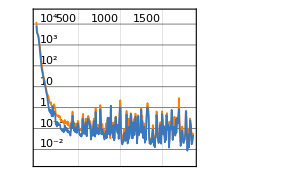
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:9316  rounds:1863  time:31s  examples/s:19858
data | ,,  training examples:300  validation examples:60  processed examples:596224  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.38×10^-2
validation | ,,  loss:8.15×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm30,All,ValidationSet->valdatanorm30,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

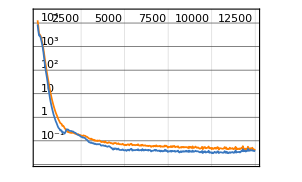
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:62500  rounds:12500  time:6.4min  examples/s:10375
data | ,,  training examples:300  validation examples:60  processed examples:4000000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.5×10^-2
validation | ,,  loss:2.93×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm30,All,ValidationSet->valdatanorm30,MaxTrainingRounds->epoch,LearningRate->.0001, TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm30[[;;,2]]
```

{-19/2,-27,-59/2,-65/2,-69/2,-79/2,-44,-89/2,-97/2,-109/2,-66,-74,-165/2,-86,-99,-199/2,-102,-106,-231/2,-239/2,-241/2,-269/2,-136,-273/2,-141,-297/2,-303/2,-153,-154,-162,-325/2,-329/2,-167,-341/2,-175,-353/2,-355/2,-183,-187,-381/2}

```mathematica
testpred = wNet/@testdatanorm30[[;;,1]]
```

{-9.52103,-26.9979,-29.4777,-32.4316,-34.533,-39.4912,-44.0199,-44.5134,-48.4781,-54.5122,-66.183,-73.8761,-82.6136,-86.2296,-98.6488,-99.2086,-101.957,-106.184,-115.446,-119.046,-119.921,-134.695,-136.236,-136.744,-141.196,-148.163,-150.803,-152.184,-153.325,-162.06,-162.583,-164.653,-167.184,-170.628,-174.894,-176.339,-177.376,-182.916,-187.039,-190.545}

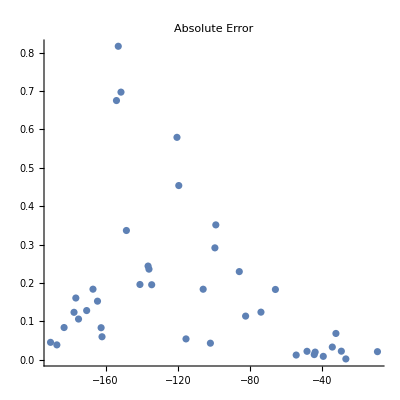

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

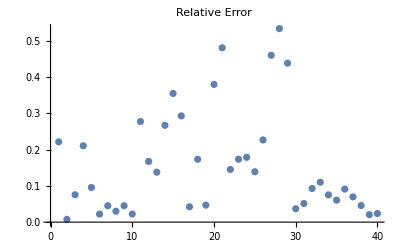

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.159219

## Real negative powers (chosen at random)

```mathematica
minweight = -300;
coeffnum=50;
datasize=500;
```

```mathematica
weights=Rationalize[SetPrecision[RandomReal[{minweight,-0.01},datasize], 4], 0];
```

```mathematica
dnexactwrandom = ParallelTable[ If[Mod[weights[[i]],12]==0,  CoefficientList[Assuming[q>0,q^(-(2weights[[i]])/24) Series[(Δ1[q])^((2 weights[[i]])/24),{q,0,coeffnum-Length[polar[weights[[i]]]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2weights[[i]])/24) Series[(Δ1[q])^((2 weights[[i]])/24),{q,0,coeffnum-Length[polar[weights[[i]]]]}]//Normal], q]],{i,datasize}];
```

```mathematica
dnexactwrandomnorm20=Normalize/@dnexactwrandom[[;;,;;20]];
Length[dnexactwrandomnorm20]
```

500

```mathematica
{traindatanorm20,valdatanorm20,testdatanorm20}=datapartition[Thread[dnexactwrandomnorm20->weights]];
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=8500;
```

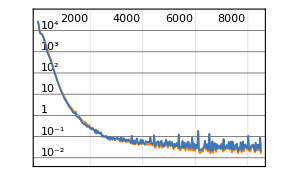
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:51000  rounds:8500  time:1.2min  examples/s:45766
data | ,,  training examples:375  validation examples:75  processed examples:3264000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.42×10^-2
validation | ,,  loss:1.89×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm20,All,ValidationSet->valdatanorm20,MaxTrainingRounds->epoch,LearningRate->.0001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm20[[;;,2]]
```

{-3046/11,-1745/8,-3042/11,-497/6,-299/8,-811/3,-866/7,-799/6,-4357/21,-1139/19,-233/16,-179/3,-678/7,-1011/4,-763/15,-985/6,-853/4,-279/2,-1715/9,-736/7,-793/4,-1417/7,-151/27,-1239/5,-1081/5,-1530/23,-859/6,-1109/4,-1787/20,-4229/15,-1311/5,-2553/20,-134/27,-1588/17,-1825/8,-243/4,-1491/16,-752/7,-1115/4,-666/7,-2651/13,-4178/15,-739/5,-301/4,-544/13,-1137/4,-203/19,-509/4,-667/9,-1039/4}

```mathematica
testpred = wNet/@testdatanorm20[[;;,1]]
```

{-276.897,-218.034,-276.529,-82.5552,-37.3054,-270.334,-123.862,-132.946,-207.451,-59.9074,-14.5591,-59.631,-97.0301,-252.721,-51.0785,-164.011,-213.292,-139.292,-190.535,-105.146,-198.35,-202.403,-5.37989,-247.756,-216.182,-66.3861,-143.219,-277.241,-89.2658,-282.022,-262.139,-127.743,-4.86398,-93.5382,-228.142,-60.6949,-93.3068,-107.296,-278.746,-95.3076,-203.822,-278.529,-147.997,-75.3299,-42.0091,-284.406,-10.748,-127.356,-74.2008,-259.74}

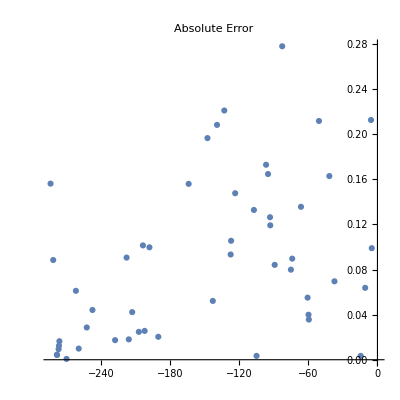

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

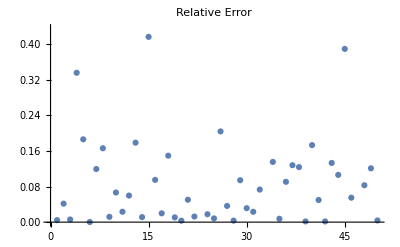

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.20917

## Half-integer positive powers

```mathematica
maxweight=200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, 1/2, maxweight,1/2}];
```

```mathematica
dnexactw200norm30=Normalize/@dnexactw200[[;;,;;30]];
Length[dnexactw200norm30]
```

400

```mathematica
weights=Table[w,{w,1/2, maxweight,1/2}];
```

```mathematica
datanorm30=datapartition[Thread[dnexactw200norm30->weights]];
```

```mathematica
{traindatanorm30,valdatanorm30,testdatanorm30}=datanorm30;
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
```

```mathematica
enc[data_]:=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}]
```

```mathematica
enc20=enc[datanorm20]
```

NetEncoder[…]

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1 },"Input"->enc[datanorm20],"Output"->"Scalar"];
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm30[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=1000;
```

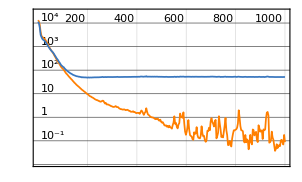
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:5000  rounds:1000  time:20s  examples/s:16500
data | ,,  training examples:300  validation examples:60  processed examples:320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.1×10^-2
validation | ,,  loss:5.05×10^1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm30,All,ValidationSet->valdatanorm30,MaxTrainingRounds->epoch,TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
testexact = testdatanorm20[[;;,2]]
```

{9/2,7,14,18,19,47/2,63/2,32,36,77/2,93/2,49,119/2,63,133/2,135/2,68,74,153/2,83,173/2,87,92,195/2,103,217/2,109,115,235/2,118,129,261/2,145,160,323/2,168,337/2,182,375/2,399/2}

```mathematica
testpred = wNet/@testdatanorm20[[;;,1]]
```

{32.7495,40.4468,13.5711,18.9925,26.389,16.8142,42.3371,41.4432,35.0897,35.2522,42.1938,47.0957,62.6246,65.7443,74.8455,79.1192,78.4922,75.4566,75.1137,88.0934,74.729,70.8939,89.1665,95.0932,99.7713,87.7444,84.9917,113.78,116.326,116.764,129.223,130.823,144.673,160.032,161.667,168.951,169.486,182.432,187.001,195.445}

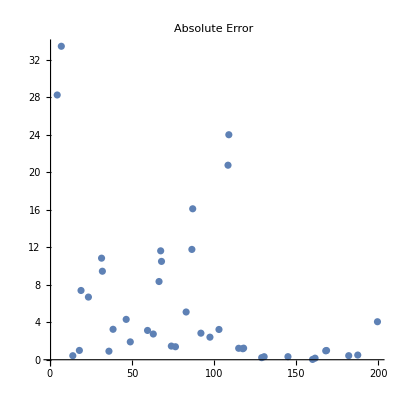

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

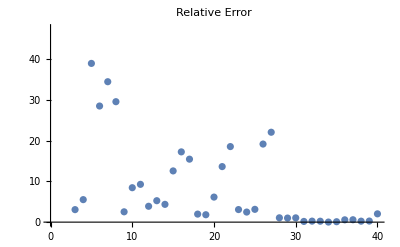

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

35.594

## Randomly chosen slice of coefficients

```mathematica
minweight=-200;
coeffnum=50;
```

```mathematica
dnexactw200 = ParallelTable[ If[Mod[w,12]==0,  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal], q],  CoefficientList[Assuming[q>0,q^(-(2w)/24) Series[(Δ1[q])^((2 w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal], q]],{w, -1/2, minweight, -1/2}];
```

```mathematica
numsamp=20;
```

```mathematica
weights=Table[w,{w, -1/2, minweight, -1/2}];
```

```mathematica
randsamp=Sort[RandomSample[Range[coeffnum],numsamp]]
```

{1,4,7,9,10,13,14,16,18,19,20,21,23,25,30,32,33,41,42,48}

```mathematica
rawdata = dnexactw200[[;;,randsamp]];
normdata=Normalize/@dnexactw200[[;;,randsamp]];
Length[rawdata]
```

400

```mathematica
data=datapartition[Thread[rawdata->weights]];
datanorm=datapartition[Thread[normdata->weights]];
Length[data]
```

3

```mathematica
{traindata,valdata,testdata}=data;
{traindatanorm,valdatanorm,testdatanorm}=datanorm;
```

```mathematica
(*{traindatanorm20,valdatanorm20,testdatanorm20}=datanorm20;*)
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->Length[Keys@traindatanorm[[1]]], "Output"->"Scalar"];
```

```mathematica
KlNet=NetChain[{256, Ramp, 128, LogisticSigmoid, 64, Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1 },"Input"->Length[Keys@traindatanorm[[1]]],"Output"->"Scalar"];
```

```mathematica
KlNet2=NetChain[{256, Ramp, 128, ElementwiseLayer["GELU"], 64, Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4,ElementwiseLayer["GELU"], 1 },"Input"->Length[Keys@traindatanorm20[[1]]],"Output"->"Scalar"];
```

```mathematica
epoch=12500;
```

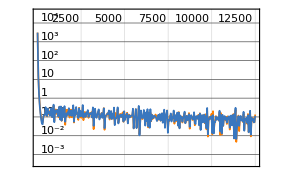
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:62500  rounds:12500  time:6.9min  examples/s:9709
data | ,,  training examples:300  validation examples:60  processed examples:4000000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.3×10^-3
validation | ,,  loss:7.94×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[KlNet,traindatanorm,All,ValidationSet->valdatanorm,MaxTrainingRounds->epoch,TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdatanorm[[;;,2]]
```

{-23/2,-22,-27,-57/2,-48,-51,-111/2,-65,-68,-151/2,-80,-165/2,-84,-89,-195/2,-101,-102,-103,-207/2,-215/2,-112,-227/2,-253/2,-127,-129,-267/2,-134,-271/2,-136,-140,-144,-309/2,-162,-167,-335/2,-337/2,-174,-355/2,-381/2,-196}

```mathematica
testpred = wNet/@testdatanorm[[;;,1]]
```

{-11.5234,-21.9508,-27.0963,-28.5272,-47.9875,-50.9815,-55.5673,-64.9612,-67.9749,-75.4755,-79.979,-82.475,-83.9846,-88.9922,-97.4766,-100.973,-101.98,-102.985,-103.486,-107.499,-112.013,-113.509,-126.507,-127.003,-128.979,-133.446,-133.939,-135.471,-135.979,-140.003,-144.01,-154.531,-161.84,-166.994,-167.503,-168.515,-174.,-177.469,-190.507,-195.988}

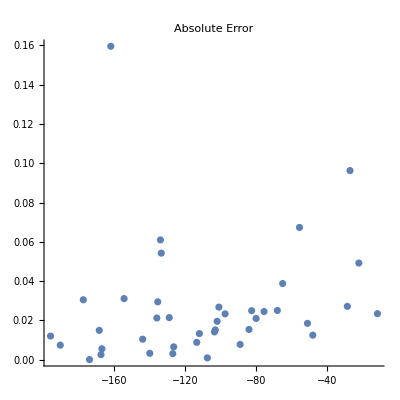

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

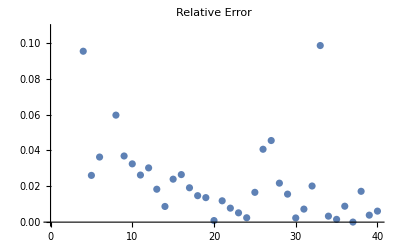

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0427851

## Mock modular forms

## Generating data for negative weights

```mathematica
minweight = -100;
coeffnum=50;
```

```mathematica
cne50w100 = ParallelTable[ If[Mod[w,12]==0,  coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal,q], coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal,q]],{w, -1/2,minweight, -1/2}];
```

```mathematica
w100 = Table[w, {w, -1/2, minweight, -1/2}];
```

## Normalized 10 coefficients

```mathematica
cne50w100norm10=Normalize/@cne50w100[[;;,;;10]];
```

```mathematica
data=MapThread[Rule,{cne10w100,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->10,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

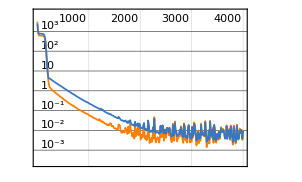
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:15s  examples/s:53452
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.87×10^-2
validation | ,,  loss:2.75×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-19,-55/2,-30,-31,-45,-49,-103/2,-111/2,-57,-71,-79,-165/2,-83,-86,-181/2,-189/2,-96}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-11.8579,-18.9686,-27.5082,-30.0013,-31.0176,-45.0016,-49.0026,-51.5023,-55.5074,-57.0019,-71.0107,-79.0108,-82.5823,-83.0482,-85.963,-90.5124,-94.4849,-95.9833}

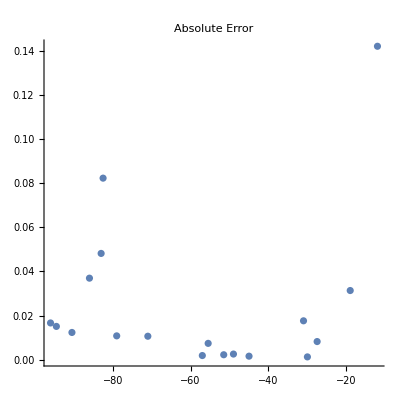

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

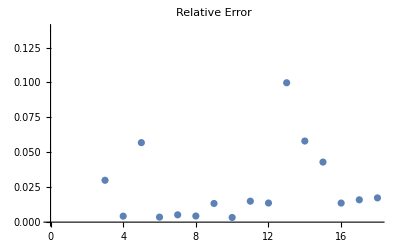

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0970438

## Normalized 30 coefficients

```mathematica
cne50w100norm30=Normalize/@cne50w100[[;;,;;30]];
```

```mathematica
data=MapThread[Rule,{cne50w100norm30,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

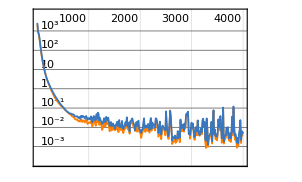
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:46363
data | ,,  training examples:150  validation examples:30  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.13×10^-4
validation | ,,  loss:5.62×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-4,-9/2,-10,-11,-19,-45/2,-35,-36,-41,-87/2,-49,-103/2,-62,-64,-66,-159/2,-173/2,-89,-181/2,-91}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-4.01904,-4.50736,-9.99175,-10.9861,-18.9724,-22.478,-34.9868,-35.9882,-40.9995,-43.4913,-48.993,-51.4901,-61.9679,-64.0045,-65.9944,-79.508,-86.5306,-89.0009,-90.4528,-90.9761}

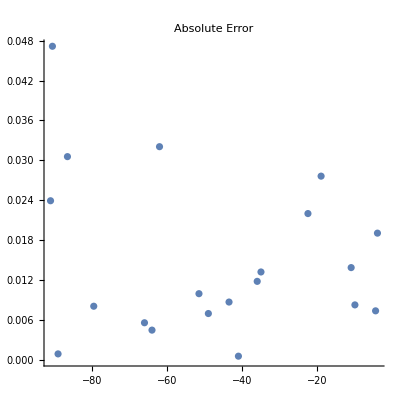

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

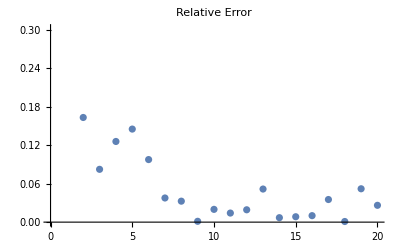

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0704135

## 30 coefficients starting at 11th coefficient

```mathematica
cne50w100norm11to40=Normalize/@cne50w100[[;;,11;;40]];
```

```mathematica
data=MapThread[Rule,{cne50w100norm11to40,w100}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

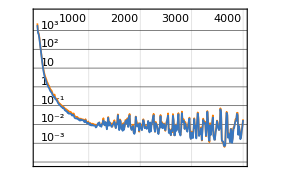
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:45839
data | ,,  training examples:150  validation examples:30  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.86×10^-3
validation | ,,  loss:2.36×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-1,-17/2,-19/2,-13,-29/2,-39/2,-45/2,-25,-51/2,-65/2,-33,-71/2,-43,-44,-61,-123/2,-71,-187/2,-94,-199/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-0.984623,-8.48011,-9.48186,-12.9901,-14.5167,-19.476,-22.4832,-24.9928,-25.4965,-32.5007,-32.9923,-35.4475,-43.0156,-44.003,-61.0033,-61.5056,-70.9836,-93.4771,-93.9854,-99.4147}

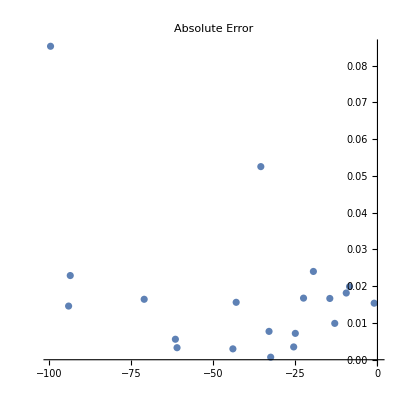

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

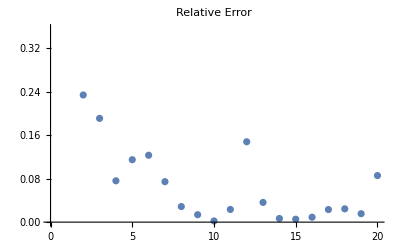

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.138669

## Generating data for positive weights

```mathematica
maxweight = 100;
coeffnum=50;
```

```mathematica
cne50w100plus = ParallelTable[ If[Mod[w,12]==0,  coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]-1}]//Normal,q], coeff[w] =CoefficientList[q^(-(2 w)/24) Series[2 E2[q]/(Δ1[q])^(-(2w)/24),{q,0,coeffnum-Length[polar[w]]}]//Normal,q]],{w, 0,maxweight,1/2}];
```

```mathematica
w100plus = Table[w, {w, 0,maxweight,1/2}];
```

## Normalized 30 coefficients

```mathematica
cne50w100plusnorm30=Normalize/@cne50w100plus[[;;,;;30]];
```

```mathematica
data=MapThread[Rule,{cne50w100plusnorm30,w100plus}];
datasize=Length[data]
```

201

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=6000;
```

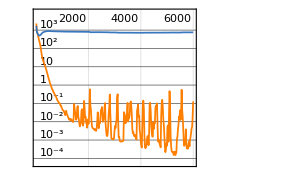
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:18000  rounds:6000  time:37s  examples/s:31805
data | ,,  training examples:150  validation examples:30  processed examples:1152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:2.91×10^-1
validation | ,,  loss:7.44×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001, TargetDevice->"GPU"]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]];
testpred = wNet/@testdata[[;;,1]];
```

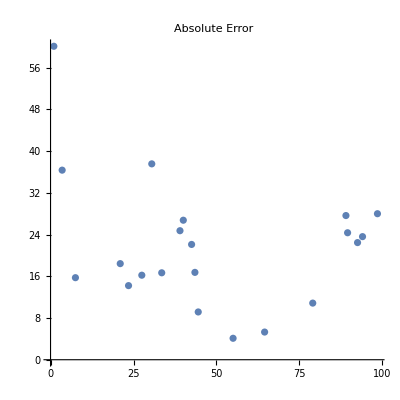

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

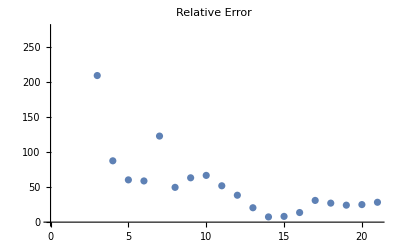

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

383.266

## Coefficients calculated via Kloosterman sums

```mathematica
minweight = -100;
coeffnum=30;
```

```mathematica
cn0c30w100 = Table[If[Mod[w,12]==0,Table[ ψ0[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ0[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
cn0c30w100norm30=Normalize/@cn0c30w100;
```

```mathematica
data=MapThread[Rule,{cn0c30w100norm30,wlist}];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

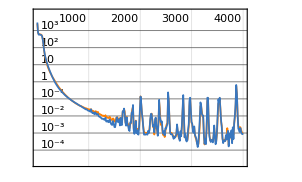
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:18s  examples/s:44348
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:9.83×10^-4
validation | ,,  loss:9.05×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-15,-33/2,-24,-49/2,-53/2,-29,-81/2,-83/2,-101/2,-59,-63,-147/2,-165/2,-173/2,-87,-88,-96,-100}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-14.9777,-16.5018,-24.0065,-24.5083,-26.4925,-29.,-40.5015,-41.5083,-50.4848,-58.9991,-62.9952,-73.4979,-82.4828,-86.4799,-86.9727,-87.9872,-96.0273,-99.8619}

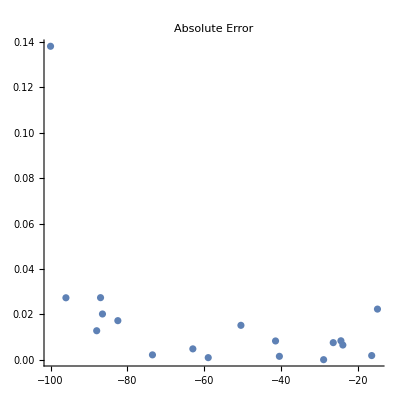

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

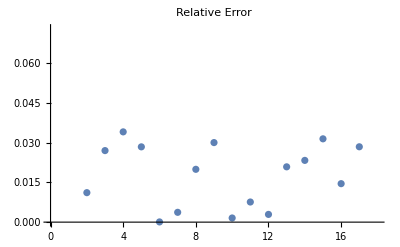

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0317603

## Comparing the real and imaginary parts of Kloosterman sums

```mathematica
minweight=-100;
coeffnum=30;
```

### Absolute values of part 1

```mathematica
cnc50w150abs1 = Table[If[Mod[w,12]==0,Table[ ψ1abs[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ1abs[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150abs1norm=Normalize/@cnc50w150abs1;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150abs1norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

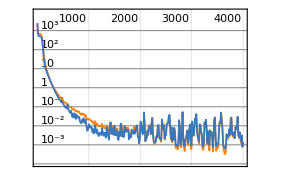
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:15s  examples/s:52883
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:3.18×10^-4
validation | ,,  loss:5.83×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-13,-14,-47/2,-24,-49/2,-41,-42,-44,-52,-63,-127/2,-129/2,-75,-159/2,-85,-177/2,-179/2,-195/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-12.9862,-13.9781,-23.553,-24.0385,-24.5241,-40.9001,-41.9487,-44.0116,-52.0027,-63.0056,-63.5005,-64.5098,-75.0047,-79.4928,-85.0017,-88.4656,-89.4739,-97.5091}

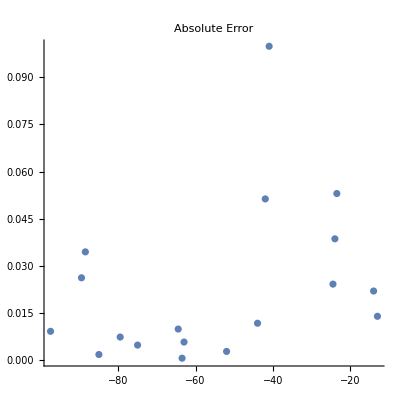

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

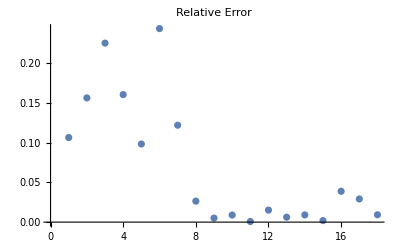

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0702341

### Real values of part 1

```mathematica
cnc50w150re1 = Table[If[Mod[w,12]==0,Table[ ψ1re[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ1re[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150re1norm=Normalize/@cnc50w150re1;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150re1norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

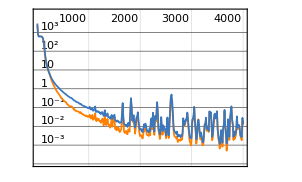
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:16s  examples/s:48043
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.8×10^-2
validation | ,,  loss:1.44×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-13,-27/2,-29/2,-43/2,-36,-45,-46,-113/2,-127/2,-64,-137/2,-75,-173/2,-93,-193/2,-97,-197/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-14.3518,-17.5069,-15.584,-14.4611,-21.5254,-35.994,-45.0078,-45.9739,-56.5226,-63.519,-63.9957,-68.5148,-75.0058,-86.4915,-93.0252,-96.5665,-97.029,-98.5011}

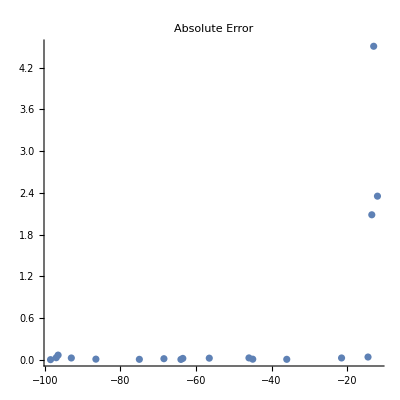

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

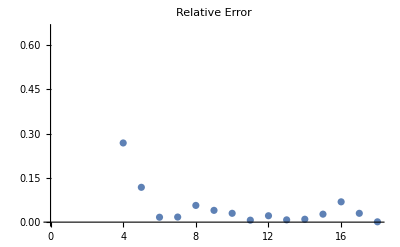

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

3.91242

### Absolute values of part 2

```mathematica
cnc50w150abs2 = Table[If[Mod[w,12]==0,Table[ ψ2abs[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ2abs[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150abs2norm=Normalize/@cnc50w150abs2;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150abs2norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

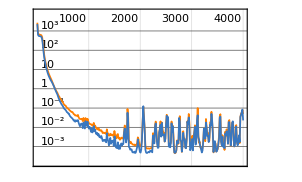
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:46741
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.81×10^-2
validation | ,,  loss:4.77×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-12,-25/2,-13,-49/2,-25,-63/2,-35,-75/2,-87/2,-101/2,-103/2,-54,-72,-73,-153/2,-86,-185/2,-187/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-12.2684,-12.6735,-13.0893,-24.4973,-25.0022,-31.5062,-34.9512,-37.5227,-43.4946,-50.5049,-51.5018,-54.0035,-71.998,-72.9912,-76.5007,-85.9957,-92.4892,-93.4893}

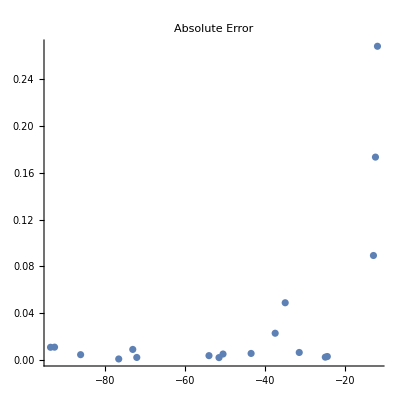

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

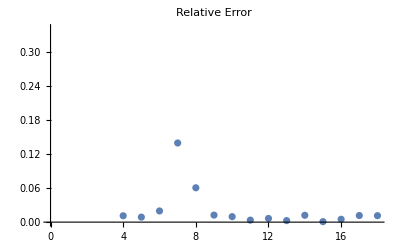

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.257055

### Real values of part 2

```mathematica
cnc50w150re2 = Table[If[Mod[w,12]==0,Table[ ψ2re[m, w], {m, w/12, coeffnum-Length[polar[w]]-1}], Table[ ψ2re[m, w], {m, w/12, coeffnum-Length[polar[w]]}]],{w, -12, minweight, -1/2}] //Quiet;
```

```mathematica
cnc50w150re2norm=Normalize/@cnc50w150re2;
```

```mathematica
wlist=Table[w,{w, -12, minweight, -1/2}];
```

```mathematica
data=Thread[cnc50w150re2norm->wlist];
```

```mathematica
datasize=Length[data];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
MmfNet=NetChain[{LinearLayer[256],ElementwiseLayer[Ramp],LinearLayer[128],ElementwiseLayer[LogisticSigmoid],LinearLayer[64],ElementwiseLayer[Ramp],LinearLayer[1]},"Input"->30,"Output"->"Scalar"];
```

```mathematica
epoch=4000;
```

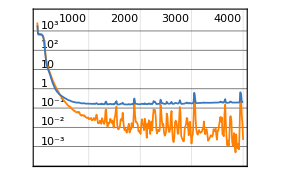
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:12000  rounds:4000  time:17s  examples/s:47423
data | ,,  training examples:132  validation examples:27  processed examples:768000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64CPU
round | ,,  loss:1.93×10^-3
validation | ,,  loss:1.94×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[MmfNet,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch,LearningRate->.001]
{wNet,valLosses}=result[{"TrainedNet","ValidationLossList"}];
```

```mathematica
testexact = testdata[[;;,2]]
```

{-18,-45/2,-61/2,-65/2,-99/2,-101/2,-52,-53,-107/2,-123/2,-129/2,-133/2,-70,-75,-88,-91,-189/2,-197/2}

```mathematica
testpred = wNet/@testdata[[;;,1]]
```

{-17.9894,-22.5604,-30.5035,-32.4917,-49.4998,-50.4841,-51.9909,-52.999,-53.4809,-61.4894,-64.4768,-66.4838,-69.9518,-74.9958,-87.9364,-91.032,-94.4711,-98.2707}

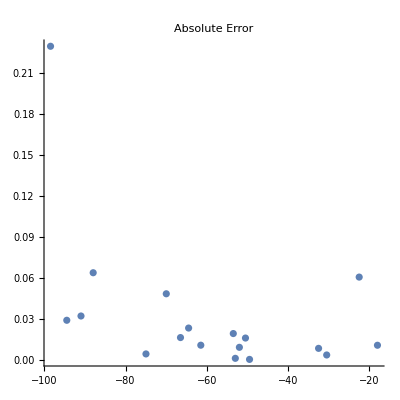

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

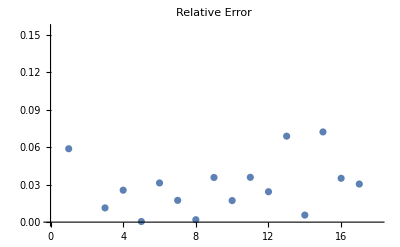

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0541437

## θ_1^k θ_2^l

0.351244 mean relative error for θ_1^m θ_2^n, with m,n∈[1,20] and q up to 𝒪(q^30) and 𝒪(u^50).

## Positive powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
t1t2k20l20q70u80mfpos1 = ParallelTable[allprodθ[1,k, 2, l, 3, 0, 4, 0, 70, 80], {k, 20}, {l, 20}];
DumpSave["t1t2k20l20q70u80mfpos1.mx", t1t2k20l20q70u80mfpos1];
```

### t1t2k20l20q70u80mfpos1, net0, 26 coeffs(r)

```mathematica
<<t1t2k20l20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t1t2k20l20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{14,17,18,26,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
Length /@ Keys[data] // Union
```

14193

{26}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 10000;
```

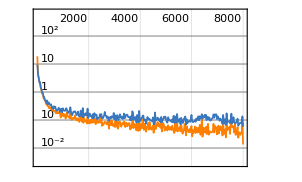
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:34min  examples/s:23910
data | ,,  training examples:6144  validation examples:1229  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.55×10^-2
validation | ,,  loss:5.57×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 11 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

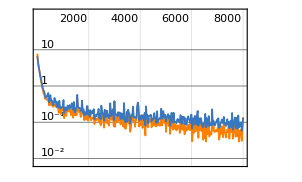
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:32min  examples/s:25568
data | ,,  training examples:6126  validation examples:1225  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.95×10^-2
validation | ,,  loss:5.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 21 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

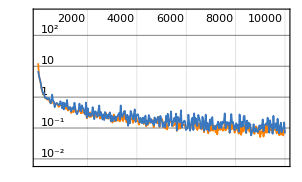
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1670000  rounds:10000  time:1.6h  examples/s:18204
data | ,,  training examples:10644  validation examples:2129  processed examples:106880000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.14×10^-2
validation | ,,  loss:5.12×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net0*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net3*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

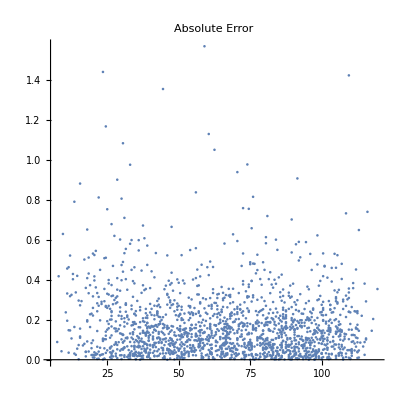

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

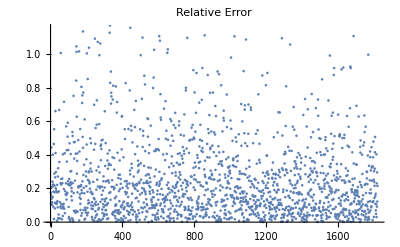

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.351244

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

### t1t2k20l20q70u80mfpos1, net3, 26 coeffs

```mathematica
<<t1t2k20l20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t1t2k20l20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{14,17,18,26,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
Length /@ Keys[data] // Union
```

14193

{26}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 10000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 11 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:34min  examples/s:23910
data | ,,  training examples:6144  validation examples:1229  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.55×10^-2
validation | ,,  loss:5.57×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 21 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:768000  rounds:8000  time:32min  examples/s:25568
data | ,,  training examples:6126  validation examples:1225  processed examples:49152000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.95×10^-2
validation | ,,  loss:5.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net0*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1670000  rounds:10000  time:1.6h  examples/s:18204
data | ,,  training examples:10644  validation examples:2129  processed examples:106880000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.14×10^-2
validation | ,,  loss:5.12×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs net3*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.351244

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## Negative powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
t1t2k5l5q50u60mfneg = ParallelTable[allprodθ[1,k, 2, l, 3, 0, 4, 0, 50, 60], {k, -1, -5, -1}, {l, -1, -5, -1}];
DumpSave["t1t2k5l5q50u60mfneg.mx", t1t2k5l5q50u60mfneg];
t1t2k10l10q70u80mfneg = ParallelTable[allprodθ[1,k, 2, l, 3, 0, 4, 0, 50, 60], {k, -1, -5, -1}, {l, -1, -5, -1}];
DumpSave["t1t2k10l10q70u80mfneg.mx", t1t2k10l10q70u80mfneg];
```

#### t1t2k5l5q50u60mfneg, Net0, 26 coeffs(r)

```mathematica
rawdata =Flatten[t1t2k5l5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{13,25,26,27}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

803

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

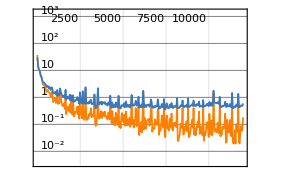
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:3.6min  examples/s:36024
data | ,,  training examples:602  validation examples:120  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:6.67×10^-1
validation | ,,  loss:9.68×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

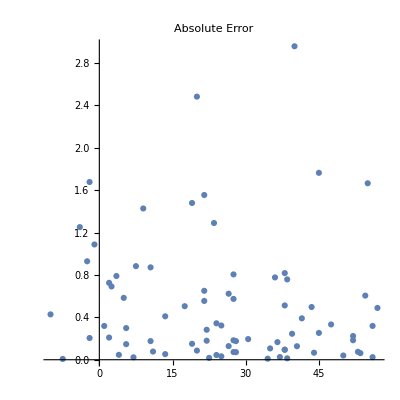

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

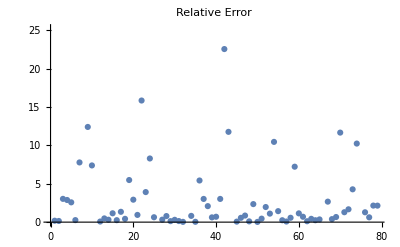

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

7.05481

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t1t2k5l5q50u60mfneg, Net3, 26 coeffs

```mathematica
rawdata =Flatten[t1t2k5l5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{13,25,26,27}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

803

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

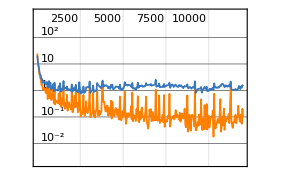
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:4.7min  examples/s:27360
data | ,,  training examples:602  validation examples:120  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.22×10^-2
validation | ,,  loss:1.03
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

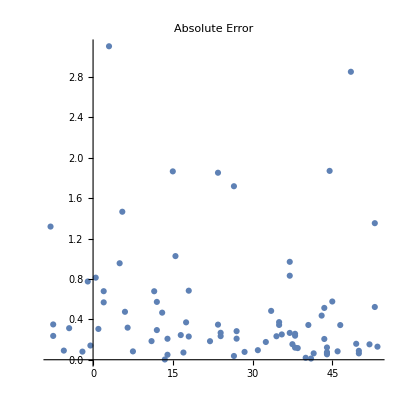

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

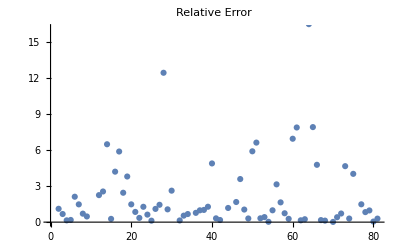

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

8.21258

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## θ_3^m θ_4^n

0.144678 mean relative error for θ_3^m θ_4^n, with m,n∈[1,20] and q up to 𝒪(q^30) and 𝒪(u^50).

## Positive powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
t3t4m5n5q70u80mfpos1 = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 70, 80], {m, 5}, {n, 5}];
DumpSave["t3t4m5n5q70u80mfpos1.mx", t3t4m5n5q70u80mfpos1];
```

```mathematica
t3t4m20n20q70u80mfpos1 = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 70, 80], {m, 20}, {n, 20}];
DumpSave["t3t4m20n20q70u80mfpos1.mx", t3t4m20n20q70u80mfpos1];
```

General::stop: Further output of LaunchKernels::clone will be suppressed during this calculation.

```mathematica
(*t3t4m20n20q30u50mfpos1 = ParallelTable[prod1pos[3,m, 4, n,30,50], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q30u50mfpos1.mx", t3t4m20n20q30u50mfpos1];*)
(*t3t4m20n20q50u50mfpos1 = ParallelTable[prod1pos[3,m, 4, n,50,50], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q50u50mfpos1.mx", t3t4m20n20q50u50mfpos1];*)
(*t3t4m20n20q70u100mfpos1 = ParallelTable[prod1pos[3,m, 4, n,70,100], {m,20}, {n, 20}];
DumpSave["t3t4m20n20q70u100mfpos1.mx", t3t4m20n20q70u100mfpos1];*)
```

### t3t4m20n20q70u80mfpos1, net0, 35 coeffs(r)

```mathematica
<<t3t4m20n20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t3t4m20n20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{17,35,49,52,53,60,69,70}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

15960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

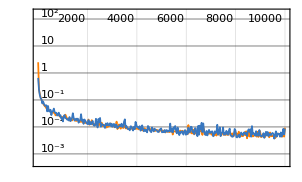
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:1.5h  examples/s:21565
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.95×10^-3
validation | ,,  loss:2.62×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

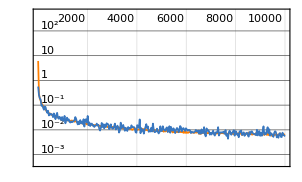
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:2.2h  examples/s:15024
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.91×10^-3
validation | ,,  loss:2.4×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

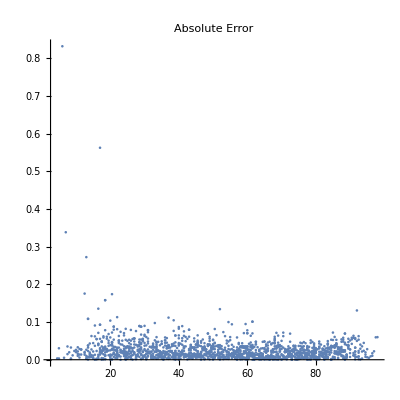

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

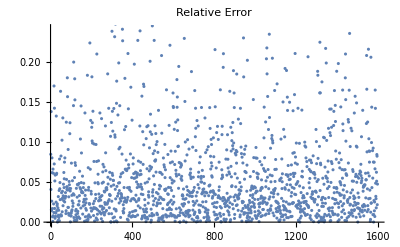

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.0810791

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

### t3t4m20n20q70u80mfpos1, net3, 35 coeffs

```mathematica
<<t3t4m20n20q70u80mfpos1.mx
```

```mathematica
rawdata =Flatten[t3t4m20n20q70u80mfpos1, 2];
Length /@ Keys[rawdata] // Union
```

{17,35,49,52,53,60,69,70}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

15960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:1.5h  examples/s:21565
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.95×10^-3
validation | ,,  loss:2.62×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 35 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1880000  rounds:10000  time:2.2h  examples/s:15024
data | ,,  training examples:11970  validation examples:2394  processed examples:120320000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.91×10^-3
validation | ,,  loss:2.4×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0810791

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## Negative powers

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
(*t3t4m3n3q40u50mfneg = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 40, 50], {m, -1, -3, -1}, {n, -1, -3, -1}];
DumpSave["t3t4m3n3q40u50mfneg.mx", t3t4m3n3q40u50mfneg];*)
t3t4m5n5q50u60mfneg = ParallelTable[allprodθ[1,0, 2, 0, 3, m, 4, n, 50, 60], {m, -1, -5, -1}, {n, -1, -5, -1}];
DumpSave["t3t4m5n5q50u60mfneg.mx", t3t4m5n5q50u60mfneg];
```

#### t3t4m5n5q50u60mfneg, Net0, 25 coeffs

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

750

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

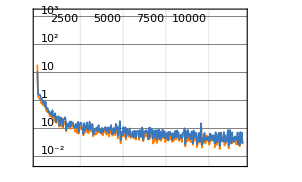
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:108000  rounds:12000  time:3.4min  examples/s:33696
data | ,,  training examples:562  validation examples:113  processed examples:6912000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.83×10^-2
validation | ,,  loss:1.41×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

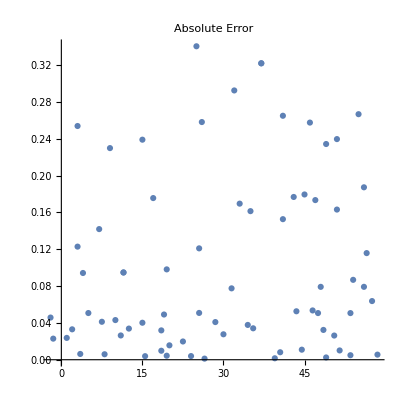

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

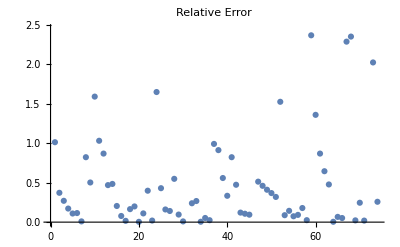

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.66833

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t3t4m5n5q50u60mfneg, Net3, 25 coeffs(r)

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

750

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

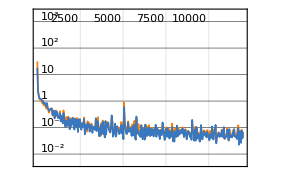
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:108000  rounds:12000  time:5.4min  examples/s:21228
data | ,,  training examples:562  validation examples:113  processed examples:6912000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.88×10^-2
validation | ,,  loss:1.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

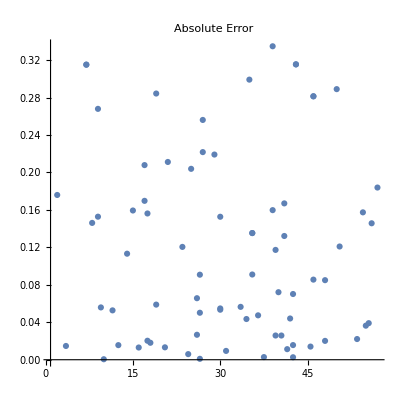

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

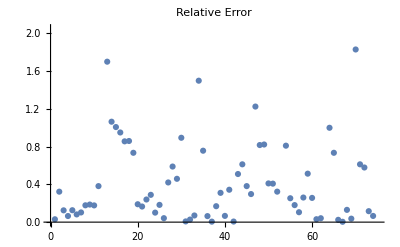

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.666275

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t3t4m5n5q50u60mfneg, Net0, 50 coeffs

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

600

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

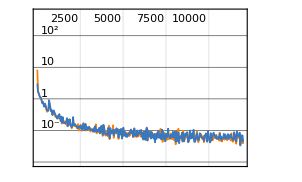
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:96000  rounds:12000  time:5.8min  examples/s:17778
data | ,,  training examples:450  validation examples:90  processed examples:6144000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.63×10^-2
validation | ,,  loss:3.47×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

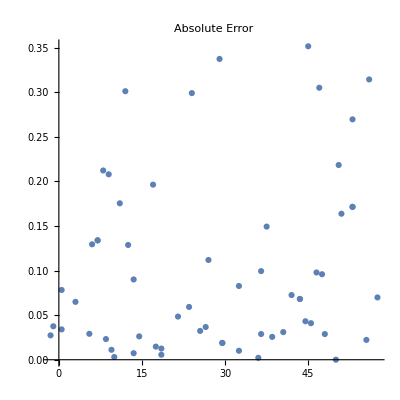

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

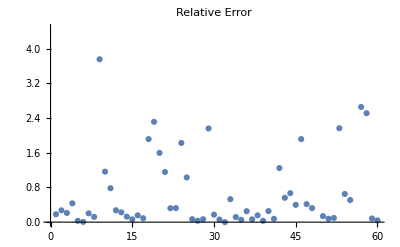

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.992729

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### t3t4m5n5q50u60mfneg, Net3, 50 coeffs

```mathematica
rawdata =Flatten[t3t4m5n5q50u60mfneg, 2];
Length /@ Keys[rawdata] // Union
```

{25,50}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

600

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

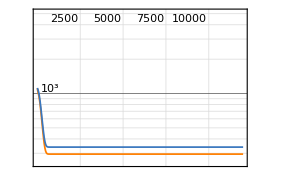
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:96000  rounds:12000  time:8.1min  examples/s:12612
data | ,,  training examples:450  validation examples:90  processed examples:6144000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.95×10^2
validation | ,,  loss:3.39×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

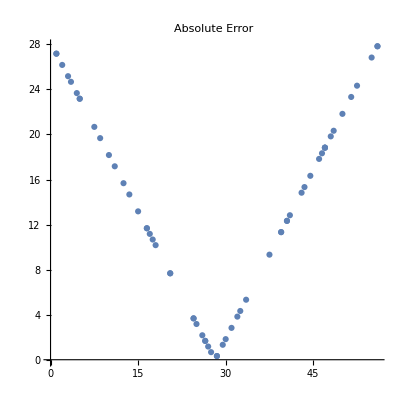

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

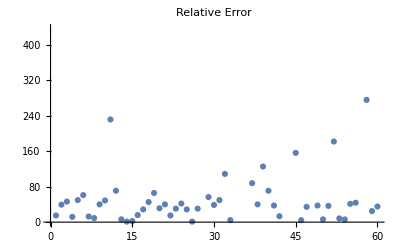

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

204.762

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## θ_1^k θ_2^l θ_3^m θ_4^n

## Only Positive powers {k,l,m,n} > 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
tallk5l5m5n5q70u80mfpos1 = ParallelTable[allprodθ[1,k, 2, l, 3, m, 4, n, 70, 80], {k, 5}, {l, 5}, {m, 5}, {n, 5}];
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q70u80mfpos1, 4];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,31,34,35,53,56,58,59,60,62,67,68,69,70}

```mathematica
data = datadefn[rawdata, 53];
```

```mathematica
datasize = Length[data]
```

19598

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 4, Ramp 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 10000;
```

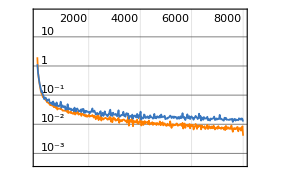
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1088000  rounds:8000  time:30min  examples/s:39097
data | ,,  training examples:8700  validation examples:1740  processed examples:69632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:6.14×10^-3
validation | ,,  loss:1.88×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 26 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

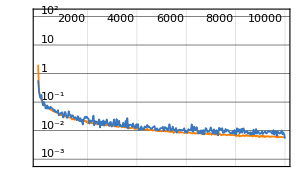
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2300000  rounds:10000  time:2.6h  examples/s:15984
data | ,,  training examples:14698  validation examples:2940  processed examples:147200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.88×10^-3
validation | ,,  loss:3.31×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 53 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

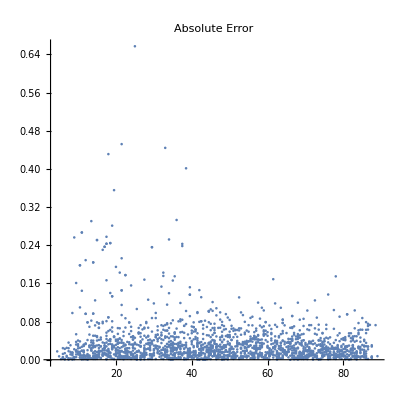

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

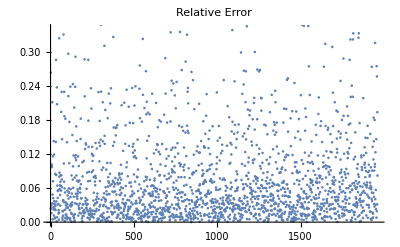

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

0.110949

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## k+l+m+n>0 (k,l,m,n need not be all > 0)

```mathematica
plist=klmnpos[5,400];
```

```mathematica
(*allprodgen[50,70,plist,plist[[141;;150]]]*)
```

#### jacobi-klmn, Net0, 43 coeffs

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
```

3229

```mathematica
Length /@ Keys[fdata] // Union
```

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

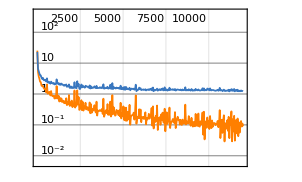
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:2.1h  examples/s:3498
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.86×10^-1
validation | ,,  loss:1.44
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

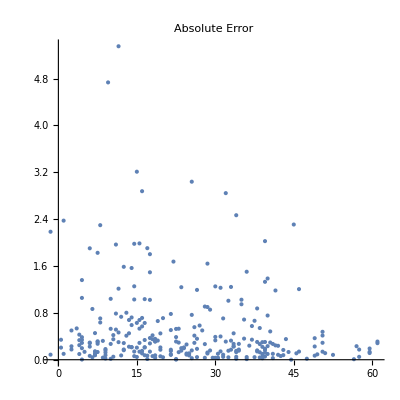

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

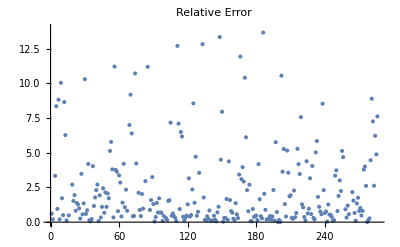

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

5.1182

#### jacobi-klmn, Net3, 43 coeffs(r)

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
```

3229

```mathematica
Length /@ Keys[fdata] // Union
```

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

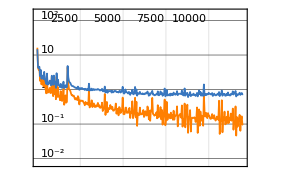
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:13min  examples/s:32683
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.66×10^-2
validation | ,,  loss:6.2×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

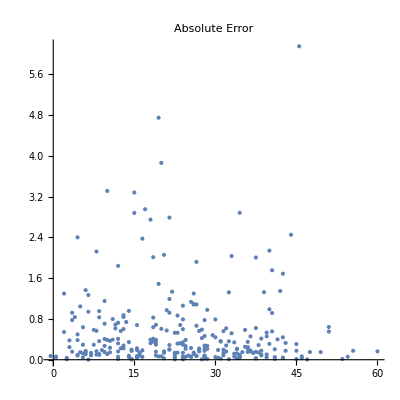

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

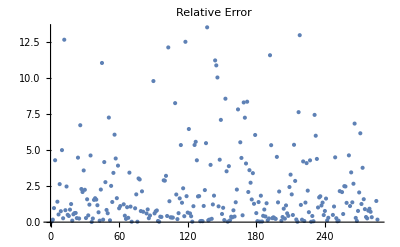

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

3.88915

## Only Negative powers {k,l,m,n} < 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
(*tallk2l2m2n2q20u30mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,20,30], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q20u30mfneg.mx", tallk2l2m2n2q20u30mfneg];
tallk2l2m2n2q40u50mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,40,50], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q40u50mfneg.mx", tallk2l2m2n2q40u50mfneg];*)
tallk2l2m2n2q50u60mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,50,60], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q50u60mfneg.mx", tallk2l2m2n2q50u60mfneg];
(*tallk3l3m3n3q40u50mfneg = ParallelTable[allprodθ[1, k, 2, l, 3,m, 4, n,40,50], {k,0,-3, -1},{l,0,-3, -1}, {m,0,-3, -1}, {n,0,-3, -1}];
DumpSave["tallk3l3m3n3q40u50mfneg.mx", tallk3l3m3n3q40u50mfneg];*)
```

#### tallk2l2m2n2q40u50mfneg, Net0, 40 coeffs(r)

```mathematica
<<tallk2l2m2n2q40u50mfneg.mx
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg, 4];
Length[rawdata]
Length /@ Keys[rawdata] // Union
```

2099

{20,21,40,41,42}

```mathematica
data = datadefn[rawdata, 40];
datasize = Length[data]
```

1416

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

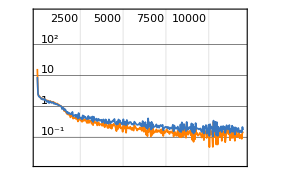
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:6.3min  examples/s:34565
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.78×10^-2
validation | ,,  loss:8.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

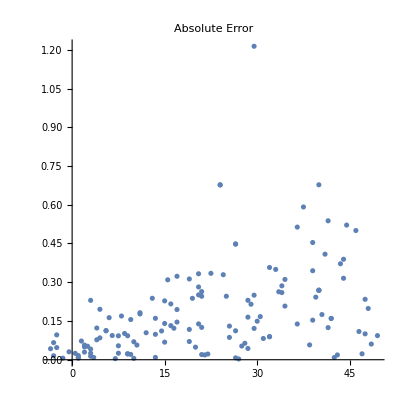

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

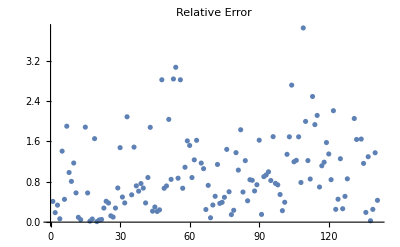

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

1.14707

#### tallk2l2m2n2q40u50mfneg, Net3, 40 coeffs

```mathematica
<<tallk2l2m2n2q40u50mfneg.mx
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg, 4];
Length[rawdata]
Length /@ Keys[rawdata] // Union
```

2099

{20,21,40,41,42}

```mathematica
data = datadefn[rawdata, 40];
datasize = Length[data]
```

1416

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

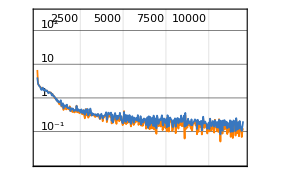
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:7.0min  examples/s:30924
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.38×10^-2
validation | ,,  loss:1.16×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

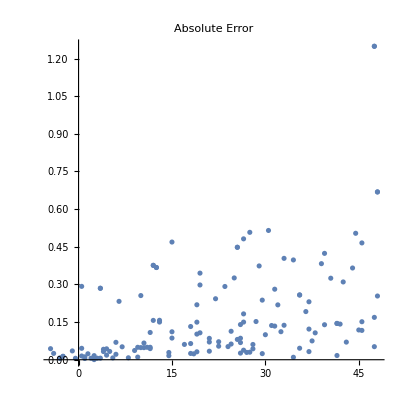

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

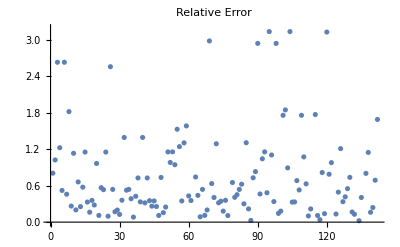

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

1.36787

## k+l+m+n<0 (k,l,m,n need not be all < 0)

```mathematica
(*plist=powersneg[5];*)
(*plist=klmnneg[5, 400];*)
```

```mathematica
(*allprodgen[50,70,plist,plist[[141;;150]]]*)
```

#### jacobi-klmn-neg, Net0, 36 coeffs(r)

```mathematica
rawdata1=Import["jacobi-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobi-klmn-neg-2.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobi-klmn-neg-3.txt", Path->NotebookDirectory[]];
rawdata4=Import["jacobi-klmn-neg-4.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
data4 = extractMF[rawdata4];
```

```mathematica
fdata = Join[data1, data2, data3, data4];
Length[fdata]
```

8242

```mathematica
Length /@ Keys[fdata] // Union
```

{6,7,8,12,15,19,20,21,22,30,31,32,34,35,39,40,41,42,43}

```mathematica
data = datadefn[fdata, 40];
newkeys = Keys[data][[All,;;-5]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

7221

{36}

```mathematica
(*( NumericQ/@(traindata[[2625,1]]//N)//Union)==={True}*)
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
traindata[[3525]] // N
```

{4.27264×10^-7,4.20954×10^-6,0.0000224917,0.0000908428,0.000315714,0.000991569,0.00287415,0.00780589,0.0201089,0.0495152,0.148638,-8.12796,1166.62,-95597.4,5.11654×10^6,-1.92659×10^8,5.4057×10^9,-1.18237×10^11,2.08989×10^12,-3.07319×10^13,3.85001×10^14,-4.19022×10^15,4.0269×10^16,-3.46398×10^17,2.698×10^18,-1.92137×10^19,1.2616×10^20,-7.6932×10^20,4.38424×10^21,-2.34781×10^22,1.18715×10^23,-5.69206×10^23,2.59778×10^24,-1.13232×10^25,4.72812×10^25,-1.89646×10^26}→40.5

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

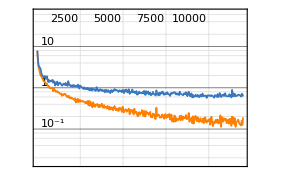
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1020000  rounds:12000  time:45min  examples/s:23936
data | ,,  training examples:5415  validation examples:1083  processed examples:65280000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.86×10^-1
validation | ,,  loss:7.6×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

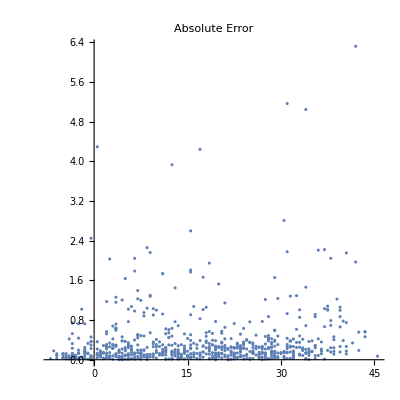

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

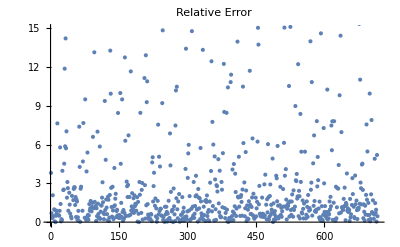

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

6.31506

#### jacobi-klmn-neg, Net3, 36 coeffs

```mathematica
rawdata1=Import["jacobi-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobi-klmn-neg-2.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobi-klmn-neg-3.txt", Path->NotebookDirectory[]];
rawdata4=Import["jacobi-klmn-neg-4.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
data4 = extractMF[rawdata4];
```

```mathematica
fdata = Join[data1, data2, data3, data4];
Length[fdata]
```

8242

```mathematica
Length /@ Keys[fdata] // Union
```

{6,7,8,12,15,19,20,21,22,30,31,32,34,35,39,40,41,42,43}

```mathematica
data = datadefn[fdata, 40];
newkeys = Keys[data][[All,;;-5]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

7221

{36}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

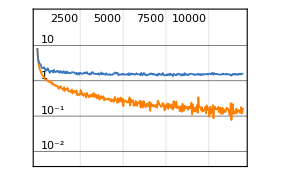
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:1020000  rounds:12000  time:1.3h  examples/s:13916
data | ,,  training examples:5415  validation examples:1083  processed examples:65280000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.02×10^-2
validation | ,,  loss:1.41
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

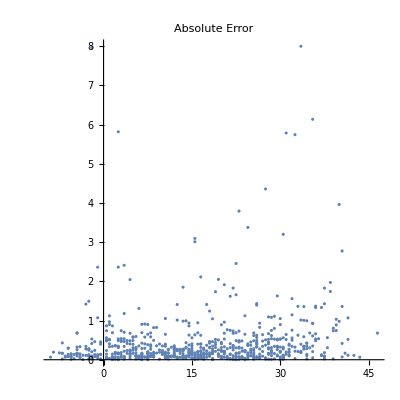

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

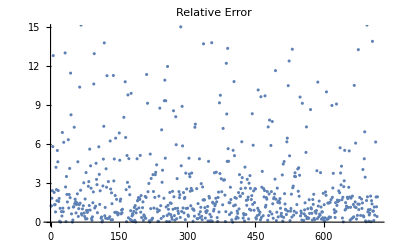

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

7.08278

## θ_1^k θ_2^l θ_3^m θ_4^n/Δ

## Only Positive powers {k,l,m,n} > 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
tallk5l5m5n5q50u60mfpos0 = ParallelTable[Quiet @ allprodθbyΔ[1,k, 2, l, 3, m, 4, n, 50, 60, 0], {k, 5}, {l, 5}, {m, 5}, {n, 5}];
DumpSave["tallk5l5m5n5q50u60mfpos0.mx", tallk5l5m5n5q50u60mfpos0];
```

#### tallk5l5m5n5q50u60mfpos0, Net0, 25 coeffs(r)

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 26];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

18239

```mathematica
Length /@ Keys[data] // Union
```

{25}

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

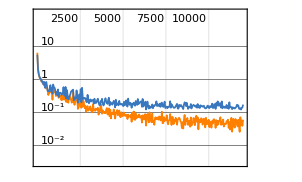
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:2568000  rounds:12000  time:2.1h  examples/s:21238
data | ,,  training examples:13679  validation examples:2736  processed examples:164352000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.54×10^-1
validation | ,,  loss:6.4×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

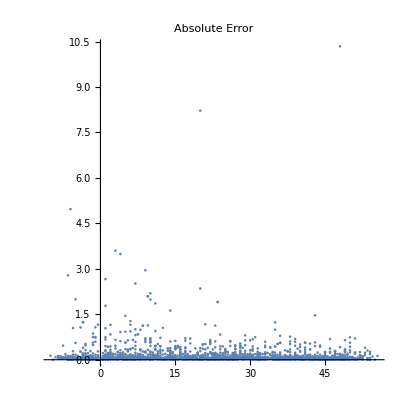

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

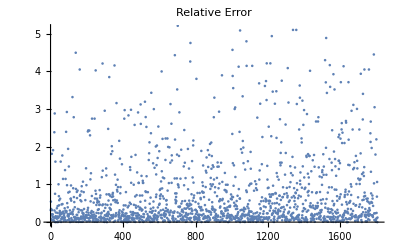

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

2.78562

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### tallk5l5m5n5q50u60mfpos0, Net3, 25 coeffs

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 26];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

18239

```mathematica
Length /@ Keys[data] // Union
```

{25}

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

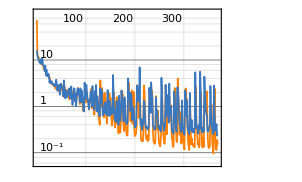
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:79027  rounds:369  time:5.7min  examples/s:14848
data | ,,  training examples:13679  validation examples:2736  processed examples:5057728  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.52×10^-1
validation | ,,  loss:2.47×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

{NetChain[…],{16.0926,11.9417,12.7808,10.7139,10.5111,8.93514,8.706,9.56276,7.48489,10.4442,8.14548,10.7495,6.95333,9.13793,7.72118,6.81918,5.72008,7.03171,8.11831,4.67765,6.18557,4.44467,4.67148,6.18168,3.94506,4.71163,3.21388,3.66859,3.99813,2.9964,3.1201,3.40314,3.15504,2.72024,3.18338,2.82781,2.99386,2.70992,2.98149,4.71385,2.77414,3.00927,2.18779,2.76448,2.61506,2.12827,2.93845,1.77033,2.83599,1.67607,4.50406,2.71944,2.47134,2.14134,1.63109,2.69921,4.55554,1.91445,1.48809,2.25025,1.58571,2.15713,1.57429,1.99194,1.8526,2.90508,1.99093,1.80389,1.4765,1.53903,2.69787,2.04037,1.2148,1.0722,1.77905,1.54136,2.30208,2.61964,1.28543,1.8712,1.00941,2.37994,0.902768,2.35197,2.4627,1.80541,2.02093,1.08538,1.37369,2.43975,1.22857,2.20887,1.98397,1.36891,1.34718,0.839483,0.77669,0.808365,5.701,1.41746,2.40846,2.89852,1.8324,0.687148,1.84173,1.3877,0.869494,1.28626,0.778902,2.09805,2.08162,1.32737,0.982693,1.40927,4.05842,1.23398,1.4557,0.834442,2.15352,1.87722,0.838156,2.88944,0.775091,1.63078,1.89756,0.657817,0.774783,0.667926,0.612098,2.47978,1.49285,0.940459,2.25303,1.17497,0.639982,0.52118,0.994008,1.01972,0.714663,1.23232,1.56942,0.547212,0.649391,0.64335,2.2404,1.24647,0.918884,1.71444,0.620284,1.29436,0.667836,1.24048,0.633874,0.683968,0.720698,4.75539,2.48478,1.129,0.661845,0.501406,0.83661,0.469502,1.37691,1.23815,0.618178,0.513137,0.396855,2.41645,0.968578,0.506419,0.486792,0.72617,1.40826,2.96528,1.37715,1.36421,0.480305,0.480042,0.419483,2.73064,0.739148,0.484611,0.433849,0.41813,0.403046,0.475134,4.00832,1.54767,3.04069,0.988029,1.11156,0.776653,1.92374,1.25709,0.472821,0.538992,0.962304,0.917579,0.491703,0.356179,0.343321,0.435686,0.384582,1.34313,2.7927,2.82787,1.61048,1.30312,1.37397,6.94818,0.628673,0.422697,0.381513,0.531699,0.310958,0.382031,0.44538,0.412753,1.31918,1.16619,0.540989,0.514693,0.343317,0.360958,0.367236,0.314876,0.324899,0.340877,0.349714,2.50361,1.42139,1.03089,0.417355,3.29193,1.95176,1.41899,0.42506,0.322963,0.365225,0.315203,0.31448,0.34471,2.17267,0.966683,0.667695,0.802847,0.555018,0.407986,0.279674,0.384187,0.310248,0.391725,0.289416,0.549491,7.70718,1.65149,0.424256,0.421447,0.302143,0.30202,0.320151,0.386696,2.91529,0.750104,0.434534,0.769269,0.925066,1.77453,0.445621,4.79508,1.38226,0.901007,0.664683,0.988947,0.348633,0.316028,0.296406,0.274686,0.257373,0.380953,3.8014,1.6019,0.502469,0.351612,0.285675,0.327076,4.72541,2.57843,1.5997,0.674357,0.385859,0.446572,0.379513,0.289148,0.278758,2.00972,0.691886,0.327127,0.337194,0.272207,0.243914,0.405941,3.9943,1.96126,0.622385,1.33053,0.437016,0.304258,0.301545,0.288492,0.251765,3.04475,0.843812,0.400923,0.303276,0.514034,0.275643,0.232961,0.350032,0.322863,0.270921,0.373931,2.45135,8.35501,0.945073,0.336518,0.371196,0.421567,0.281015,0.259408,0.399217,0.319492,5.6113,2.19203,1.92803,0.368692,0.272372,0.279473,0.433919,0.259159,0.28881,4.38355,1.79571,0.743435,1.41533,0.694694,0.671538,0.302792,0.283755,0.301587,0.30221,0.360578,0.377448,2.75124,1.27086,0.496083,0.437406,0.311006,0.252385,0.231329,0.293349,2.80962,0.575492,0.299476,0.309908,0.240181,0.58681,0.234391,0.247358}}

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

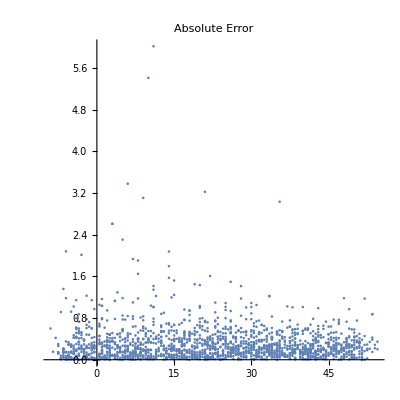

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

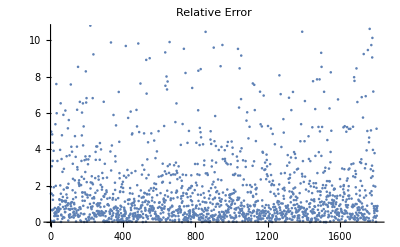

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

4.53036

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

#### tallk5l5m5n5q50u60mfpos0, Net0, 48 coeffs

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 49];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

14590

```mathematica
Length /@ Keys[data] // Union
```

{48}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

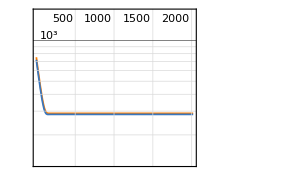
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:345279  rounds:2019  time:10min  examples/s:35890
data | ,,  training examples:10942  validation examples:2189  processed examples:22097856  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.89×10^2
validation | ,,  loss:2.84×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

{NetChain[…],{752.842,745.539,738.317,731.197,724.129,717.129,710.237,703.386,696.626,689.912,683.287,676.724,670.235,663.81,657.419,651.125,644.894,638.715,632.595,626.557,620.538,614.612,608.734,602.91,597.156,591.444,585.808,580.215,574.688,569.208,563.785,558.419,553.111,547.857,542.671,537.525,532.426,527.4,522.425,517.507,512.635,507.825,503.08,498.376,493.733,489.136,484.592,480.101,475.681,471.291,466.97,462.72,458.502,454.347,450.24,446.196,442.186,438.24,434.37,430.533,426.754,423.012,419.35,415.725,412.151,408.638,405.179,401.759,398.416,395.121,391.871,388.674,385.52,382.446,379.405,376.416,373.479,370.601,367.759,364.991,362.257,359.581,356.962,354.4,351.863,349.399,346.999,344.626,342.307,340.04,337.815,335.656,333.543,331.48,329.46,327.504,325.578,323.716,321.908,320.132,318.414,316.73,315.11,313.549,312.009,310.527,309.077,307.697,306.359,305.056,303.821,302.607,301.433,300.327,299.252,298.216,297.219,296.279,295.387,294.519,293.698,292.915,292.176,291.469,290.803,290.183,289.586,289.031,288.517,288.025,287.564,287.141,286.753,286.394,286.063,285.758,285.475,285.214,284.995,284.787,284.598,284.43,284.285,284.157,284.04,283.942,283.857,283.788,283.727,283.677,283.636,283.604,283.579,283.56,283.547,283.538,283.534,283.532,283.534,283.539,283.543,283.551,283.56,283.57,283.58,283.591,283.602,283.611,283.621,283.63,283.643,283.651,283.661,283.672,283.68,283.693,283.698,283.705,283.715,283.721,283.724,283.732,283.739,283.747,283.75,283.751,283.762,283.764,283.768,283.771,283.778,283.777,283.781,283.782,283.783,283.786,283.79,283.792,283.791,283.795,283.795,283.796,283.798,283.799,283.802,283.803,283.805,283.804,283.803,283.81,283.807,283.808,283.81,283.809,283.812,283.81,283.811,283.811,283.814,283.812,283.811,283.814,283.815,283.811,283.815,283.813,283.817,283.817,283.817,283.816,283.815,283.822,283.815,283.817,283.817,283.818,283.815,283.818,283.816,283.819,283.816,283.816,283.82,283.817,283.818,283.819,283.818,283.819,283.816,283.815,283.818,283.814,283.817,283.818,283.816,283.813,283.818,283.818,283.815,283.818,283.821,283.82,283.813,283.819,283.819,283.82,283.818,283.818,283.819,283.818,283.818,283.816,283.814,283.822,283.817,283.822,283.818,283.819,283.816,283.818,283.82,283.817,283.82,283.82,283.82,283.822,283.821,283.816,283.816,283.819,283.817,283.815,283.818,283.815,283.82,283.819,283.819,283.818,283.823,283.82,283.818,283.814,283.815,283.818,283.816,283.82,283.821,283.818,283.819,283.815,283.819,283.82,283.819,283.821,283.82,283.817,283.817,283.818,283.815,283.819,283.824,283.817,283.819,283.818,283.816,283.821,283.82,283.817,283.819,283.819,283.818,283.82,283.819,283.816,283.816,283.816,283.819,283.817,283.82,283.818,283.818,283.817,283.821,283.819,283.823,283.821,283.819,283.817,283.822,283.82,283.817,283.82,283.82,283.82,283.816,283.819,283.821,283.818,283.818,283.817,283.817,283.814,283.818,283.816,283.817,283.818,283.82,283.815,283.822,283.823,283.817,283.819,283.819,283.816,283.82,283.818,283.819,283.814,283.816,283.819,283.817,283.819,283.816,283.817,283.816,283.82,283.816,283.817,283.818,283.818,283.819,283.819,283.82,283.819,283.816,283.816,283.815,283.818,283.82,283.817,283.818,283.815,283.815,283.814,283.816,283.817,283.817,283.817,283.816,283.815,283.82,283.817,283.819,283.817,283.82,283.818,283.823,283.817,283.814,283.819,283.817,283.818,283.818,283.82,283.817,283.815,283.815,283.822,283.817,283.82,283.818,283.82,283.815,283.821,283.82,283.817,283.817,283.818,283.818,283.819,283.817,283.82,283.817,283.817,283.818,283.821,283.817,283.817,283.818,283.818,283.818,283.817,283.813,283.816,283.82,283.821,283.82,283.819,283.825,283.817,283.82,283.821,283.818,283.819,283.818,283.818,283.819,283.818,283.818,283.818,283.821,283.818,283.818,283.819,283.816,283.817,283.818,283.818,283.817,283.818,283.821,283.821,283.813,283.817,283.82,283.815,283.818,283.819,283.818,283.816,283.819,283.819,283.818,283.819,283.816,283.818,283.817,283.818,283.817,283.819,283.816,283.817,283.817,283.818,283.818,283.817,283.821,283.818,283.817,283.82,283.819,283.819,283.821,283.819,283.817,283.814,283.816,283.816,283.818,283.818,283.818,283.818,283.819,283.814,283.819,283.814,283.817,283.815,283.817,283.819,283.815,283.814,283.819,283.812,283.821,283.819,283.818,283.817,283.818,283.82,283.821,283.819,283.816,283.819,283.817,283.814,283.816,283.818,283.822,283.821,283.815,283.818,283.818,283.816,283.82,283.82,283.82,283.818,283.82,283.82,283.818,283.821,283.816,283.822,283.817,283.818,283.821,283.819,283.819,283.819,283.818,283.818,283.816,283.823,283.819,283.817,283.815,283.816,283.82,283.818,283.82,283.817,283.816,283.817,283.815,283.819,283.82,283.818,283.817,283.821,283.819,283.821,283.819,283.818,283.818,283.817,283.817,283.815,283.82,283.816,283.818,283.82,283.818,283.82,283.82,283.816,283.817,283.821,283.82,283.817,283.82,283.818,283.819,283.82,283.819,283.819,283.817,283.813,283.817,283.82,283.818,283.818,283.822,283.818,283.819,283.82,283.819,283.819,283.817,283.817,283.818,283.819,283.818,283.818,283.819,283.818,283.82,283.822,283.816,283.82,283.82,283.818,283.819,283.817,283.819,283.817,283.818,283.817,283.819,283.819,283.82,283.82,283.817,283.814,283.821,283.822,283.821,283.82,283.819,283.819,283.818,283.82,283.819,283.818,283.817,283.815,283.82,283.818,283.819,283.817,283.822,283.817,283.817,283.82,283.818,283.821,283.82,283.819,283.818,283.819,283.815,283.819,283.818,283.816,283.819,283.82,283.817,283.817,283.817,283.815,283.819,283.82,283.818,283.82,283.819,283.819,283.818,283.819,283.815,283.816,283.819,283.816,283.819,283.815,283.818,283.817,283.813,283.816,283.816,283.815,283.816,283.815,283.82,283.819,283.818,283.824,283.817,283.819,283.823,283.818,283.818,283.817,283.82,283.821,283.821,283.815,283.82,283.822,283.818,283.821,283.821,283.82,283.817,283.816,283.818,283.823,283.818,283.817,283.819,283.817,283.818,283.817,283.818,283.82,283.819,283.82,283.823,283.817,283.816,283.818,283.82,283.822,283.82,283.818,283.82,283.82,283.819,283.82,283.819,283.818,283.817,283.817,283.82,283.816,283.82,283.813,283.82,283.82,283.818,283.813,283.821,283.817,283.818,283.821,283.818,283.816,283.818,283.815,283.819,283.818,283.817,283.821,283.817,283.814,283.82,283.821,283.818,283.82,283.817,283.814,283.821,283.817,283.818,283.816,283.816,283.816,283.82,283.817,283.818,283.823,283.816,283.818,283.817,283.816,283.815,283.817,283.817,283.82,283.818,283.815,283.82,283.816,283.82,283.82,283.82,283.815,283.814,283.818,283.819,283.815,283.813,283.817,283.819,283.819,283.818,283.82,283.818,283.816,283.815,283.817,283.818,283.816,283.819,283.818,283.817,283.814,283.816,283.815,283.817,283.819,283.818,283.818,283.814,283.817,283.818,283.816,283.816,283.815,283.82,283.821,283.818,283.818,283.816,283.817,283.821,283.819,283.817,283.821,283.817,283.82,283.822,283.819,283.816,283.817,283.818,283.82,283.821,283.817,283.818,283.818,283.817,283.815,283.817,283.818,283.818,283.817,283.82,283.819,283.821,283.817,283.819,283.821,283.82,283.818,283.82,283.818,283.816,283.817,283.818,283.818,283.82,283.818,283.823,283.814,283.819,283.819,283.817,283.818,283.817,283.816,283.818,283.817,283.817,283.818,283.819,283.816,283.816,283.816,283.817,283.814,283.816,283.819,283.816,283.819,283.813,283.816,283.817,283.82,283.822,283.82,283.815,283.818,283.819,283.816,283.817,283.82,283.817,283.821,283.821,283.82,283.821,283.823,283.819,283.818,283.819,283.82,283.82,283.818,283.82,283.816,283.817,283.817,283.816,283.821,283.818,283.818,283.818,283.82,283.816,283.819,283.816,283.818,283.82,283.818,283.816,283.819,283.819,283.819,283.82,283.819,283.821,283.818,283.821,283.816,283.821,283.818,283.817,283.815,283.817,283.816,283.817,283.816,283.815,283.822,283.817,283.82,283.818,283.819,283.818,283.818,283.817,283.819,283.818,283.821,283.817,283.818,283.819,283.822,283.818,283.818,283.818,283.82,283.815,283.819,283.821,283.819,283.817,283.819,283.815,283.814,283.82,283.816,283.819,283.819,283.815,283.821,283.817,283.82,283.816,283.818,283.815,283.818,283.821,283.817,283.817,283.818,283.817,283.817,283.815,283.817,283.816,283.817,283.818,283.815,283.816,283.817,283.818,283.816,283.816,283.818,283.817,283.817,283.816,283.817,283.818,283.82,283.816,283.817,283.821,283.819,283.821,283.818,283.818,283.818,283.819,283.818,283.816,283.817,283.819,283.818,283.814,283.815,283.82,283.819,283.82,283.817,283.818,283.813,283.817,283.817,283.813,283.816,283.816,283.818,283.824,283.817,283.815,283.815,283.816,283.822,283.817,283.819,283.818,283.819,283.815,283.816,283.82,283.82,283.816,283.819,283.82,283.819,283.814,283.82,283.817,283.817,283.818,283.817,283.82,283.818,283.816,283.819,283.818,283.821,283.816,283.82,283.823,283.816,283.815,283.816,283.818,283.818,283.821,283.821,283.82,283.82,283.818,283.818,283.819,283.818,283.82,283.819,283.816,283.818,283.818,283.816,283.819,283.817,283.821,283.818,283.815,283.819,283.819,283.815,283.817,283.814,283.816,283.818,283.817,283.818,283.815,283.82,283.816,283.82,283.819,283.816,283.819,283.82,283.814,283.822,283.818,283.818,283.821,283.817,283.819,283.818,283.82,283.818,283.818,283.819,283.818,283.818,283.818,283.819,283.818,283.82,283.816,283.818,283.821,283.818,283.817,283.815,283.814,283.819,283.815,283.814,283.82,283.815,283.818,283.815,283.818,283.818,283.82,283.817,283.818,283.821,283.82,283.816,283.817,283.818,283.819,283.816,283.818,283.819,283.818,283.821,283.817,283.818,283.817,283.819,283.817,283.817,283.817,283.819,283.817,283.817,283.821,283.814,283.816,283.817,283.819,283.82,283.819,283.817,283.817,283.821,283.816,283.818,283.817,283.82,283.819,283.821,283.817,283.823,283.822,283.818,283.821,283.819,283.821,283.818,283.819,283.819,283.818,283.816,283.816,283.82,283.819,283.817,283.82,283.821,283.817,283.817,283.819,283.818,283.816,283.816,283.819,283.816,283.817,283.82,283.817,283.816,283.816,283.818,283.816,283.821,283.818,283.815,283.818,283.816,283.816,283.817,283.815,283.818,283.817,283.82,283.819,283.82,283.816,283.819,283.821,283.816,283.819,283.818,283.815,283.817,283.818,283.815,283.818,283.816,283.818,283.815,283.816,283.814,283.816,283.816,283.816,283.816,283.816,283.816,283.817,283.817,283.821,283.818,283.818,283.821,283.823,283.817,283.818,283.819,283.819,283.816,283.819,283.819,283.817,283.811,283.82,283.816,283.819,283.818,283.82,283.819,283.82,283.819,283.82,283.819,283.82,283.818,283.82,283.818,283.818,283.819,283.816,283.816,283.818,283.819,283.816,283.813,283.819,283.815,283.816,283.819,283.815,283.819,283.818,283.819,283.815,283.821,283.816,283.822,283.814,283.821,283.816,283.822,283.817,283.819,283.822,283.817,283.816,283.82,283.821,283.82,283.819,283.822,283.818,283.819,283.819,283.817,283.818,283.816,283.82,283.821,283.818,283.821,283.819,283.819,283.818,283.817,283.822,283.816,283.817,283.816,283.815,283.815,283.817,283.819,283.82,283.819,283.818,283.82,283.816,283.819,283.819,283.819,283.815,283.818,283.817,283.818,283.821,283.817,283.817,283.82,283.819,283.821,283.818,283.82,283.819,283.819,283.815,283.816,283.816,283.817,283.817,283.815,283.822,283.82,283.818,283.816,283.821,283.816,283.818,283.817,283.816,283.816,283.819,283.815,283.817,283.818,283.817,283.821,283.813,283.821,283.818,283.819,283.82,283.819,283.817,283.819,283.821,283.821,283.824,283.821,283.816,283.819,283.82,283.815,283.819,283.816,283.815,283.817,283.817,283.817,283.818,283.821,283.82,283.819,283.818,283.819,283.819,283.818,283.817,283.815,283.819,283.816,283.82,283.814,283.819,283.818,283.817,283.819,283.819,283.823,283.82,283.818,283.816,283.818,283.82,283.816,283.816,283.82,283.814,283.819,283.82,283.816,283.817,283.818,283.819,283.819,283.815,283.815,283.818,283.817,283.817,283.817,283.819,283.818,283.816,283.816,283.821,283.819,283.818,283.816,283.818,283.818,283.819,283.82,283.816,283.814,283.82,283.815,283.818,283.819,283.817,283.817,283.818,283.819,283.816,283.818,283.816,283.817,283.817,283.816,283.815,283.819,283.814,283.821,283.816,283.818,283.819,283.816,283.817,283.817,283.819,283.818,283.818,283.816,283.818,283.815,283.818,283.82,283.817,283.819,283.819,283.82,283.816,283.818,283.817,283.816,283.821,283.816,283.818,283.821,283.817,283.813,283.815,283.817,283.817,283.821,283.818,283.817,283.815,283.817,283.818,283.818,283.816,283.815,283.816,283.817,283.816,283.819,283.816,283.819,283.819,283.816,283.814,283.819,283.818,283.818,283.813,283.816,283.813,283.82,283.818,283.823,283.817,283.818,283.817,283.817,283.819,283.818,283.822,283.814,283.817,283.819,283.817,283.818,283.818,283.817,283.815,283.817,283.82,283.818,283.817,283.821,283.82,283.819,283.817,283.817,283.818,283.814,283.819,283.819,283.819,283.816,283.819,283.818,283.82,283.82,283.818,283.819,283.818,283.818,283.815,283.817,283.818,283.815,283.82,283.817,283.818,283.819,283.816,283.82,283.819,283.817,283.817,283.817,283.817,283.819,283.814,283.821,283.818,283.821,283.819,283.819,283.819,283.822,283.819,283.819,283.819,283.821,283.818,283.819,283.816,283.817,283.821,283.82,283.821,283.817,283.818,283.818,283.819,283.822,283.82,283.817,283.818,283.819,283.822,283.816,283.818,283.819,283.819,283.821,283.814,283.815,283.816,283.823,283.818,283.82,283.819,283.818,283.817,283.82,283.819,283.818,283.819,283.82,283.818,283.815,283.819,283.819,283.818,283.819,283.817,283.816,283.812,283.816,283.818,283.819,283.817,283.814,283.818,283.815,283.816,283.816,283.817,283.817,283.815,283.82,283.818,283.818,283.814,283.82,283.816,283.817,283.819,283.817,283.819,283.818,283.818,283.819,283.816,283.817,283.822,283.819,283.817,283.821,283.823,283.819,283.817,283.82,283.819,283.815,283.819,283.818,283.817,283.817,283.816,283.814,283.819,283.821,283.815,283.818,283.818,283.819,283.818,283.817,283.816,283.819,283.814,283.816,283.817,283.819,283.819,283.817,283.816,283.818,283.819,283.818,283.818,283.815,283.819,283.819,283.818,283.818,283.82,283.818,283.816,283.817,283.816,283.815,283.817,283.817,283.82,283.819,283.818,283.818,283.818,283.819,283.817,283.816,283.82,283.817,283.82,283.817,283.815,283.819,283.816,283.814,283.815,283.818,283.823,283.817,283.817,283.817,283.817,283.819,283.823,283.816,283.816,283.818,283.819,283.819,283.817,283.82,283.817,283.82,283.823,283.816,283.819,283.821,283.817,283.818,283.819,283.815,283.819,283.82,283.819,283.819,283.815,283.818,283.819,283.816,283.82,283.818,283.818,283.818,283.82,283.819,283.818,283.818,283.817,283.821,283.818,283.82,283.818,283.816,283.819,283.816,283.815,283.821,283.817,283.817,283.817,283.817,283.816,283.818,283.818,283.818,283.814,283.819,283.815,283.818,283.816,283.819,283.82,283.821,283.821,283.819,283.818,283.817,283.816,283.821,283.82,283.819,283.819,283.816,283.817,283.819,283.816,283.813,283.818,283.822,283.816,283.817,283.819,283.817,283.814,283.819,283.817,283.818,283.821,283.822,283.816,283.818,283.82,283.815,283.817,283.819,283.817,283.818,283.821,283.817,283.82,283.816,283.822,283.817,283.819,283.821,283.819,283.817,283.818,283.817,283.818,283.821,283.819,283.819,283.819,283.817,283.818,283.817,283.817,283.818,283.817,283.816,283.814,283.816,283.816,283.818,283.819,283.822,283.814,283.822,283.819,283.817,283.82,283.815,283.817,283.817,283.819,283.819,283.82,283.816,283.818,283.818,283.822,283.816,283.818,283.82,283.815,283.818,283.817,283.817,283.821,283.817,283.819,283.816,283.818,283.819,283.818,283.818,283.818,283.816,283.816,283.818,283.822,283.821,283.82,283.816,283.822,283.821,283.819,283.821,283.819,283.819,283.822,283.818,283.817,283.821,283.823,283.82,283.82,283.819,283.821,283.817,283.819,283.821,283.815,283.818,283.815,283.818,283.819,283.819,283.816,283.819,283.819,283.819,283.817,283.817,283.822,283.82,283.819,283.819,283.819,283.821,283.818,283.815,283.819,283.818,283.822,283.82,283.815,283.819,283.82,283.819,283.819,283.818,283.817,283.821,283.815,283.818,283.815,283.818,283.818,283.818,283.819,283.817,283.818,283.817,283.815,283.819,283.815,283.816,283.817,283.819,283.82,283.817,283.82,283.817,283.822,283.822,283.817,283.816,283.817,283.815,283.82,283.821,283.816,283.818,283.814}}

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

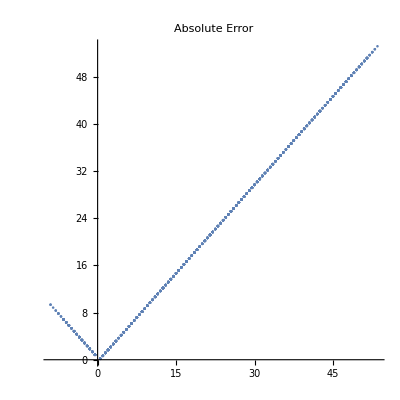

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

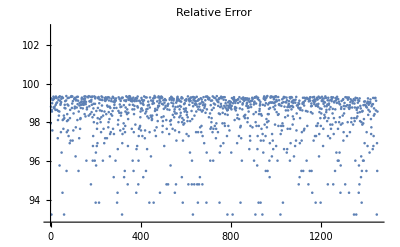

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

99.128

#### tallk5l5m5n5q50u60mfpos0, Net3, 48 coeffs

```mathematica
<<tallk5l5m5n5q50u60mfpos0.mx
```

```mathematica
rawdata =Flatten[tallk5l5m5n5q50u60mfpos0, 4];
Length /@ Keys[rawdata] // Union
```

{14,25,26,27,49,50,51}

```mathematica
data = datadefn[rawdata, 49];
newkeys = Drop[#,1] & /@ Keys[data];
data = Thread[newkeys -> Values[data]];
datasize = Length[data]
```

14590

```mathematica
Length /@ Keys[data] // Union
```

{48}

minlen is a choice made to optimize data points and data quality.

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

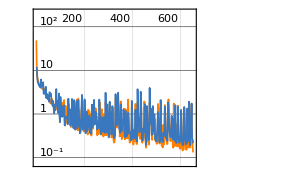
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:111663  rounds:653  time:3.6min  examples/s:32641
data | ,,  training examples:10942  validation examples:2189  processed examples:7146432  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.31×10^-1
validation | ,,  loss:2.3×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

{NetChain[…],{9.86665,17.6274,7.98797,7.64692,15.1241,6.66,5.55402,5.65965,4.58994,5.1546,4.79833,4.49643,4.58261,4.35167,4.99212,4.03064,4.23113,4.07299,3.58034,4.4772,7.64302,4.74232,5.66432,3.77124,3.54193,3.81572,4.66701,3.56109,5.65529,3.46204,7.23359,2.83879,2.97104,3.54381,3.39382,2.54058,3.38097,3.65048,2.92313,2.72466,4.37552,4.01972,2.35828,2.26245,2.62915,3.13588,2.58526,2.33649,2.36792,2.11522,2.05666,2.4987,2.83289,1.73918,2.12656,1.86816,4.44331,3.58264,2.5553,3.44695,1.07592,3.20887,3.27083,2.5329,1.76261,1.78285,2.36149,1.69218,1.06558,2.03695,2.30334,1.50266,1.06841,1.83985,1.06041,0.957281,1.11197,1.61621,1.59575,1.23225,1.21416,1.22047,2.19013,3.40587,4.05022,1.9004,1.77637,1.03929,0.932917,3.09428,1.31108,1.12414,1.25889,0.828579,1.84049,4.05008,0.953847,0.624081,1.20993,0.634751,0.664097,2.92975,1.98122,1.58281,1.03865,0.610321,2.48027,0.945476,0.762107,1.25183,0.721178,2.25231,0.959955,1.24942,0.810525,0.972323,2.07928,1.09836,0.580531,0.522291,0.482843,0.975711,0.957452,0.886012,0.649268,0.91806,0.804046,0.947768,0.66217,1.06583,0.684232,0.541513,0.628133,0.52818,0.604752,5.56394,1.30257,0.730521,0.4596,1.89555,0.715803,1.83525,0.555662,0.524011,0.443051,2.08005,1.29647,0.520006,0.570939,1.19648,3.23388,0.758377,0.402761,0.628189,0.433932,0.442811,0.504046,3.28673,0.896661,3.08983,1.54613,0.579085,0.418971,0.451871,0.387356,0.625473,0.748366,0.609304,2.7174,1.21816,0.599287,0.409319,0.414976,0.639212,0.517734,3.1153,1.05333,0.777452,1.52097,0.667072,0.753634,0.347398,0.376147,0.426168,0.349689,0.477706,0.434565,0.519512,0.809943,1.85235,1.65437,3.82299,0.785214,0.594577,0.505859,0.366206,0.560914,0.415979,0.367269,0.461593,0.652335,3.14352,1.17775,0.52077,0.547026,0.377596,0.349593,0.443593,0.799707,1.26511,1.68476,0.577981,0.509431,0.317127,0.407479,0.492778,0.904955,0.905851,0.507885,1.07253,0.91213,0.578236,1.30908,0.38553,0.347984,0.997074,0.620455,0.424832,0.320727,0.318993,0.37853,2.49194,0.772486,0.472277,0.625373,0.409366,0.769335,0.407976,0.380868,2.33328,2.59669,1.61802,0.626559,0.518543,0.764697,0.645062,0.460318,0.373504,1.87912,0.447109,1.46573,0.920364,0.552253,0.384922,0.493639,0.375759,0.909023,0.450171,0.426406,0.568321,0.350292,0.606788,0.884375,3.39028,1.78152,0.623395,0.62541,0.313358,0.284204,0.401849,0.273087,0.408869,1.39012,1.15485,0.545442,0.644313,0.362814,0.377574,0.399784,0.390905,0.523316,1.57861,0.398767,0.524038,0.371255,0.525959,0.345543,0.389153,3.95096,2.18257,0.60324,0.533221,0.355954,0.401429,0.280003,0.486165,4.20157,0.519573,0.329839,0.353034,1.02185,0.254099,0.328599,0.40757,2.86068,1.05544,2.76547,0.400381,0.351106,0.584773,1.72708,0.451442,0.321036,0.359763,0.245086,0.605388,0.337114,2.69273,1.63892,0.479155,0.399719,0.361455,0.295227,0.277638,0.281162,0.25935,0.403616,0.264369,0.368437,3.64419,2.05909,1.82681,1.09914,2.53082,0.749559,0.934227,0.616511,0.483716,0.831054,2.13524,1.81943,4.3266,1.53704,0.599457,0.754362,0.517176,0.395365,0.518125,0.35661,0.370713,0.36601,2.61145,0.707535,0.459798,0.33986,0.370845,0.562004,0.32827,0.282673,0.872907,0.322271,1.01182,0.419648,2.10558,1.76124,0.38533,0.303501,0.294364,0.287721,0.297971,0.294505,0.278441,2.06079,0.887575,0.618849,0.342163,0.270248,0.305301,0.355924,0.265251,0.269168,1.16435,1.06172,1.06213,0.912694,0.661425,0.280561,0.420657,0.272324,0.4594,0.296806,0.484517,0.335113,0.330316,0.429787,0.27237,0.221378,0.935281,3.05187,0.394536,0.627179,0.292455,0.271294,0.211614,0.323754,0.216102,0.322537,0.75181,0.241739,0.329072,0.234027,0.512879,1.92311,0.577122,0.270805,0.258776,0.258482,0.223133,0.443326,0.234386,0.235063,5.16496,2.23579,0.921572,1.06661,1.16843,0.407127,0.386033,0.373087,0.30772,0.28487,0.569646,0.314208,0.736215,0.268275,6.20453,1.89384,0.475646,0.297718,0.29388,0.285121,0.208036,0.200158,0.343232,0.257727,0.283369,0.646943,0.394963,0.365377,1.36058,1.36176,2.48327,0.91319,0.373268,0.258192,0.272598,0.193467,0.195796,0.309188,0.311674,0.587292,2.45939,0.581438,0.427093,0.365637,0.343239,0.23378,0.337728,0.191013,0.316695,0.204964,6.24671,1.67216,0.893042,0.696989,0.625228,0.575844,2.05314,0.566937,0.3669,0.361379,0.266748,0.294974,0.397166,0.486027,2.56058,0.959223,0.345499,0.484339,0.312464,0.252806,1.5075,1.19439,0.367905,0.36429,0.239162,0.281294,0.306164,0.34928,0.243771,0.223435,0.439907,0.237181,0.293361,0.284145,1.31944,1.8133,0.410242,0.628774,0.2611,0.29788,0.35522,0.234074,0.213931,1.00397,0.32507,2.82792,1.94273,1.50973,0.310164,0.401007,0.224482,0.27078,0.266097,0.221832,0.214499,0.239383,0.349276,0.507527,0.259706,0.23216,0.430847,0.379518,0.252982,0.219776,2.71506,1.02919,0.390119,0.346403,0.241701,0.314006,0.373521,0.212597,0.263952,0.257217,0.251349,0.233223,0.444484,3.24477,2.21252,1.03717,0.74447,0.469492,0.410327,0.427044,0.311425,0.329585,0.32282,0.304563,0.281479,0.400994,0.276642,0.36571,1.44897,0.589397,0.295466,0.310525,0.288457,0.239475,0.191061,0.330068,1.02362,0.537044,0.319135,0.317309,0.225236,0.259922,0.20479,0.196896,4.38401,0.289811,0.222775,0.215167,0.217569,0.340781,0.222199,0.260212,0.281139,0.568692,2.34502,0.612488,0.403703,0.230555,0.264715,0.180654,0.222655,0.219916,0.246204,0.32745,0.251461,0.242429,0.206782,2.6674,0.769343,0.870776,0.228596,0.207675,0.211197,0.202241,0.189634,0.201549,0.185514,0.338665,0.19446,0.206002,2.2716,1.87249,1.04618,0.264777,0.252879,0.305769,0.223028,0.182176,0.282202,0.249142,0.217012,0.209303,2.84162,0.745168,0.410424,0.246171,0.226821,0.299702,0.277365,0.273043,3.55864,1.32714,0.266944,0.211332,0.167739,0.201088,0.217056,0.601228,0.641,0.378775,2.7616,0.703706,0.370725,0.181481,0.316936,0.191294,0.195239,0.230249}}

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

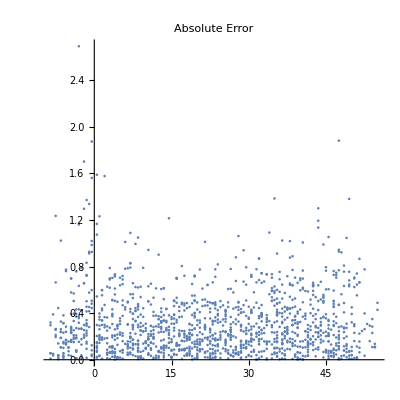

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

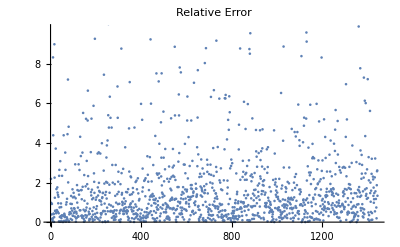

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

5.49423

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## k+l+m+n>0 (k,l,m,n need not be all > 0)

```mathematica
plist=klmnpos[5,400];
```

```mathematica
(*allprodgen[50,70,plist,plist[[141;;150]]]*)
```

#### jacobi-klmn, Net0, 43 coeffs

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
Length /@ Keys[fdata] // Union
```

3229

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

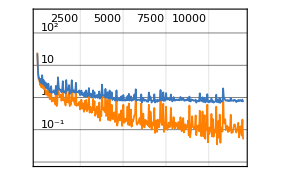
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:18min  examples/s:24379
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.4×10^-2
validation | ,,  loss:7.05×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

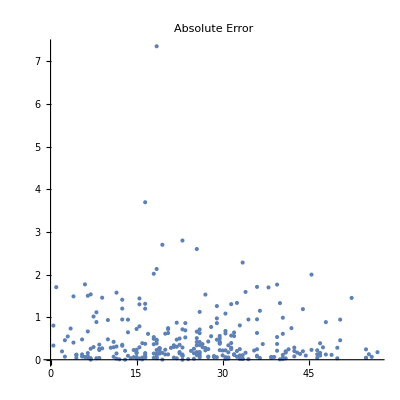

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

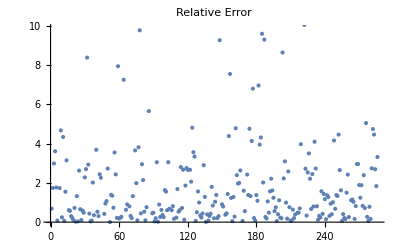

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

4.27794

#### jacobi-klmn, Net3, 43 coeffs(r)

```mathematica
rawdata=Import["jacobi-klmn.txt", Path->NotebookDirectory[]];
fdata = extractMF[rawdata];
Length[fdata]
Length /@ Keys[fdata] // Union
```

3229

{11,14,19,25,26,36,38,39,43,44,45,47,48,49,50,51,52}

```mathematica
data = datadefn[fdata, 43];
datasize = Length[data]
```

2867

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

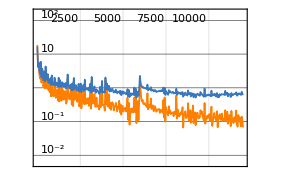
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:408000  rounds:12000  time:32min  examples/s:13805
data | ,,  training examples:2150  validation examples:430  processed examples:26112000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.87×10^-2
validation | ,,  loss:5.57×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

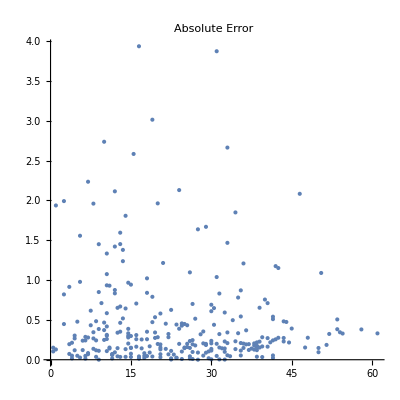

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

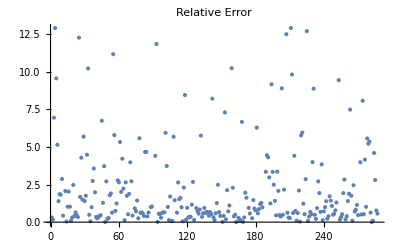

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

4.21632

## Only Negative powers {k,l,m,n} < 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
Clear[cl,cq,dt,en,en1,eq,in,k,o,o1,o2,p1,p2,q,q1,q2,t1,t2,th1,th2,u,wt,zp]
```

```mathematica
(*tallk2l2m2n2q30u50mfneg = ParallelTable[allprodgenneg[1, k, 2, l, 3,m, 4, n,30,50], {k,0,-2, -1}, {l,0,-2, -1},{m,0,-2, -1}, {n,0, -2, -1}];
DumpSave["tallk2l2m2n2q30u50mfneg.mx", tallk2l2m2n2q30u50mfneg];
tallk2l2m2n2q20u30mfneg1 = ParallelTable[allprod1neg[1, k, 2, l, 3,m, 4, n,20,30], {k,-1,-3, -1},{l,-1,-3, -1}, {m,-1,-3, -1}, {n,-1,-3, -1}];
DumpSave["tallk2l2m2n2q20u30mfpos1.mx", tallk2l2m2n2q20u30mfpos1];*)
tallk2l2m2n2q40u50mfneg0 = ParallelTable[Quiet @ allprodθbyΔ[1, k, 2, l, 3,m, 4, n,40,50, 0], {k,0,-2, -1},{l,0,-2, -1}, {m,0,-2, -1}, {n,0,-2, -1}];
DumpSave["tallk2l2m2n2q40u50mfneg0.mx", tallk2l2m2n2q40u50mfneg0];
```

#### tallk2l2m2n2q40u50mfneg0, Net0, 39 coeffs

```mathematica
<<tallk2l2m2n2q40u50mfneg0.mx;
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg0, 4];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,13,20,21,40,41}

```mathematica
data = datadefn[rawdata, 40];
newkeys = Keys[data][[;;,2;;]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

1416

{39}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
traindata[[331]]//N
```

{4.10134×10^-7,-8.20268×10^-7,3.14436×10^-6,-6.15091×10^-6,0.0000261318,0.00690038,2.55039,333.48,28578.7,1.27718×10^6,4.58949×10^7,1.04352×10^9,2.11083×10^10,3.02515×10^11,4.07557×10^12,4.18362×10^13,4.16687×10^14,3.32462×10^15,2.62228×10^16,1.71833×10^17,1.12555×10^18,6.29679×10^18,3.54451×10^19,1.74141×10^20,8.6409×10^20,3.80803×10^21,1.69832×10^22,6.82412×10^22,2.77733×10^23,1.03064×10^24,3.87445×10^24,1.34154×10^25,4.70427×10^25,1.53257×10^26,5.05364×10^26,1.55976×10^27,4.86918×10^27,1.43195×10^28,4.25593×10^28}→29.5

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

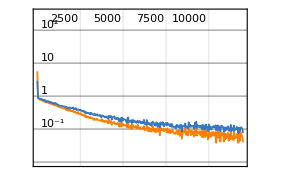
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:21min  examples/s:10224
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.4×10^-2
validation | ,,  loss:9.76×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

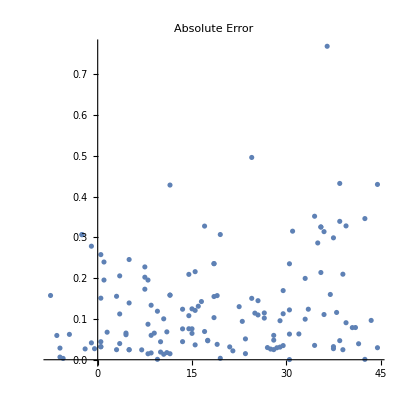

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

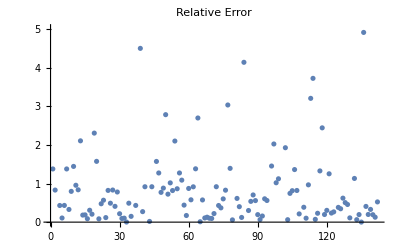

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

2.26061

#### tallk2l2m2n2q40u50mfneg0, Net3, 39 coeffs(r)

```mathematica
<<tallk2l2m2n2q40u50mfneg0.mx;
```

```mathematica
rawdata = Flatten[tallk2l2m2n2q40u50mfneg0, 4];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,13,20,21,40,41}

```mathematica
data = datadefn[rawdata, 40];
newkeys = Keys[data][[;;,2;;]];
data = Thread[newkeys->Values[data]];
datasize = Length[data]
Length /@ Keys[data] // Union
```

1416

{39}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

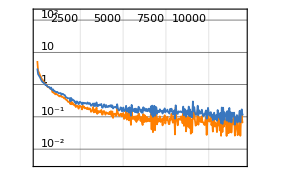
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:204000  rounds:12000  time:15min  examples/s:14259
data | ,,  training examples:1062  validation examples:212  processed examples:13056000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.81×10^-2
validation | ,,  loss:8.38×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

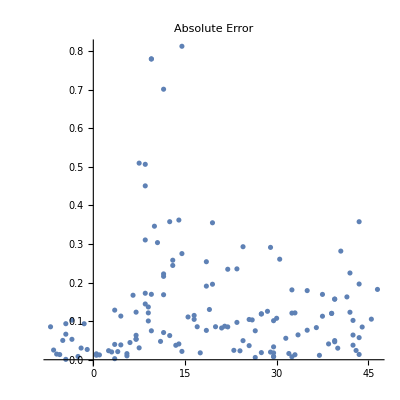

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

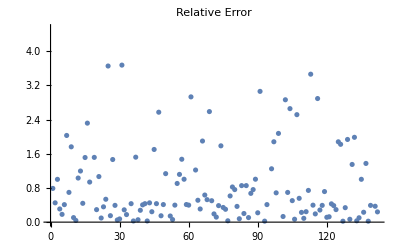

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

1.1453

## k+l+m+n<0 (k,l,m,n need not be all < 0)

```mathematica
(*plist=powersneg[5];*)
plist=klmnneg[5, 400];
```

```mathematica
allprodgenbyΔneg[50,70,plist,plist[[61;;65]],0];
```

```mathematica
rawdata1=Import["jacobibyΔ-klmn-neg.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
Length[data1]
```

922

```mathematica
Values[data1];
```

#### jacobibyΔ-klmn-neg, Net0, 38 coeffs

```mathematica
rawdata1=Import["jacobibyΔ-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobibyΔ-klmn-neg1.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobibyΔ-klmn-neg2.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
Length /@ {data1, data2, data3}
```

{980,96,0}

```mathematica
fdata = Join[data1, data2, data3];
Length[fdata]
Length /@ Keys[fdata] // Union
```

1076

{26,27,38,49,50,51,52,53}

```mathematica
data = datadefn[fdata, 38];
(*newkeys = Keys[data][[All,;;-4]];
data = Thread[newkeys->Values[data]];*)
datasize = Length[data]
Length /@ Keys[data] // Union
```

978

{38}

```mathematica
(*( NumericQ/@(traindata[[2625,1]]//N)//Union)==={True}*)
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

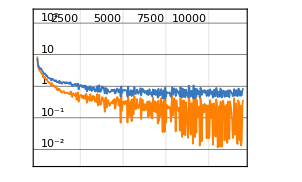
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:144000  rounds:12000  time:4.3min  examples/s:35752
data | ,,  training examples:733  validation examples:147  processed examples:9216000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.63×10^-2
validation | ,,  loss:5.28×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

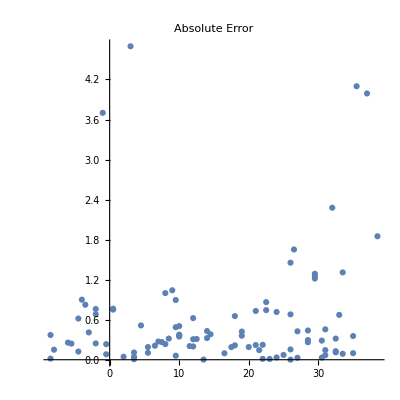

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

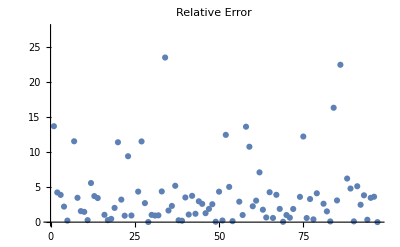

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

13.3438

#### jacobibyΔ-klmn-neg, Net3, 38 coeffs

```mathematica
rawdata1=Import["jacobibyΔ-klmn-neg.txt", Path->NotebookDirectory[]];
rawdata2=Import["jacobibyΔ-klmn-neg1.txt", Path->NotebookDirectory[]];
rawdata3=Import["jacobibyΔ-klmn-neg2.txt", Path->NotebookDirectory[]];
```

```mathematica
data1 = extractMF[rawdata1];
data2 = extractMF[rawdata2];
data3 = extractMF[rawdata3];
Length /@ {data1, data2, data3}
```

{980,96,0}

```mathematica
fdata = Join[data1, data2, data3];
Length[fdata]
Length /@ Keys[fdata] // Union
```

1076

{26,27,38,49,50,51,52,53}

```mathematica
data = datadefn[fdata, 38];
(*newkeys = Keys[data][[All,;;-4]];
data = Thread[newkeys->Values[data]];*)
datasize = Length[data]
Length /@ Keys[data] // Union
```

978

{38}

```mathematica
(*( NumericQ/@(traindata[[2625,1]]//N)//Union)==={True}*)
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

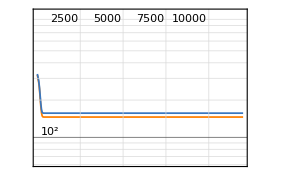
NetTrainResultsObject[NetTrain Results
summary | ,,  batches:144000  rounds:12000  time:4.6min  examples/s:33129
data | ,,  training examples:733  validation examples:147  processed examples:9216000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.46×10^2
validation | ,,  loss:1.57×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

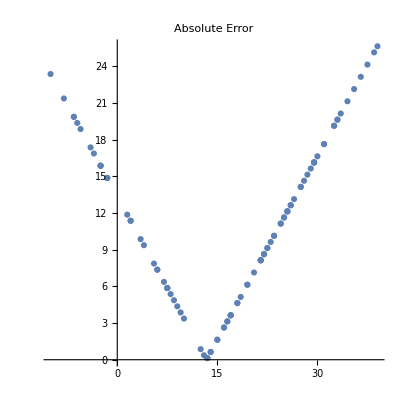

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

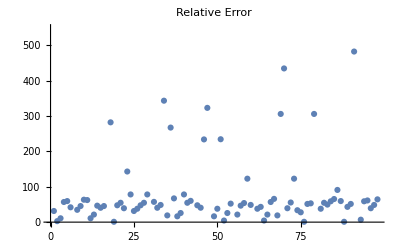

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

```mathematica
Mean[relErrors]
```

138.903

## 2 η^3 = θ_2θ_3θ_4

## Setting k = 0

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

```mathematica
k1 = ParallelTable[allprod1pos[1, 0, 2, l, 3,m, 4, n,70,80], {l, 3},{m,3}, {n, 3}];
```

```mathematica
<<tallk5l5m5n5q70u80mfpos1.mx; <<t2n50q30u70mfpos1.mx;
```

```mathematica
e1 = Flatten[tallk0l5m5n5q70u80mfpos1, 4];
(*e2 = Flatten[t2n70q60u100mfpos1, 1];
e3 = Flatten[t3n70q60u100mfpos1, 1];
e4 = Flatten[t4n70q60u100mfpos1, 1];*)
```

```mathematica
e1[[;;2]]
```

{{-1,27,-125,343,-729,1331,-2197,3375}→7/2,{1/12,-209/4,-96,5429/12,96,768,-32935/12,864,-1920,-1056,30819/4,288,-2400,6720,4416,-346523/12,9504,-384,-5760,-7200,-5376,548701/12,12000,-20160,-3936,19872,30432,-9408,-471109/4,31008,3168,10272,-25728,1920,-36288}→11/2}

```mathematica
Length /@ Keys[e1] // Union
```

{8,14,26,31,34,35,36,48,52,53,59,60,61,62,69,70}

```mathematica
fdata1 = e1;
```

```mathematica
Values[fdata1];
```

```mathematica
Length /@ Keys[fdata1] // Union
```

{8,14,26,31,34,35,36,48,52,53,59,60,61,62,69,70}

```mathematica
nk1 = If[Length[#]>= 59, #, ##&[] ] & /@ Keys[fdata1];
Length /@  nk1 // Union
(*nk2 = If[Length[#]>= 26, #, ##&[] ] & /@ Keys[fdata2];
Length /@  nk2 // Union*)
```

{59,60,61,62,69,70}

```mathematica
newkeys1 =nk1[[All,;;Min[Length /@ nk1]]];
newvalues1 = If[Length[Keys[#]]>= Min[Length /@ nk1], Values[#], ##&[] ] & /@ fdata1;
(*newkeys2 =nk2[[All,;;Min[Length /@ nk2]]];
newvalues2 = If[Length[Keys[#]]>= 26, Values[#], ##&[] ] & /@ fdata2;*)
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

3988

{59}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
Dimensions[data]
datasize = Length[data]
```

{3988}

3988

```mathematica
Length @ Keys[data[[1]]]
data[[1]]
```

59

{1/12,-41/6,-209/4,441/2,-223/6,192,-2545/12,-8509/6,-96,-2665/6,23317/6,377/2,-30631/12,42431/6,2400,-49277/6,-12449,3648,-6417/2,576,14691/4,2999/3,62965/6,-2304,50499/2,41239/6,8832,-7047/2,-195623/6,-104475/2,-164507/12,40793,14496,-14400,-492091/6,-14208,255173/3,324863/6,-43505/2,724307/6,-21888,-4416,971399/12,-584357/6,10272,-231579/2,-125743/3,54144,-240007/6,100951/6,-19488,-605789/3,7200,-93504,13824,210905,335297/4,475533/2,1522205/6}→6

```mathematica
trainpos=RandomSample[Range[datasize],Floor[3/4 datasize]];
valpos=RandomSample[Complement[Range[datasize],trainpos],Floor[90/100 datasize]-Floor[3/4 datasize]];
testpos=Complement[Range[datasize],trainpos,valpos];
```

```mathematica
traindata=data[[trainpos]];
valdata=data[[valpos]];
testdata=data[[testpos]];
```

```mathematica
Length[traindata]
Length[valdata]
Length[testdata]
```

2991

598

399

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 8000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 48 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:210251  rounds:4473  time:5.9min  examples/s:38282
data | ,,  training examples:2997  validation examples:599  processed examples:13456064  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.31×10^-1
validation | ,,  loss:1.52×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 59 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:376000  rounds:8000  time:13min  examples/s:31393
data | ,,  training examples:2991  validation examples:598  processed examples:24064000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.26×10^-3
validation | ,,  loss:1.03×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
testexact = testdata[[;;,2]];
```

```mathematica
testpred = tNet/@testdata[[;;,1]];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.161518

Loss is higher compared to when you divide the MFs by Δ. But still it learns okay.

## u = 0

```mathematica
eta1pos[m_,  n_, nq_]:=Module[ {q, u,th1,th2,q1, q2,  eq, cq, in, wt, o1, o2, o, dt},
th1  = Series[ EllipticTheta[2,0,q]^m EllipticTheta[3,0,q]^n EllipticTheta[4,0,q]^n,{q,0,nq}];
th2  = th1/q^(m/4);
cq = DeleteCases[CoefficientList[th2, q],0];
wt = m/2+2 n/2;
dt = cq -> wt;
Return[dt]]
```

```mathematica
th1  = Series[ EllipticTheta[2,0,q]^5 EllipticTheta[3,0,q]^5 EllipticTheta[4,0,q]^5,{q,0,10}]
```

32 q^(5/4)-480 q^(13/4)+2880 q^(21/4)-7840 q^(29/4)+3360 q^(37/4)+O[q]^(41/4)

```mathematica
eta1pos[5, 5, 10]
```

{{32,-480,2880,-7840,3360}→15/2}

```mathematica
etan500q200 = ParallelTable[eta1pos[n, n, 200],{n, 0, 500, 1/8}];
DumpSave["etan500q200.mx", etan500q200];
```

```mathematica
<<etan300q100.mx
```

```mathematica
etan100q50
```

```mathematica
e1 = Flatten[etan500q200, 3];
```

```mathematica
Values[fdata1];
```

```mathematica
Length /@ Keys[fdata1] // Union
```

{0,14,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199}

```mathematica
nk1 = If[Length[#]>= 70, #, ##&[] ] & /@ Keys[fdata1];
Length /@  nk1 // Union
```

{70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199}

```mathematica
newkeys1 =Simplify @ nk1[[All,;;Min[Length /@ nk1]]];
newvalues1 = If[Length[Keys[#]]>= Min[Length /@ nk1], Values[#], ##&[] ] & /@ fdata1;
```

```mathematica
Length[newkeys1]
Length /@ newkeys1 // Union
Length[newkeys1] == Length[newvalues1]
```

2262

{70}

True

```mathematica
data = Thread[newkeys1 ->newvalues1];
Dimensions[data]
datasize = Length[data]
```

{2262}

2262

```mathematica
Length/@ Keys[data] // Union
```

{70}

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 20000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 20 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.1min  examples/s:23336
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.09×10^-2
validation | ,,  loss:4.24×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 20 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:2.2min  examples/s:11670
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.49×10^-2
validation | ,,  loss:1.52×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 50 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.7min  examples/s:15094
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.79×10^-1
validation | ,,  loss:4.22×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 50 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:24000  rounds:8000  time:1.6min  examples/s:16311
data | ,,  training examples:160  validation examples:32  processed examples:1536000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.11×10^-1
validation | ,,  loss:1.91×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.4min  examples/s:35160
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.7×10^-2
validation | ,,  loss:1.71×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:3.1min  examples/s:27529
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.71×10^-1
validation | ,,  loss:6.6×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.9min  examples/s:29141
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.96×10^-2
validation | ,,  loss:3.07×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU", LearningRate->0.0001] (* 30 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:80000  rounds:10000  time:2.5min  examples/s:34530
data | ,,  training examples:503  validation examples:100  processed examples:5120000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.18×10^-2
validation | ,,  loss:4.37×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU", LearningRate->0.0001] (* etan500q200 70 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:540000  rounds:20000  time:17min  examples/s:33878
data | ,,  training examples:1696  validation examples:339  processed examples:34560000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.62×10^-2
validation | ,,  loss:5.35×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

## Individual θ_i without dividing by Δ

## Positive powers of θ_i (only contains positive weight modular forms)

### θ_1

```mathematica
t1k40q50u60mfpos=ParallelTable[Quiet @ theta1[k,50,60],{k,40}];
DumpSave["t1k40q50u60mfpos.mx", t1k40q50u60mfpos];
t1k50q70u80mfpos=ParallelTable[theta1[k,70,80],{k,50}];
DumpSave["t1k50q70u80mfpos.mx", t1k50q70u80mfpos];
(*t1k80q120u150mfpos=ParallelTable[theta1[k,120,150],{k,80}];
DumpSave["t1k80q120u150mfpos.mx", t1k80q120u150mfpos];*)
```

#### t1k40q50u60mfpos, Net0, 19 coeffs

```mathematica
<<t1k40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

790

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:4.8min  examples/s:26666
data | ,,  training examples:592  validation examples:119  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.1×10^-1
validation | ,,  loss:1.39×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.366402

#### t1k40q50u60mfpos, Net3, 19 coeffs

```mathematica
<<t1k40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

790

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:6.2min  examples/s:20733
data | ,,  training examples:592  validation examples:119  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.08×10^-1
validation | ,,  loss:8.63×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.318925

#### t1k50q70u80mfpos, Net0, 26 coeffs(r)

```mathematica
<<t1k50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t1k50q70u80mfpos,1];
Length /@ Keys[rawdata] // Union
```

{8,26,29,30,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1360

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
t1k50q70u80mfposcsv = Flatten[#, 1] & /@ Transpose[{enc[Keys[data]],N[Values[data]]}];
Export["CSV/t1k50q70u80mfpos.csv", t1k50q70u80mfposcsv];
```

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:7.9min  examples/s:25969
data | ,,  training examples:1020  validation examples:204  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.6×10^-2
validation | ,,  loss:4.83×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.257198

#### t1k50q70u80mfpos, Net3, 26 coeffs

```mathematica
<<t1k50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t1k50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,26,29,30,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1360

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:12min  examples/s:17659
data | ,,  training examples:1020  validation examples:204  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.47×10^-2
validation | ,,  loss:5.5×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.342947

### θ_2

```mathematica
t2l40q50u60mfpos=ParallelTable[Quiet @ theta2[l,50,60],{l,40}];
DumpSave["t2l40q50u60mfpos.mx", t2l40q50u60mfpos];
t2l50q70u80mfpos=ParallelTable[theta2[l,70,80],{l,50}];
DumpSave["t2l50q70u80mfpos.mx", t2l50q70u80mfpos];
(*t2l80q120u150mfpos=ParallelTable[theta2[l,120,150],{l,80}];
DumpSave["t2l80q120u150mfpos.mx", t2l80q120u150mfpos];*)
```

#### t2l40q50u60mfpos, Net0, 19 coeffs

```mathematica
<<t2l40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

1209

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:7.1min  examples/s:26917
data | ,,  training examples:906  validation examples:182  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.23×10^-2
validation | ,,  loss:1.1×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.775116

#### t2l40q50u60mfpos, Net0, 19 coeffs

```mathematica
<<t2l40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25}

```mathematica
data = datadefn[rawdata, 19];
```

```mathematica
datasize = Length[data]
```

1209

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:7.3min  examples/s:26274
data | ,,  training examples:906  validation examples:182  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.27×10^-3
validation | ,,  loss:1.22×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.738755

#### t2l50q70u80mfpos, Net0, 26 coeffs(r)

```mathematica
<<t2l50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t2l50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,26,29,30,31,32,33,34,35}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

2009

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:288000  rounds:12000  time:20min  examples/s:15231
data | ,,  training examples:1506  validation examples:302  processed examples:18432000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.78×10^-1
validation | ,,  loss:1.09×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.238111

### θ_3

```mathematica
t3m40q50u60mfpos=ParallelTable[Quiet @ theta3[m,50,60],{m,40}];
DumpSave["t3m40q50u60mfpos.mx", t3m40q50u60mfpos];
t3m50q70u80mfpos=ParallelTable[theta3[m,70,80],{m,50}];
DumpSave["t3m50q70u80mfpos.mx", t3m50q70u80mfpos];
(*t3m80q120u150mfpos=ParallelTable[theta3[m,120,150],{m,80}];
DumpSave["t3m80q120u150mfpos.mx", t3m80q120u150mfpos];*)
```

#### t3m40q50u60mfpos, Net0, 24 coeffs

```mathematica
<<t3m40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:6.8min  examples/s:26546
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.24×10^2
validation | ,,  loss:3.42×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

68.4218

#### t3m40q50u60mfpos, Net3, 24 coeffs(r)

```mathematica
<<t3m40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
```

```mathematica
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:10.0min  examples/s:18003
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:9.53×10^-4
validation | ,,  loss:5.85×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.130769

#### t3m50q70u80mfpos, Net0, 31 coeffs

```mathematica
<<t3m50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t3m50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:11min  examples/s:26632
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.08×10^-2
validation | ,,  loss:7.65×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.04524

#### t3m50q70u80mfpos, Net3, 31 coeffs

```mathematica
<<t3m50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t3m50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:16min  examples/s:17959
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.38×10^-3
validation | ,,  loss:8.18×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0620383

### θ_4

```mathematica
t4n40q50u60mfpos=ParallelTable[Quiet @ theta4[n,50,60],{n,40}];
DumpSave["t4n40q50u60mfpos.mx", t4n40q50u60mfpos];
t4n50q70u80mfpos=ParallelTable[theta4[n,70,80],{n,50}];
DumpSave["t4n50q70u80mfpos.mx", t4n50q70u80mfpos];*)
(*t4n80q120u150mfpos=ParallelTable[theta4[n,120,150],{n,80}];
DumpSave["t4n80q120u150mfpos.mx", t4n80q120u150mfpos];*)
```

#### t4n40q50u60mfpos, Net0, 24 coeffs

```mathematica
<<t4n40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
```

```mathematica
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:6.7min  examples/s:26664
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.33×10^2
validation | ,,  loss:3.52×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

49.7019

#### t4n40q50u60mfpos, Net3, 24 coeffs(r)

```mathematica
<<t4n40q50u60mfpos.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
```

```mathematica
datasize = Length[data]
```

1170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:168000  rounds:12000  time:10.0min  examples/s:17967
data | ,,  training examples:877  validation examples:176  processed examples:10752000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.47×10^-4
validation | ,,  loss:7.55×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.103263

#### t4n50q70u80mfpos, Net0, 31 coeffs

```mathematica
<<t4n50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t4n50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:11min  examples/s:26354
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.71×10^-4
validation | ,,  loss:1.49×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0563935

#### t4n50q70u80mfpos, Net3, 31 coeffs

```mathematica
<<t4n50q70u80mfpos.mx
```

```mathematica
rawdata=Flatten[t4n50q70u80mfpos,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,31,60,70}

```mathematica
data = datadefn[rawdata, 31];
```

```mathematica
datasize = Length[data]
```

1960

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:276000  rounds:12000  time:14min  examples/s:21750
data | ,,  training examples:1470  validation examples:294  processed examples:17664000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.5×10^-3
validation | ,,  loss:1.59×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0445423

## Negative powers of θ_i

### θ_1

```mathematica
(*t1k40q50u60mfneg=ParallelTable[Quiet @ theta1[k,50,60],{k,-1, -40, -1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
t1k50q70u80mfneg=ParallelTable[Quiet @ theta1[k,70,80],{k,-1, -50, -1}];
DumpSave["t1k50q70u80mfneg.mx", t1k50q70u80mfneg];
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t1k40q50u60mfneg, Net0, 26 coeffs(r)

```mathematica
<<t1k40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1640

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:240000  rounds:12000  time:7.0min  examples/s:36431
data | ,,  training examples:1230  validation examples:246  processed examples:15360000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:9.35×10^-3
validation | ,,  loss:8.05×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.54308

#### t1k40q50u60mfneg, Net3, 26 coeffs

```mathematica
<<t1k40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1640

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:240000  rounds:12000  time:9.6min  examples/s:26698
data | ,,  training examples:1230  validation examples:246  processed examples:15360000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.83×10^-2
validation | ,,  loss:5.85×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.33966

### θ_2

```mathematica
(*t2l40q50u60mfneg=ParallelTable[Quiet @ theta2[l,50,60],{l,-1, -40, -1}];
DumpSave["t2l40q50u60mfneg.mx", t2l40q50u60mfneg];*)
t2l50q70u80mfneg=ParallelTable[Quiet @ theta2[l,70,80],{l,-1, -50, -1}];
DumpSave["t2l50q70u80mfneg.mx", t2l50q70u80mfneg];
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t2l40q50u60mfneg, Net0, 26 coeffs

```mathematica
<<t2l40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:5.4min  examples/s:35775
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.19×10^-1
validation | ,,  loss:1.04
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.93778

#### t2l40q50u60mfneg, Net3, 26 coeffs(r)

```mathematica
<<t2l40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 26];
```

```mathematica
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:6.9min  examples/s:28011
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.59×10^-1
validation | ,,  loss:8.74×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

2.4772

### θ_3

```mathematica
t3m40q50u60mfneg=ParallelTable[Quiet @ theta3[m,50,60],{m,-1, -40, -1}];
DumpSave["t3m40q50u60mfneg.mx", t3m40q50u60mfneg];
(*t1k30q30u60mfneg=ParallelTable[theta1[k,30,60],{k,-1,-30,-1}];
DumpSave["t1k30q30u60mfneg.mx", t1k30q30u60mfneg];*)
(*t1k40q50u60mfneg=ParallelTable[theta1[k,50,60],{k,-1,-40,-1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
(*t1k50q60u80mfneg=ParallelTable[theta1[k,60,80],{k,-1,-50,-1}];
DumpSave["t1k50q60u80mfneg.mx", t1k50q60u80mfneg];*)
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t3m40q50u60mfneg, Net0, 50 coeffs(r)

```mathematica
<<t3m40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
```

```mathematica
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:16978
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.68×10^-2
validation | ,,  loss:3.91×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.542126

#### t3m40q50u60mfneg, Net3, 50 coeffs

```mathematica
<<t3m40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:12min  examples/s:16118
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.44×10^2
validation | ,,  loss:3.29×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

286.609

### θ_4

```mathematica
t4n40q50u60mfneg=ParallelTable[Quiet @ theta4[n,50,60],{n,-1, -40, -1}];
DumpSave["t4n40q50u60mfneg.mx", t4n40q50u60mfneg];
(*t1k30q30u60mfneg=ParallelTable[theta1[k,30,60],{k,-1,-30,-1}];
DumpSave["t1k30q30u60mfneg.mx", t1k30q30u60mfneg];*)
(*t1k40q50u60mfneg=ParallelTable[theta1[k,50,60],{k,-1,-40,-1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
(*t1k50q60u80mfneg=ParallelTable[theta1[k,60,80],{k,-1,-50,-1}];
DumpSave["t1k50q60u80mfneg.mx", t1k50q60u80mfneg];*)
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### t4n40q50u60mfneg, Net0, 50 coeffs(r)

```mathematica
<<t4n40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
```

```mathematica
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"]
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:9.4min  examples/s:20422
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.47×10^-2
validation | ,,  loss:3.46×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.798023

#### t4n40q50u60mfneg, Net3, 50 coeffs

```mathematica
<<t4n40q50u60mfneg.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfneg,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50}

```mathematica
data = datadefn[rawdata, 50];
```

```mathematica
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] (* 19 coeffs*)
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:8.7min  examples/s:21950
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.23×10^2
validation | ,,  loss:3.67×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

205.459

## Positive and negative powers together

```mathematica
range30=DeleteCases[Range[-30,30],0];
range40=DeleteCases[Range[-40,40],0];
range50=DeleteCases[Range[-50,50],0];
```

### θ_1

```mathematica
t1k40q50u60mfAll=ParallelTable[Quiet @ theta1[k,50,60],{k,range40}];
DumpSave["t1k40q50u60mfAll.mx", t1k40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t1k40q50u60mfAll, Net0, 25 coeffs(r)

```mathematica
<<t1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1808

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:264000  rounds:12000  time:11min  examples/s:25944
data | ,,  training examples:1356  validation examples:271  processed examples:16896000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:9.71×10^-3
validation | ,,  loss:5.49×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

6.12769

#### t1k40q50u60mfAll, Net3, 25 coeffs

```mathematica
<<t1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1808

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:264000  rounds:12000  time:16min  examples/s:17936
data | ,,  training examples:1356  validation examples:271  processed examples:16896000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.47×10^-2
validation | ,,  loss:5.19×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-

```mathematica
Mean[relErrors]
```

∞

### θ_2

```mathematica
t2l40q50u60mfAll=ParallelTable[Quiet @ theta2[l,50,60],{l,range40}];
DumpSave["t2l40q50u60mfAll.mx", t2l40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t2l40q50u60mfAll, Net0, 22 coeffs(r)

```mathematica
<<t2l40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

2170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:312000  rounds:12000  time:13min  examples/s:26568
data | ,,  training examples:1627  validation examples:326  processed examples:19968000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.91×10^-2
validation | ,,  loss:6.74×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

2.16186

#### t2l40q50u60mfAll, Net3, 22 coeffs

```mathematica
<<t2l40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t2l40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,19,21,22,23,24,25,26,27,28,29,30,31}

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

2170

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:312000  rounds:12000  time:19min  examples/s:17974
data | ,,  training examples:1627  validation examples:326  processed examples:19968000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.94×10^-1
validation | ,,  loss:3.45×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-

```mathematica
Mean[relErrors]
```

∞

```mathematica
rawdata=Flatten[t1k30q50u60mfAll,1];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[t1k30q50u60mfAll,1].

```mathematica
Length /@ Keys[rawdata] // Union
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::invrl: The argument 2 is not a valid Association or a list of rules.

Keys[2]

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::argt: Keys called with 0 arguments; 1 or 2 arguments are expected.

Keys::invrl: The argument t1k30q50u60mfAll is not a valid Association or a list of rules.

Keys::invrl: The argument 1 is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

2

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Rule::argrx: Rule called with 0 arguments; 2 arguments are expected.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

Keys::invrl: The argument Keys[] is not a valid Association or a list of rules.

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
rawdata=Flatten[t1k30q50u60mfAll,1];
```

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[t1k30q50u60mfAll,1].

```mathematica
Length /@ Keys[rawdata] // Union
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::invrl: The argument 2 is not a valid Association or a list of rules.

Keys[2]

```mathematica
data = datadefn[rawdata, 22];
datasize = Length[data]
```

Keys::invrl: The argument Flatten[t1k30q50u60mfAll,1] is not a valid Association or a list of rules.

Keys::argt: Keys called with 0 arguments; 1 or 2 arguments are expected.

Keys::invrl: The argument t1k30q50u60mfAll is not a valid Association or a list of rules.

Keys::invrl: The argument 1 is not a valid Association or a list of rules.

General::stop: Further output of Keys::invrl will be suppressed during this calculation.

Flatten::argb: Flatten called with 0 arguments; between 1 and 3 arguments are expected.

2

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

Rule::argrx: Rule called with 0 arguments; 2 arguments are expected.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

Keys::invrl: The argument Keys[] is not a valid Association or a list of rules.

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

### θ_3

```mathematica
t3m40q50u60mfAll=ParallelTable[Quiet @ theta3[m,50,60],{m,range40}];
DumpSave["t3m40q50u60mfAll.mx", t3m40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t3m40q50u60mfAll, Net0, 24 coeffs

```mathematica
<<t3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

2370

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:13min  examples/s:26677
data | ,,  training examples:1777  validation examples:356  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.43×10^2
validation | ,,  loss:4.59×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

Power::infy: Infinite expression 1/0 encountered.

-Graphics-

```mathematica
Mean[relErrors]
```

∞

#### t3m40q50u60mfAll, Net3, 24 coeffs(r)

```mathematica
<<t3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

2370

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:20min  examples/s:18175
data | ,,  training examples:1777  validation examples:356  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.42×10^-2
validation | ,,  loss:7.48×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.306258

### θ_4

```mathematica
t4n40q50u60mfAll=ParallelTable[Quiet @ theta4[n,50,60],{n,range40}];
DumpSave["t4n40q50u60mfAll.mx", t4n40q50u60mfAll];
(*t1k50q70u80mfAll=ParallelTable[theta1[k,70,80],{k,range50}];
DumpSave["t1k50q70u80mfAll.mx", t1k50q70u80mfAll];*)
```

#### t4n40q50u60mfAll, Net0, 24 coeffs

```mathematica
<<t4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 24];
datasize = Length[data]
```

2370

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:18min  examples/s:19736
data | ,,  training examples:1777  validation examples:356  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.41×10^2
validation | ,,  loss:4.36×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

213.744

#### t4n40q50u60mfAll, Net3, 24 coeffs(r)

```mathematica
<<t4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[t4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{7,24,43,50}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2340

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:23min  examples/s:15332
data | ,,  training examples:1755  validation examples:351  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.99×10^-3
validation | ,,  loss:1.83×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.38193

## Individual θ_iwith division by Δ

## Positive powers of θ_i (only contains positive weight modular forms)

### θ_1

```mathematica
tΔ1k40q50u60mfpos0=ParallelTable[theta1byΔ[k,50,60, 0],{k,40}];
DumpSave["tΔ1k40q50u60mfpos0.mx", tΔ1k40q50u60mfpos0];
tΔ1k50q70u80mfpos0=ParallelTable[theta1byΔ[k,70,80, 0],{k,50}];
DumpSave["tΔ1k50q70u80mfpos0.mx", tΔ1k50q70u80mfpos0];
(*tΔ1k70q90u100mfpos0=ParallelTable[theta1byΔ[k,90,100, 0],{k,70}];
DumpSave["tΔ1k70q90u100mfpos0.mx", tΔ1k70q90u100mfpos0];*)
```

#### tΔ1k40q50u60mfpos0, Net0, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

780

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:8.6min  examples/s:14851
data | ,,  training examples:585  validation examples:117  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.62×10^-2
validation | ,,  loss:3.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.687776

#### tΔ1k40q50u60mfpos0, Net3, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

780

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:120000  rounds:12000  time:13min  examples/s:9952
data | ,,  training examples:585  validation examples:117  processed examples:7680000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.09×10^-3
validation | ,,  loss:3.81×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.585603

#### tΔ1k50q70u80mfpos0, Net0, 35 coeffs

```mathematica
<<tΔ1k50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,7,8,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

1350

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:18min  examples/s:11525
data | ,,  training examples:1012  validation examples:203  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:6.28×10^-3
validation | ,,  loss:4.67×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.468479

#### tΔ1k50q70u80mfpos0, Net3, 35 coeffs(r)

```mathematica
<<tΔ1k50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ1k50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,7,8,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

1350

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:192000  rounds:12000  time:21min  examples/s:9808
data | ,,  training examples:1012  validation examples:203  processed examples:12288000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.63×10^-2
validation | ,,  loss:3.54×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.379703

### θ_2

```mathematica
tΔ2l40q50u60mfpos0=ParallelTable[theta2byΔ[l,50,60, 0],{l,40}];
DumpSave["tΔ2l40q50u60mfpos0.mx", tΔ2l40q50u60mfpos0];
tΔ2l50q70u80mfpos0=ParallelTable[theta2byΔ[l,70,80, 0],{l,50}];
DumpSave["tΔ2l50q70u80mfpos0.mx", tΔ2l50q70u80mfpos0];
(*tΔ2l70q90u100mfpos0=ParallelTable[theta2byΔ[l,90,100, 0],{l,70}];
DumpSave["tΔ2l70q90u100mfpos0.mx", tΔ2l70q90u100mfpos0];*)
```

#### tΔ2l40q50u60mfpos0, Net0, 26 coeffs

```mathematica
<<tΔ2l40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:11951
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.55×10^2
validation | ,,  loss:4.83×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

125.108

#### tΔ2l40q50u60mfpos0, Net3, 26 coeffs

```mathematica
<<tΔ2l40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:19min  examples/s:10148
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.87×10^-2
validation | ,,  loss:5.18×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.980556

#### tΔ2l50q70u80mfpos0, Net0, 36 coeffs

```mathematica
<<tΔ2l50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{36}

```mathematica
data = datadefn[rawdata, 36];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:27min  examples/s:11980
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.57×10^-1
validation | ,,  loss:3.69×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.53233

#### tΔ2l50q70u80mfpos0, Net3, 36 coeffs(r)

```mathematica
<<tΔ2l50q70u80mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:31min  examples/s:10308
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.18×10^-2
validation | ,,  loss:6.39×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.886984

### θ_3

```mathematica
tΔ3m40q50u60mfpos0=ParallelTable[Quiet @ theta3byΔ[m,50,60, 0],{m,40}]; 
DumpSave["tΔ3m40q50u60mfpos0.mx", tΔ3m40q50u60mfpos0];
(*tΔ3m50q70u80mfpos0=ParallelTable[Quiet @ theta3byΔ[m,70,80, 0],{m,50}];
DumpSave["tΔ3m50q70u80mfpos0.mx", tΔ3m50q70u80mfpos0];*)
(*tΔ3m70q90u100mfpos0=ParallelTable[Quiet @ theta3byΔ[m,90,100, 0],{k,70}];
DumpSave["tΔ3m70q90u100mfpos0.mx", tΔ3m70q90u100mfpos0];*)
```

#### tΔ3m40q50u60mfpos0, Net0, 50 coeffs(r)

```mathematica
<<tΔ3m40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:10min  examples/s:18286
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.93×10^-3
validation | ,,  loss:5.79×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.286784

#### tΔ3m40q50u60mfpos0, Net3, 50 coeffs

```mathematica
<<tΔ3m40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:12min  examples/s:16272
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.2×10^-2
validation | ,,  loss:4.8×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.555659

### θ_4

```mathematica
tΔ4n40q50u60mfpos0=ParallelTable[Quiet @ theta4byΔ[n,50,60, 0],{n,40}];
DumpSave["tΔ4n40q50u60mfpos0.mx", tΔ4n40q50u60mfpos0];
(*tΔ4n50q70u80mfpos0=ParallelTable[Quiet @ theta4byΔ[n,70,80, 0],{n,50}];
DumpSave["tΔ4n50q70u80mfpos0.mx", tΔ4n50q70u80mfpos0];*)
(*tΔ4n70q90u100mfpos0=ParallelTable[Quiet @ theta4byΔ[n,90,100, 0],{k,70}];
DumpSave["tΔ4n70q90u100mfpos0.mx", tΔ4n70q90u100mfpos0];*)
```

#### tΔ4n40q50u60mfpos0, Net0, 50 coeffs(r)

```mathematica
<<tΔ4n40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:17856
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.41×10^-3
validation | ,,  loss:3.16×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.485268

#### tΔ4n40q50u60mfpos0, Net3, 50 coeffs

```mathematica
<<tΔ4n40q50u60mfpos0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfpos0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:17004
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.07×10^-2
validation | ,,  loss:1.1×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.602727

## Negative powers of θ_i

### θ_1

```mathematica
tΔ1k40q50u60mfneg0=ParallelTable[theta1byΔ[k,50,60, 0],{k,-1, -40, -1}];
DumpSave["tΔ1k40q50u60mfneg0.mx", tΔ1k40q50u60mfneg0];
(*tΔ1k50q70u80mfneg0=ParallelTable[theta1byΔ[k,70,80, 0],{k,-1, -50, -1}];
DumpSave["tΔ1k50q70u80mfneg0.mx", tΔ1k50q70u80mfneg0];*)
(*tΔ1k70q90u100mfneg0=ParallelTable[theta1byΔ[k,90,100, 0],{k,-1, -70, -1}];
DumpSave["tΔ1k70q90u100mfneg0.mx", tΔ1k70q90u100mfneg0];*)
```

```mathematica
(*t1k30q30u60mfneg=ParallelTable[theta1[k,30,60],{k,-1,-30,-1}];
DumpSave["t1k30q30u60mfneg.mx", t1k30q30u60mfneg];*)
(*t1k40q50u60mfneg=ParallelTable[theta1[k,50,60],{k,-1,-40,-1}];
DumpSave["t1k40q50u60mfneg.mx", t1k40q50u60mfneg];*)
(*t1k50q60u80mfneg=ParallelTable[theta1[k,60,80],{k,-1,-50,-1}];
DumpSave["t1k50q60u80mfneg.mx", t1k50q60u80mfneg];*)
(*t1k80q120u150mfneg=ParallelTable[theta1[k,120,150],{k,-1, -80, -1}];
DumpSave["t1k80q120u150mfneg.mx", t1k80q120u150mfneg];*)
```

#### tΔ1k40q50u60mfneg0, Net0, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1600

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:228000  rounds:12000  time:6.5min  examples/s:37186
data | ,,  training examples:1200  validation examples:240  processed examples:14592000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.83×10^-2
validation | ,,  loss:1.71×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.180927

#### tΔ1k40q50u60mfneg0, Net3, 25 coeffs(r)

```mathematica
<<tΔ1k40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1600

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:228000  rounds:12000  time:11min  examples/s:21418
data | ,,  training examples:1200  validation examples:240  processed examples:14592000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:3.35×10^-2
validation | ,,  loss:1.36×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.174224

### θ_2

```mathematica
(*tΔ2l40q50u60mfneg0=ParallelTable[theta2byΔ[l,50,60, 0],{l,-1, -40, -1}];
DumpSave["tΔ2l40q50u60mfneg0.mx", tΔ2l40q50u60mfneg0];*)
(*tΔ2l40q50u60mfneg1=ParallelTable[theta2byΔ[l,50,60, 1],{l,-1, -40, -1}];
DumpSave["tΔ2l40q50u60mfneg1.mx", tΔ2l40q50u60mfneg1];*)
tΔ2l50q70u80mfneg0=ParallelTable[theta2byΔ[l,70,80, 0],{l,-1, -50, -1}];
DumpSave["tΔ2l50q70u80mfneg0.mx", tΔ2l50q70u80mfneg0];
tΔ2l50q70u80mfneg1=ParallelTable[theta2byΔ[l,70,80, 1],{l,-1, -50, -1}];
DumpSave["tΔ2l50q70u80mfneg1.mx", tΔ2l50q70u80mfneg1];
(*tΔ2l70q90u100mfneg0=ParallelTable[theta2byΔ[l,90,100, 0],{l,-1, -70, -1}];
DumpSave["tΔ2l70q90u100mfneg0.mx", tΔ2l70q90u100mfneg0];*)
```

#### tΔ2l40q50u60mfneg0, Net0, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1239

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:9.4min  examples/s:20374
data | ,,  training examples:929  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.06×10^-2
validation | ,,  loss:2.36
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.32636

#### tΔ2l40q50u60mfneg0, Net3, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1239

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:54min  examples/s:3538
data | ,,  training examples:929  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.68×10^-2
validation | ,,  loss:2.92
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.00208

#### tΔ2l40q50u60mfneg1, Net0, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{25}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:11min  examples/s:17404
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.03×10^-2
validation | ,,  loss:1.2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.24363

#### tΔ2l40q50u60mfneg1, Net3, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{25}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

1240

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:12121
data | ,,  training examples:930  validation examples:186  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.94
validation | ,,  loss:3.71
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.43888

#### tΔ2l50q70u80mfneg0, Net0, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2049

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:288000  rounds:12000  time:17min  examples/s:18271
data | ,,  training examples:1536  validation examples:308  processed examples:18432000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.49
validation | ,,  loss:1.95
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.629451

#### tΔ2l50q70u80mfneg0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2049

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:288000  rounds:12000  time:17min  examples/s:17577
data | ,,  training examples:1536  validation examples:308  processed examples:18432000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.93×10^-1
validation | ,,  loss:3.13
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.727375

#### tΔ2l50q70u80mfneg1, Net0, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:15min  examples/s:21298
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.05×10^-1
validation | ,,  loss:6.56×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.566101

#### tΔ2l50q70u80mfneg1, Net3, 35 coeffs(r)

```mathematica
<<tΔ2l50q70u80mfneg1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfneg1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

2050

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:300000  rounds:12000  time:17min  examples/s:18610
data | ,,  training examples:1537  validation examples:308  processed examples:19200000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.97×10^-1
validation | ,,  loss:8.45×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.459067

### θ_3

```mathematica
tΔ3m40q50u60mfneg0=ParallelTable[Quiet @ theta3byΔ[m,50,60, 0],{m,-1, -40, -1}];
DumpSave["tΔ3m40q50u60mfneg0.mx", tΔ3m40q50u60mfneg0];
(*tΔ3m50q70u80mfneg0=ParallelTable[Quiet @ theta3byΔ[m,70,80, 0],{m,-1, -50, -1}];
DumpSave["tΔ3m50q70u80mfneg0.mx", tΔ3m50q70u80mfneg0];*)
(*tΔ3m70q90u100mfneg0=ParallelTable[Quiet @ theta3byΔ[m,90,100, 0],{m,-1, -70, -1}];
DumpSave["tΔ3m70q90u100mfneg0.mx", tΔ3m70q90u100mfneg0];*)
```

#### tΔ3m40q50u60mfneg0, Net0, 51 coeffs

```mathematica
<<tΔ3m40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
Values[rawdata]
```

{-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,99/2,103/2,107/2,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,53,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,97/2,101/2,105/2,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,52,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,99/2,103/2,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,51,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,97/2,101/2,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,50,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,99/2,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,49,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,97/2,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,48,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,95/2,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,47,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,93/2,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,46,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,91/2,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,45,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,89/2,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,44,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,87/2,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,43,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,85/2,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,42,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,83/2,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,41,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,81/2,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,40,-37/2,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,79/2,-19,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,39,-39/2,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,77/2,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,38,-41/2,-37/2,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,75/2,-21,-19,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,37,-43/2,-39/2,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,73/2,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34,36,-45/2,-41/2,-37/2,-33/2,-29/2,-25/2,-21/2,-17/2,-13/2,-9/2,-5/2,-1/2,3/2,7/2,11/2,15/2,19/2,23/2,27/2,31/2,35/2,39/2,43/2,47/2,51/2,55/2,59/2,63/2,67/2,71/2,-23,-21,-19,-17,-15,-13,-11,-9,-7,-5,-3,-1,1,3,5,7,9,11,13,15,17,19,21,23,25,27,29,31,33,35,-47/2,-43/2,-39/2,-35/2,-31/2,-27/2,-23/2,-19/2,-15/2,-11/2,-7/2,-3/2,1/2,5/2,9/2,13/2,17/2,21/2,25/2,29/2,33/2,37/2,41/2,45/2,49/2,53/2,57/2,61/2,65/2,69/2,-24,-22,-20,-18,-16,-14,-12,-10,-8,-6,-4,-2,0,2,4,6,8,10,12,14,16,18,20,22,24,26,28,30,32,34}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:14min  examples/s:13548
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:7.01×10^-3
validation | ,,  loss:7.03×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.662882

#### tΔ3m40q50u60mfneg0, Net3, 51 coeffs(r)

```mathematica
<<tΔ3m40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:11714
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.39×10^-3
validation | ,,  loss:1.18×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.240945

### θ_4

```mathematica
tΔ4n40q50u60mfneg0=ParallelTable[Quiet @ theta4byΔ[n,50,60, 0],{n,-1, -40, -1}];
DumpSave["tΔ4n40q50u60mfneg0.mx", tΔ4n40q50u60mfneg0];
(*tΔ4n50q70u80mfneg0=ParallelTable[Quiet @ theta4byΔ[n,70,80, 0],{n,-1, -50, -1}];
DumpSave["tΔ4n50q70u80mfneg0.mx", tΔ4n50q70u80mfneg0];*)
(*tΔ4n70q90u100mfneg0=ParallelTable[Quiet @ theta4byΔ[n,90,100, 0],{n,-1, -70, -1}];
DumpSave["tΔ4n70q90u100mfneg0.mx", tΔ4n70q90u100mfneg0];*)
```

#### tΔ4n40q50u60mfneg0, Net0, 51 coeffs

```mathematica
<<tΔ4n40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:14min  examples/s:13392
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.41×10^-2
validation | ,,  loss:1.16×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.405012

#### tΔ4n40q50u60mfneg0, Net3, 51 coeffs(r)

```mathematica
<<tΔ4n40q50u60mfneg0.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfneg0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{51}

```mathematica
data = datadefn[rawdata, 51];
datasize = Length[data]
```

1200

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:180000  rounds:12000  time:16min  examples/s:11805
data | ,,  training examples:900  validation examples:180  processed examples:11520000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.56×10^-3
validation | ,,  loss:2.93×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.493767

## Positive and negative powers together

### θ_1

```mathematica
(*tΔ1k40q50u60mfAll=ParallelTable[theta1byΔ[k,50,60, 0],{k,range40}];
DumpSave["tΔ1k40q50u60mfAll.mx", tΔ1k40q50u60mfAll];*)
(*tΔ1k50q70u80mfAll=ParallelTable[theta1byΔ[k,70,80, 0],{k,range50}];
DumpSave["tΔ1k50q70u80mfAll.mx", tΔ1k50q70u80mfAll];*)
```

```mathematica
tΔ1q70u0mf200q0 = ParallelTable[theta1byΔu0[k, 70, 0], {k,range200}];
DumpSave["tΔ1q70u0mf200q0.mx", tΔ1q70u0mf200q0];
```

#### tΔ1k40q50u60mfAll, Net0, 25 coeffs

```mathematica
<<tΔ1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2380

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:27min  examples/s:13428
data | ,,  training examples:1785  validation examples:357  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.62×10^-2
validation | ,,  loss:1.72×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.347008

#### tΔ1k40q50u60mfAll, Net3, 25 coeffs(r)

```mathematica
<<tΔ1k40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ1k40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{1,2,3,4,5,6,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2380

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
Export["tΔ1k40q50u60mfAll_net3.wlnet",tNet]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:336000  rounds:12000  time:22min  examples/s:16198
data | ,,  training examples:1785  validation examples:357  processed examples:21504000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.07×10^-2
validation | ,,  loss:1.86×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

tΔ1k40q50u60mfAll_net3.wlnet

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.359283

#### tΔ1q70u0mf200q0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:39min  examples/s:16260
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.69×10^-1
validation | ,,  loss:7.81×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.0559

#### tΔ1q70u0mf200q0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:39min  examples/s:16260
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.69×10^-1
validation | ,,  loss:7.81×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.0559

### θ_2

```mathematica
tΔ2l40q50u60mfAll0=ParallelTable[theta2byΔ[l,50,60, 0],{l,range40}];
DumpSave["tΔ2l40q50u60mfAll0.mx", tΔ2l40q50u60mfAll];
tΔ2l50q70u80mfAll0=ParallelTable[theta2byΔ[l,70,80, 0],{l,range50}];
DumpSave["tΔ2l50q70u80mfAll0.mx", tΔ2l50q70u80mfAll0];
tΔ2l50q70u80mfAll1=ParallelTable[theta2byΔ[l,70,80, 1],{l,range50}];
DumpSave["tΔ2l50q70u80mfAll1.mx", tΔ2l50q70u80mfAll1];
```

```mathematica
(*tΔ2q30u0mf40q0 = ParallelTable[theta2byΔu0[l, 30, 0], {l,range40}];
DumpSave["tΔ2q30u0mf40q0.mx", tΔ2q30u0mf40q0];*)
tΔ2q50u0mf100q0 = ParallelTable[theta2byΔu0[l, 50, 0], {l,range100}];
DumpSave["tΔ2q50u0mf100q0.mx", tΔ2q50u0mf100q0];
(*tΔ2q70u0mf200q0 = ParallelTable[theta2byΔu0[l, 70, 0], {l,range200}];
DumpSave["tΔ2q70u0mf200q0.mx", tΔ2q70u0mf200q0];*)
```

#### tΔ2l40q50u60mfAll0, Net0, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2479

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:360000  rounds:12000  time:26min  examples/s:14854
data | ,,  training examples:1859  validation examples:372  processed examples:23040000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.97×10^-1
validation | ,,  loss:9.52×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.75374

#### tΔ2l40q50u60mfAll0, Net3, 25 coeffs

```mathematica
<<tΔ2l40q50u60mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l40q50u60mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,25,26}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

2479

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:360000  rounds:12000  time:30min  examples/s:13002
data | ,,  training examples:1859  validation examples:372  processed examples:23040000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:8.18×10^-2
validation | ,,  loss:1.29
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

2.70932

#### tΔ2l50q70u80mfAll0, Net0, 35 coeffs

```mathematica
<<tΔ2l40q50u60mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4099

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:41min  examples/s:15119
data | ,,  training examples:3074  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.87×10^-1
validation | ,,  loss:4.03×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.82778

#### tΔ2l50q70u80mfAll0, Net3, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll0.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{18,35,36}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4099

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:48min  examples/s:13070
data | ,,  training examples:3074  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.04
validation | ,,  loss:1.81
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.78524

#### tΔ2l50q70u80mfAll1, Net0, 35 coeffs

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:35min  examples/s:17751
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.01×10^-1
validation | ,,  loss:4.35×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.42044

#### tΔ2l50q70u80mfAll1, Net3, 35 coeffs(r)

```mathematica
<<tΔ2l50q70u80mfAll1.mx
```

```mathematica
rawdata=Flatten[tΔ2l50q70u80mfAll1,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,33,35}

```mathematica
data = datadefn[rawdata, 35];
datasize = Length[data]
```

4098

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:588000  rounds:12000  time:39min  examples/s:16260
data | ,,  training examples:3073  validation examples:615  processed examples:37632000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.69×10^-1
validation | ,,  loss:7.81×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.0559

#### tΔ2q50u0mf100q0, Net0, 35 coeffs

```mathematica
<<tΔ2q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ2q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.6min  examples/s:23926
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.46×10^-4
validation | ,,  loss:1.69×10^-3
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.0676657

#### tΔ2q50u0mf100q0, Net3, 35 coeffs

```mathematica
<<tΔ2q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ2q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{14,26}

```mathematica
data = datadefn[rawdata, 26];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.5min  examples/s:24948
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.63×10^-4
validation | ,,  loss:6.56×10^-4
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

17.635

### θ_3

```mathematica
tΔ3m40q50u60mfAll=ParallelTable[Quiet @ theta3byΔ[m,50,60, 0],{m,range40}];
DumpSave["tΔ3m40q50u60mfAll.mx", tΔ3m40q50u60mfAll];
(*tΔ3m50q70u80mfAll=ParallelTable[Quiet @ theta3byΔ[m,70,80, 0],{m,range50}];
DumpSave["tΔ3m50q70u80mfAll.mx", tΔ3m50q70u80mfAll];*)
```

```mathematica
(*tΔ3q30u0mf40q0 = ParallelTable[theta3byΔu0[m, 30, 0], {m,range40}];
DumpSave["tΔ3q30u0mf40q0.mx", tΔ3q30u0mf40q0];*)
tΔ3q50u0mf100q0 = ParallelTable[Quiet @ theta3byΔu0[m, 50, 0], {m,range100}];
DumpSave["tΔ3q50u0mf100q0.mx", tΔ3q50u0mf100q0];
(*tΔ3q70u0mf200q0 = ParallelTable[theta3byΔu0[m, 70, 0], {m,range200}];
DumpSave["tΔ3q70u0mf200q0.mx", tΔ3q70u0mf200q0];*)
```

```mathematica
allprodθbyΔu0[1,0, 2, 0, 3, 1, 4, 0, 50,0]
```

CoefficientList::poly: 2+1/q$4048335+12 q$4048335+24 q$4048335^2+92 q$4048335^3+180 q$4048335^4+544 q$4048335^5+1040 q$4048335^6+2715 q$4048335^7+5072 q$4048335^8+11948 q$4048335^9+21840 q$4048335^10+47684 q$4048335^11+85408 q$4048335^12+«24»+37102218528 q$4048335^37+56364953136 q$4048335^38+86725611764 q$4048335^39+130718632800 q$4048335^40+199182448896 q$4048335^41+297989634592 q$4048335^42+449976736548 q$4048335^43+668443861856 q$4048335^44+1000908975584 q$4048335^45+1476883540704 q$4048335^46+2194081585165 q$4048335^47+3216782471840 q$4048335^48+«2» is not a polynomial.

{}

```mathematica
uΔ0q[t3_,m_,t4_, n_, nq_, qInPower_] := Module[ {q, u,th1,th2,q1, q2,  cq, cq2, in, wt, o1, o2, o, dt,mnnonzero},
th1  =Assuming[q>0,Series[ EllipticTheta[t3,0,q]^m EllipticTheta[t4,0,q]^n,{q,0,nq}]];
(*th2  = If[k<0, u^-k th1 ,th1 ];*)
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2(-qInPower)),{q,0,nq}]]&/@(DeleteCases[CoefficientList[th1,u],0]);
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq;
wt = Exponent[th1, u, List] + m/2 + n/2-6(-qInPower);
dt = Thread[cq2->wt];
(*If[k!=0 || l!=0, dt = dt, dt=dt[[2;;]]];*)
Return[dt]]
```

```mathematica
uΔ0q[3,2,4,5,20,1]
```

{{1,-6,-8,112,-60,-908,1152,4128,-7195,-11340,23784,19328,-41148,-23448,17280,30976,66888,-18386,-120856,-144960}→19/2}

```mathematica
th1  =Assuming[q>0,Series[EllipticTheta[2,0,q]^0 EllipticTheta[3,0,q]^2 EllipticTheta[4,0,q]^5,{q,0,17}]]
```

1-6 q+4 q^2+40 q^3-66 q^4-104 q^5+232 q^6+192 q^7-396 q^8-494 q^9+552 q^10+1080 q^11-1000 q^12-1320 q^13+1552 q^14+1344 q^15-1986 q^16-2512 q^17+O[q]^18

```mathematica
Series[EllipticTheta[3,0,q]^1 EllipticTheta[4,0,q]^0,{q,0,7}]
```

1+2 q+2 q^4+O[q]^8

```mathematica
CoefficientList[th1,u]
```

{1+2 q+2 q^4}

```mathematica
DeleteCases[CoefficientList[th1,u],0]
```

{1+2 q+2 q^4}

```mathematica
cq = Assuming[q>0,Series[#/Δ2[q]^(1/2(-(1))),{q,0,7}]]&/@(DeleteCases[CoefficientList[th1,u],0])
```

{q-6 q^2-8 q^3+112 q^4-60 q^5-908 q^6+1152 q^7+O[q]^(85/12)}

```mathematica
cq2= DeleteCases[CoefficientList[#, q],0]&/@cq
```

{{1,-6,-32,256,384}}

```mathematica
tΔ3q50u0mf100q0 = ParallelTable[uΔ0q[3,m,4,0,50,0], {m,range100}];
DumpSave["tΔ3q50u0mf100q0.mx", tΔ3q50u0mf100q0];
```

#### tΔ3m40q50u60mfAll, Net0, 50 coeffs

```mathematica
<<tΔ3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:27min  examples/s:13987
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:1.73×10^-2
validation | ,,  loss:2.17×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

1.80189

#### tΔ3m40q50u60mfAll, Net3, 50 coeffs(r)

```mathematica
<<tΔ3m40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ3m40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:31min  examples/s:12024
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.18×10^-2
validation | ,,  loss:1.4×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.413791

#### tΔ3q50u0mf100q0, Net0, 25 coeffs

```mathematica
<<tΔ3q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ3q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,25,44,51}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.5min  examples/s:25430
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.06
validation | ,,  loss:2.09
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

4.60356

#### tΔ3q50u0mf100q0, Net3, 25 coeffs

```mathematica
<<tΔ3q50u0mf100q0.mx
```

```mathematica
rawdata=Flatten[tΔ3q50u0mf100q0,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{8,25,44,51}

```mathematica
data = datadefn[rawdata, 25];
datasize = Length[data]
```

199

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:36000  rounds:12000  time:1.5min  examples/s:25768
data | ,,  training examples:149  validation examples:30  processed examples:2304000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:2.89×10^-2
validation | ,,  loss:6.65×10^-2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.473795

### θ_4

```mathematica
tΔ4n40q50u60mfAll=ParallelTable[Quiet @ theta4byΔ[n,50,60, 0],{n,range40}];
DumpSave["tΔ4n40q50u60mfAll.mx", tΔ4n40q50u60mfAll];
(*tΔ4n50q70u80mfAll=ParallelTable[Quiet @ theta4byΔ[n,70,80, 0],{n,range50}];
DumpSave["tΔ4n50q70u80mfAll.mx", tΔ4n50q70u80mfAll];*)
```

```mathematica
(*tΔ4q30u0mf40q0 = ParallelTable[theta4byΔu0[n, 30, 0], {n,range40}];
DumpSave["tΔ4q30u0mf40q0.mx", tΔ4q30u0mf40q0];*)
tΔ4q50u0mf200q0 = ParallelTable[theta4byΔu0[n, 50, 0], {n,range200}];
DumpSave["tΔ4q50u0mf200q0.mx", tΔ4q50u0mf200q0];
(*tΔ4q70u0mf200q0 = ParallelTable[theta4byΔu0[n, 70, 0], {n,range200}];
DumpSave["tΔ4q70u0mf200q0.mx", tΔ4q70u0mf200q0];*)
```

#### tΔ4n40q50u60mfAll, Net3, 50 coeffs(r)

```mathematica
<<tΔ4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net0,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:26min  examples/s:14244
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:5.56×10^-2
validation | ,,  loss:1.13×10^-1
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

0.482538

#### tΔ4n40q50u60mfAll, Net3, 50 coeffs

```mathematica
<<tΔ4n40q50u60mfAll.mx
```

```mathematica
rawdata=Flatten[tΔ4n40q50u60mfAll,1];
```

```mathematica
Length /@ Keys[rawdata] // Union
```

{50,51}

```mathematica
data = datadefn[rawdata, 50];
datasize = Length[data]
```

2400

```mathematica
{traindata,valdata,testdata}=datapartition[data];
```

```mathematica
enc=NetEncoder[{"Function",Log[N[Abs[#]]]/.Indeterminate ->0 & ,Length[Keys[data[[1]]]]}];
```

```mathematica
net0=NetChain[{256, Ramp,128, Ramp, 64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"]; 
net1=NetChain[{512,Ramp,256,Ramp,128,ElementwiseLayer["Swish"],256,Ramp,64,Ramp, 32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net2 = NetChain[{512,ElementwiseLayer["GELU"],256,Ramp,128, ElementwiseLayer["Swish"],64,Ramp,32, Ramp, 8, Ramp, 4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
net3 = NetChain[{256,Ramp,256,ElementwiseLayer["GELU"],128, Ramp,128,ElementwiseLayer["GELU"],64,Ramp, 32, ElementwiseLayer["GELU"], 8, Ramp,4, Ramp, 1},"Input"->enc, "Output"->"Scalar"];
```

```mathematica
epoch = 12000;
```

```mathematica
result=NetTrain[net3,traindata,All,ValidationSet->valdata,MaxTrainingRounds->epoch, TargetDevice->"GPU"] 
{tNet,valLosses}=result[{"TrainedNet","ValidationLossList"}]
```

NetTrainResultsObject[NetTrain Results
summary | ,,  batches:348000  rounds:12000  time:25min  examples/s:15122
data | ,,  training examples:1800  validation examples:360  processed examples:22272000  skipped examples:0
method | ,,  ADAMoptimizer  batch size64GPU
round | ,,  loss:4.29×10^2
validation | ,,  loss:4.4×10^2
 | rounds
loss | -Graphics- | 
-Graphics-  training set	-Graphics-  validation set | ]

```mathematica
(*testexact = Values @ DeleteCases[testdata, x_ /; x[[2]]==0]*)
testdatamod = Select[testdata, Values[#]!= 0 &];
testexact = Values[testdatamod];
testpred = tNet/@Keys[testdatamod];
```

```mathematica
ListPlot[Transpose[{testexact,Abs[testexact-testpred]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1]
```

-Graphics-

```mathematica
ListPlot[relErrors=Abs[(testexact - testpred)/testexact]*100,PlotLabel->"Relative Error"]
```

-Graphics-

```mathematica
Mean[relErrors]
```

258.785

```mathematica
Series[Δ2[]]
```

## CHL models

## Data generation

```mathematica
SetDirectory[NotebookDirectory[]<>"data2"];
```

```mathematica
k[n_]:=24/(n+1)-2;
```

```mathematica
f[n_,q_]:=DedekindEta[1/(2π ⅈ)Log[q]]^(k[n]+2)DedekindEta[n/(2π ⅈ)Log[q]]^(k[n]+2)
```

```mathematica
coeffnum=29;
maxpower=1000;
```

```mathematica
coeffGenPositive[n_]:=Module[{data,filename},
data=ParallelTable[CoefficientList[Series[f[n,q]^pow,{q,0,coeffnum+pow}],q][[pow+1;;]],{pow,maxpower}];
filename=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"maxpow",ToString[maxpower],".mx"];
Export[filename,data];
]
```

```mathematica
Table[coeffGenPositive[n],{n,{1,2,3,5,7}}];
```

```mathematica
coeffGenNegative[n_]:=Module[{data,filename},
data=ParallelTable[CoefficientList[q^-pow Series[f[n,q]^pow,{q,0,coeffnum+pow}],q],{pow,-1,-maxpower,-1}];
filename=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"minpow",ToString[maxpower],".mx"];
Export[filename,data];
]
```

```mathematica
Table[coeffGenNegative[n],{n,{1,2,3,5,7}}];
```

```mathematica
filenamePos[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"maxpow",ToString[maxpower],".mx"]
```

```mathematica
filenameNeg[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"minpow",ToString[maxpower],".mx"]
```

```mathematica
(*randPositive=Rationalize[SetPrecision[RandomReal[{0.01,1000},2000],4], .01]
randNegative=Rationalize[SetPrecision[RandomReal[{-1000,-.01},2000],4], .01]*)
```

```mathematica
Max[randPositive]
```

2992/3

```mathematica
coeffGenRandPositive[n_]:=Module[{data,filename},
data=ParallelTable[CoefficientList[q^-pow Series[f[n,q]^pow,{q,0,Floor[coeffnum+pow+1]}],q],{pow,randPositive}];
filename=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"randomPositive",ToString[maxpower],".mx"];
Export[filename,data];
]
```

```mathematica
Table[coeffGenRandPositive[n],{n,{1,2,3,5,7}}];
```

```mathematica
coeffGenRandNegative[n_]:=Module[{data,filename},
data=ParallelTable[CoefficientList[q^-pow Series[f[n,q]^pow,{q,0,Ceiling[coeffnum+pow]}],q],{pow,randNegative}];
filename=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"randomNegative",ToString[maxpower],".mx"];
Export[filename,data];
]
```

```mathematica
Table[coeffGenRandNegative[n],{n,{1,2,3,5,7}}];
```

```mathematica
filenameRandPos[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"randomPositive",ToString[maxpower],".mx"]
```

```mathematica
filenameRandNeg[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"randomNegative",ToString[maxpower],".mx"]
```

## Init for ML

```mathematica
SetDirectory[NotebookDirectory[]<>"data2"];
```

```mathematica
process[list_]:=Log[N[Abs[list]]]/.Indeterminate->0
```

```mathematica
net1=NetChain[{256, Ramp,256,Ramp,128, Ramp, 128,Ramp, 64, Ramp, 32, Ramp, 8, Ramp, 1},"Input"->30, "Output"->1]; 
net2=NetChain[{512, Ramp,256,Ramp,256, Ramp, 128,Ramp, 128, Ramp, 64, Ramp, 32, Ramp, 1},"Input"->30, "Output"->1];
```

```mathematica
net1rand=NetChain[{256, Ramp,256,Ramp,128, Ramp, 128,Ramp, 64, Ramp, 32, Ramp, 8, Ramp, 1},"Input"->15, "Output"->1];
```

```mathematica
TrainAndTest[data_,net_,method_,epochs_]:=Module[{trainset,valset,testset,trainedNet,testvals,testpreds,abserrors,relerrors,,finalLoss,valLoss},
{trainset,valset,testset}=datapartition[data];
{trainedNet,finalLoss,valLoss}=NetTrain[net,trainset,All,ValidationSet->valset,MaxTrainingRounds->epochs,Method->method][{"TrainedNet","RoundLoss","ValidationLoss"}];
testvals=Flatten[testset[[;;,2]]];
testpreds=Flatten[trainedNet/@testset[[;;,1]]];
abserrors=Abs[testvals-testpreds];
relerrors=abserrors/testvals*100;
Return[{testvals,testpreds,abserrors,relerrors,Mean[relerrors],finalLoss,valLoss}]
]
```

```mathematica
means[results_]:=If[Length[Dimensions[results]]>1,Print[results[[;;,-3;;-1]]];Print[Mean/@Transpose[results[[;;,-3;;-1]]]]]
```

```mathematica
processResults[{testvals_,testpreds_,abserrors_,relerrors_,__}]:={ListPlot[Transpose[{testvals,Abs[testvals-testpreds]}],PlotLabel->"Absolute Error",PlotRange->All,AspectRatio->1,ImageSize->Medium],ListPlot[relerrors,PlotLabel->"Relative Error",PlotRange->All,ImageSize->Medium],"mean relative error = "<>ToString@Mean[relerrors]}
```

```mathematica
coeffnum=29;
maxpower=1000;
```

```mathematica
SetDirectory[NotebookDirectory[]<>"data2"];
```

```mathematica
filenamePos[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"maxpow",ToString[maxpower],".mx"]
```

```mathematica
filenameNeg[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"minpow",ToString[maxpower],".mx"]
```

```mathematica
filenameRandPos[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"randomPositive",ToString[maxpower],".mx"]
```

```mathematica
filenameRandNeg[n_]:=StringJoin["coeffDataN",ToString[n],"cnum",ToString[coeffnum],"randomNegative",ToString[maxpower],".mx"]
```

### Stored random powers

```mathematica
randPositive={1569/8,1371/2,8218/9,1042/3,1569/8,2755/9,3385/4,2937/4,631/2,2374/5,1779/2,1262/3,308/5,738,3075/4,2734/3,1805/2,471/2,39/20,89/3,2917/3,3290/11,2165/3,535,1465/4,1224/5,1727/3,1413/2,1361/2,2839/6,715/3,2456/3,137/8,1250/3,5361/8,136/9,2087/4,722,4654/7,827,2203/3,458/7,2991/4,2399/4,1736/3,904,1711/4,2365/3,2591/5,1093/8,2915/3,2515/7,3461/23,3085/11,9591/10,1043/6,956/11,2137/3,2132/3,290,807/2,980,599/2,3681/4,2410/3,827,3855/16,2215/3,1273/7,2306/3,810,1381/5,2351/3,5186/7,1359/5,356/13,663,1913/3,971/6,1397/2,1191/2,1811/2,2650/3,6250/19,611/10,4234/5,494/17,1990/9,3005/4,1223/2,2744/3,6680/17,2957/3,887/6,2360/3,1451/2,1029/10,4399/88,1974/5,1498/11,1737/2,3185/8,1647/2,1131/5,1929/4,1539/2,3081/4,2219/4,951/8,1370/3,1016/3,591/4,1905/2,2119/3,2063/3,6159/20,4189/6,593/3,1262/3,1780/3,45,4283/9,1373/2,984,2443/3,2538/7,5104/9,6054/7,1742/5,4829/6,1111/3,270,71/10,4994/9,2469/4,844/3,4955/7,1389/5,608/5,621,887/3,994/3,965,425,641/3,1437/4,687/7,568,912,1058/3,1420/9,1441/2,2180/3,812,2738/3,1735/2,223,339/2,47/4,1372/3,2960/7,2843/3,1568/3,3019/6,2803/6,6431/8,2810/3,1258/3,1754/7,109/15,1322/3,6847/7,10/19,1527/2,4628/7,6089/10,2848/3,1580/3,1945/2,460,427,1821/2,3815/13,727/12,874,1177/3,4979/6,1373/4,2555/3,1601/2,1027/2,2575/7,2950/7,3289/6,2167/3,943/2,805/2,3811/5,3863/6,173/15,331/13,560,3667/4,2992/3,159/14,3596/5,639/11,1807/3,745,1977/5,699/4,1177/5,2776/3,181/11,98/9,2707/4,3231/4,437/2,680,1600/3,1657/6,1367/4,1872/7,2017/3,2500/3,2701/3,3418/17,1855/2,674/3,607,1729/4,3909/5,1926/7,2671/5,5479/6,1864/3,474/5,416,2617/14,2564/3,1449/8,887,2204/3,2266/13,1865/2,1801/2,3807/8,1996/7,1559/2,1218/5,951/4,3617/4,1363/3,667/2,3271/9,753/4,2896/3,3405/4,5867/9,2549/14,2870/3,5725/6,1072/3,2891/3,2253/4,5293/6,644,4463/17,147,222,1867/6,2732/3,2673/8,2621/3,2377/3,482/11,400/7,5537/6,812/3,865/3,1951/8,5681/6,824,4827/19,1037/3,1871/3,484/5,1487/2,5475/14,1669/2,4899/7,3423/16,763,1297/4,4819/6,197/7,1772/7,4217/6,1333/5,1757/3,1283/2,2051/5,2543/8,1317/4,1777/2,1598/3,1766/11,1191/4,1551/4,8884/9,3487/4,1387/3,2294/27,1917/2,223/18,1627/4,3851/9,1223/3,1742/3,673/16,1655/3,1923/2,2561/17,2709/5,948,1041/2,1101/2,957/5,2633/3,1041/7,1404/5,4034/15,1189/3,891,3223/6,2629/4,1796/3,1940/3,4859/18,1553/6,2957/6,933/5,2156/3,2621/3,1333/2,1701/2,3303/8,453,175/16,846/5,805/2,825/7,485/3,1813/3,96/7,2155/3,2611/22,3238/5,2195/6,1079/3,327/8,2333/3,5129/6,2987/3,1161/5,1384/5,148/3,565/4,1337/4,3652/13,874,2068/3,2902/9,247,2989/5,878/5,849/17,810/7,55/27,167/2,6455/8,2839/3,1750/3,1426/7,1715/2,4964/5,76/13,1711/3,2365/13,2746/5,1609/2,1042/5,173/9,3691/6,1141/6,764/9,3761/4,619/21,935,2371/3,647,307,4095/8,1562/3,491,707/6,61/9,297/14,2917/3,530,2305/4,2633/3,4393/6,9269/15,723,424/19,6018/11,823/3,668,1579/2,197/6,1313/82,1965/2,3863/4,856/3,88/5,2338/3,8482/11,737,2933/5,1515/2,179/2,5915/6,5653/9,1319/4,2644/7,268/5,2485/3,893/2,3646/33,4595/6,816,389/8,649/9,88,1547/3,903/10,580,859/2,1919/3,1501/3,1685/2,5086/9,1219/4,1385/6,865/11,4243/7,1767/2,1894/3,2108/3,942,4438/23,425/4,1981/3,1241/2,3641/9,9745/14,2064/7,975,854,1731/2,2422/3,434/5,771,2405/3,2339/9,1603/2,908,2225/3,2959/6,2701/4,5111/6,1805/2,3953/5,2978/7,1936/3,761/6,371/5,1846/5,327/7,5818/7,4283/9,3292/15,1396/3,1022/3,39/7,742,4631/6,1495/2,2239/3,967/3,40,709/2,2939/4,907/3,491/2,928/5,3851/4,1897/2,143/7,1393/2,265/8,2964/5,791/4,735/13,405,1003/7,790/7,2151/4,1717/2,805/8,1106/3,1580/3,1835/12,2003/13,945/8,529,1624/3,2077/3,2359/4,376/9,761/4,3634/7,1493/3,3127/4,2870/3,347/29,3309/4,1739/7,2178/7,2629/3,464/3,2777/6,1577/22,7559/20,593,2539/5,2521/5,1784/9,3556/15,793/11,977/2,3023/4,2014/3,3971/6,4954/5,2894/3,7161/10,4859/9,1873/3,1864/11,662,1927/2,1837/4,1570/3,1743/2,725/8,6164/15,1137/14,487/7,369,1904/3,1909/2,792,2135/3,1582/3,1173/4,2170/3,1481/7,648,6056/35,138/5,1097/18,1609/2,2953/6,2846/3,1805/2,1633/4,1923/2,3393/5,681/5,2029/5,859/4,788/3,1577/4,1002/5,1071/5,1065/2,887/2,201/5,1639/2,6583/8,977/4,3659/6,1760/3,1249/3,718/3,644/3,2888/3,1268/3,2012/7,977/3,1415/2,911/4,6458/11,1064/3,1793/7,770/13,2737/3,925/16,1924/3,1216/5,1732/5,2489/3,2829/5,617/6,205/6,1261/3,551/3,1963/2,2647/5,521,2293/3,6297/8,1834/3,625,413/12,2633/4,1685/4,1643/5,963,2858/25,2185/4,1799/3,1332/5,1394/3,3239/11,344/7,675/2,619/3,564/7,4344/5,801/5,2375/4,476/5,2281/9,1393/2,2539/3,9121/16,1063/7,2393/8,1770/7,6236/21,1407/2,983/4,722,1221/2,2924/9,605/4,665/12,2155/4,2750/3,686,1943/3,1394/3,760/7,1298/5,4291/5,2527/4,708,1387/3,2464/3,4146/5,71/4,5281/8,484,1751/4,7909/10,1723/7,605/2,2188/3,3978/5,1385/21,1637/4,429/4,3116/7,783/4,6631/10,2393/3,744/5,1449/19,2901/4,8106/11,944,1556/3,853/3,1977/2,2181/4,2575/7,9398/39,1941/2,3611/6,2743/3,956,6474/7,1029/2,4511/6,859,1293/7,861,1810/3,1673/4,2019/4,1589/3,1509/4,975/4,2185/4,13/12,773/16,337,103/10,2364/5,1365/2,2383/13,916/7,773,1588/3,373,1913/3,1973/4,5421/10,1597/8,900,3501/5,1687/2,1763/4,387,1489/2,4220/9,4036/13,3633/4,345,1489/13,1155/2,3635/6,956/5,45/8,727/5,2176/15,801/4,7354/9,1747/7,1494/7,2095/3,2138/5,919,1085/3,1649/2,1442/3,2261/3,1871/3,1747/2,3911/17,8245/31,2155/3,2530/3,2333/3,2659/4,909,1055/4,650/9,3492/7,2071/8,1184/3,2917/5,4109/9,1832/3,697,804,535/4,1577/7,9/14,785/3,185/11,5730/17,419/9,1691/2,895,1528/3,1845/4,1423/2,1490/3,1649/3,997/3,3143/5,1847/4,1589/2,1055/7,2852/3,3737/4,1319/5,1093/2,1523/3,1734/19,1981/3,9279/32,5827/6,7033/12,1012/5,3673/11,2716/3,1844/7,3695/8,1441/3,925/2,1127/2,1269/5,1509/7,892/47,4176/5,811/4,1789/2,581,1554/5,1217/2,2825/6,2003/3,2804/3,514,1625/3,3499/4,2212/3,4886/27,2128/5,3213/4,975,249/8,2881/7,3549/5,1093/2,1241/2,168/11,39,1445/2,3564/7,3413/4,1181/4,2129/3,5993/7,1139/6,91/11,5683/28,959/3,953/4,981,1048/3,1977/2,2656/3,1879/2,2829/4,1141/4,923/5,983/9,6418/7,983/5,4629/10,2377/3,923/7,537,2323/3,606/5,173/2,1339/11,2203/6,6239/13,4729/12,727/2,1979/3,2593/20,3199/6,2138/5,526,473/8,866,8009/9,1808/3,1751/5,1433/3,831/11,4231/9,1147/4,2179/3,1388/3,1066/5,445,4399/8,6418/9,1661/3,2383/3,4324/5,783/5,329,949/5,1876/3,2108/9,2122/13,4360/9,1779/2,1690/9,441/4,1161/8,1791/4,2195/3,1417/8,4799/5,3071/4,995,2042/3,722/5,397/7,1885/3,3475/4,1795/3,1941/2,9397/12,662,1249/3,2671/3,2279/3,877/15,1033/11,1659/2,4711/8,1183/4,1719/2,213/13,291/2,2572/7,992,1775/6,4639/8,466,580,4962/7,4883/11,3279/11,3981/5,2063/10,1701/2,1569/4,3622/5,2956/3,8227/11,707/3,8069/10,1384/5,948/7,2820/13,1461/2,763/2,88/5,1767/5,3475/4,579,903/4,1527/4,6805/7,5585/8,1403/2,1869/2,682,2161/3,910/3,1095/17,738/5,1519/2,2923/3,2027/8,5669/14,3335/9,2944/3,550/19,538,1485/2,5463/8,2182/3,974/3,511,7775/8,7529/15,3365/6,9615/46,426/5,4075/6,3588/7,551/9,3835/4,596,4273/37,2422/3,892,1975/21,2973/4,308/13,1537/3,383,829,2963/6,1850/3,456,1161/5,1697/4,1838/3,2409/8,1063/5,367/2,16/9,4975/8,3047/5,2863/3,6810/7,191,629,1523/2,373/4,2509/3,7471/9,2630/3,2461/3,1388/3,3635/4,6745/8,417,851/50,1948/3,3913/4,448/11,3647/19,512/3,1519/2,419/27,1201/5,689/5,787/3,3786/5,1822/5,6218/9,353/16,1258/5,2030/9,1359/2,1071/2,485/6,2376/5,2149/3,645,2146/3,663/5,8321/16,1317/2,1796/3,1881/4,1478/3,2218/3,1520/3,1694/3,4941/5,1861/2,2735/9,830,627/7,5943/8,2630/3,883,1731/5,971/9,658,1545/2,635/3,2035/4,278,4052/7,2203/6,1285/3,833/3,4717/36,2204/3,2981/3,2195/6,474/7,304/7,1788/5,3219/5,731,1805/11,3711/5,1593/5,1248/7,1624/3,1971/10,1543/3,2967/8,2541/4,1519/4,3556/5,240,478,89/7,1081/4,2543/12,5811/7,1217/2,1317/4,878/3,2717/5,2848/3,574/3,1031/2,699/8,1957/2,3071/8,983/7,1519/4,2887/3,1121/4,1951/2,2135/6,744,2150/3,1493/5,707/6,767/7,1708/5,2656/3,1043/9,1853/11,4453/6,4064/5,1533/2,1225/4,976/9,986/9,1139/8,1331/2,1151/2,637/17,823,2140/3,939/7,909/5,1535/2,991/2,356,619/2,731/5,238/3,432,2167/5,2180/3,607/4,4402/17,1675/2,656,794/3,256/5,1267/13,5581/12,1767/4,1984/9,967/7,1315/3,1272/5,979/35,2961/4,1749/4,6011/10,845/2,1521/4,8435/74,1253/2,7471/8,367/5,2747/12,3103/4,496,2524/5,526/3,2213/4,2978/3,2584/3,6317/13,1532/3,866/9,122/3,3705/4,1999/16,20/11,2464/5,2812/15,9151/10,5967/8,1507/3,1039/4,921/2,3976/5,2909/5,343,3815/4,5739/10,2638/3,2717/3,1035/4,753/4,1779/4,982/3,181,2048/9,15/7,1883/2,3624/5,527/2,1394/5,508/11,904,766/3,665/2,1485/2,1255/3,388,966,1325/6,2301/5,1711/4,5829/11,1435/2,1809/8,2528/3,758,767,1400/3,852,945/2,853/3,1568/5,2049/4,1933/3,3046/7,4261/10,3821/10,3769/4,5519/6,1724/5,1785/2,371/2,2237/6,4174/11,4704/5,5041/10,3153/16,3534/5,1757/4,1606/3,939/10,1657/4,913/9,573,2740/3,2582/21,1592/3,781/8,3756/5,1717/2,5203/9,773,2369/5,39/10,871/5,511/4,3559/4,1486/3,339/8,1391/3,956/7,685,905/3,681/2,1135/3,2023/3,397/10,1659/4,6893/9,1495/3,1522/3,1435/4,3335/24,1458/5,388,2090/3,1285/9,175,2261/3,309/5,700,7393/8,341/17,942,1755/2,2681/3,4747/6,2236/5,2983/14,6145/12,1415/2,1233/2,3814/5,1960/3,1261/7,1069/2,2276/9,1961/5,471/8,454,1619/2,3113/4,583/10,1547/3,1144/3,2423/4,1299/5,729/14,3101/4,6131/7,1483/5,3863/4,2487/4,787/4,1477/2,1649/3,1091/6,6436/11,891/2,87/7,4186/5,1799/2,1409/7,822/5,383,2965/7,2483/3,1005/14,2512/3,2575/6,2818/9,7799/15,1423/2,601/18,1943/8,2983/7,4111/8,1611/2,2174/3,2513/4,1859/2,1787/2,2798/3,2776/13,2222/3,3362/9,2403/11,8830/9,7814/13,3865/8,2563/3,1441/3,988/21,1063/4,440,2165/7,3101/5,1929/17,2703/8,2621/3,1231/4,1803/11,4465/6,2450/3,1223/5,6176/13,8251/10,84/11,1187/6,608,622/3,4079/6,929/3,2766/5,2143/3,1937/2,1964/3,1135/3,895,1829/4,2294/3,125/4,352,2103/4,8639/16,1496/13,2297/4,1473/2,995,2147/3,3345/4,516/5,1342/23,2509/3,1211/2,1865/13,4409/6,4721/8,3009/4,171,2537/9,5179/6,1719/2,558/7,2078/3,1306/3,653/2,811/2,1565/29,4906/9,1981/2,803/6,853/2,909/7,6731/10,2035/4,1147/3,1989/2,740/9,4173/7,2569/4,1336/3,1745/2,953/6,1835/14,9431/36,6147/7,1298/3,5758/13,2033/5,844,3554/5,171/5,4867/6,5461/7,2091/4,1067/4,1581/8,1239/4,859,2900/3,911/3,1057/2,8337/11,2894/3,152/7,949/2,1935/2,3134/5,439/3,1829/10,4361/6,5531/6,2530/3,1597/2,2191/31,1985/2,819/2,939,1349/2,2756/5,1517/14,1247/5,870,2619/5,2397/4,1906/3,2771/4,3878/11,1427/3,2032/7,2923/4,1763/2,1415/2,1234/3,2559/10,5147/33,380/7,1955/3,2093/3,2054/3,1259/3,1253/23,2049/5,973/3,781/9,1741/2,8687/16,647/3,5524/7,884/3,2362/3,1555/2,604/23,2289/5,805,4239/5,3231/10,688/9,816,1929/4,2071/3,1979/2,3643/5,1333/2,6381/10,1112/3,6623/7,1599/2,1991/4,786/5,1793/4,1893/2,1203/2,1693/2,671/2,1473/2,1210/3,1495/2,944/5,2129/9,1786/3,822,1074/5,3614/11,1873/5,123/5,566/11,1891/10,1544/7,2882/3,2258/3,1021/3,1897/4,776,3893/7,653,1577/3,1279/6,967/6,533,509/6,2994/5,613/12,311,3079/8,572,1739/2,1606/27,933/7,656,319/13,4643/6,1183/4,1872/19,3565/6,4789/19,6873/7,5313/8,3311/5,7820/9,3572/9,4424/5,676/7,2924/3,2613/4,2701/3,779/12,207/7,2182/3,1639/4,700,511/10,699/2,2197/12,1845/2,1003/2,1729/9,1991/8,968,8557/11,3341/4,7761/8,2855/3,117/4,1314/5,783,829,1697/3,851/2,1453/5,799,1376/7,2392/3,1181/4,2630/3,1541/2,7658/9,3618/5,1312/5,755/3,1073/3,1775/4,1263/2,2843/7,2935/3,1327/4,2975/6,930,1843/7,2221/3,951/2,1961/3,914/5,904/21,453/8,4145/6,2540/3,4931/10,2289/16,165/8,393,4401/5,3473/6,763/5,2048/9,485,938,8273/11,1827/4,2696/3,803/2,266,2371/3,1599/2,2023/19,2249/3,2585/3,891/4,3152/5,2203/4,2452/3,718/3,6644/7,3425/6,1432/3,601,1183/3,301/3,1916/7,1568/17,1701/2,919/10,363/13,661,7717/12,7347/11,5249/7,472,1625/3,9451/14,2345/3,1557/7,1172/9,1816/3,2384/15,2149/8,961/9,3533/6,2431/4,2350/3,958,5167/6,4729/5,1855/2,1340/7,1191/4,1535/14,411/10,3105/4,4837/6,2275/4,3311/4,3884/7,1608/5,1142/7,5837/7,2909/10,211/8,5041/10,122/3,382,11/15,846,2765/4,7929/8,902/7,2709/10,547/2,882,829/6,731/3,2117/3,3448/5,587/5,3297/4,83/2,571,875/6,338/7,1879/2,964/7,514,1919/2,856,577/6,1919/40,4687/16,1313/3,905/3,725/3,1129/2,678,1519/2,1011/8,4319/8,2762/3,2032/3,1499/2,1317/2,2962/5,4126/5,1825/2,1906/3,2621/3,4721/5,854,1093/4,2725/7,429/8,467/6,1565/9,864/7,3175/4,5/12,2470/7,80/3,1734/5,8709/14,1421/3,4441/6,1936/3,3132/7,2637/4,704/3,894,857/4,185,1415/19,4433/15,2039/12,991/6,2039/3,6875/7,1639/3,533/2,2297/3,1823/6,3471/5,1141/12,1083/5,3709/5,1289/2,5443/6,3933/7,2524/11,2158/3,214/19,543,1177/3,1371/2,7433/18,1211/3,942,1747/8,457/2,2602/5,928/11,2931/5,913,1581/10,1880/3,43/13,4778/9,5076/7,2537/10,1352/3,1357/2,931,548,2771/3,5677/6,1945/6,1955/2,1615/14,2381/3,1912/9,1102/5,537,839/3,1928/5,1112/5,8020/11,5621/6,4691/5,2372/3,585/2,5454/7,1978/3,5534/27,1971/2,3960/37,1738/3,483,1017/13,1119/2,471/7,6587/9,3812/11,2357/3,1673/4,1985/3,2155/3,2875/3,1967/2,2333/10,1811/4,1816/3,676,1924/3,2027/3,4936/5,778,1929/4,978,660,2757/4,3033/4,2276/9,1921/3,2095/3,1323/4,833/9,1132/7,1291/3,2044/3,899/7,1953/2,3671/8,753/2,1570/3,1234/5,1947/2,4180/13,1609/2,893/3,1829/2,877/2,2465/4,1753/2,1255/14,1052/7,3473/6,1315/18,2098/3,2495/4,1117/3,915/4,2060/13,3527/7,851/4,1298/5,4851/5,2209/3,558,829/3,2428/3,4859/15,1621/7,1580/3,6879/40,2257/12,151/5,1881/14,1599/2,994/3,3259/5,780,5747/13,2173/4,1265/9,3287/4,1461/4,1101/2,2543/9,4239/8,1319/7,901,980/3,2231/8,2609/9,260,1733/3,2521/4,4464/5,2255/9,2303/3,3801/5,3444/5,948/17,1341/2,2591/4,1402/5,3020/11,87/2,799/8,8003/12,2389/28,1142/3,873/2,2878/5,1537/4,1701/2,2104/3,1093/9,2307/4,695/2,6588/11,1187/4,2536/5,98/13,457/3,1501/3,1076/3,4827/19,1159/4,973/5,3879/7,531,1383/4,2816/5,859/2,533/17,2941/10,834,1317/2,7381/9,3027/5,203/6,526/3,6343/52,1121/5,1403/4,749/2,997,1713/2,1875/2,1895/3};
```

```mathematica
randNegative={-797/2,-750,-1328/3,-1486/5,-429,-826,-591/10,-237/4,-2569/8,-1699/7,-2195/3,-1749/2,-3236/13,-3155/9,-5599/8,-1995/4,-2780/3,-4043/15,-4733/14,-8493/11,-699/8,-2011/4,-2984/5,-3663/4,-2891/3,-1527/8,-1801/6,-281/6,-4581/5,-2065/17,-6400/9,-3394/11,-2033/4,-1106/3,-2192/9,-2597/5,-1168/11,-2977/3,-9373/12,-2384/3,-4261/6,-1219/4,-2554/3,-2360/3,-1907/5,-1929/2,-660,-3917/11,-2497/3,-486,-27/4,-2237/3,-2559/4,-1156/3,-1255/3,-5279/13,-1957/3,-4651/10,-1156/11,-1468/11,-1865/3,-6974/19,-2849/4,-3595/6,-2296/9,-2033/4,-4584/5,-291,-1621/6,-712/11,-2664/5,-679/3,-1508/5,-787/3,-235/4,-3682/9,-917/2,-4241/6,-1073/6,-1473/2,-2698/3,-995,-2269/3,-6038/11,-2337/16,-925/7,-1298/3,-1204/13,-2374/3,-2905/6,-1264/3,-9648/11,-2464/3,-1402/7,-2422/3,-3025/4,-706/3,-1924/9,-3839/5,-2347/3,-2555/3,-1505/3,-4924/5,-1360/3,-3615/4,-2737/8,-1258/5,-1061/4,-2723/3,-1517/4,-692,-5101/6,-6145/12,-251/2,-1537/12,-5181/20,-3139/4,-1629/2,-278,-1285/2,-266/3,-3532/5,-643/2,-481/4,-886/5,-713,-5653/12,-2188/3,-973,-209/3,-3789/4,-2503/7,-4346/5,-3096/5,-3841/32,-963/13,-1059/2,-2207/3,-1990/7,-2119/4,-907/2,-2206/5,-4675/6,-2022/5,-621/4,-1930/3,-1844/9,-2245/12,-703/3,-1607/2,-235/11,-1199/7,-2851/3,-2895/4,-2960/3,-1366/5,-1412/3,-2247/8,-2234/3,-1354/3,-1612/3,-1208/5,-1911/2,-2554/3,-1168/5,-2060/3,-797/4,-2710/7,-2405/3,-997/2,-1048/9,-2362/21,-569/3,-4388/11,-799/3,-1937/3,-2969/3,-1700/9,-8475/19,-2686/3,-865/3,-1949/2,-1282/3,-922/3,-896/3,-5255/6,-1534/5,-5191/22,-5270/11,-1559/13,-4695/8,-164,-5161/8,-1732/3,-804/5,-1637/7,-1765/14,-9289/18,-1939/2,-1573/5,-5840/9,-3295/4,-2795/11,-1195/3,-3949/6,-9215/17,-6869/30,-2951/19,-345/2,-1387/3,-916,-3552/7,-2209/23,-939,-2615/6,-1817/3,-1871/2,-1815/2,-904/5,-7891/30,-1748/3,-2194/17,-1409/4,-2135/3,-2294/3,-6649/8,-2558/3,-1699/2,-1295/3,-3557/4,-1114/3,-1241/6,-866/7,-3715/4,-1839/2,-1840/3,-926,-2347/15,-7577/8,-3087/4,-95/2,-3035/7,-257/10,-1591/3,-1931/3,-6805/7,-5783/6,-1534/5,-1559/3,-4717/7,-993/4,-3577/15,-1415/6,-6121/20,-2497/3,-4495/6,-2711/3,-4844/5,-838,-976/7,-2108/5,-710,-1961/3,-8291/10,-989,-580/3,-3657/4,-2548/9,-2111/5,-1192/3,-1599/4,-739/8,-793/7,-1773/4,-61/12,-3239/5,-3037/5,-3935/4,-793/6,-1571/10,-7231/8,-941/6,-1775/3,-817/5,-3376/5,-5681/8,-2942/5,-1354/3,-813/2,-1517/2,-442,-3929/8,-232/5,-2059/3,-481/3,-1547/4,-1449/2,-293,-1849/5,-2256/55,-5611/15,-2639/4,-2680/3,-2512/3,-5107/6,-295/3,-895/4,-377,-1937/5,-684,-1571/3,-851/4,-1859/3,-2229/7,-2230/3,-478,-1438/3,-2173/4,-2899/5,-1293/2,-4017/7,-3263/6,-1393/10,-1634/3,-1399/2,-3329/4,-599/15,-5543/9,-2237/4,-3589/13,-1698/5,-3421/5,-2713/4,-5090/7,-3998/15,-1925/2,-1352/3,-3378/5,-4209/5,-1477/4,-4445/13,-391/5,-1539/2,-237,-1399/4,-2686/3,-1437/2,-2193/7,-4405/6,-8791/10,-1433/3,-2774/3,-1121/6,-2543/6,-1523/3,-41/10,-2847/5,-1559/4,-989/11,-569/28,-1321/3,-3324/7,-1195/2,-151/10,-3765/4,-1039/8,-1910/3,-4285/9,-3611/4,-1195/3,-594,-719,-2243/3,-1178/3,-649/6,-5630/13,-296/11,-839/2,-2080/3,-373/13,-1261/4,-1291/3,-1283/5,-782/9,-409/2,-198/13,-1345/4,-1753/3,-2984/5,-2996/9,-543,-1469/3,-7831/9,-415/2,-138/13,-1293/4,-1861/5,-529,-835/8,-406/5,-1567/2,-1149/2,-1531/3,-1845/4,-2455/3,-1119/4,-1401/2,-753,-1297/4,-715/2,-768,-3766/5,-689,-711,-1987/6,-2336/7,-172,-1701/19,-759/2,-4157/6,-1823/2,-4231/6,-1718/5,-1713/2,-2/5,-1484/3,-3250/9,-673,-2311/3,-5021/6,-237,-303/7,-6783/8,-2783/16,-2005/6,-3379/10,-5968/9,-741,-1633/21,-839,-1050/13,-1605/8,-741,-6703/8,-2452/15,-937/11,-1731/2,-1622/3,-1552/3,-705,-2336/3,-1406/3,-937/2,-2417/3,-5395/29,-4225/16,-2446/3,-2779/3,-456,-285/2,-1796/3,-4949/5,-6111/16,-1187/2,-409,-5680/9,-3272/11,-366,-6167/12,-2009/4,-717/2,-2941/5,-453/10,-7381/10,-4688/9,-1165/3,-774/13,-1089/5,-581/2,-523/2,-1210/3,-1077/16,-2513/11,-2902/3,-2110/3,-658/3,-169/2,-1851/2,-6759/10,-3811/6,-953/4,-2873/8,-2963/3,-1837/9,-1181/3,-1721/2,-951/2,-1995/4,-1138/3,-554,-2323/4,-9225/14,-499/25,-172/15,-1887/4,-1325/2,-2416/9,-1841/2,-2181/4,-914,-6551/9,-118,-2285/4,-2278/3,-72,-2121/4,-1931/12,-531,-1661/2,-2573/4,-811/2,-2201/8,-711,-1627/8,-3764/5,-2992/5,-3087/4,-655/6,-1703/5,-1801/4,-2563/4,-1186/5,-202/7,-2941/5,-1727/14,-1933/3,-2863/3,-2344/3,-1336/11,-994/3,-2725/3,-1317/2,-906,-3313/8,-2281/3,-864,-2923/3,-4693/6,-4936/7,-1591/3,-1698/7,-1247/2,-2786/3,-627,-233/2,-1796/3,-2679/4,-1933/2,-2761/3,-1391/10,-1631/2,-989,-3847/4,-3037/5,-1355/3,-7009/16,-2177/8,-1891/3,-804/7,-1251/5,-631,-2580/7,-3413/13,-2753/4,-2021/3,-4733/28,-2278/5,-4809/10,-1053/2,-1807/2,-735/2,-1930/3,-2057/3,-1465/6,-1629/2,-3615/4,-2715/4,-6189/13,-971/2,-419,-891,-1037/5,-5585/6,-2642/5,-1438/11,-1523/2,-1399/20,-2410/3,-3466/7,-2971/13,-2303/3,-3104/9,-2380/3,-1979/3,-2405/7,-2490/13,-2942/3,-2846/3,-853/7,-1219/2,-1980/7,-2828/3,-2633/3,-2168/3,-1407/5,-2135/3,-1791/2,-4494/5,-304/9,-1925/4,-1369/3,-1541/2,-3091/4,-697/7,-561/4,-1023/2,-691,-918,-2827/9,-568/9,-2691/7,-2967/4,-1593/20,-1802/3,-2252/7,-3097/18,-2335/3,-1138/3,-1198/3,-721,-118/9,-1837/3,-631/5,-1841/2,-549/10,-3181/6,-1787/10,-7857/8,-1880/3,-55/4,-1972/7,-1463/2,-201/4,-3319/4,-4712/7,-1959/2,-5819/10,-4670/7,-1753/3,-284,-775/6,-3673/4,-6850/9,-1772/3,-1913/2,-2621/4,-3101/11,-1463/5,-2613/4,-3713/7,-1981/4,-626/5,-5735/12,-2110/3,-116/9,-2241/8,-2033/3,-2975/3,-2077/4,-2095/4,-2317/3,-1749/2,-1361/4,-2662/5,-2456/13,-870,-524/11,-1647/4,-524/7,-5113/6,-625,-837,-3409/4,-2879/3,-2141/3,-812/5,-1333/5,-6183/11,-661/4,-2244/5,-2305/3,-3613/9,-1809/4,-2141/3,-952/5,-583,-5991/10,-1863/2,-2942/5,-7829/10,-981,-4629/10,-2143/3,-1117/5,-2962/3,-922,-806/11,-1225/4,-2859/4,-1825/17,-1123/3,-561/4,-836,-3945/8,-7375/8,-626/5,-1851/2,-47/6,-1649/6,-4211/5,-464/15,-717/8,-7591/8,-2539/3,-5076/25,-727,-1045/2,-983/5,-1531/2,-2102/9,-507/8,-1241/2,-664,-2126/3,-1539/2,-785,-1421/5,-965/2,-1337/4,-3483/13,-4477/12,-7334/9,-3365/4,-2465/3,-1213/2,-1957/2,-1862/3,-3756/5,-6461/18,-4380/29,-7143/19,-1589/2,-3107/4,-983/8,-2083/4,-881/2,-1219/13,-2126/5,-2726/5,-4809/13,-2057/4,-3262/13,-794,-6629/10,-5453/6,-925/3,-4564/11,-6194/7,-1009/2,-6425/7,-999/2,-1999/5,-2390/3,-1762/3,-832/7,-627/2,-2135/4,-828,-2942/3,-764/3,-2784/5,-591/5,-2789/3,-2433/4,-889/12,-1987/3,-1709/4,-8272/9,-5926/15,-2993/3,-1685/2,-5761/8,-1636/3,-3882/7,-4319/5,-638,-3059/6,-5790/7,-1307/5,-664,-13,-999,-322,-3298/5,-1983/2,-2257/3,-1622/3,-1514/3,-1567/4,-1433/3,-1235/2,-2094/7,-646/9,-1145/2,-1965/2,-1607/2,-845/7,-3665/6,-6524/15,-6321/8,-490,-1613/3,-862/5,-499/4,-548/5,-5230/7,-111/4,-1633/3,-853/16,-2179/4,-877/4,-607/10,-3571/7,-2251/4,-3340/9,-1117/3,-5347/6,-2557/5,-3774/5,-721,-286,-8735/11,-6785/13,-1652/3,-57/2,-1113/8,-182/3,-2775/4,-2966/3,-8209/9,-2566/3,-976,-464/13,-1583/6,-668,-3917/11,-3913/4,-2680/3,-1333/2,-7903/13,-1324/11,-587/4,-1189/4,-3971/5,-1355/2,-4427/23,-367/6,-1457/2,-2660/3,-2155/3,-716,-1444/3,-2101/4,-5721/10,-235,-1873/2,-2499/4,-356,-1671/4,-1107/8,-2731/15,-1390/3,-2402/9,-931/2,-1923/2,-960,-738/7,-1395/2,-1460/3,-1807/2,-762,-1281/2,-4626/5,-3284/9,-3673/6,-345,-68/9,-2164/3,-1929/2,-1915/3,-1607/4,-1181/3,-4339/6,-3245/4,-799/2,-3969/5,-2207/3,-2293/3,-337/15,-1908/17,-2699/3,-6529/32,-881/11,-1992/5,-152,-5452/7,-2048/7,-5381/6,-1961/2,-2959/3,-975,-1603/2,-1497/4,-672,-1171/3,-1955/2,-2931/4,-8893/13,-3497/4,-1738/7,-2841/4,-1211/5,-1091/3,-1702/3,-1273/12,-580/3,-1171/11,-2405/3,-2849/4,-2116/3,-2543/4,-8579/39,-1599/2,-1589/8,-4271/8,-915/2,-2567/3,-844/3,-1427/2,-1118/7,-2839/3,-2529/5,-1799/2,-6999/7,-4806/5,-2961/4,-1594/7,-346,-3018/5,-450,-291/4,-3323/4,-1865/2,-2659/3,-4924/9,-125,-2243/3,-1235/2,-1821/7,-1665/2,-641/4,-4239/5,-1521/2,-528,-3973/4,-1268/3,-1995/2,-995/2,-2972/3,-1385/8,-1541/3,-421,-591,-2873/5,-1529/4,-2339/3,-2001/5,-1261/2,-518,-1589/2,-1083/7,-572,-1251/4,-2873/3,-245/12,-1641/2,-1223/2,-1670/3,-878,-2415/8,-2774/3,-1442/3,-2572/3,-1969/2,-3281/9,-1911/8,-6081/8,-1832/3,-323,-710/7,-704,-1173/2,-2347/20,-1804/3,-574/5,-6937/34,-199/10,-1867/3,-1441/8,-1435/2,-2306/3,-2941/3,-589/3,-1529/2,-5725/7,-2081/3,-553/3,-973,-1851/2,-1233/11,-928,-1258/3,-1889/6,-2138/19,-3039/5,-1399/10,-1015/3,-2527/3,-2407/3,-1784/3,-7973/18,-7237/9,-3299/5,-4411/6,-1183/3,-833/3,-1137/10,-896,-739/10,-795,-2342/3,-3665/4,-2392/3,-861/2,-16/3,-97/15,-228/7,-818/5,-3520/9,-1571/6,-4628/7,-1325/4,-1965/4,-2329/6,-802,-5102/7,-1765/7,-2222/5,-3964/5,-1009/3,-1929/2,-2929/3,-2023/3,-2557/3,-601/5,-1871/2,-6796/9,-166/11,-4461/10,-525,-1763/10,-931/4,-1012/5,-2015/3,-8903/14,-696/5,-1967/2,-2545/4,-628,-495,-1781/4,-2390/3,-3545/8,-3925/36,-4269/11,-2713/10,-1023/7,-2444/5,-446,-814,-5114/11,-2405/7,-3041/5,-962/3,-4419/13,-583,-1763/2,-790/3,-1773/4,-757/6,-1168/9,-369/23,-5357/19,-4382/9,-1445/3,-1979/2,-989/2,-76/9,-3995/12,-742,-1411/2,-753/7,-1748/3,-453/5,-2726/3,-1287/2,-1082/5,-2339/3,-996,-2986/3,-5279/7,-1802/3,-1733/11,-1621/2,-2690/7,-645/7,-7531/10,-7876/45,-2589/4,-753/2,-6751/27,-3388/5,-1925/4,-3051/14,-1529/9,-580/3,-371/2,-1553/3,-5539/6,-3183/8,-2151/5,-16/5,-7588/9,-2739/4,-1157/11,-952/3,-39/7,-995/3,-1426/9,-1697/4,-995/3,-4681/8,-3003/19,-256/13,-2561/3,-5781/7,-958/7,-144/7,-8680/11,-514/3,-1178/9,-2467/4,-1403/2,-5263/6,-1399/6,-2195/3,-1402/3,-3524/5,-2365/4,-1083/5,-629/5,-805,-3555/4,-826/5,-725/2,-563/7,-769/4,-1047/2,-1766/3,-464/3,-1829/2,-1529/2,-897,-1505/4,-1821/4,-1583/9,-738,-1471/2,-5181/20,-82/5,-1863/2,-6838/7,-2075/8,-1433/2,-2947/5,-1341/4,-305/7,-406,-2746/3,-2126/9,-2431/4,-1347/2,-1087/4,-2099/3,-2416/3,-5917/6,-893,-5696/9,-3433/4,-3053/4,-2021/14,-1872/5,-1291/13,-5599/8,-668,-672/17,-241/2,-58/5,-897/4,-2419/3,-2239/3,-1681/2,-2569/3,-1087/5,-381,-859/4,-730,-6441/10,-2459/6,-1897/2,-4223/8,-1063/9,-269/6,-1281/4,-3227/4,-182/3,-1823/5,-948/5,-9373/11,-3937/8,-2942/3,-3182/5,-897/4,-2963/52,-1101/8,-5690/21,-1183/6,-708,-1497/2,-3992/11,-2589/4,-839/2,-3889/4,-1781/2,-989/12,-1392/5,-2412/5,-1788/5,-3999/8,-3447/4,-3577/5,-2354/3,-870,-1339/9,-1891/4,-1642/9,-3209/4,-984,-2636/7,-1575/4,-4415/6,-2521/3,-3413/4,-477/5,-893/4,-3179/7,-464/7,-760,-374/7,-152/9,-766,-1806/5,-1728/5,-731,-2521/3,-1003/4,-741/5,-533/10,-809/18,-1761/2,-7949/25,-4507/7,-1509/2,-3962/25,-1545/2,-2566/15,-2420/3,-1128/17,-1418/5,-2063/3,-1711/4,-400,-2203/3,-1384/3,-2861/3,-2735/3,-4697/9,-671/2,-145,-992/3,-542/3,-1483/2,-2491/15,-5317/6,-5153/7,-658/3,-2677/3,-4284/5,-2857/3,-2883/4,-1933/2,-256/3,-2147/5,-2884/3,-947/2,-4027/38,-869/3,-191/6,-2770/3,-67/16,-1265/4,-843/10,-2297/7,-2967/4,-1737/2,-1577/3,-814/5,-2569/3,-1105/3,-1529/2,-587/3,-1729/2,-1593/10,-1729/3,-3548/5,-5699/7,-3449/4,-2467/4,-3763/4,-3839/4,-5144/7,-9271/45,-3407/6,-3231/8,-2148/5,-1501/3,-2188/3,-2225/3,-1223/3,-4731/11,-616,-1751/3,-4614/5,-693/5,-719,-1115/7,-627,-2427/5,-8209/48,-1942/3,-7213/12,-1467/8,-1413/4,-2318/3,-1574/3,-533/8,-2888/9,-974/5,-1901/5,-2069/8,-2941/7,-1525/2,-4094/5,-703/9,-917,-815/2,-2002/3,-1297/3,-1411/5,-2735/3,-1185/2,-363,-2023/4,-553/8,-1213/2,-2539/3,-1356/5,-2566/19,-1837/3,-1925/2,-3539/5,-482,-2693/6,-3701/5,-1415/2,-3803/6,-564/7,-2476/3,-2578/7,-412/5,-8836/15,-1231/4,-1127/5,-499,-2171/3,-1165/4,-977/2,-2192/3,-1851/2,-1897/2,-5255/6,-3823/5,-609,-1971/2,-1169/6,-925,-1769/2,-8620/13,-865/9,-2259/5,-396,-883,-2176/3,-1483/9,-1935/2,-7479/22,-7371/19,-1471/3,-16/5,-6554/15,-3379/5,-170/13,-1625/2,-2783/3,-1279/4,-1777/11,-2759/7,-2827/5,-1695/2,-3431/7,-632/11,-977/2,-2428/3,-5094/11,-8527/21,-478/3,-5380/11,-6159/8,-1900/3,-2762/5,-2012/3,-1463/2,-1836/5,-453,-4639/8,-601/6,-1333/2,-7345/8,-2493/22,-252,-3671/5,-865/8,-300,-1465/3,-720,-720,-2785/3,-1208/5,-1824/5,-372/7,-3551/10,-2269/3,-7507/18,-929/5,-1777/2,-266/11,-1637/4,-5867/7,-1211/2,-1321/3,-7979/10,-4339/5,-467/5,-1928/5,-1624/17,-2170/3,-1739/4,-1541/3,-794,-8585/37,-2122/3,-3829/4,-1609/2,-2209/6,-932/3,-6095/16,-1275/7,-1919/2,-1981/2,-1635/2,-2717/5,-2834/3,-705,-2126/3,-858,-1311/2,-2168/5,-1013/10,-377/4,-9647/13,-5747/17,-1141/4,-690/11,-2012/9,-1636/3,-871,-860,-1597/2,-2962/3,-866/3,-765/2,-6455/8,-3729/4,-7535/8,-571,-1259/14,-3787/6,-773/4,-1688/3,-5657/8,-1253/3,-3263/16,-3282/13,-4514/5,-3659/5,-1582/3,-1949/2,-1113/13,-769/6,-767,-2571/4,-710/7,-2518/3,-523/14,-1169/5,-3041/8,-2547/4,-3151/4,-3163/7,-773/14,-379/15,-4385/17,-734/9,-3293/4,-2660/3,-1797/2,-2183/8,-5831/11,-583/5,-5384/7,-244,-3115/4,-447/8,-2069/11,-2501/3,-1433/4,-2597/3,-1225/2,-4402/7,-563,-2036/3,-3257/4,-6849/16,-1911/2,-5765/6,-1237/8,-451/7,-729/2,-6595/7,-2158/3,-1327/3,-5041/10,-2148/7,-2531/5,-2498/3,-805/2,-1651/2,-3981/4,-4307/6,-608,-951/19,-1388/3,-731/15,-365/7,-1502/5,-359/15,-938,-644/3,-268/5,-1625/4,-3123/4,-2745/4,-2627/3,-839/4,-2923/5,-5023/6,-1883/3,-1569/4,-2726/3,-2575/3,-4870/9,-2945/6,-3175/7,-2659/3,-3865/4,-1443/2,-1671/4,-2015/8,-2593/3,-2128/3,-4159/13,-1952/3,-3654/5,-1598/3,-5889/46,-1000/3,-968/7,-125/12,-2129/30,-948,-1016/11,-581,-679/2,-1717/3,-3599/4,-4159/5,-1635/4,-628/7,-2444/3,-217/10,-1113/5,-4127/6,-810,-1482/7,-724/3,-2167/4,-1595/2,-1687/2,-5186/7,-4389/5,-4193/9,-1863/4,-759/31,-1857/2,-4605/14,-2402/3,-6621/10,-2973/4,-270,-349/4,-6271/8,-5767/8,-2981/3,-643/3,-39/4,-205/11,-1216/3,-1046/3,-2511/16,-1825/3,-1219/3,-1777/5,-2103/4,-1493/2,-1295/3,-7573/12,-1239/2,-1147/2,-3715/4,-3415/7,-773/7,-266,-607/5,-785/2,-650,-6256/9,-441,-1670/3,-336/5,-5629/21,-1235/3,-630,-1877/6,-1429/3,-562/7,-1916/3,-2177/3,-978,-3275/7,-1707/2,-2611/3,-1221/2,-2904/7,-1775/3,-3284/11,-470/7,-219/2,-1061/9,-859,-1744/3,-1223/5,-1405/37,-1173/2,-1379/2,-1061/2,-809/9,-5377/8,-3935/12,-641,-38,-536/7,-3562/7,-1741/3,-7598/17,-12/5,-1357/3,-1373/3,-1598/3,-2983/8,-1319/2,-759,-2494/3,-383/9,-3221/5,-127/2,-619/10,-140/11,-2886/5,-1128/5,-1540/3,-1641/2,-2546/3,-4226/5,-1921/8,-2181/4,-2375/8,-311/8,-1487/2,-4975/8,-224,-3529/7,-2026/3,-1291/3,-4344/5,-1913/6,-22/3,-958,-825,-1091/6,-5377/6,-2828/3,-2489/5,-6039/10,-1106/3,-525/4,-1909/3,-1556/3,-764,-1861/2,-2832/7,-6698/37,-6012/7,-388,-521/7,-2607/4,-715/2,-656,-675/19,-738,-2395/3,-931,-2217/14,-1530/7,-1423/4,-9491/10,-279,-2174/3,-1813/2,-4299/7,-2800/3,-5302/9,-1427/5,-3389/9,-2963/4,-3839/10,-1358/5,-2567/4,-1483/5,-1704/7,-2594/3,-882,-1364/3,-469/3,-5747/6,-1469/4,-4621/5,-3096/5,-1739/2,-583/10,-3509/4,-911/3,-2009/3,-3704/5,-5009/10,-1205/6,-928,-1905/2,-1649/2,-3119/4,-1624/3,-989/4,-3756/5,-1502/3,-1387/4,-247,-1545/7,-5118/17,-1125/4,-1660/3,-956,-803/4,-851,-1039/4,-2697/8,-2535/4,-5176/15,-3351/5,-1439/3,-930,-2675/3,-3658/9,-805,-8699/10,-3801/10,-1771/3,-1851/2,-581/9,-1245/4,-2135/22,-5501/6,-3903/4,-2810/3,-1828/3,-917/5,-1847/8,-1432/17,-1631/2,-3115/9,-1397/2,-245/13,-1730/3,-2359/5,-1339/11,-1137/7,-2453/4,-93,-2692/5,-412/11,-1833/4,-822,-2785/3,-1312/9,-2651/9,-767,-1441/3,-847/5,-3217/4,-3619/6,-187/12,-1327/15,-4903/6,-5407/16,-1425/2,-1919/3,-1857/4,-2434/3,-1771/2,-5455/6,-811/3,-622/3,-2627/3,-2920/3,-713/6,-5860/7,-1912/13,-2958/7,-599/8,-2476/9,-2783/3,-2422/9,-1979/6,-1480/3,-3033/5,-677/2,-6311/24,-1149/2,-1016/3,-781/8,-1126/15,-497/4,-2237/4,-4958/19,-1815/4,-1772/7,-1088/7,-342/7,-1993/2,-1587/4,-1464/5,-1535/7,-8488/9,-2771/5,-2472/23,-2317/3,-8931/22,-3073/4,-2953/11,-1327/4,-2207/3,-491/3,-2114/5,-1421/2,-864/5,-5314/21,-1181/8,-519/5,-980,-4902/29,-2273/3,-509,-975,-1753/4,-5261/20,-798,-1961/4,-2756/3,-3939/4,-863/4,-1707/2,-25/3,-1405/3,-635,-4373/9,-619/12,-2539/3,-3231/17,-1141/60,-271/2,-727/2,-1317/2,-2038/5,-2873/4,-1708/5,-2019/4,-1895/4,-884/7,-1777/4,-4535/8,-1318/3,-1477/3};
```

## Positive integer powers

### N = 1, positive integer powers

```mathematica
coeffData=Import[filenamePos[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
means[results]
```

{{0.164687,0.00289283,0.00146287},{0.0813562,0.00196669,0.00524224},{0.243263,0.00672771,0.00633601}}

{0.163102,0.00386241,0.00434704}

### Positive powers of Dedekind Eta

```mathematica
(*coeffData=ParallelTable[CoefficientList[q^(-pow/24)Series[DedekindEta[1/(2π ⅈ)Log[q]]^pow,{q,0,135}],q][[;;30]],{pow,2000}];
DumpSave["coeffDataNEtacnum29maxpow2000.mx",coeffData];*)
```

```mathematica
coeffData=Import["coeffDataNEtacnum29maxpow2000.mx"];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData,Partition[Log[N[Range[2000]]],1]]][[2;;]];
```

```mathematica
results=Table[TrainAndTest[data,net2,{"RMSProp","Beta"->.9,"Momentum"->.8},4000],3];
```

```mathematica
means[results]
```

{{0.136866,0.00326002,0.000468408},{0.218159,0.00174606,0.00328879},{0.559691,0.00159704,0.000996207}}

{0.304905,0.00220104,0.00158447}

### N = 2, positive integer powers

```mathematica
coeffData=Import[filenamePos[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
means[results]
```

{{0.485475,0.00211501,0.00552631},{0.313944,0.00149287,0.00132667},{0.231515,0.00188102,0.00416703}}

{0.343645,0.00182963,0.00367334}

### N = 3, positive integer powers

```mathematica
coeffData=Import[filenamePos[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
means[results]
```

{{2.9561,0.000843464,0.00158732},{2.18664,0.000913657,0.00580241},{0.2061,0.000693706,0.000737145}}

{1.78295,0.000816942,0.00270896}

### N = 5, positive integer powers

```mathematica
coeffData=Import[filenamePos[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
means[results]
```

{{0.802059,0.000850683,0.00106004},{0.240415,0.00123995,0.000925951},{0.270089,0.0010359,0.00298128}}

{0.437521,0.00104218,0.00165576}

### N = 7, positive integer powers

```mathematica
coeffData=Import[filenamePos[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
means[results]
```

{{0.442342,0.00229096,0.00919994},{0.122967,0.000805554,0.0000486309},{0.207258,0.00249243,0.00607576}}

{0.257523,0.00186298,0.00510811}

## Negative integer powers

### N = 1, negative integer powers

```mathematica
coeffData=Import[filenameNeg[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
means[results]
```

{{0.101342,0.0044054,0.00359439},{0.133949,0.00176026,0.00126677},{0.0849211,0.00381095,0.0011462}}

{0.106737,0.00332554,0.00200245}

### N = 2, negative integer powers

```mathematica
coeffData=Import[filenameNeg[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
means[results]
```

{{0.115706,0.00250663,0.0033991},{0.0797815,0.00161896,0.00910735},{0.250629,0.00449881,0.00725902}}

{0.148705,0.0028748,0.00658849}

### N=3, negative integer powers

```mathematica
coeffData=Import[filenameNeg[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
means[results]
```

{{0.121303,0.00202577,0.00432301},{0.308367,0.00091812,0.00452504},{0.0986313,0.00210645,0.00655796}}

{0.1761,0.00168345,0.00513534}

### N=5, negative integer powers

```mathematica
coeffData=Import[filenameNeg[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
means[results]
```

{{1.11099,0.00375949,0.00113777},{0.225429,0.00145261,0.000677153},{0.460586,0.00192144,0.00343664}}

{0.599001,0.00237785,0.00175052}

### N=7, negative integer powers

```mathematica
coeffData=Import[filenameNeg[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",10000],3];
```

```mathematica
means[results]
```

{{0.13371,0.00305089,0.000295533},{0.116126,0.00178715,0.00153943},{0.12634,0.0035766,0.000217492}}

{0.125392,0.00280488,0.00068415}

## Random positive rational powers

### N = 1, positive rational powers

```mathematica
coeffData=Import[filenameRandPos[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[randPositive]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",4000],3]
```

{{{6.53015,5.85028,5.72395,6.59885,6.60394,6.58156,6.56032,4.18096,6.87901,6.68877,6.7178,6.54894,6.41591,4.99609,6.64574,6.34056,5.63954,5.80312,6.81637,6.08829,6.26657,6.05678,6.81399,6.72122,6.7472,6.24125,5.90769,2.42985,5.40268,5.81152,6.7727,5.49666,6.46381,5.76166,6.2779,5.69625,6.05886,6.25479,6.31083,6.79234,6.20017,6.02314,4.77645,6.75091,5.4476,6.77308,4.75112,0.711496,1.91365,6.46095,6.21527,5.4417,6.55488,6.49274,6.7228,6.16518,5.71153,6.86979,6.85488,3.50029,4.72612,5.03745,6.27099,2.48203,5.74025,5.46834,6.49501,6.29136,5.35456,6.69022,6.52003,5.30032,4.05721,6.74091,5.70086,5.01893,6.28925,6.72046,6.49693,6.2432,6.27225,4.87411,6.20102,6.80239,6.81152,1.72722,6.71478,6.77251,5.43834,6.73736,5.575,6.4435,3.43801,6.75244,6.67498,6.31656,5.09516,4.70275,4.54233,6.52631,6.86563,6.70971,6.53798,6.3947,6.83572,4.6811,6.4892,5.90218,3.77112,6.45402,5.93951,5.83364,6.60957,6.08298,5.43336,5.16669,6.90039,6.18605,0.76214,5.65015,5.74812,5.94568,6.82419,6.84673,6.8171,4.58113,6.75519,3.74656,3.68135,6.79533,4.07542,6.65705,6.87291,5.20309,6.37177,6.2537,5.36382,5.38658,4.06642,6.76061,6.54055,5.78843,6.87385,5.71593,6.87178,3.07797,4.98589,6.01494,6.01567,6.50204,5.24069,5.36971,4.08567,4.8925,5.68951,6.88945,6.49557,6.78536,6.55108,6.72773,6.66313,6.74628,6.09526,6.6071,6.4826,5.42739,6.49375,6.85203,6.65447,5.94542,-0.310155,4.98246,6.84535,6.24222,4.83925,-0.875469,6.43305,6.10352,5.45817,5.13531,6.5216,6.53015,6.30628,4.74803,5.6336,5.40448,4.35966,5.45233,6.17846,5.80136,6.36101,5.62161,6.29757,5.69289,6.21527,5.66902,6.27476,5.68392,5.92559,6.44836},{6.53533,5.86143,5.71929,6.60365,6.60867,6.58658,6.56549,4.18409,6.85578,6.69114,6.71892,6.55414,6.42302,5.00295,6.64954,6.34816,5.64005,5.80673,6.81149,6.09236,6.27359,6.06226,6.80936,6.72219,6.74684,6.2477,5.90903,2.43633,5.40467,5.81642,6.77089,5.50244,6.47053,5.7594,6.28511,5.6928,6.06426,6.26157,6.31838,6.7893,6.20528,6.02981,4.77961,6.75035,5.4518,6.77125,4.75484,0.78948,1.93841,6.46771,6.22093,5.44565,6.56007,6.49893,6.7237,6.16944,5.70684,6.85097,6.84317,3.5041,4.73012,5.0447,6.2781,2.49215,5.73669,5.47332,6.50114,6.29876,5.35421,6.69252,6.52549,5.30068,4.07158,6.74089,5.69704,5.02609,6.29662,6.72145,6.50301,6.2497,6.27937,4.88484,6.20616,6.79868,6.80715,1.70331,6.71604,6.77071,5.44214,6.73753,5.57881,6.45046,3.44381,6.7518,6.67786,6.32415,5.10173,4.70667,4.54745,6.53158,6.8488,6.71121,6.54318,6.40177,6.82838,4.68468,6.49546,5.90449,3.78492,6.46087,5.94765,5.84218,6.61419,6.08731,5.43693,5.17037,6.86688,6.19058,0.764688,5.64999,5.74505,5.95378,6.81848,6.8375,6.81215,4.58314,6.7544,3.75805,3.68477,6.79209,4.08835,6.66052,6.85259,5.20316,6.37913,6.26046,5.36329,5.3876,4.08009,6.75951,6.54575,5.7897,6.85309,5.71093,6.85201,3.08083,4.99255,6.02183,6.02255,6.508,5.24062,5.3696,4.09772,4.91699,5.68658,6.8612,6.50169,6.78277,6.55628,6.72838,6.66641,6.74598,6.09913,6.61176,6.48899,5.43069,6.49991,6.84168,6.65802,5.95352,-0.319131,4.98905,6.83636,6.2487,4.83997,-0.606186,6.4401,6.1075,5.46278,5.14048,6.52701,6.53533,6.3138,4.75181,5.63447,5.40658,4.37082,5.45671,6.18266,5.80469,6.3685,5.62317,6.30503,5.6897,6.22093,5.66759,6.28193,5.68141,5.93158,6.45528},{0.00517846,0.011149,0.00466218,0.00479575,0.00472164,0.00501406,0.00516657,0.00313063,0.0232322,0.00236758,0.00111983,0.00520491,0.00710064,0.00686325,0.00379518,0.00760264,0.000513543,0.00360917,0.00488161,0.00407272,0.00702225,0.00547661,0.00463053,0.000967887,0.000350922,0.00645162,0.00133625,0.00648249,0.00199429,0.00490729,0.00181345,0.0057837,0.00671942,0.00225499,0.00721177,0.00345273,0.00539597,0.00677914,0.00755531,0.00303969,0.00510735,0.00666316,0.00316833,0.00055652,0.00420318,0.0018287,0.00371675,0.0779837,0.0247579,0.00676233,0.00565842,0.0039532,0.00519123,0.00618236,0.000895019,0.00425873,0.00468869,0.0188254,0.0117107,0.00381633,0.00399977,0.00724674,0.00710967,0.0101237,0.00356354,0.0049748,0.00612302,0.00739324,0.000350858,0.00230394,0.00546272,0.000365745,0.0143711,0.0000189754,0.0038229,0.00715557,0.00736491,0.000991332,0.00607922,0.00650308,0.00712529,0.0107367,0.00514535,0.00371446,0.00437265,0.0239147,0.00126538,0.00179909,0.00380555,0.000166508,0.00380615,0.0069634,0.00579935,0.0006329,0.00287999,0.00759108,0.00656443,0.00392025,0.00512478,0.00526433,0.0168345,0.00149567,0.00520241,0.00706849,0.00734626,0.00357809,0.00625272,0.00231357,0.013801,0.00685594,0.00813586,0.00853598,0.00461913,0.00433114,0.0035731,0.00368022,0.0335155,0.00453194,0.00254832,0.000158131,0.003065,0.00809877,0.005712,0.00923,0.00495186,0.00200677,0.000785473,0.0114933,0.0034213,0.00323862,0.0129361,0.00347084,0.0203116,0.0000659546,0.00736599,0.00675739,0.000522363,0.00101721,0.0136656,0.00110062,0.00520173,0.00127247,0.0207673,0.00500551,0.0197719,0.00286068,0.00665896,0.00689556,0.00687849,0.00596023,0.0000657333,0.000104206,0.0120594,0.0244933,0.00293384,0.0282426,0.00611752,0.00259624,0.00520457,0.000650076,0.00328156,0.000303199,0.00386738,0.0046596,0.00639706,0.00329588,0.00615461,0.0103506,0.00354253,0.00810303,0.00897597,0.00658549,0.00898975,0.00647592,0.000715958,0.269283,0.00704193,0.00398317,0.0046187,0.00517478,0.00540939,0.00517846,0.00752934,0.00377335,0.000870614,0.00209907,0.0111541,0.00438945,0.00419459,0.00332947,0.00748136,0.00155822,0.0074593,0.00319181,0.00565842,0.00142357,0.00716318,0.00251287,0.00598493,0.00691466},{0.0793008,0.190573,0.0814504,0.0726756,0.0714973,0.0761835,0.0787548,0.0748782,0.337726,0.0353963,0.0166695,0.0794772,0.110672,0.137373,0.0571069,0.119905,0.00910612,0.0621935,0.071616,0.0668943,0.112059,0.0904212,0.0679562,0.0144005,0.00520101,0.103371,0.0226188,0.266786,0.0369129,0.0844408,0.0267758,0.105222,0.103954,0.039138,0.114876,0.0606141,0.0890592,0.108383,0.11972,0.0447518,0.0823743,0.110626,0.0663324,0.00824363,0.0771566,0.0269995,0.0782289,10.9605,1.29375,0.104665,0.0910405,0.0726464,0.0791964,0.0952195,0.0133132,0.0690771,0.0820917,0.274032,0.170837,0.109029,0.0846311,0.143857,0.113374,0.407882,0.0620799,0.0909745,0.0942726,0.117514,0.0065525,0.0344375,0.0837837,0.00690044,0.354212,0.000281496,0.0670582,0.142572,0.117103,0.014751,0.0935707,0.104163,0.1136,0.22028,0.082976,0.0546051,0.0641949,1.38458,0.0188447,0.0265646,0.0699764,0.00247141,0.0682717,0.108069,0.168683,0.00937291,0.043146,0.120177,0.128836,0.0833607,0.112823,0.0806632,0.245199,0.0222912,0.0795721,0.110537,0.107469,0.076437,0.0963557,0.0391986,0.365966,0.106227,0.136979,0.146323,0.0698854,0.0712009,0.0657622,0.0712298,0.485704,0.0732607,0.334364,0.0027987,0.0533217,0.136213,0.0837022,0.134809,0.0726388,0.043805,0.0116277,0.30677,0.0929361,0.0476595,0.317419,0.0521378,0.295531,0.00126761,0.115604,0.108054,0.00973864,0.0188842,0.336059,0.0162799,0.0795306,0.0219829,0.30212,0.0875712,0.287726,0.0929404,0.133556,0.114641,0.114343,0.0916671,0.00125429,0.00194062,0.295164,0.50063,0.0515658,0.40994,0.0941799,0.0382624,0.079446,0.00966263,0.0492496,0.00449432,0.063449,0.0705242,0.0986805,0.0607267,0.0947773,0.151059,0.0532352,0.13629,-2.89403,0.132173,0.131326,0.103744,0.0147948,-30.7587,0.109465,0.0652602,0.08462,0.100769,0.0829457,0.0793008,0.119394,0.0794719,0.015454,0.0388395,0.255849,0.080506,0.0678905,0.0573911,0.117613,0.0277184,0.118447,0.0560667,0.0910405,0.0251114,0.114159,0.0442102,0.101001,0.107231},-0.0013309,0.00534441,0.000467877},{{4.12066,5.50044,6.70768,2.71543,6.7178,6.59896,5.88412,6.68877,5.62113,3.30998,6.49677,6.80849,3.36932,6.41591,5.98677,5.85335,6.31877,5.63954,5.06119,6.6995,6.88566,6.77308,6.24125,5.90769,6.46744,2.42985,5.46129,6.52209,6.78784,6.59942,6.80295,5.2044,6.4677,4.99043,6.13629,6.86537,6.31294,5.4476,4.95053,5.81189,5.20358,6.30846,5.2479,6.84615,6.50429,3.49144,6.87291,5.65366,6.06262,6.21527,6.73637,6.84801,6.68648,6.51508,6.27099,2.48203,4.27224,4.50673,6.56761,6.47389,5.36947,5.57089,5.54574,6.72102,5.21312,6.66839,5.79484,5.70086,5.69357,6.55607,6.47338,6.75484,6.08165,6.89619,6.86276,6.03608,2.33214,6.55137,6.81152,4.74091,4.27975,5.41737,-0.441833,2.82246,6.85716,4.51375,6.49274,5.31025,5.81087,2.94332,6.411,6.1545,6.24222,6.0535,3.43801,6.74905,5.31303,6.89619,5.65337,6.56964,6.31656,6.183,5.23526,5.17686,6.52307,6.7916,6.36281,6.61728,4.90844,5.915,6.42433,5.4476,6.63529,6.52136,4.39239,6.57275,5.62762,5.63568,4.69643,4.37366,5.5566,6.2001,6.5859,6.74759,6.15804,5.92113,6.84673,6.35089,6.35977,5.83042,3.68135,6.02768,6.79533,6.37177,4.27369,5.74656,5.49255,5.58256,5.28742,6.41017,6.57135,6.12523,3.44202,6.35306,4.63667,4.37845,6.00512,6.23196,6.06997,6.2591,6.27004,6.82636,6.51397,6.59407,3.26808,6.17846,6.39943,6.16173,6.27852,5.95292,6.38716,3.93378,6.77613,6.74131,6.44635,3.32945,6.66143,5.06848,6.34344,6.71871,5.77331,6.72606,6.34739,6.24222,6.45415,6.74993,5.86606,6.1605,6.46977,6.79571,5.22036,4.31045,5.71648,5.37805,5.78126,6.65819,6.89112,6.11534,6.46355,6.46199,6.5487,5.08583,5.69597,6.32436,5.78054,5.23689,6.80351,5.6695,5.16669,6.90475},{4.10189,5.50292,6.71113,2.69515,6.72059,6.60781,5.87752,6.69337,5.62479,3.31044,6.50721,6.80338,3.36963,6.42223,5.9871,5.84399,6.3197,5.64295,5.06374,6.70346,6.85384,6.77183,6.24442,5.903,6.4766,2.411,5.4623,6.53286,6.78539,6.60825,6.79858,5.21166,6.47687,4.98755,6.14067,6.85088,6.31397,5.44797,4.94365,5.80775,5.21085,6.30955,5.25465,6.83524,6.515,3.48386,6.85249,5.6568,6.06588,6.21904,6.7379,6.83675,6.69122,6.52595,6.27324,2.46938,4.2298,4.50334,6.57743,6.48335,5.37126,5.57466,5.54924,6.7236,5.22034,6.67414,5.79186,5.70265,5.69561,6.56618,6.48282,6.75501,6.08536,6.85495,6.84876,6.03852,2.38492,6.56159,6.80601,4.74157,4.23589,5.41608,-0.25277,2.8286,6.8442,4.51083,6.50301,5.31508,5.80681,2.94779,6.41701,6.15891,6.24537,6.05651,3.43507,6.74966,5.31775,6.85495,5.65652,6.5794,6.31753,6.18724,5.24223,5.184,6.53383,6.78871,6.36536,6.62543,4.89873,5.91086,6.43117,5.44797,6.64267,6.53214,4.3769,6.58243,5.63121,5.63916,4.69814,4.35338,5.56025,6.20413,6.59517,6.74829,6.16243,5.91744,6.83571,6.35247,6.36207,5.82432,3.66709,6.02982,6.79195,6.37502,4.23098,5.74637,5.49477,5.58638,5.29312,6.41613,6.58106,6.12955,3.43879,6.35483,4.63849,4.36015,6.00634,6.23537,6.07342,6.26176,6.27233,6.81884,6.52485,6.60308,3.26705,6.18274,6.40467,6.16611,6.2805,5.95136,6.39155,3.92983,6.77464,6.74247,6.45445,3.33015,6.66755,5.07148,6.3444,6.72144,5.77166,6.7283,6.34868,6.24537,6.46266,6.75047,5.85788,6.16489,6.47904,6.79228,5.22751,4.26057,5.71767,5.3793,5.77914,6.66448,6.85442,6.11957,6.47252,6.47089,6.55898,5.08979,5.69794,6.3252,5.77846,5.24383,6.79906,5.67227,5.17361,6.85586},{0.0187708,0.0024786,0.00344885,0.020278,0.00279019,0.00884505,0.00659451,0.00460347,0.00366114,0.000462505,0.0104324,0.0051087,0.000311501,0.00631577,0.000337913,0.00936521,0.000934255,0.00341271,0.00254887,0.00395702,0.0318149,0.00125029,0.00317002,0.00469049,0.00916361,0.0188473,0.00100886,0.0107641,0.00245651,0.0088304,0.00436999,0.00726513,0.00917563,0.0028828,0.00437892,0.0144889,0.00102228,0.000369891,0.00687779,0.00413708,0.00726582,0.00108332,0.00674924,0.0109107,0.0107107,0.00758854,0.0204151,0.00314647,0.00325999,0.00376585,0.00152183,0.0112548,0.00473913,0.0108651,0.00225309,0.0126498,0.0424398,0.00339368,0.0098187,0.00946101,0.0017899,0.00377307,0.00350479,0.00257923,0.00722012,0.005751,0.00297729,0.00178662,0.00204159,0.0101114,0.0094434,0.000171525,0.00370731,0.0412339,0.0139997,0.00244386,0.0527788,0.0102199,0.00551038,0.000660751,0.0438564,0.0012923,0.189063,0.00613699,0.0129595,0.00291391,0.0102674,0.00483757,0.00406221,0.00446756,0.00600815,0.00440658,0.00314522,0.00300717,0.00294108,0.000602659,0.00472185,0.0412339,0.00315295,0.00976711,0.000969718,0.00424023,0.00696928,0.00714766,0.0107527,0.00288962,0.00255199,0.00814724,0.00971026,0.00413998,0.00683945,0.000369891,0.00738094,0.0107783,0.0154868,0.00967887,0.00358492,0.00347762,0.00171123,0.0202744,0.00364555,0.00402771,0.00927856,0.000708303,0.00439254,0.00369012,0.0110224,0.00158182,0.00230877,0.00609576,0.0142617,0.00213927,0.00337929,0.00324945,0.0427099,0.000189707,0.002226,0.00382208,0.00569212,0.00595471,0.00971404,0.00431492,0.0032281,0.0017659,0.0018223,0.0182966,0.00121868,0.00341152,0.00345053,0.00265213,0.00228366,0.00752823,0.0108782,0.00900935,0.0010259,0.00427613,0.00524084,0.0043802,0.0019809,0.00155647,0.00439354,0.0039549,0.00148389,0.00116462,0.00809941,0.000697366,0.00612217,0.00299545,0.000958959,0.00273057,0.00165298,0.002238,0.00129272,0.00314522,0.00850909,0.000539444,0.00817983,0.00438502,0.00927078,0.00342367,0.00715463,0.0498724,0.00118923,0.0012516,0.00212161,0.00629009,0.0366975,0.00423445,0.00897387,0.00890117,0.0102792,0.00396353,0.00196653,0.000844456,0.00208057,0.00694174,0.00444396,0.00277545,0.00692462,0.0488944},{0.455529,0.0450618,0.0514165,0.74677,0.0415342,0.134037,0.112073,0.0688238,0.0651317,0.013973,0.160578,0.0750342,0.00924523,0.098439,0.00564433,0.159997,0.0147854,0.060514,0.050361,0.0590643,0.462046,0.0184598,0.0507915,0.0793964,0.141688,0.775659,0.0184729,0.165041,0.0361899,0.133806,0.0642368,0.139596,0.141868,0.0577666,0.0713611,0.211044,0.0161933,0.00678997,0.13893,0.0711831,0.139631,0.0171725,0.128608,0.15937,0.164672,0.217347,0.297037,0.0556538,0.0537719,0.0605903,0.0225912,0.164351,0.0708762,0.166768,0.0359288,0.509654,0.993385,0.0753026,0.149502,0.146141,0.0333347,0.0677284,0.0631979,0.0383756,0.138499,0.0862428,0.0513782,0.0313394,0.0358578,0.15423,0.145881,0.00253929,0.060959,0.597923,0.203995,0.0404875,2.2631,0.155996,0.0808979,0.0139372,1.02474,0.0238548,-42.7906,0.217434,0.188993,0.0645564,0.158137,0.0910987,0.0699071,0.151787,0.0937163,0.0715992,0.0503861,0.0496766,0.0855459,0.00892953,0.0888731,0.597923,0.0557712,0.14867,0.015352,0.0685787,0.133122,0.138069,0.164841,0.042547,0.0401079,0.123121,0.197828,0.0699912,0.106462,0.00678997,0.111238,0.165276,0.352584,0.147258,0.0637023,0.0617071,0.0364368,0.463556,0.0656075,0.064962,0.140885,0.0104971,0.0713302,0.0623213,0.160988,0.0249071,0.0363027,0.104551,0.387405,0.0354908,0.0497295,0.0509977,0.999368,0.00330123,0.0405277,0.0684647,0.107654,0.0928946,0.147824,0.0704451,0.0937851,0.027796,0.0393019,0.417878,0.020294,0.0547423,0.056846,0.0423723,0.0364218,0.110282,0.166998,0.136628,0.0313916,0.0692102,0.0818955,0.0710871,0.0315503,0.0261464,0.068787,0.100537,0.0218988,0.0172759,0.125643,0.0209454,0.0919048,0.0590995,0.0151173,0.0406413,0.0286314,0.0332735,0.0203661,0.0503861,0.131839,0.00799185,0.139443,0.0711796,0.143294,0.0503799,0.137052,1.15701,0.0208035,0.0232723,0.036698,0.0944714,0.532533,0.0692431,0.138838,0.137747,0.156965,0.0779327,0.034525,0.0133524,0.0359926,0.132555,0.0653187,0.0489541,0.134024,0.708126},-0.0730627,0.00371414,0.00379414},{{6.64477,6.28227,6.35553,6.56032,6.03229,6.59896,5.66988,5.70211,6.68877,5.48454,6.74146,6.41591,6.6678,6.64672,6.85909,6.5333,5.72994,6.69064,1.96009,6.43133,5.06119,6.854,6.63791,5.9977,6.5173,5.23073,6.80295,6.16516,4.99043,5.84547,4.57265,6.63726,5.76166,5.79682,6.01045,5.63764,5.59822,6.20017,6.7727,6.74582,5.08554,5.88518,3.8986,0.711496,4.42485,6.36876,1.76578,6.42189,6.67245,2.8679,6.44272,6.24546,6.73637,6.33702,4.36483,6.49274,6.64769,6.81124,6.67279,4.84287,5.91134,5.77559,5.02989,5.24834,6.71811,4.50673,5.35456,4.08144,5.585,5.68512,5.32949,4.55598,5.70086,5.53282,5.69357,4.01488,6.75484,5.71208,6.8182,6.03608,6.30308,6.52576,6.81152,6.21232,5.55635,6.6896,6.2331,6.30931,5.01539,6.83974,5.57519,6.13529,6.1545,5.19829,6.88244,6.58272,6.84535,5.28117,6.13751,6.2653,6.09807,5.05369,6.86672,6.63288,6.89298,5.46242,6.23637,6.32942,6.12249,5.4476,4.53528,6.4892,4.2153,5.87942,6.16961,6.7216,6.88602,5.95032,5.93951,5.63568,4.75263,4.69643,5.87493,6.48616,4.57946,4.92829,6.39876,5.16669,6.18605,4.56666,4.82781,6.67859,5.83773,5.1985,6.84747,5.63049,6.05854,6.63068,5.84296,6.65028,5.67538,5.16479,6.55108,5.94803,5.49255,6.48413,5.93578,6.73815,6.75577,6.5887,6.90023,6.52893,6.29699,6.65608,6.65415,3.93346,6.34914,4.59032,4.1731,6.82709,6.58424,6.88585,5.80438,5.20839,6.12414,6.70605,4.52434,6.50415,6.61988,6.40578,6.37814,6.86485,6.83249,6.34344,6.5385,5.48756,6.33594,6.61941,4.35457,6.67677,6.43305,5.58537,4.55475,5.37805,6.60908,6.84801,6.67666,6.286,6.49476,6.40578,4.49583,5.01254,5.78054,6.80351,5.78894,6.74582,5.02607,6.27476,5.84572,5.16669},{6.64047,6.27898,6.35535,6.56054,6.03271,6.59796,5.66823,5.70205,6.68621,5.49376,6.74027,6.41709,6.66449,6.64251,6.84068,6.53414,5.73095,6.68814,1.96976,6.43269,5.05427,6.83855,6.6333,5.9994,6.51841,5.23981,6.80238,6.16269,4.98748,5.85235,4.57576,6.63262,5.76445,5.80161,6.01173,5.6365,5.60044,6.1967,6.77195,6.74471,5.08196,5.89318,3.88209,0.734953,4.42634,6.36897,1.76853,6.42315,6.66932,2.86185,6.44416,6.24018,6.73508,6.3362,4.3564,6.49414,6.64352,6.81069,6.66967,4.85004,5.91477,5.77922,5.01831,5.25818,6.71641,4.50389,5.36656,4.0708,5.58825,5.68427,5.34135,4.55778,5.70074,5.53957,5.69312,3.99996,6.75386,5.71243,6.81763,6.03591,6.30084,6.52674,6.81097,6.20842,5.56162,6.68706,6.22837,6.30737,5.00419,6.83259,5.57916,6.13341,6.15228,5.20566,6.85039,6.58228,6.83494,5.29212,6.13559,6.26105,6.09653,5.0457,6.84386,6.62914,6.85475,5.47251,6.2315,6.32832,6.12077,5.45819,4.53528,6.49062,4.20702,5.88728,6.16704,6.71999,6.85187,5.9532,5.94257,5.63471,4.76187,4.70528,5.88269,6.4876,4.58307,4.93057,6.39966,5.17199,6.18303,4.56932,4.83555,6.67568,5.84432,5.20587,6.83582,5.63,6.05691,6.62801,5.84975,6.64623,5.67403,5.16995,6.55153,5.95096,5.5014,6.48558,5.93888,6.7369,6.75481,6.58806,6.85774,6.52986,6.29446,6.65228,6.65027,3.9145,6.34875,4.59468,4.16286,6.8264,6.58375,6.8518,5.80955,5.21633,6.1224,6.70402,4.52329,6.50544,6.61805,6.40681,6.3786,6.84308,6.82913,6.34286,6.53924,5.49664,6.33509,6.61759,4.34649,6.67379,6.43442,5.58859,4.55646,5.38998,6.60769,6.83605,6.67368,6.2829,6.49614,6.40681,4.49248,5.00254,5.78445,6.80294,5.79332,6.74471,5.01388,6.27106,5.8526,5.17199},{0.00429579,0.00328888,0.00018354,0.000221766,0.000424011,0.000998771,0.00164991,0.0000623012,0.00256292,0.00921968,0.00119297,0.00117498,0.00331725,0.00420997,0.0184138,0.000837793,0.00101054,0.0024953,0.00966098,0.00135715,0.00691731,0.0154499,0.0046152,0.00170504,0.00111257,0.00908151,0.000566742,0.0024641,0.00295195,0.00687198,0.00311575,0.0046377,0.00279471,0.00478884,0.00128178,0.0011447,0.0022229,0.00346952,0.000749623,0.00111587,0.00357211,0.00800317,0.0165118,0.0234566,0.00149013,0.000207801,0.00274352,0.00125397,0.00313851,0.00604626,0.00144434,0.00528055,0.0012958,0.00081784,0.00843088,0.00139396,0.00416516,0.000556837,0.003123,0.00716369,0.00343639,0.00363724,0.0115807,0.00983828,0.00169965,0.00284198,0.011994,0.0106399,0.00324693,0.00085045,0.0118595,0.00180128,0.000121209,0.00674709,0.000450359,0.014919,0.000972407,0.000350153,0.000562527,0.000173502,0.00223589,0.000978501,0.00055461,0.00390044,0.00527349,0.00254082,0.00473106,0.00194614,0.011195,0.00715778,0.00397088,0.00188765,0.00222718,0.007367,0.0320499,0.000441553,0.0104112,0.0109521,0.00192431,0.00424717,0.00154384,0.00799519,0.0228657,0.00373555,0.0382275,0.0100924,0.00487373,0.00110422,0.00172569,0.0105899,3.83086×10^-6,0.00141902,0.00827927,0.00786924,0.00257229,0.00161089,0.0341488,0.0028867,0.00305707,0.000968889,0.00923803,0.008849,0.00775588,0.00144049,0.00361198,0.00228035,0.000895939,0.0053029,0.00302211,0.00266225,0.00773336,0.00291349,0.00658747,0.00737646,0.0116522,0.000497902,0.00162887,0.00267693,0.00678741,0.00404978,0.00135317,0.0051669,0.000454318,0.00292183,0.00885738,0.00144948,0.00310719,0.00125073,0.000958589,0.000641111,0.0424828,0.000924103,0.00253821,0.00380236,0.00388492,0.0189542,0.000392215,0.00436045,0.0102478,0.000687096,0.000490413,0.0340471,0.00516909,0.00794168,0.0017402,0.00202699,0.00104793,0.0012853,0.00183357,0.00102624,0.000454558,0.0217696,0.00336214,0.000583133,0.000742622,0.00908465,0.0008507,0.00181303,0.00808417,0.00297476,0.00136995,0.00321399,0.00170334,0.0119246,0.00139124,0.0119595,0.00297944,0.00309347,0.00137905,0.00102624,0.0033561,0.00999527,0.00391423,0.000566796,0.00437894,0.00111587,0.0121875,0.00369965,0.00687936,0.0053029},{0.0646492,0.0523517,0.00288788,0.00338041,0.00702902,0.0151353,0.0290996,0.0010926,0.0383168,0.168103,0.017696,0.0183136,0.0497502,0.0633391,0.268458,0.0128234,0.0176361,0.0372954,0.492884,0.0211022,0.136674,0.225414,0.0695279,0.0284283,0.017071,0.173619,0.00833082,0.0399681,0.0591521,0.117561,0.068139,0.0698737,0.0485053,0.0826115,0.0213258,0.0203045,0.0397072,0.0559585,0.0110683,0.0165417,0.0702406,0.135989,0.423532,3.2968,0.0336765,0.00326282,0.155371,0.0195264,0.0470367,0.210825,0.0224181,0.0845502,0.0192359,0.0129057,0.193155,0.0214695,0.0626557,0.00817526,0.046802,0.147922,0.0581322,0.062976,0.230237,0.187455,0.0252995,0.0630609,0.223995,0.26069,0.0581366,0.0149592,0.222525,0.0395366,0.00212615,0.121946,0.00790996,0.371593,0.0143957,0.00613005,0.00825038,0.00287441,0.035473,0.0149944,0.00814223,0.0627856,0.0949092,0.0379817,0.0759022,0.0308455,0.223213,0.10465,0.0712241,0.0307671,0.0361878,0.14172,0.465677,0.00670775,0.152092,0.20738,0.0313533,0.0677888,0.0253169,0.158205,0.332993,0.0563187,0.554585,0.184761,0.0781502,0.0174459,0.0281861,0.194396,0.000084468,0.0218674,0.19641,0.133844,0.0416929,0.0239658,0.495915,0.0485134,0.05147,0.017192,0.194377,0.18842,0.132017,0.0222087,0.0788735,0.0462706,0.0140018,0.102636,0.0488537,0.0582976,0.160183,0.0436244,0.112843,0.141896,0.170168,0.00884296,0.0268856,0.0403718,0.116164,0.0608964,0.0238428,0.100041,0.006935,0.0491226,0.161262,0.0223542,0.0523468,0.018562,0.0141892,0.00973047,0.615672,0.014154,0.0403082,0.0571261,0.0583834,0.481872,0.00617745,0.0949921,0.245568,0.0100643,0.00744829,0.494451,0.0890549,0.152479,0.0284155,0.0302262,0.0231621,0.0197612,0.0276979,0.0160206,0.00712681,0.317118,0.0492082,0.00919269,0.0113577,0.16555,0.0134266,0.0273896,0.185648,0.0445539,0.0212955,0.057543,0.037397,0.221728,0.0210504,0.174643,0.0446246,0.0492121,0.0212333,0.0160206,0.0746492,0.199405,0.0677139,0.00833095,0.0756432,0.0165417,0.242486,0.0589608,0.117682,0.102636},0.107243,0.00317779,0.0120798}}

```mathematica
means[results]
```

{{-0.0013309,0.00534441,0.000467877},{-0.0730627,0.00371414,0.00379414},{0.107243,0.00317779,0.0120798}}

{0.0109498,0.00407878,0.00544729}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.335197,0.354844,0.107243}

0.265761

### N = 2, positive rational powers

```mathematica
coeffData=Import[filenameRandPos[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[randPositive]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",4000],3]
```

{{{6.80517,6.15945,6.70768,6.03229,6.50746,5.63641,5.48454,6.69703,5.60507,6.54894,6.7837,5.39867,4.99552,6.85909,6.70237,6.34056,1.96009,6.34212,5.86552,6.6995,2.46385,6.04703,-0.641854,6.49397,6.87987,5.68175,6.46744,5.16336,6.52209,5.83408,6.80277,6.40853,6.069,5.61729,6.28077,6.78784,5.80964,4.99043,5.74033,4.04555,5.60089,6.43562,6.55088,6.68856,6.85435,5.98226,6.5774,2.61844,6.75091,3.8986,6.53572,4.76927,6.8797,3.10529,5.93414,6.70441,4.47734,6.36303,6.33702,5.71949,4.66579,5.68649,6.74739,6.59953,5.22359,3.01693,3.73236,6.23009,5.46834,6.50927,6.57382,6.29136,6.43668,6.77022,6.01843,6.69022,5.97699,3.69387,6.37446,6.27174,6.25575,5.68512,5.82157,5.32949,6.58203,6.41428,6.82074,6.18208,6.0984,5.27684,5.90769,5.48469,6.75577,5.21881,6.40247,0.0800427,4.87411,5.92158,6.15037,4.97949,5.51975,6.57693,6.36887,6.30931,5.01539,6.83974,6.13665,6.84019,6.60304,2.72607,5.31303,4.79744,5.90582,4.86484,6.05819,6.66324,6.03149,5.68951,6.14419,6.36303,5.37954,6.58938,5.7828,6.23944,4.11451,6.86563,6.72022,5.25227,6.72156,6.03309,6.62963,5.41857,5.35501,6.59942,6.56695,6.29785,5.95032,4.69658,6.07166,4.57946,6.60699,3.70541,5.83773,6.80867,5.55586,0.76214,6.84747,6.61002,6.27271,5.84296,4.58113,6.62167,6.79094,5.93578,4.1239,5.53295,6.1181,6.69642,5.20309,5.30473,5.92307,6.43004,6.16348,5.93578,6.72893,6.07611,6.05561,6.09882,6.00783,3.53223,6.63056,6.01494,6.50204,5.46618,3.20024,5.52811,6.74131,6.67245,6.50415,6.61988,6.85203,5.60175,3.87714,4.55475,6.02331,6.00059,5.38621,6.2546,6.885,6.03608,6.89487,6.08336,6.36101,5.36012,6.71144,5.90058,6.27264,6.53495,4.80386,5.41254},{6.80036,6.16653,6.70982,6.0372,6.51364,5.63138,5.49055,6.69975,5.59817,6.55548,6.78069,5.40277,5.00236,6.84906,6.7048,6.33929,1.88744,6.34073,5.8588,6.70209,2.42778,6.05256,-0.860944,6.4999,6.86357,5.68112,6.47265,5.17437,6.52848,5.8295,6.79817,6.41116,6.07527,5.60839,6.28366,6.7845,5.80642,4.99682,5.73949,4.06831,5.5949,6.43961,6.55742,6.69171,6.84489,5.98432,6.58381,2.54661,6.75035,3.89786,6.54222,4.77162,6.86346,3.04536,5.93234,6.70674,4.47644,6.3627,6.33604,5.71892,4.67319,5.68591,6.74709,6.60564,5.22695,3.00451,3.72199,6.23543,5.47432,6.51548,6.58027,6.29361,6.44073,6.76826,6.02267,6.69328,5.97868,3.71113,6.37496,6.27514,6.25998,5.68453,5.81771,5.32886,6.58839,6.41723,6.81454,6.18883,6.10531,5.27057,5.90329,5.49069,6.75487,5.224,6.40476,0.0873352,4.89009,5.91859,6.15752,4.98486,5.52475,6.58336,6.36898,6.31038,5.02376,6.83174,6.14385,6.83214,6.60909,2.7745,5.31084,4.80445,5.90122,4.88001,6.06412,6.66751,6.03636,5.68896,6.15138,6.3627,5.38263,6.59566,5.78077,6.24441,4.12947,6.85433,6.72165,5.24446,6.72291,6.03804,6.63505,5.42349,5.35648,6.60554,6.57345,6.29968,5.94995,4.70321,6.078,4.58326,6.61296,3.70756,5.83292,6.80356,5.55804,0.871038,6.83871,6.61593,6.27605,5.83782,4.58509,6.62731,6.78734,5.93413,4.13734,5.53734,6.12524,6.69917,5.21238,5.30167,5.92022,6.43378,6.17052,5.93413,6.72982,6.08257,6.06146,6.10575,6.01149,3.51718,6.63596,6.01899,6.50813,5.47214,3.19962,5.53278,6.74141,6.67634,6.51028,6.62556,6.8428,5.59558,3.89207,4.55585,6.0278,6.00383,5.38968,6.25888,6.86683,6.04116,6.87308,6.08999,6.36054,5.36195,6.71338,5.89542,6.27599,6.54144,4.81183,5.41724},{0.00480515,0.00708531,0.0021447,0.004912,0.00617996,0.00502777,0.00600771,0.00271665,0.00690051,0.00654101,0.00301053,0.00409993,0.00683487,0.0100253,0.00243416,0.00126606,0.0726517,0.00139361,0.00672434,0.00258897,0.0360693,0.00552927,0.21909,0.00592611,0.0162965,0.000627621,0.00521445,0.0110168,0.00638773,0.00458071,0.00459545,0.00263502,0.00626653,0.00890011,0.00288725,0.00334343,0.00322063,0.00638977,0.000842457,0.0227597,0.00598554,0.00399063,0.00654164,0.00314584,0.00946582,0.00206503,0.00641459,0.0718232,0.000556043,0.00073922,0.00649851,0.0023486,0.0162348,0.0599339,0.00179743,0.00232555,0.000895431,0.000324303,0.000984733,0.000570584,0.00739722,0.000580276,0.000305318,0.00611058,0.0033573,0.0124241,0.0103723,0.00534686,0.00597711,0.00621283,0.00644856,0.00224865,0.00404091,0.00195586,0.00423594,0.00306211,0.00169825,0.0172605,0.000498855,0.00339457,0.00422539,0.000592004,0.00385273,0.000629363,0.0063695,0.00294897,0.00620256,0.00674976,0.00691757,0.00627283,0.0044063,0.00600304,0.000894216,0.00519022,0.002291,0.00729252,0.015979,0.00298549,0.0071578,0.00536852,0.00500507,0.00642171,0.000106397,0.00107081,0.00837728,0.00800178,0.00720758,0.00804904,0.00604882,0.0484326,0.00219467,0.00700796,0.0046008,0.0151702,0.00593116,0.00427187,0.00487357,0.000553951,0.00719109,0.000324303,0.00309088,0.00627819,0.00203205,0.00497092,0.0149635,0.0113017,0.00142711,0.00781141,0.00134989,0.00495012,0.00541811,0.0049226,0.00146407,0.00611863,0.00649879,0.00183501,0.000370575,0.00662941,0.00633946,0.00380414,0.00597237,0.00215417,0.0048056,0.00511059,0.00217827,0.108898,0.00876833,0.00591102,0.0033451,0.0051421,0.00396084,0.0056331,0.00359845,0.00164402,0.0134338,0.00438661,0.00714694,0.00275,0.00928942,0.00305338,0.00284779,0.00373437,0.00704119,0.00164402,0.000894071,0.00645996,0.00584336,0.00692654,0.00366474,0.0150442,0.0053957,0.00405552,0.0060885,0.00595722,0.000623644,0.00467376,0.0000984157,0.00388149,0.00612472,0.00567805,0.00923194,0.00617394,0.0149319,0.00110062,0.00448749,0.00324241,0.00346709,0.00428335,0.0181665,0.00508077,0.0217895,0.00663128,0.000475147,0.0018312,0.00194031,0.00516388,0.00334936,0.00649287,0.00796664,0.00470068},{0.0706103,0.115032,0.0319738,0.0814285,0.0949672,0.0892016,0.109539,0.040565,0.123112,0.099879,0.0443789,0.0759435,0.13682,0.14616,0.0363179,0.0199676,3.70654,0.0219739,0.114642,0.0386442,1.46394,0.0914377,-34.134,0.0912556,0.236873,0.0110463,0.0806262,0.213364,0.0979399,0.0785164,0.0675527,0.0411173,0.103255,0.158441,0.0459697,0.0492561,0.055436,0.12804,0.0146761,0.562585,0.106868,0.0620085,0.099859,0.0470331,0.138099,0.0345193,0.0975248,2.74298,0.00823657,0.0189612,0.0994305,0.0492444,0.235981,1.93006,0.0302897,0.0346868,0.0199992,0.00509668,0.0155394,0.00997613,0.158541,0.0102045,0.00452498,0.0925912,0.0642719,0.411811,0.277902,0.0858232,0.109304,0.0954459,0.0980946,0.0357418,0.0627794,0.0288892,0.0703827,0.04577,0.0284131,0.467275,0.00782584,0.0541247,0.0675441,0.0104132,0.0661802,0.0118091,0.0967712,0.0459752,0.0909367,0.109183,0.113433,0.118875,0.0745858,0.109451,0.0132363,0.0994523,0.0357831,9.11079,0.327835,0.0504171,0.11638,0.107813,0.0906758,0.0976399,0.00167057,0.0169719,0.167032,0.116989,0.117452,0.117673,0.0916066,1.77665,0.0413073,0.146077,0.0779029,0.311833,0.0979032,0.064111,0.0808021,0.00973634,0.117039,0.00509668,0.0574562,0.0952774,0.0351396,0.0796693,0.363675,0.164613,0.021236,0.148724,0.020083,0.0820496,0.0817257,0.0908469,0.0273402,0.0927146,0.098962,0.0291372,0.00622782,0.141154,0.104411,0.0830697,0.0903948,0.0581358,0.0823197,0.07506,0.0392068,14.2884,0.128052,0.0894252,0.0533279,0.088005,0.0864599,0.0850707,0.052989,0.0276968,0.325756,0.0792815,0.116816,0.0410668,0.178537,0.0575596,0.0480797,0.0580769,0.114241,0.0276968,0.013287,0.106317,0.0964949,0.113572,0.0609993,0.425914,0.0813762,0.0674242,0.0936399,0.108983,0.0194874,0.0845454,0.00145989,0.0581719,0.0941663,0.0857726,0.134733,0.110214,0.385128,0.0241642,0.0745021,0.0540348,0.0643698,0.0684831,0.263856,0.0841733,0.316025,0.109007,0.00746968,0.0341634,0.0289105,0.0875148,0.0533963,0.0993561,0.165838,0.0868479},0.0942657,0.00226973,0.00068578},{{6.79066,6.04184,4.12066,5.46171,5.90332,6.15945,6.58203,6.68877,6.60781,6.7837,6.6678,6.76677,5.72994,5.28658,5.63954,5.06119,6.58847,6.68944,6.72122,6.63621,4.06201,2.38774,6.74671,5.66412,5.76166,3.73916,5.00203,6.40413,4.95053,5.63808,0.711496,6.85259,6.36876,6.84615,6.84055,5.72685,6.89349,6.64096,6.33702,6.84801,6.54545,6.74993,6.76331,6.68669,6.67279,5.91134,6.64877,6.54607,6.27099,6.54007,5.93476,6.38519,6.29136,6.01843,6.69022,6.00586,5.30032,6.7128,6.37446,6.04658,5.54574,5.49388,6.639,6.41564,4.38914,6.76711,5.53282,5.69357,5.50431,5.71208,6.49693,6.58652,6.62251,6.29545,6.61271,5.43834,6.73736,5.41737,5.56707,6.56738,6.4435,6.49274,6.37346,6.68867,6.30353,4.07965,5.36223,5.17686,6.75635,4.98018,6.76706,6.88175,6.52631,6.58938,6.86563,6.39024,4.74915,5.94803,5.21221,6.86101,4.53528,6.81207,6.53798,6.57415,6.72143,4.87541,3.77112,6.46739,5.28371,6.7216,5.95032,5.93951,6.64183,4.95846,6.64314,6.07166,3.93574,4.57946,6.08298,6.39876,6.04619,6.21926,6.13231,6.5859,5.57405,6.73657,6.74759,6.05467,6.79403,6.75519,4.91685,4.93417,4.1239,6.10301,6.23849,6.637,3.50822,6.05477,6.88869,6.43004,6.57135,6.59964,6.90224,6.65948,6.2591,6.16226,6.5887,6.84482,6.56174,5.04966,6.47953,6.52893,6.29699,5.68584,6.60191,6.39493,5.73979,6.01555,3.37588,6.66313,6.16437,6.5379,5.42739,6.46627,6.29465,4.86924,4.69723,6.31871,6.72606,4.76559,4.98246,3.87714,5.70932,6.29134,6.51816,6.81619,6.45415,5.45817,6.30323,6.60908,6.46847,6.53015,5.43154,6.2546,6.85242,6.84251,6.84396,6.67288,6.59563,6.88551,6.88397,6.32436,5.90058,6.63358,6.74582,5.85076,6.39511,6.06262,3.52145,6.90475},{6.78149,6.04018,4.14413,5.46168,5.90491,6.15672,6.59122,6.69035,6.61551,6.77537,6.67118,6.76041,5.72292,5.28353,5.63457,5.0708,6.59731,6.69096,6.71973,6.64201,4.0867,2.35385,6.74257,5.65723,5.75736,3.74945,5.02694,6.41702,4.96113,5.63322,0.694787,6.83045,6.38095,6.82586,6.82188,5.71953,6.85817,6.64642,6.34816,6.82719,6.55635,6.74545,6.75735,6.68845,6.67575,5.91297,6.65365,6.55694,6.27858,6.55118,5.93636,6.39778,6.30025,6.0179,6.69167,6.00585,5.29644,6.71214,6.38679,6.04466,5.54542,5.4942,6.64461,6.42866,4.40522,6.76072,5.5328,5.68401,5.50462,5.7033,6.50935,6.59547,6.62927,6.30457,6.62011,5.4377,6.73422,5.41591,5.56609,6.57731,6.45659,6.50526,6.38578,6.69025,6.3131,4.1054,5.35736,5.17638,6.75116,5.00628,6.76067,6.85065,6.53792,6.59817,6.83968,6.40292,4.75579,5.9495,5.21171,6.83642,4.54803,6.80024,6.54917,6.58374,6.71991,4.86115,3.7923,6.48031,5.28082,6.72007,5.95175,5.94107,6.64723,4.97331,6.64844,6.06823,3.95489,4.59454,6.07879,6.41158,6.04429,6.22277,6.12621,6.59488,5.57279,6.73351,6.74336,6.0523,6.78445,6.75013,4.90861,4.93579,4.14699,6.09733,6.24364,6.64274,3.55062,6.05239,6.85514,6.44314,6.58109,6.60785,6.86368,6.66352,6.26586,6.15987,6.59753,6.82492,6.57194,5.06154,6.49229,6.54045,6.3062,5.67702,6.60998,6.40769,5.73368,6.01515,3.40126,6.66689,6.16222,6.54909,5.42636,6.47922,6.30372,4.85624,4.70909,6.32905,6.72409,4.77013,5.00972,3.90509,5.70025,6.30022,6.53003,6.80383,6.4672,5.45807,6.31278,6.61671,6.48139,6.54162,5.43066,6.26102,6.83032,6.82327,6.82431,6.67583,6.60407,6.85312,6.85211,6.33495,5.90215,6.63958,6.74179,5.85132,6.40788,6.05977,3.56111,6.86526},{0.00916775,0.00165578,0.0234674,0.0000266865,0.00159202,0.00272562,0.00919143,0.00157889,0.00770694,0.0083306,0.00337469,0.00635632,0.00701892,0.00305378,0.00496627,0.00961321,0.00883981,0.00151472,0.00149307,0.00580456,0.0246922,0.0338897,0.00413307,0.00688684,0.00430301,0.0102946,0.0249106,0.0128925,0.0105954,0.0048583,0.0167089,0.0221448,0.0121926,0.020281,0.0186695,0.0073143,0.0353192,0.00545973,0.011136,0.0208154,0.0109027,0.00448117,0.0059617,0.00175887,0.00296049,0.00163633,0.00488022,0.0108713,0.00759033,0.0111095,0.00160035,0.0125808,0.00888288,0.000528144,0.00144468,0.0000153575,0.00387811,0.000663269,0.0123368,0.00191899,0.000317062,0.000315126,0.00560546,0.0130176,0.0160774,0.0063946,0.0000278168,0.00955986,0.000302932,0.00878366,0.0124216,0.00894876,0.00675875,0.00911876,0.00739766,0.00063762,0.00314036,0.00145729,0.000986091,0.00993133,0.0130951,0.0125152,0.012316,0.00158726,0.00956412,0.0257424,0.00486651,0.000476494,0.00518782,0.026102,0.00638807,0.0311079,0.0116044,0.00878826,0.0259478,0.0126781,0.00663528,0.00146653,0.000500877,0.0245949,0.0127487,0.0118343,0.0111915,0.00959558,0.00151269,0.0142638,0.0211784,0.0129266,0.00289371,0.00152506,0.0014333,0.0015598,0.0053964,0.0148413,0.00530045,0.00342998,0.0191488,0.0150856,0.00419376,0.0128221,0.00189557,0.00350201,0.00610264,0.00898292,0.00126036,0.00305763,0.00422458,0.00237695,0.00957837,0.0050565,0.00824219,0.00161355,0.0230817,0.00568012,0.00515687,0.00574676,0.0424,0.00238358,0.0335465,0.0130947,0.00973741,0.00820207,0.0385626,0.00404614,0.00675579,0.00239576,0.0088346,0.0198972,0.0101985,0.011876,0.0127602,0.0115132,0.00920391,0.00882089,0.0080661,0.0127595,0.00611362,0.000401916,0.025382,0.00375268,0.00215117,0.0111932,0.00103285,0.0129446,0.00906967,0.0129997,0.0118657,0.010336,0.0019739,0.00454706,0.0272573,0.0279503,0.00907298,0.00887952,0.0118624,0.0123627,0.0130486,0.0000972198,0.00954966,0.00762814,0.0129166,0.0114698,0.000876439,0.00642339,0.0220941,0.0192308,0.0196533,0.00295151,0.00844195,0.0323874,0.0318629,0.0105934,0.00156858,0.00599583,0.00403316,0.000551787,0.0127667,0.00285545,0.0396614,0.0394949},{0.135005,0.0274052,0.569506,0.00048861,0.0269682,0.044251,0.139644,0.023605,0.116634,0.122803,0.0506116,0.0939344,0.122496,0.0577648,0.0880616,0.18994,0.134171,0.0226434,0.0222143,0.087468,0.607882,1.41932,0.0612606,0.121587,0.0746835,0.275318,0.498009,0.201315,0.214026,0.0861695,2.34841,0.323159,0.191444,0.29624,0.272924,0.12772,0.512356,0.0822129,0.175729,0.303962,0.166569,0.0663884,0.0881477,0.0263041,0.0443666,0.0276812,0.0734003,0.166074,0.121039,0.169868,0.0269658,0.19703,0.141192,0.00877545,0.021594,0.000255709,0.0731675,0.00988065,0.193535,0.0317367,0.00571722,0.00573594,0.0844322,0.202903,0.366298,0.0944953,0.000502759,0.167906,0.00550354,0.153773,0.191192,0.135865,0.102057,0.144847,0.11187,0.0117245,0.0466111,0.0269003,0.0177129,0.151222,0.203229,0.192757,0.193238,0.0237306,0.151726,0.630995,0.0907554,0.00920432,0.0767843,0.524117,0.0943996,0.452035,0.177809,0.13337,0.377937,0.198399,0.139715,0.0246556,0.00960967,0.358473,0.2811,0.173725,0.171176,0.145959,0.0225056,0.292567,0.561594,0.199874,0.0547665,0.0226889,0.0240878,0.0262614,0.0812487,0.299312,0.0797884,0.0564917,0.486537,0.32942,0.0689425,0.200384,0.0313514,0.0563091,0.0995162,0.136396,0.0226112,0.0453886,0.0626087,0.039258,0.140982,0.0748536,0.167632,0.0327015,0.559705,0.0930709,0.0826621,0.0865868,1.20859,0.039367,0.486979,0.203649,0.14818,0.12428,0.558697,0.0607577,0.107935,0.038878,0.134087,0.29069,0.155424,0.235184,0.19693,0.176342,0.146164,0.155138,0.122178,0.199526,0.106513,0.00668128,0.751863,0.0563201,0.0348969,0.171205,0.0190303,0.200187,0.144085,0.266977,0.252611,0.163578,0.0293471,0.0954146,0.547065,0.720901,0.158915,0.141139,0.181991,0.181373,0.202173,0.00178118,0.151504,0.115419,0.199686,0.175645,0.0161361,0.102699,0.322428,0.281049,0.287163,0.0442314,0.127993,0.470371,0.462857,0.167501,0.0265835,0.090386,0.0597876,0.00943102,0.199632,0.0470992,1.12628,0.571997},0.188012,0.00195121,0.00271625},{{5.75416,6.79066,6.64477,3.39002,5.90332,6.80683,6.5662,6.69703,6.7837,6.74146,6.41591,6.89332,5.63954,5.68923,6.81637,6.25894,6.87987,6.90509,6.72543,5.3036,6.83249,5.41462,5.23073,6.16516,5.47122,6.78238,6.63726,6.55512,6.78953,5.07858,6.89478,5.13108,6.69317,2.95607,6.25511,3.05467,6.64781,4.47734,4.50314,5.71949,6.44783,6.55488,6.49274,5.68649,6.51508,6.7228,1.71765,3.01693,6.54607,6.38486,4.03492,5.90989,6.29404,6.20993,6.87057,6.86119,6.80517,6.27758,3.69387,5.36909,5.66097,5.87118,6.25575,6.30308,6.41428,6.01433,6.49693,4.33419,6.30124,6.22406,6.52576,5.95842,6.82329,6.43562,5.58338,6.57693,6.54679,6.79682,6.20792,4.51375,6.8083,2.94332,6.79626,6.24222,6.74905,2.11296,6.84535,6.27883,6.2653,4.07965,6.13701,6.6775,6.39415,6.87781,6.66324,6.7916,4.06846,6.74582,6.89298,6.84001,6.57971,5.34244,6.23944,4.11451,6.69374,5.21221,4.53528,6.13701,5.13971,6.53798,5.52784,6.3947,6.83572,4.6811,5.62642,5.91587,5.48064,4.9447,5.63568,6.57461,5.20291,5.57847,5.16669,6.31581,6.77916,5.79098,5.42739,5.54257,5.80664,6.87316,6.27271,6.23881,5.93873,6.22277,6.28289,6.62167,6.65028,4.85008,4.91685,6.77708,6.10301,5.20309,3.50822,6.05477,6.83465,6.61227,2.03292,4.06642,6.76061,4.37845,6.39048,6.09882,3.07797,6.90023,5.54479,4.46335,5.68584,6.17846,3.20275,3.9407,6.65415,6.32103,6.39493,3.93346,3.37588,5.68782,6.4481,5.80438,3.76231,6.84375,6.31128,6.70605,6.50415,6.29465,6.66356,6.86485,3.71601,4.92846,6.86641,5.67996,5.36714,6.64075,6.60908,1.19625,6.46355,4.52781,6.52405,6.88397,6.81838,5.43263,6.69621,5.44489,5.23689,5.90058,6.79436,6.21527,5.88239,6.27476,6.75285,6.44836},{5.75321,6.77782,6.64493,3.35731,5.90769,6.79214,6.57042,6.69333,6.77164,6.73378,6.42168,6.85319,5.62901,5.68243,6.80055,6.25681,6.84468,6.86061,6.71925,5.30532,6.81432,5.41858,5.23236,6.15522,5.47363,6.77046,6.6379,6.55973,6.77683,5.07606,6.85412,5.1241,6.68978,2.91265,6.25266,3.05916,6.64776,4.47806,4.50196,5.7157,6.45397,6.5595,6.49877,5.67939,6.52076,6.71686,1.70842,3.02152,6.55098,6.38987,4.02826,5.91426,6.29457,6.20318,6.83876,6.83278,6.79067,6.27693,3.68662,5.37301,5.65091,5.87531,6.25335,6.30421,6.42001,6.01596,6.5029,4.33209,6.30226,6.21875,6.53122,5.96211,6.80663,6.44167,5.57866,6.58072,6.55167,6.78329,6.20095,4.5116,6.79344,2.88657,6.78279,6.23863,6.74062,2.4273,6.82264,6.27828,6.26369,4.06462,6.12987,6.67535,6.39942,6.84337,6.66214,6.77866,4.05615,6.73771,6.85298,6.81921,6.58339,5.34578,6.2356,4.08906,6.6903,5.21488,4.53079,6.12987,5.13319,6.54312,5.52741,6.39999,6.81645,4.67759,5.61738,5.9202,5.48263,4.94545,5.6256,6.5785,5.20601,5.57419,5.17025,6.31773,6.7676,5.79236,5.43116,5.54115,5.80881,6.84042,6.27168,6.23491,5.94282,6.21734,6.28264,6.62324,6.65007,4.85593,4.91893,6.76574,6.09885,5.20619,3.47196,6.0541,6.81575,6.61436,2.27107,4.05458,6.75101,4.37917,6.39565,6.095,3.0756,6.85755,5.54321,4.46482,5.67867,6.16817,3.17996,3.91091,6.65369,6.32325,6.40022,3.9039,3.33971,5.68087,6.45424,5.80645,3.74177,6.82161,6.31293,6.70159,6.51002,6.29522,6.66243,6.83512,3.70771,4.92895,6.83612,5.67213,5.37104,6.64116,6.61135,1.21027,6.46974,4.52419,6.52955,6.84728,6.80231,5.43629,6.69257,5.44823,5.23812,5.90495,6.78111,6.20908,5.88666,6.2739,6.74404,6.45451},{0.000948137,0.0128356,0.000159298,0.0327157,0.00437246,0.0146879,0.00421295,0.00370205,0.0120614,0.00768749,0.00576168,0.0401264,0.0105305,0.00680386,0.0158226,0.00212991,0.0351941,0.0444746,0.00617923,0.00171893,0.0181751,0.00396462,0.00162998,0.00993709,0.0024093,0.0119171,0.000638506,0.00461504,0.0127083,0.00251252,0.0406652,0.00698553,0.00338805,0.0434217,0.00245263,0.00448566,0.0000415945,0.000726769,0.00117671,0.00379543,0.00614074,0.00462046,0.00602453,0.0071015,0.00568184,0.00594044,0.00923229,0.0045847,0.00490801,0.00500832,0.00665996,0.00436416,0.000533307,0.00675496,0.0318088,0.0284039,0.0144959,0.000651612,0.00724485,0.00392134,0.0100692,0.00413633,0.00239645,0.00113249,0.00573132,0.00163495,0.00597479,0.0020972,0.00101313,0.00530897,0.00545505,0.00368916,0.0166579,0.00604961,0.00471454,0.003791,0.0048818,0.0135343,0.0069661,0.00215098,0.0148648,0.0567447,0.0134714,0.00358868,0.00843531,0.314341,0.0227088,0.000554289,0.00160788,0.0150357,0.00713358,0.002153,0.0052713,0.0344414,0.00110399,0.0129385,0.0123025,0.00811441,0.0400013,0.0208016,0.00367235,0.0033383,0.00384008,0.0254461,0.00343236,0.00266341,0.0044923,0.00713358,0.00652647,0.0051428,0.000432879,0.00528369,0.0192762,0.0035139,0.00904216,0.00433479,0.00199228,0.000747997,0.0100865,0.00388515,0.00310602,0.00427722,0.00356531,0.00191711,0.0115635,0.00138462,0.00376652,0.0014217,0.00217037,0.0327488,0.00102368,0.00390087,0.00408907,0.00543753,0.000254394,0.00157093,0.000207428,0.00585796,0.00208229,0.0113389,0.00415281,0.00309578,0.0362588,0.000671261,0.0188929,0.00209722,0.23815,0.0118443,0.00960119,0.000721604,0.00516958,0.00381851,0.00237022,0.0426754,0.00157767,0.00147077,0.00717198,0.0102974,0.0227857,0.0297858,0.00046695,0.00221985,0.00529179,0.0295553,0.0361679,0.00695621,0.00614572,0.00206583,0.020539,0.0221371,0.00164626,0.00446076,0.00587152,0.000573384,0.00112946,0.0297295,0.00829452,0.000489147,0.0302955,0.00782774,0.0038944,0.000415958,0.00226563,0.0140168,0.00619439,0.00362293,0.00549651,0.0366947,0.0160675,0.00365722,0.00363589,0.00334571,0.00123924,0.00437048,0.0132561,0.00619575,0.00427094,0.00086342,0.00881383,0.00614838},{0.0164774,0.189018,0.00239735,0.965058,0.0740678,0.215782,0.0641612,0.055279,0.177799,0.114033,0.0898029,0.582105,0.186726,0.119592,0.232127,0.0340299,0.511551,0.644084,0.0918785,0.0324106,0.26601,0.0732206,0.0311615,0.161182,0.0440358,0.175706,0.00962003,0.0704035,0.187174,0.0494729,0.589797,0.136141,0.0506195,1.4689,0.03921,0.146846,0.000625687,0.0162322,0.0261308,0.0663596,0.0952372,0.0704888,0.0927886,0.124884,0.0872105,0.0883626,0.537495,0.151966,0.0749764,0.0784407,0.165058,0.0738449,0.00847321,0.108777,0.462971,0.41398,0.213013,0.01038,0.196132,0.0730355,0.177871,0.0704515,0.0383079,0.0179672,0.0893525,0.0271843,0.0919634,0.0483874,0.0160783,0.0852974,0.0835925,0.0619151,0.244133,0.0940021,0.0844389,0.0576409,0.0745679,0.199127,0.112213,0.0476539,0.218333,1.92792,0.198217,0.0574904,0.124985,14.8768,0.331741,0.0088279,0.0256633,0.368554,0.116239,0.0322426,0.0824394,0.500762,0.0165684,0.190507,0.302388,0.120288,0.580319,0.304116,0.0558133,0.0624864,0.0615453,0.618448,0.0512771,0.0510995,0.0990522,0.116239,0.126981,0.0786604,0.00783088,0.082626,0.281993,0.0750658,0.160709,0.073274,0.0363513,0.0151273,0.178976,0.0590932,0.0596978,0.0766737,0.0690056,0.0303541,0.170574,0.02391,0.0693983,0.0256505,0.0373775,0.476474,0.0163196,0.0625258,0.0688543,0.0873811,0.004049,0.023724,0.00311908,0.120781,0.0423501,0.167313,0.0680453,0.0594988,1.03354,0.0110865,0.276428,0.0317171,11.7147,0.29127,0.142017,0.0164808,0.080895,0.0626106,0.0770061,0.618464,0.0284532,0.0329521,0.126138,0.166667,0.711443,0.755851,0.00701743,0.0351185,0.0827498,0.751382,1.07136,0.1223,0.0953106,0.0355909,0.545916,0.323465,0.0260844,0.0665185,0.0902734,0.00910906,0.0169498,0.433068,0.22321,0.00992494,0.441213,0.137813,0.0725601,0.00626373,0.0342805,1.17173,0.0958357,0.0800151,0.0842499,0.533046,0.23565,0.0673196,0.0542977,0.0614468,0.0236638,0.0740685,0.195105,0.0996859,0.0726055,0.0137602,0.13052,0.095348},0.306002,0.00260079,0.00120624}}

```mathematica
means[results]
```

{{0.0942657,0.00226973,0.00068578},{0.188012,0.00195121,0.00271625},{0.306002,0.00260079,0.00120624}}

{0.196094,0.00227391,0.00153609}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.435606,0.188012,0.306002}

0.309873

### N=3, positive rational powers

```mathematica
coeffData=Import[filenameRandPos[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[randPositive]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",4000],3]
```

{{{5.85028,6.61707,6.66992,5.63641,5.70211,6.60781,5.08657,6.7837,4.99609,6.17846,6.85909,5.72994,6.16518,5.63954,6.34212,6.57995,6.12541,6.03867,5.68175,6.72122,6.24125,5.90769,5.9977,2.38774,6.52209,5.621,6.43187,5.89563,4.57265,6.63726,6.86849,6.77727,6.48806,5.55618,5.13108,5.90218,5.63808,5.31672,3.38358,6.67245,6.47235,3.05467,6.50429,6.6714,2.8679,4.70488,4.27821,6.21527,6.88244,5.56025,3.84405,6.59953,3.01693,6.28739,6.3797,6.19134,6.50927,5.13258,5.15346,6.0947,5.49819,5.66097,5.87118,5.21312,6.66839,5.53514,4.33419,6.86276,6.75577,5.49614,5.82008,6.80239,6.70578,6.43562,6.72767,5.73915,6.1545,6.24222,6.29465,6.78596,6.56138,4.88172,6.16891,4.32473,6.15297,5.05369,5.79606,5.24597,5.45627,6.183,4.03803,6.03149,4.54233,6.37821,6.74582,6.58534,5.46242,2.8679,5.8676,5.94477,4.99451,5.53487,6.39024,6.79347,5.21221,6.77613,6.73712,5.25722,6.2832,4.39239,4.88734,6.19983,6.33624,6.61053,5.90218,2.54273,3.62356,6.58847,5.94083,6.83934,6.90039,6.18605,6.36613,6.09751,6.03628,6.64249,6.14562,6.08507,1.36098,5.1602,6.20523,3.74656,6.52942,5.36163,6.65705,5.55991,6.83465,5.36382,6.18028,5.49962,5.7355,6.12523,6.63944,6.72903,6.90224,6.2591,5.73577,6.16226,4.25813,4.68543,6.0194,6.29699,6.69084,6.86763,5.95292,6.01555,6.87523,6.68336,6.09526,5.80438,6.16437,6.74131,6.3471,6.46627,6.51482,6.40976,4.8587,5.60175,4.92846,6.55914,6.08146,6.7727,5.61039,5.22036,6.5216,6.33125,5.4357,6.29711,5.97211,6.51988,6.30628,6.84251,6.67288,5.67846,5.32283,6.49476,6.17846,6.5487,6.06456,6.12878,6.26022,6.36101,6.69621,4.9005,6.27264,3.77276,4.60392,5.94192,6.35541,6.33363},{5.85043,6.62026,6.66937,5.64003,5.70113,6.61155,5.09082,6.77202,4.99745,6.17253,6.83781,5.72644,6.15773,5.64298,6.34856,6.58518,6.12045,6.03874,5.6824,6.71617,6.24144,5.90948,5.99909,2.41863,6.52956,5.62541,6.44037,5.89719,4.5779,6.63912,6.84589,6.76632,6.49628,5.56271,5.13673,5.90387,5.6416,5.31298,3.39737,6.6717,6.48077,3.06309,6.5122,6.67073,2.87857,4.71697,4.27381,6.21314,6.85783,5.56671,3.8411,6.60374,3.02858,6.29097,6.38739,6.18681,6.51706,5.13826,5.15935,6.09186,5.50487,5.6631,5.87209,5.21805,6.66796,5.54192,4.32666,6.84096,6.7472,5.5028,5.81874,6.78849,6.70217,6.44414,6.72199,5.73475,6.14719,6.24249,6.29868,6.77402,6.56747,4.88257,6.1619,4.31555,6.14579,5.05614,5.79322,5.24911,5.46199,6.17758,4.03067,6.03185,4.54856,6.38587,6.73831,6.59031,5.46833,2.87857,5.8684,5.94682,4.99592,5.54165,6.39819,6.78064,5.21719,6.76531,6.73049,5.25961,6.28651,4.39282,4.88843,6.19618,6.34243,6.61411,5.90387,2.52815,3.61431,6.59327,5.94288,6.82074,6.87313,6.18095,6.37343,6.09449,6.03645,6.64399,6.13906,6.08282,1.59649,5.16611,6.20213,3.74076,6.53667,5.36166,6.65749,5.56637,6.81666,5.36403,6.17455,5.50632,5.73146,6.12028,6.64116,6.72321,6.87469,6.26071,5.7317,6.15447,4.25602,4.69624,6.02019,6.30117,6.68856,6.84515,5.95495,6.01646,6.85167,6.68172,6.09239,5.80209,6.15682,6.73426,6.35373,6.47474,6.52248,6.41806,4.85836,5.607,4.93065,6.56532,6.07942,6.76227,5.61528,5.22494,6.52908,6.33722,5.44061,6.30129,5.97398,6.52742,6.31098,6.82348,6.67209,5.67936,5.31905,6.50286,6.17253,6.55528,6.06345,6.12356,6.26191,6.36815,6.69346,4.90207,6.27524,3.7688,4.60746,5.94398,6.36236,6.33971},{0.000140787,0.00318677,0.0005475,0.00361443,0.00098069,0.00374108,0.00425522,0.0116847,0.00136436,0.00592866,0.0212834,0.00349891,0.00745048,0.00343846,0.00643796,0.00523677,0.00496441,0.0000744863,0.000648872,0.00505314,0.000189313,0.00178257,0.00139844,0.0308918,0.00746491,0.00440935,0.00850524,0.00156841,0.00525055,0.00186684,0.0226012,0.0109447,0.00821573,0.00652879,0.00564493,0.00169606,0.00352116,0.00374066,0.0137913,0.00075432,0.00842,0.00841408,0.00791218,0.000665905,0.0106693,0.0120954,0.00439918,0.00213167,0.0246027,0.00645533,0.00295076,0.00421182,0.0116495,0.0035799,0.0076938,0.00452945,0.00779593,0.0056704,0.00589271,0.00283703,0.00668003,0.002123,0.000914343,0.00493082,0.000427377,0.00677935,0.00752695,0.0217955,0.00856843,0.00665449,0.0013459,0.0139035,0.00360567,0.0085244,0.00567968,0.00440269,0.0073117,0.00026941,0.00403093,0.0119478,0.00608157,0.000855473,0.00701262,0.00918133,0.00717754,0.00244421,0.00284152,0.0031441,0.00571573,0.00542622,0.00735644,0.000359825,0.00622913,0.00765414,0.00751598,0.00496542,0.00591439,0.0106693,0.000797153,0.00205765,0.00141665,0.00678064,0.00794506,0.0128298,0.00497321,0.0108151,0.0066255,0.00239039,0.00330481,0.000435228,0.00109018,0.00364865,0.00619119,0.00357982,0.00169606,0.0145747,0.00924319,0.0048053,0.00205504,0.0186024,0.0272641,0.00509874,0.00730684,0.00301751,0.000172777,0.00150562,0.00655902,0.00225022,0.235509,0.00590788,0.00310586,0.00579633,0.00725375,0.0000292109,0.000444828,0.00646172,0.0179874,0.000216735,0.00572584,0.00669435,0.00403922,0.00494954,0.00172048,0.0058174,0.0275458,0.0016069,0.0040651,0.00779547,0.00210988,0.0108097,0.000784416,0.00417232,0.00228275,0.0224813,0.00203316,0.000907956,0.0235628,0.00164164,0.00287462,0.00229151,0.00754658,0.0070508,0.00663769,0.0084681,0.00766055,0.00829287,0.00034408,0.00524774,0.00218859,0.00617369,0.00203607,0.010427,0.00489255,0.00458877,0.00747982,0.00597066,0.00490117,0.00417833,0.0018667,0.00753223,0.00470694,0.0190243,0.000784987,0.000894293,0.00378327,0.00810246,0.00592866,0.00658748,0.00111501,0.0052198,0.00169231,0.00713994,0.00275183,0.00156568,0.002595,0.00395782,0.00354491,0.00205659,0.00694512,0.00607495},{0.00240649,0.0481599,0.00820849,0.0641264,0.0171987,0.0566161,0.083656,0.172246,0.0273086,0.0959569,0.310295,0.0610637,0.120848,0.0609706,0.101511,0.0795869,0.0810461,0.00123349,0.0114203,0.0751818,0.00303326,0.0301737,0.0233162,1.29376,0.114456,0.0784441,0.132236,0.026603,0.114825,0.0281267,0.329056,0.161492,0.126628,0.117505,0.110014,0.0287362,0.0624531,0.0703566,0.407595,0.011305,0.130092,0.275449,0.121646,0.00998149,0.372024,0.257082,0.102828,0.0342973,0.35747,0.116098,0.0767617,0.06382,0.386138,0.0569377,0.120598,0.0731579,0.119767,0.110478,0.114345,0.0465492,0.121495,0.0375024,0.0155734,0.0945848,0.006409,0.122478,0.173664,0.317591,0.126831,0.121076,0.0231251,0.204391,0.0537696,0.132457,0.0844226,0.0767132,0.118802,0.00431594,0.0640374,0.176067,0.0926873,0.017524,0.113677,0.212298,0.116652,0.0483648,0.0490251,0.0599337,0.104755,0.0877602,0.182179,0.00596578,0.137135,0.120004,0.111417,0.075401,0.108274,0.372024,0.0135857,0.0346128,0.0283642,0.122508,0.124331,0.188855,0.0954146,0.159606,0.0983432,0.0454688,0.0525975,0.00990869,0.0223062,0.0588509,0.0977109,0.0541532,0.0287362,0.573192,0.255086,0.0729349,0.0345918,0.271991,0.39511,0.0824232,0.114777,0.0494875,0.00286231,0.0226666,0.106727,0.0369794,17.3044,0.114489,0.0500524,0.154711,0.111093,0.000544814,0.00668207,0.11622,0.263179,0.00404068,0.092647,0.121724,0.0704249,0.0808059,0.025913,0.0864523,0.399084,0.025673,0.0708728,0.126503,0.0495495,0.230708,0.0130315,0.066259,0.0341175,0.327352,0.034154,0.0150935,0.34272,0.0245631,0.0471615,0.0394789,0.122423,0.104591,0.104578,0.130958,0.117587,0.129379,0.00708173,0.0936804,0.0444073,0.0941235,0.0334799,0.153957,0.0872052,0.0879014,0.114693,0.0943047,0.0901662,0.0663532,0.031257,0.115527,0.074639,0.278031,0.0117639,0.0157488,0.0710764,0.124754,0.0959569,0.100592,0.0183857,0.0851687,0.0270327,0.112245,0.0410953,0.0319495,0.0413701,0.104905,0.0769976,0.0346116,0.109279,0.0959158},0.194321,0.0030072,0.000687361},{{6.74081,6.59885,6.8797,6.35553,6.25036,6.5662,5.66988,5.62113,6.7837,5.9144,4.58642,2.46385,6.22092,6.84233,6.03867,6.41165,6.58249,2.44524,5.9799,5.38679,6.81692,5.19919,6.59942,6.16516,5.49553,5.47122,6.78238,6.7727,6.82745,5.36568,5.58575,5.96036,6.89478,5.63764,6.47183,5.55618,6.69317,6.25511,6.42638,6.8901,6.37434,4.27821,5.4417,6.84801,6.54545,6.68669,5.24834,6.22297,6.19134,6.49501,6.87057,6.86119,6.47389,5.15346,6.04658,5.66097,6.81601,6.43775,6.39637,5.32949,6.38646,5.53514,5.02294,5.01893,4.18893,4.67516,6.25126,6.03608,4.87411,5.73806,5.89072,6.49941,6.13394,6.24222,5.19829,3.43801,6.75244,4.80178,6.2653,5.36223,6.56964,5.24597,6.10424,6.52307,5.68951,4.98018,6.61728,6.6932,6.57971,5.71483,4.99451,6.61002,6.52631,4.445,4.11451,6.69374,6.70971,6.81207,3.7069,5.13971,4.88734,6.25395,6.23196,5.90218,6.45402,5.25402,6.88295,6.70049,6.71296,6.56995,5.02223,3.93574,5.39565,6.08298,6.18605,6.23572,4.56666,6.61456,5.55972,6.36613,6.35246,5.57405,6.57577,6.15804,5.28352,6.8171,6.27413,5.53295,3.95262,5.94803,5.74656,6.24198,6.79515,6.18028,6.43004,5.86363,6.40605,6.38033,6.54055,6.07611,6.46498,6.09882,6.73815,6.16226,6.5887,6.84482,6.59407,6.78163,6.0194,5.77796,5.9153,6.2101,6.38912,5.79468,5.39622,6.86763,5.82993,6.26467,4.44069,3.20024,6.88945,6.78536,4.1731,6.85821,5.57139,6.77613,3.76231,4.03645,5.5835,6.85556,5.59332,4.67075,6.86485,6.83249,5.67298,3.27242,5.6113,6.53611,4.98246,3.87068,6.81619,6.7727,-0.875469,5.86606,5.45817,6.79571,4.31045,5.10696,5.37805,6.00059,6.44041,6.32704,6.03608,6.5487,5.77312,6.8775,5.44489,6.80351,2.02002,6.21527},{6.73376,6.60019,6.85461,6.3544,6.24653,6.5685,5.66279,5.61727,6.7728,5.91619,4.59764,2.48469,6.21939,6.82309,6.04386,6.41312,6.58435,2.46484,5.98434,5.38243,6.80143,5.19849,6.60074,6.16707,5.49487,5.47028,6.7716,6.76284,6.81043,5.35986,5.58356,5.96421,6.86722,5.63281,6.4747,5.55494,6.68968,6.25088,6.42832,6.86331,6.37423,4.26945,5.44,6.82791,6.54816,6.68364,5.245,6.22129,6.19179,6.49805,6.84695,6.83905,6.47678,5.15405,6.05177,5.65456,6.80065,6.44,6.39726,5.32056,6.38692,5.53431,5.02048,5.01622,4.17439,4.67859,6.24736,6.04127,4.87158,5.7247,5.89106,6.50245,6.13727,6.23906,5.19763,3.45649,6.74439,4.79424,6.26019,5.35614,6.57186,5.24278,6.10854,6.52604,5.68083,4.97867,6.61793,6.68971,6.58166,5.70384,4.99254,6.61096,6.52925,4.45702,4.1123,6.69022,6.70507,6.79728,3.73124,5.14046,4.88534,6.24982,6.2296,5.90325,6.45662,5.25028,6.85733,6.6965,6.70808,6.57215,5.01973,3.94375,5.39183,6.08777,6.18682,6.23307,4.57889,6.61532,5.55838,6.36558,6.35115,5.57229,6.57783,6.16031,5.27751,6.80159,6.26822,5.53215,3.96098,5.95143,5.73228,6.23884,6.78272,6.18138,6.43209,5.86199,6.40732,6.38051,6.54333,6.08102,6.46775,6.10327,6.73131,6.16433,6.59038,6.82521,6.59558,6.77092,6.02451,5.76769,5.91714,6.20933,6.3897,5.78638,5.39244,6.84448,5.82533,6.25961,4.45248,3.22719,6.86276,6.77426,4.16153,6.83654,5.56972,6.76594,3.7782,4.04233,5.5814,6.8343,5.59082,4.67469,6.84214,6.81473,5.66565,3.29795,5.60797,6.53895,4.9809,3.87579,6.80081,6.76284,-0.294397,5.86462,5.45695,6.78321,4.30777,5.10764,5.37312,6.00547,6.44273,6.3241,6.04127,6.55135,5.76225,6.85277,5.44329,6.78992,1.93476,6.21415},{0.00705971,0.00134488,0.0250887,0.00113197,0.0038293,0.00229988,0.00708824,0.00385286,0.0109055,0.0017876,0.0112202,0.0208374,0.0015325,0.019236,0.00519572,0.00146288,0.00186816,0.0195983,0.00443799,0.00435689,0.0154891,0.000696304,0.00132641,0.00191804,0.000654012,0.000940008,0.0107788,0.00986246,0.0170157,0.00582636,0.0021856,0.00385019,0.0275665,0.00482922,0.00286472,0.00124604,0.00348485,0.00422789,0.00194269,0.0267895,0.00011611,0.00875509,0.00169923,0.0200958,0.00270493,0.00305384,0.00334197,0.00168195,0.000446818,0.00303311,0.0236205,0.0221397,0.00289115,0.000591232,0.0051816,0.0064162,0.0153558,0.0022465,0.000887197,0.00893777,0.000458759,0.000835258,0.00245626,0.00271782,0.0145479,0.00342917,0.00390214,0.00519139,0.00252323,0.0133591,0.000341667,0.00304373,0.00332644,0.00316,0.000659596,0.0184792,0.00804581,0.00754498,0.00511359,0.0060896,0.00221782,0.00318925,0.00430502,0.00297071,0.00868832,0.00150978,0.000644686,0.00348627,0.00194954,0.0109954,0.00196651,0.000936182,0.00293927,0.0120169,0.00221174,0.00351914,0.00464122,0.0147926,0.0243421,0.000748632,0.00199734,0.00413019,0.00235583,0.00107284,0.00259921,0.00373291,0.0256184,0.0039843,0.00487734,0.0022057,0.00250243,0.00801252,0.0038167,0.00479033,0.000766836,0.00264478,0.0122276,0.000758842,0.00133569,0.000542373,0.00130942,0.00176581,0.00206023,0.00227395,0.0060122,0.0155143,0.00590984,0.000802334,0.00836068,0.00339199,0.0142783,0.00314137,0.0124277,0.00110008,0.00204541,0.00163739,0.00126546,0.000176905,0.00277749,0.00490452,0.0027772,0.0044489,0.00684117,0.00206553,0.00168585,0.0196097,0.00151013,0.0107052,0.00511076,0.0102693,0.00183777,0.000770722,0.000579894,0.00829634,0.00378365,0.0231484,0.0045948,0.00505712,0.0117951,0.0269514,0.0266819,0.0110968,0.011571,0.0216732,0.00167826,0.0101828,0.0158923,0.00587968,0.00209973,0.0212583,0.00249318,0.00394089,0.0227104,0.0177607,0.0073292,0.0255311,0.00333234,0.00283872,0.0015689,0.00511222,0.0153816,0.00986246,0.581072,0.00144498,0.00121683,0.0124998,0.00267653,0.000683294,0.00493298,0.00487748,0.00231137,0.00294256,0.00519139,0.00265119,0.0108691,0.0247319,0.00159385,0.0135878,0.085254,0.00112888},{0.104731,0.0203806,0.364678,0.0178108,0.0612653,0.0350261,0.125016,0.0685426,0.160761,0.0302245,0.244639,0.845725,0.0246346,0.281132,0.0860408,0.022816,0.0283808,0.801487,0.0742151,0.0808811,0.227216,0.0133926,0.0200989,0.0311109,0.0119008,0.017181,0.158924,0.145621,0.249225,0.108586,0.0391282,0.0645965,0.399817,0.0856602,0.0442644,0.0224261,0.0520657,0.067591,0.03023,0.388812,0.00182151,0.204644,0.0312261,0.293455,0.0413254,0.0456705,0.0636768,0.0270281,0.00721682,0.0466991,0.343793,0.322681,0.0446586,0.0114725,0.0856946,0.113341,0.22529,0.0348957,0.0138703,0.167704,0.00718331,0.0150901,0.0489008,0.0541513,0.347294,0.0733487,0.0624216,0.086006,0.0517681,0.232816,0.00580008,0.0468308,0.0542301,0.050623,0.0126887,0.537496,0.119154,0.157129,0.0816176,0.113565,0.0337587,0.0607942,0.0705251,0.0455415,0.152708,0.0303158,0.00974247,0.0520867,0.0296296,0.192401,0.0393734,0.0141631,0.0450373,0.270347,0.0537547,0.0525736,0.0691717,0.217152,0.65667,0.0145656,0.0408677,0.0660414,0.0378024,0.018177,0.0402727,0.0710487,0.372201,0.0594628,0.0726556,0.0335726,0.0498271,0.203584,0.0707366,0.0787497,0.0123962,0.0424134,0.267758,0.0114723,0.0240244,0.00851966,0.0206128,0.0316791,0.0313306,0.0369266,0.113792,0.227579,0.0941937,0.014501,0.211523,0.0570271,0.248468,0.0503265,0.18289,0.0177999,0.0318103,0.0279244,0.0197541,0.00277266,0.0424658,0.0807181,0.0429577,0.0729468,0.101529,0.033519,0.0255871,0.286489,0.0229013,0.157856,0.0849047,0.177732,0.0310681,0.0124108,0.00907627,0.143172,0.0701166,0.337066,0.078814,0.0807245,0.265614,0.842167,0.387287,0.163541,0.277277,0.316018,0.0301229,0.150275,0.422408,0.145665,0.037606,0.310089,0.0445743,0.0843739,0.330822,0.259945,0.129195,0.78019,0.0593862,0.0434314,0.0314884,0.132076,0.225662,0.145621,-66.3727,0.0246329,0.0222938,0.183937,0.0620941,0.0133797,0.0917243,0.0812834,0.0358885,0.0465076,0.086006,0.0404842,0.188271,0.359606,0.0292724,0.199717,4.22046,0.018163},-0.190544,0.00155645,0.00747734},{{6.53015,5.72395,6.80517,5.70075,6.03229,6.50746,6.25036,5.88412,5.63641,6.00018,6.68877,6.64466,5.62113,5.60507,6.3894,6.62174,6.31852,4.99552,5.89322,5.9144,6.854,6.84233,5.52374,6.26657,6.05678,5.97211,6.68524,6.15592,6.5173,6.51075,5.3036,5.19919,5.16082,5.65299,6.65865,5.80964,6.86346,5.87867,6.82745,5.66412,3.33729,6.46381,6.2779,6.7705,6.31294,6.2949,6.3947,6.02314,5.13108,4.76947,5.63808,1.76578,2.95607,5.72685,3.49144,2.8679,4.47734,6.00279,6.64769,6.81124,5.87071,3.01693,3.50029,6.38486,4.72612,5.51516,6.49501,4.10996,5.49819,6.41319,6.03149,4.05721,3.89473,6.34575,6.55607,6.58203,6.75484,5.71208,6.89619,5.92158,6.45782,5.84354,5.3633,6.71478,6.43562,6.21232,6.20792,6.13502,5.66977,6.8083,5.37329,6.72767,6.50379,2.11296,4.69338,6.13751,6.17363,5.97656,6.58801,6.56964,6.7625,5.09516,6.66324,6.49527,6.72082,4.1653,6.28786,3.16515,6.81207,2.83439,4.88734,6.22785,6.61053,6.77613,6.0599,5.62642,6.46739,5.95032,5.63568,6.78596,4.68624,4.89891,6.20557,5.02223,6.60699,6.83934,6.21926,5.1985,6.84747,5.80664,6.73657,6.22277,6.62167,1.36098,4.96129,6.77708,6.23849,6.56174,6.65705,6.7752,6.0992,6.73006,6.83465,6.39872,6.7155,6.60191,4.96607,6.77136,5.06786,6.77781,6.00783,6.56639,4.68543,6.76849,6.54067,6.66865,6.69084,5.24069,5.39622,6.27852,4.44069,6.39493,6.76792,5.68951,6.72022,6.64704,6.88585,6.6071,5.61208,6.74582,6.15698,5.06848,6.65447,6.71447,3.87714,4.83925,6.29134,6.81619,6.74993,5.96431,6.81033,6.57832,6.84801,6.83626,6.30628,6.85242,5.32283,6.89487,6.65673,5.50858,4.49583,6.55013,6.68399,6.29757,6.71144,5.88239,6.27476,6.48996,5.41254,5.86007},{6.5405,5.72577,6.79884,5.69979,6.04617,6.51801,6.24909,5.89771,5.62622,6.0148,6.69261,6.65118,5.6084,5.5936,6.39783,6.6294,6.32302,4.97669,5.90711,5.92885,6.84214,6.83186,5.52054,6.26685,6.06982,5.98703,6.68931,6.16306,6.52779,6.52129,5.30769,5.20203,5.16162,5.6454,6.6644,5.81933,6.85044,5.89206,6.81869,5.65818,3.36232,6.4742,6.2792,6.76766,6.31705,6.29762,6.40335,6.03728,5.12967,4.76767,5.62816,1.48154,2.99031,5.72899,3.51687,2.90285,4.47741,6.01737,6.65405,6.80427,5.88379,3.07983,3.52618,6.3931,4.72326,5.51265,6.50559,4.11602,5.49697,6.42248,6.04539,4.06445,3.91259,6.352,6.56596,6.59122,6.75344,5.71252,6.876,5.93616,6.46813,5.85533,5.36723,6.71672,6.44551,6.21443,6.21046,6.14372,5.66465,6.80164,5.37716,6.7286,6.51436,1.96631,4.68882,6.14603,6.17931,5.99145,6.59701,6.5792,6.7604,5.09034,6.66872,6.50584,6.7223,4.16768,6.29002,3.24624,6.80501,2.84469,4.88205,6.22837,6.61868,6.77274,6.07281,5.61459,6.47782,5.96523,5.62537,6.78161,4.68119,4.89102,6.20834,5.00783,6.61528,6.82922,6.22067,5.20131,6.83639,5.81611,6.73676,6.22382,6.62934,1.5,4.93602,6.7736,6.23786,6.5715,6.66289,6.77191,6.11018,6.73079,6.82506,6.40752,6.7174,6.61041,4.94175,6.76843,5.05986,6.77426,6.02232,6.57604,4.68033,6.76584,6.55087,6.6738,6.69454,5.24477,5.39974,6.27988,4.44074,6.40358,6.76532,5.6871,6.72174,6.65344,6.86863,6.61539,5.59977,6.74523,6.16404,5.06057,6.66046,6.71644,3.89579,4.83647,6.29378,6.80868,6.74897,5.97925,6.80345,6.58764,6.83686,6.82649,6.30989,6.84074,5.3265,6.87506,6.66258,5.50659,4.49552,6.56015,6.68815,6.30051,6.71364,5.89593,6.27579,6.50054,5.41565,5.87269},{0.010354,0.00181851,0.00632578,0.000962338,0.0138856,0.0105492,0.00126678,0.0135895,0.0101905,0.0146231,0.00383719,0.00652333,0.0127225,0.0114653,0.00843244,0.0076632,0.00450147,0.0188318,0.0138901,0.0144429,0.011865,0.0104717,0.0032014,0.000286926,0.0130335,0.0149168,0.0040745,0.00714109,0.0104877,0.0105332,0.00409501,0.00284469,0.000796625,0.00759455,0.00574455,0.00968544,0.0130198,0.0133941,0.00876216,0.00593841,0.0250221,0.0103925,0.00130186,0.00284493,0.00410646,0.00272766,0.00864492,0.0141381,0.00141417,0.00180499,0.00992327,0.284243,0.0342444,0.0021471,0.0254286,0.0349541,0.0000739788,0.0145802,0.00636341,0.00697602,0.0130798,0.0628912,0.0258901,0.00824223,0.00286669,0.00250344,0.0105776,0.00605559,0.00122593,0.00929536,0.0139082,0.00724763,0.0178538,0.00625709,0.00989587,0.00919667,0.00139775,0.000434077,0.0201897,0.0145783,0.0103101,0.0117903,0.00392581,0.0019463,0.00989769,0.0021058,0.00254203,0.00869844,0.00512367,0.00666078,0.00386395,0.000927378,0.0105661,0.146653,0.0045637,0.00852367,0.00568639,0.0148908,0.00900014,0.00955826,0.00209368,0.00482959,0.00547588,0.0105786,0.00147742,0.00238158,0.00215666,0.0810931,0.00706209,0.0103022,0.00529086,0.000513527,0.00815268,0.00338504,0.0129089,0.0118278,0.0104308,0.0149087,0.0103073,0.00435087,0.00504323,0.00788503,0.00277043,0.0143995,0.00829457,0.0101218,0.00140536,0.00281551,0.0110815,0.00947075,0.000190103,0.00104603,0.00766348,0.139027,0.02527,0.0034759,0.000623355,0.00976696,0.00583976,0.00329519,0.0109865,0.000730962,0.00958358,0.00879642,0.00189119,0.00849955,0.0243179,0.00292813,0.00799282,0.00354638,0.0144851,0.00964488,0.00510094,0.00265697,0.0101984,0.00514447,0.00369727,0.00407846,0.00351864,0.00135862,0.0000529917,0.00865587,0.00259708,0.00241028,0.00152152,0.00639939,0.0172181,0.00828977,0.0123157,0.000598982,0.00705681,0.00791363,0.00598679,0.00197109,0.0186534,0.00278832,0.00244079,0.0075128,0.000956871,0.0149373,0.00687751,0.00931066,0.0111432,0.00976792,0.00361451,0.0116747,0.00366731,0.0198116,0.00585587,0.00199317,0.000313407,0.010025,0.00416054,0.00294126,0.00220162,0.013533,0.00103248,0.0105738,0.00310757,0.012616},{0.158558,0.0317703,0.0929556,0.0168809,0.230188,0.162109,0.0202673,0.230953,0.180797,0.243711,0.0573676,0.0981741,0.226334,0.204552,0.131975,0.115728,0.0712424,0.376974,0.235697,0.244198,0.173111,0.153043,0.0579571,0.00457867,0.215189,0.249774,0.0609477,0.116004,0.16092,0.161781,0.0772119,0.0547141,0.015436,0.134346,0.086272,0.166713,0.189697,0.227842,0.128337,0.104843,0.749771,0.16078,0.0207371,0.0420195,0.0650482,0.0433313,0.135189,0.234729,0.0275608,0.0378446,0.176004,16.0973,1.15844,0.0374918,0.728312,1.21881,0.0016523,0.24289,0.0957236,0.102419,0.222797,2.0846,0.739656,0.12909,0.0606562,0.0453921,0.162858,0.147339,0.0222969,0.144941,0.230593,0.178636,0.458408,0.098603,0.150942,0.139724,0.0206925,0.00759927,0.292766,0.24619,0.159654,0.201767,0.0731977,0.0289853,0.153795,0.0338971,0.0409482,0.141783,0.0903682,0.0978332,0.0719102,0.0137845,0.162461,6.94065,0.0972369,0.138878,0.0921079,0.249153,0.136614,0.145491,0.0309601,0.0947878,0.0821805,0.162866,0.0219827,0.0571768,0.0342988,2.56206,0.10367,0.36347,0.108256,0.00824564,0.123329,0.0499554,0.213022,0.21022,0.161284,0.250553,0.182893,0.0641158,0.107618,0.160955,0.0446443,0.286715,0.125542,0.147994,0.0225969,0.0541601,0.161833,0.163102,0.00282196,0.0168096,0.115733,10.2153,0.509343,0.0512891,0.00999208,0.148847,0.087723,0.0486361,0.18013,0.0108612,0.140221,0.137472,0.0281616,0.128744,0.489681,0.0432428,0.157716,0.0523234,0.241104,0.146883,0.108868,0.039255,0.155922,0.0771441,0.0552587,0.077823,0.0652056,0.0216392,0.00119332,0.135355,0.0383734,0.0423635,0.0226409,0.0962743,0.250051,0.125468,0.21945,0.0088793,0.114615,0.156134,0.0899664,0.0293558,0.481113,0.0576188,0.038796,0.11022,0.014176,0.250445,0.100987,0.141535,0.162722,0.142884,0.057316,0.170374,0.0688977,0.287338,0.0879693,0.036183,0.00697106,0.153051,0.0622463,0.0467048,0.032804,0.23006,0.0164546,0.162926,0.0574142,0.215287},0.329734,0.00160612,0.00442897}}

```mathematica
means[results]
```

{{0.194321,0.0030072,0.000687361},{-0.190544,0.00155645,0.00747734},{0.329734,0.00160612,0.00442897}}

{0.11117,0.00205659,0.00419789}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.194321,0.473183,0.329734}

0.332412

### N=5, positive rational powers

```mathematica
coeffData=Import[filenameRandPos[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[randPositive]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"ADAM",4000],3]
```

{{{6.81686,6.39651,6.82465,5.08657,6.74146,5.39867,4.63376,4.91399,6.16518,6.53161,6.31877,6.81564,2.46385,6.72122,6.15592,6.32794,2.42985,2.8006,6.5173,6.069,6.6616,6.03069,6.78238,3.78005,6.71417,6.43562,5.96889,4.44222,5.22897,6.7727,6.50204,4.44134,6.8797,6.50429,4.49424,4.70488,6.36303,5.68649,6.51508,6.14275,3.68888,6.26657,6.25218,6.22297,6.62771,6.86119,5.57089,6.86971,5.54574,4.08144,6.81601,5.53514,5.70086,5.01893,6.82074,6.86276,6.2432,6.30308,6.27162,6.08848,5.95842,6.15037,6.05819,5.58338,5.97804,6.79682,6.67771,6.30353,6.49274,6.33417,6.72767,6.24222,6.58272,6.84535,4.69338,6.286,5.89578,6.56964,6.43828,6.59533,6.39415,6.7916,4.06846,6.36281,2.8679,6.84001,5.915,6.21847,6.2022,6.12249,5.4476,5.70753,6.88024,6.77613,6.47595,6.62963,6.2832,6.57275,6.25395,6.22785,6.89589,4.49504,6.9014,5.59935,4.69658,6.64183,3.62356,4.89891,3.33118,6.83934,4.29592,6.83114,0.597837,6.21926,6.84747,6.61002,6.05854,6.73657,6.46822,6.05467,5.84296,5.28352,6.56075,4.54223,4.96129,5.16479,6.42406,6.04872,6.69146,5.38658,6.08677,5.73427,6.70523,5.28742,6.52185,6.48413,6.59964,4.8966,5.94629,6.39048,6.77781,3.53223,5.71593,6.5887,6.54067,6.0194,5.54479,5.04966,3.99426,6.29699,6.70441,6.50204,6.85239,5.92586,5.82993,4.44069,5.95292,6.65136,6.2176,5.25807,6.72773,5.52811,5.5835,6.61963,6.49375,6.29465,6.66143,4.86924,6.66356,6.69229,5.94542,-0.310155,6.89884,4.8587,4.76559,4.92518,4.56608,5.67996,6.29134,6.67677,5.86606,6.10352,5.68878,6.33125,5.4357,5.38621,5.06323,6.11073,5.78126,6.286,5.6336,4.67308,5.53295,6.88397,5.77312,5.06551,5.55914,6.68399,6.65929,6.50267},{6.82217,6.40891,6.82918,5.08743,6.75322,5.39855,4.63145,4.90883,6.1726,6.5499,6.32304,6.82107,2.55738,6.73435,6.16341,6.33332,2.41447,2.82309,6.53539,6.07515,6.67788,6.03594,6.79089,3.74378,6.72774,6.45082,5.9738,4.43163,5.22897,6.78203,6.51981,4.4308,6.87812,6.52211,4.4853,4.70387,6.37229,5.68791,6.53313,6.15028,3.63877,6.27062,6.25699,6.22904,6.64517,6.86178,5.57387,6.86931,5.54862,4.06379,6.8214,5.53814,5.70166,5.01805,6.82567,6.86317,6.24844,6.30527,6.27539,6.09525,5.96339,6.15788,6.0639,5.58633,5.98292,6.80405,6.69328,6.30579,6.51027,6.34028,6.74038,6.24751,6.60104,6.8477,4.6925,6.28887,5.90066,6.58806,6.45363,6.61349,6.40634,6.79929,4.05144,6.37205,2.77969,6.84294,5.92012,6.2247,6.20893,6.1299,5.44988,5.70801,6.87858,6.78517,6.49294,6.64704,6.28626,6.59115,6.25868,6.23374,6.89191,4.48616,6.89659,5.60238,4.69567,6.65886,3.60596,4.89345,3.32597,6.84235,4.28391,6.83501,0.583613,6.22547,6.8496,6.62792,6.06427,6.74867,6.48493,6.06025,5.84616,5.28452,6.57919,4.53552,4.95887,5.16613,6.43861,6.05405,6.70633,5.38635,6.0935,5.73324,6.71934,5.28846,6.54001,6.5014,6.61774,4.89114,5.95139,6.40235,6.78671,3.50865,5.71598,6.60695,6.55905,6.02455,5.54766,5.04872,3.95179,6.29913,6.71857,6.51981,6.85398,5.93103,5.83247,4.43017,5.95794,6.66804,6.22387,5.25854,6.74043,5.53118,5.58645,6.63731,6.51131,6.29695,6.67772,4.86377,6.67976,6.70712,5.95052,0.558287,6.89442,4.85359,4.76369,4.92078,4.56038,5.68165,6.29386,6.69238,5.87018,6.11064,5.6901,6.33702,5.43754,5.38599,5.06301,6.11798,5.7805,6.28887,5.63652,4.67209,5.53597,6.88177,5.77167,5.06542,5.56213,6.69924,6.67567,6.52045},{0.00531173,0.012394,0.00453201,0.000861571,0.0117508,0.000113876,0.00231128,0.0051612,0.00741778,0.0182934,0.00426735,0.00543354,0.0935284,0.0131272,0.00749061,0.00538288,0.0153733,0.0224888,0.018088,0.00614541,0.0162847,0.0052592,0.00851017,0.0362654,0.0135698,0.0152039,0.00491282,0.0105805,5.75462×10^-7,0.00933358,0.0177748,0.0105423,0.00157826,0.0178256,0.0089357,0.00101287,0.00925726,0.00141529,0.01805,0.00752171,0.0501055,0.00405632,0.00481562,0.00607095,0.0174639,0.000591093,0.00298581,0.000393018,0.00288156,0.0176504,0.00539618,0.00299136,0.000800041,0.000879135,0.00492682,0.000410803,0.00524137,0.00219488,0.00377084,0.00676992,0.00496518,0.00751209,0.0057142,0.00295205,0.00487769,0.00722148,0.0155629,0.00225945,0.0175301,0.00611558,0.0127043,0.00528574,0.0183244,0.00235421,0.000883952,0.00287653,0.00487883,0.0184208,0.0153442,0.0181655,0.0121892,0.00769664,0.017018,0.00923629,0.088206,0.00293109,0.00511877,0.00623076,0.00673289,0.0074086,0.00227915,0.000481875,0.0016562,0.00904563,0.016998,0.0174087,0.00305828,0.0184055,0.00472706,0.00588653,0.00397503,0.00887373,0.00481062,0.00303711,0.000907001,0.017026,0.0175914,0.00545412,0.00521532,0.0030036,0.0120113,0.00386492,0.0142238,0.0062033,0.00212549,0.0179006,0.00572777,0.0120943,0.0167119,0.00557527,0.00319397,0.000997781,0.018443,0.00670983,0.00242425,0.00134886,0.0145522,0.0053259,0.0148695,0.000225424,0.0067216,0.00102918,0.0141045,0.00103914,0.0181633,0.0172738,0.0180974,0.00545383,0.00509267,0.0118687,0.00890193,0.023577,0.0000480138,0.0182574,0.0183785,0.00514748,0.00287122,0.000942809,0.0424722,0.00213432,0.0141521,0.0177748,0.00158173,0.00516624,0.00254155,0.0105137,0.00502388,0.0166871,0.00626142,0.000465768,0.0127012,0.00307492,0.00295141,0.0176776,0.0175591,0.00229763,0.0162898,0.00547572,0.0162017,0.0148271,0.00510086,0.868442,0.00442051,0.00511484,0.00189596,0.00439667,0.00570091,0.00168612,0.00252376,0.0156104,0.00411876,0.00712362,0.0013157,0.00577563,0.00183129,0.00022744,0.000214667,0.00725108,0.00076262,0.00287653,0.00291911,0.000988954,0.00302047,0.00220366,0.00144969,0.0000884157,0.00298513,0.0152561,0.0163758,0.0177874},{0.0779205,0.193762,0.0664065,0.0169382,0.174306,0.00210934,0.0498792,0.105031,0.120317,0.280074,0.0675345,0.0797217,3.79602,0.19531,0.121681,0.0850653,0.632688,0.802999,0.277538,0.101259,0.244456,0.0872074,0.125475,0.959389,0.202106,0.236247,0.0823071,0.238181,0.0000110053,0.137812,0.273373,0.237367,0.0229408,0.27406,0.198826,0.021528,0.145485,0.0248886,0.27705,0.122449,1.35829,0.0647296,0.0770231,0.097557,0.263498,0.00861502,0.0535967,0.00572102,0.05196,0.432454,0.0791692,0.054043,0.0140337,0.0175164,0.0722328,0.00598598,0.0839534,0.0348223,0.0601255,0.111192,0.0833304,0.122141,0.0943219,0.0528721,0.0815934,0.106248,0.233058,0.0358442,0.269996,0.0965491,0.188837,0.0846772,0.278371,0.0343913,0.018834,0.0457609,0.0827513,0.280392,0.238327,0.275431,0.190631,0.113326,0.418291,0.145161,3.07563,0.0428521,0.0865387,0.100198,0.108557,0.121006,0.0418376,0.0084428,0.0240719,0.133493,0.26248,0.262589,0.048674,0.280027,0.0755851,0.0945194,0.0576435,0.197412,0.0697049,0.0542404,0.019312,0.256345,0.485474,0.111333,0.15656,0.0439164,0.279597,0.056578,2.37922,0.0997432,0.0310405,0.27081,0.0945404,0.179533,0.25837,0.0920821,0.0546634,0.0188848,0.281111,0.147721,0.0488634,0.0261165,0.226527,0.08805,0.222216,0.00418492,0.11043,0.0179479,0.210351,0.0196531,0.278499,0.266401,0.274218,0.11138,0.0856444,0.185724,0.131339,0.667483,0.00084,0.277101,0.280988,0.0855147,0.0517824,0.0186707,1.06333,0.0338943,0.211086,0.273373,0.0230828,0.0871813,0.0435949,0.236759,0.0843936,0.250883,0.100705,0.00885815,0.188788,0.0556234,0.0528595,0.267047,0.2704,0.0365013,0.244539,0.112455,0.243138,0.221554,0.0857948,-280.003,0.0640762,0.105272,0.0397844,0.0892692,0.124853,0.0296854,0.0401148,0.233802,0.0702133,0.116713,0.0231279,0.0912243,0.03369,0.00422264,0.00423973,0.118662,0.0131912,0.0457609,0.051816,0.0211628,0.0545906,0.0320115,0.025111,0.00174544,0.0536976,0.228248,0.245908,0.27354},-1.20872,0.0000929938,0.119142},{{5.27875,5.72395,4.12066,6.61707,6.80683,6.25036,5.63641,4.46486,6.60781,5.7959,6.62174,6.41591,6.81856,3.9118,5.98677,6.64574,6.31852,6.16518,5.9144,6.56224,5.6269,5.68923,6.81564,6.6995,6.63791,6.49397,6.81399,4.10402,6.77308,5.46129,6.52209,6.83249,5.61729,5.23073,6.80295,6.86346,6.86084,6.7727,6.82745,5.36568,5.53395,5.58575,6.2949,5.00203,6.7727,4.76947,6.57693,6.39326,5.72685,6.27288,2.77335,6.64781,6.37434,6.44272,5.93414,6.78389,6.84801,6.69374,5.8309,6.59953,3.50029,6.26657,6.66153,6.57382,6.29136,6.01843,6.4531,6.67456,5.36947,5.49819,5.36909,6.04658,6.46355,6.41564,5.79484,6.14132,5.82157,4.38914,6.58203,5.78348,4.68741,6.60246,6.86276,6.75577,5.49614,0.0800427,6.80239,5.73806,6.4066,5.58338,5.575,4.27975,6.83974,6.49274,6.8785,6.37346,5.53655,6.60304,6.01998,6.30353,5.68782,4.69338,6.82095,4.88172,6.05819,6.7911,6.16891,6.7625,6.90274,6.44307,6.63288,4.06846,6.72082,6.67985,6.6932,5.6233,5.41943,6.23637,6.21847,4.5438,6.86101,6.77613,6.81207,6.88577,3.09388,6.19983,6.45402,5.59935,5.67903,6.88602,5.6991,5.83364,5.12667,6.64183,5.7244,6.60699,6.39876,6.44015,6.81903,5.83773,5.55586,4.61951,4.8118,5.1602,6.02768,5.53295,5.30473,4.27369,6.2537,6.44294,6.75032,5.28742,6.38033,6.75635,6.90023,6.47953,6.54774,6.68399,6.65415,5.08244,6.48196,6.58938,6.82709,6.16437,5.20839,6.75887,5.59332,5.77331,3.27242,6.89884,4.81566,6.60688,6.10352,6.81033,4.43514,6.27455,6.59563,6.57693,6.46355,6.65673,5.53295,6.5487,5.08583,6.88397,6.8809,6.08336,6.77594,4.49583,5.36012,5.55914,6.359,6.63358,4.02114,6.07879,5.95129,4.79946,6.22891,2.02002,6.06262,6.48996},{5.27933,5.73353,4.117,6.63498,6.81238,6.26314,5.64915,4.45456,6.62596,5.80479,6.63951,6.43111,6.82291,3.90431,5.9999,6.66266,6.33137,6.17479,5.92795,6.58112,5.63994,5.70009,6.82029,6.7137,6.65513,6.5123,6.81882,4.10318,6.7818,5.47236,6.54089,6.83529,5.63059,5.2337,6.80888,6.86083,6.85869,6.78145,6.83086,5.37323,5.54719,5.59952,6.30796,5.00644,6.78145,4.768,6.59567,6.40702,5.73629,6.28592,2.69437,6.66464,6.38673,6.4593,5.94781,6.79164,6.84815,6.70828,5.84162,6.61788,3.49898,6.27956,6.67777,6.59259,6.30444,6.03005,6.47013,6.69016,5.37719,5.51021,5.37679,6.05647,6.48098,6.43082,5.80367,6.14939,5.83175,4.37782,6.60069,5.79171,4.68733,6.62075,6.86026,6.76596,5.50808,2.79921,6.80838,5.74693,6.42124,5.59715,5.58879,4.27076,6.84131,6.51104,6.87307,6.38578,5.54985,6.62131,6.03152,6.31655,5.69871,4.69323,6.82505,4.88479,6.06725,6.79817,6.17873,6.77213,6.89235,6.45967,6.65028,4.0717,6.73364,6.69517,6.70778,5.63644,5.42912,6.24887,6.23047,4.53869,6.85884,6.78457,6.81709,6.87888,3.12535,6.21116,6.47109,5.61298,5.6902,6.87909,5.70966,5.84451,5.13159,6.65891,5.73396,6.62516,6.41289,6.45661,6.82333,5.84882,5.56952,4.61747,4.81192,5.16538,6.03877,5.54616,5.30792,4.26514,6.26654,6.45953,6.76095,5.28893,6.39317,6.76649,6.89036,6.49748,6.56667,6.69909,6.67072,5.08731,6.49998,6.60793,6.83054,6.17392,5.21247,6.7688,5.60702,5.78163,3.28841,6.88926,4.81585,6.62505,6.10877,6.81552,4.422,6.2876,6.61406,6.59567,6.48098,6.67318,5.54616,6.56762,5.0907,6.87746,6.87501,6.09042,6.7844,4.48805,5.36738,5.57284,6.3713,6.65096,4.02474,6.08623,5.9649,4.7993,6.24122,1.90869,6.07135,6.5082},{0.000579473,0.00957761,0.00365795,0.0179077,0.00554762,0.0127804,0.0127354,0.0103052,0.0181568,0.00889035,0.0177693,0.015194,0.00435013,0.00748381,0.013131,0.0169196,0.0128542,0.00960264,0.0135512,0.0188758,0.0130417,0.0108534,0.00465439,0.0142009,0.0172211,0.0183258,0.00482181,0.000843711,0.00871799,0.0110701,0.0187946,0.00279811,0.0132986,0.00297275,0.00593207,0.00262471,0.00214571,0.00875279,0.00341101,0.0075432,0.0132348,0.013766,0.0130679,0.00441134,0.00875279,0.00147693,0.0187365,0.0137634,0.00944223,0.0130412,0.0789844,0.0168346,0.0123847,0.016582,0.0136707,0.00774661,0.000145456,0.0145463,0.010716,0.0183505,0.00130991,0.0129913,0.0162347,0.0187743,0.0130776,0.0116226,0.0170281,0.0156013,0.00771984,0.0120154,0.00770266,0.00988321,0.0174325,0.0151781,0.00883111,0.00806801,0.0101849,0.0113222,0.018669,0.00822856,0.0000789919,0.0182854,0.00249647,0.0101865,0.0119321,2.71917,0.00598727,0.00887201,0.0146368,0.0137762,0.0137911,0.00898439,0.00156929,0.0182993,0.00542738,0.0123155,0.0133015,0.0182716,0.0115373,0.0130193,0.0108894,0.000155821,0.00410011,0.00307229,0.00905921,0.00707634,0.00981592,0.00962841,0.0103959,0.0165969,0.0174036,0.00324044,0.012818,0.0153233,0.0145773,0.0131436,0.00969044,0.0124994,0.0120029,0.00511449,0.00217684,0.0084472,0.00501953,0.0068819,0.0314664,0.0113231,0.0170679,0.0136358,0.0111679,0.00693286,0.0105585,0.0108696,0.00492155,0.0170708,0.00955744,0.0181765,0.0141334,0.0164619,0.00429991,0.0110921,0.013661,0.00203722,0.000125417,0.00517308,0.0110924,0.013209,0.0031908,0.00854448,0.0128352,0.0165907,0.0106258,0.0015074,0.0128384,0.0101377,0.00987143,0.017951,0.0189247,0.0151011,0.0165661,0.00487224,0.018022,0.0185496,0.0034509,0.00955423,0.00408169,0.00993176,0.0137074,0.00832532,0.0159969,0.00958037,0.000184777,0.018179,0.00525299,0.00519505,0.0131365,0.0130492,0.0184317,0.0187365,0.0174325,0.0164541,0.013209,0.0189247,0.00486952,0.00651522,0.00588924,0.007059,0.00846757,0.00778783,0.00726428,0.0136973,0.0122994,0.0173775,0.00359525,0.00744524,0.0136104,0.000159578,0.0123113,0.111324,0.00872788,0.0182333},{0.0109775,0.167325,0.088771,0.270629,0.0815007,0.204474,0.225948,0.230807,0.274778,0.15339,0.268348,0.236817,0.0637984,0.191314,0.219333,0.254594,0.203437,0.155756,0.229122,0.287643,0.231774,0.190771,0.0682898,0.21197,0.259435,0.282197,0.0707633,0.0205582,0.128715,0.202702,0.288168,0.0409531,0.236743,0.0568324,0.0871985,0.0382419,0.0312748,0.129236,0.0499603,0.140582,0.239156,0.246449,0.207595,0.088191,0.129236,0.0309662,0.284882,0.215279,0.164877,0.207899,2.84798,0.253236,0.194289,0.257376,0.230374,0.114191,0.00212406,0.217312,0.183779,0.278058,0.0374229,0.207311,0.243708,0.285592,0.207866,0.193117,0.263875,0.233742,0.143773,0.218533,0.143463,0.163451,0.269705,0.23658,0.152396,0.131373,0.174951,0.257959,0.283637,0.142277,0.00168519,0.276948,0.0363771,0.150783,0.2171,3397.15,0.0880171,0.154617,0.228465,0.246737,0.247374,0.209928,0.0229437,0.281842,0.0789036,0.193231,0.240249,0.276715,0.19165,0.206539,0.191451,0.00332002,0.0601106,0.0629346,0.149537,0.1042,0.159119,0.142379,0.150605,0.257593,0.262384,0.079648,0.190721,0.229396,0.217792,0.233735,0.178809,0.200427,0.19302,0.11256,0.0317277,0.124661,0.0736858,0.0999439,1.01705,0.182635,0.264454,0.243524,0.196652,0.10068,0.185266,0.186326,0.0959991,0.257019,0.16696,0.275111,0.220877,0.255614,0.0630575,0.190008,0.245884,0.0441004,0.00260644,0.100249,0.184024,0.238734,0.0601502,0.199932,0.205241,0.257503,0.157412,0.0285091,0.201218,0.150047,0.143059,0.277042,0.289026,0.225929,0.24896,0.0958642,0.278033,0.281507,0.0505471,0.154991,0.0783675,0.146944,0.245067,0.144204,0.488842,0.138869,0.003837,0.275152,0.0860649,0.076282,0.296192,0.20797,0.279453,0.284882,0.269705,0.247179,0.238734,0.288984,0.0957467,0.0946433,0.0855883,0.116038,0.124965,0.173223,0.135525,0.246392,0.193417,0.261962,0.0894086,0.122479,0.228697,0.00332492,0.197647,5.51106,0.143962,0.280945},17.2045,0.000175085,0.000692514},{{4.12066,6.80517,5.90332,6.03229,2.71543,6.39651,5.88412,4.46486,6.82465,6.74146,4.91399,6.71356,6.12395,6.89163,6.76256,6.57995,6.76562,6.04703,6.84233,6.08829,6.26657,6.24125,6.15592,3.23717,5.38679,5.58885,6.28077,6.81692,6.83787,5.65299,5.89563,6.78238,5.84547,5.96036,5.98226,5.90218,6.90341,5.6233,6.77308,5.77593,6.39326,3.91085,4.75112,6.34622,3.49144,6.87291,6.63002,6.89349,6.10144,4.27821,6.73637,4.36483,6.20085,6.74739,5.91134,5.8309,3.50029,6.00389,4.72612,6.27099,5.93476,6.29136,4.24235,6.56761,4.10996,6.19882,5.47786,6.81601,6.66839,6.30308,5.02294,6.55607,6.41428,6.13629,6.08165,6.25126,6.22406,6.20102,5.73806,6.4066,1.72722,5.58338,6.49941,6.73993,6.13394,4.51375,6.8785,6.17448,6.79626,6.29465,6.56498,6.58272,6.74905,5.68782,5.85603,6.56138,5.65337,4.86484,6.37821,6.89972,2.8679,6.8795,6.5484,6.63266,5.915,6.52631,6.86563,5.4476,6.41782,5.25227,6.70971,2.83439,6.63266,5.48147,4.39239,6.3947,5.35501,6.36106,5.76394,5.48064,5.25402,6.86936,5.63568,4.69658,5.83364,6.60957,6.20557,5.73496,6.75848,5.23777,6.87316,6.08507,6.51372,6.22917,6.23849,6.48209,5.69238,5.94803,6.04872,3.50822,6.69146,6.70523,6.7155,3.44202,6.90274,6.00512,6.0934,6.87472,6.16472,5.54479,6.66865,5.77796,4.33656,6.59112,6.50204,5.9153,6.2101,6.10535,5.99976,6.32103,6.48158,5.36207,3.20024,6.49557,6.76722,5.67195,6.80091,6.51482,4.86924,6.37814,6.65447,6.78219,4.76559,6.86641,6.75227,3.87068,5.67996,6.33594,6.63266,6.29134,6.45415,6.85034,5.58537,4.55475,5.4357,6.37366,5.06323,6.5918,6.77594,5.91979,6.26657,4.9005,5.90058,5.6695,6.359,6.64336,6.53495,6.50267,6.70944,5.92559},{4.11938,6.8076,5.90552,6.03324,2.78078,6.39848,5.88625,4.46416,6.8263,6.74543,4.91598,6.71771,6.12519,6.88873,6.76619,6.58104,6.76918,6.04818,6.84315,6.08986,6.26834,6.24307,6.15635,3.21191,5.3861,5.58842,6.2824,6.8189,6.83891,5.653,5.89783,6.78554,5.84688,5.9618,5.98337,5.90438,6.89833,5.62302,6.77648,5.77503,6.3951,3.87617,4.7497,6.34599,3.46812,6.87187,6.63281,6.89035,6.10296,4.28117,6.7404,4.36455,6.2021,6.75128,5.91351,5.83182,3.51231,6.00454,4.7262,6.27273,5.93666,6.29282,4.24649,6.5692,4.11003,6.20003,5.47971,6.81802,6.67215,6.30428,5.02233,6.55808,6.4168,6.13727,6.08321,6.2531,6.22574,6.20228,5.73713,6.4089,1.69355,5.58297,6.50265,6.74391,6.13498,4.50921,6.87701,6.17495,6.799,6.29604,6.56668,6.58369,6.75292,5.68751,5.85771,6.56321,5.65337,4.86562,6.37946,6.89553,2.86775,6.87792,6.55065,6.63553,5.91715,6.52913,6.86511,5.44921,6.42043,5.25249,6.71386,2.84448,6.63553,5.48331,4.39289,6.39661,5.35211,6.36149,5.76311,5.48248,5.25419,6.86858,5.63559,4.69765,5.83466,6.61158,6.20693,5.73399,6.76219,5.23826,6.87212,6.08664,6.51678,6.2309,6.24029,6.48543,5.69198,5.94974,6.0499,3.52355,6.69553,6.70937,6.71964,3.4534,6.89785,6.00574,6.09496,6.87355,6.16484,5.54569,6.67242,5.77704,4.33581,6.59228,6.50525,5.91745,6.21155,6.10684,6.00052,6.32173,6.48492,5.35973,3.17707,6.49884,6.77075,5.67187,6.80349,6.51785,4.87022,6.37938,6.65796,6.78536,4.76304,6.86584,6.75609,3.85891,5.67978,6.33613,6.63553,6.29279,6.4574,6.85075,5.58496,4.55196,5.43706,6.3747,5.064,6.59299,6.77927,5.9219,6.26834,4.90237,5.90279,5.66944,6.35932,6.64655,6.53757,6.50587,6.71358,5.92763},{0.0012814,0.00243038,0.00220285,0.000955207,0.0653457,0.00196465,0.00213542,0.000707443,0.00165239,0.00396736,0.00198563,0.00414265,0.00124082,0.00289728,0.00362953,0.00109592,0.0035686,0.00114189,0.000822665,0.0015698,0.00177418,0.00181533,0.000432464,0.0252592,0.000683338,0.000430686,0.00162649,0.00197836,0.00104381,9.57011×10^-6,0.0022007,0.00315958,0.00140313,0.00143977,0.00111708,0.00220533,0.00507755,0.000274098,0.00339839,0.000900243,0.00184673,0.0346766,0.00142308,0.00022842,0.0233223,0.0010321,0.00278515,0.00313983,0.00151928,0.00295841,0.00402284,0.000288412,0.00125739,0.00388942,0.00217468,0.000916483,0.0120229,0.000653376,0.0000730158,0.00173858,0.00189885,0.00145328,0.00413984,0.00159422,0.0000684256,0.00121196,0.00184853,0.00201349,0.00376355,0.0012064,0.000608991,0.00200803,0.00251887,0.000986226,0.0015644,0.00183516,0.00167241,0.00126152,0.000926998,0.00229772,0.033671,0.000401073,0.00323732,0.00398501,0.00103858,0.00454184,0.00149014,0.0004722,0.00273679,0.00139068,0.00169338,0.000975608,0.00386804,0.000313395,0.00168426,0.00182294,8.20636×10^-6,0.000779717,0.00124306,0.00419145,0.000153741,0.00157832,0.00225004,0.00287349,0.00214998,0.0028172,0.000520909,0.00161253,0.00261108,0.000218046,0.00414498,0.0100869,0.00287349,0.00183784,0.000501985,0.00190005,0.00289899,0.000430242,0.000822422,0.00184065,0.000176675,0.00078055,0.0000929392,0.00106949,0.00101625,0.00200844,0.00136185,0.000966469,0.00370924,0.00049131,0.0010487,0.0015702,0.00305344,0.0017287,0.00179993,0.00334516,0.000405975,0.00170018,0.00117789,0.0153283,0.00406197,0.00413531,0.004139,0.0113822,0.00489747,0.000617862,0.00156028,0.00116501,0.0001248,0.000900455,0.00377118,0.000920438,0.000755983,0.00115312,0.00321079,0.00214677,0.0014542,0.00148711,0.000759264,0.000705892,0.00334528,0.00234457,0.0231683,0.00327318,0.0035367,0.0000799037,0.00258036,0.00303237,0.000977315,0.00123943,0.00348054,0.00316494,0.00255161,0.000576649,0.00381645,0.0117728,0.000179269,0.000185944,0.00287349,0.00145374,0.00324623,0.000409577,0.000409968,0.00279275,0.00135779,0.00104238,0.000772862,0.0011872,0.00332918,0.00210838,0.00177418,0.00187229,0.00220516,0.0000574383,0.000320778,0.00319457,0.00261952,0.00320381,0.00414268,0.00204005},{0.0310969,0.0357137,0.0373154,0.0158349,2.40646,0.0307144,0.0362913,0.0158447,0.0242121,0.0588501,0.0404077,0.0617057,0.0202617,0.0420406,0.0536709,0.0166555,0.0527461,0.0188835,0.0120232,0.0257839,0.0283118,0.029086,0.00702518,0.780288,0.0126855,0.00770617,0.0258964,0.0290213,0.0152652,0.000169293,0.0373276,0.0465851,0.0240037,0.0241558,0.0186732,0.0373646,0.0735513,0.00487433,0.050175,0.0155861,0.0288856,0.886679,0.0299524,0.00359931,0.667983,0.0150169,0.0420081,0.0455477,0.0249003,0.0691508,0.0597181,0.00660763,0.0202776,0.0576433,0.0367883,0.0157177,0.343484,0.0108826,0.00154494,0.0277242,0.0319955,0.0230996,0.0975836,0.0242739,0.00166487,0.0195515,0.0337455,0.0295407,0.0564386,0.0191398,0.0121242,0.0306285,0.0392697,0.016072,0.0257234,0.0293567,0.02687,0.0203437,0.0161552,0.0358649,1.94943,0.00718335,0.0498095,0.0591253,0.0169316,0.100622,0.0216637,0.0076476,0.040269,0.0220931,0.0257941,0.0148207,0.0573123,0.00550993,0.0287612,0.0277828,0.000145159,0.0160276,0.0194892,0.0607481,0.00536075,0.0229424,0.0343602,0.0433233,0.0363479,0.0431668,0.0075872,0.0296007,0.0406848,0.00415146,0.0617759,0.355874,0.0433233,0.0335282,0.0114285,0.0297129,0.0541359,0.00676369,0.0142684,0.0335846,0.00336267,0.0113628,0.00164912,0.0227717,0.0174206,0.0303869,0.0219457,0.0168522,0.0548828,0.00938013,0.0152579,0.0258042,0.0468771,0.0277517,0.0288521,0.0516062,0.0071319,0.0285838,0.0194734,0.436925,0.0607037,0.0616728,0.0616335,0.330683,0.0709496,0.0102889,0.0256062,0.0169463,0.00202442,0.0162397,0.0565508,0.0159301,0.0174328,0.017495,0.0493813,0.0362917,0.0234167,0.0243575,0.0126549,0.0111674,0.0516121,0.043725,0.723954,0.050391,0.0522622,0.00140875,0.0379414,0.0465457,0.0200712,0.0194325,0.0523037,0.0466655,0.0535424,0.00839811,0.056521,0.304154,0.00315617,0.00293475,0.0433233,0.0231069,0.0502969,0.00597893,0.00734003,0.0613152,0.0249791,0.0163545,0.0152642,0.0180103,0.0491323,0.0356158,0.0283118,0.0382061,0.0373719,0.00101311,0.00504448,0.0480867,0.0400848,0.0492692,0.0617441,0.0344278},0.0739995,0.000341021,0.0011538}}

```mathematica
means[results]
```

{{-1.20872,0.0000929938,0.119142},{17.2045,0.000175085,0.000692514},{0.0739995,0.000341021,0.0011538}}

{5.3566,0.000203033,0.0403295}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{1.59131,17.2045,0.0739995}

6.28994

### N=7, positive rational powers

```mathematica
coeffData=Import[filenameRandPos[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[randPositive]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,{"SGD","Momentum"->.5},1000],3]
```

{{{6.53015,6.59885,6.81491,3.39002,6.28227,2.71543,6.80683,5.98677,6.17846,4.77807,5.9144,5.13285,6.68944,5.52374,6.81399,2.38774,6.80277,5.61729,6.65865,5.23777,5.87867,6.78238,6.85312,6.43562,6.55088,5.07858,5.69625,5.00203,6.48806,6.3947,5.59822,6.50204,6.6563,6.69317,1.76578,5.2479,3.38358,6.23808,6.8797,6.64781,4.49424,6.71942,6.33702,5.91134,1.71765,5.24834,5.51516,5.28939,5.9108,3.31782,6.85506,5.30032,6.88908,6.41564,6.38646,5.53282,6.53088,6.67317,6.59213,6.6791,5.0026,4.33419,6.58652,5.90769,6.87781,6.86276,5.21881,6.40247,6.03608,5.49614,6.45782,5.84354,5.89072,6.77251,6.21232,6.6896,4.89597,5.66977,6.84019,5.19829,5.24615,2.11296,5.31303,5.47332,5.36223,6.56964,6.7625,5.05369,6.52307,4.97259,6.44307,6.72082,4.98018,6.09562,3.36548,6.79347,5.94803,5.25227,6.63529,5.48147,6.46925,4.88734,6.78333,5.90582,4.87541,6.59942,5.18339,5.91587,6.85576,5.95032,5.63568,6.71296,6.58847,5.39565,6.08298,6.39876,4.73608,6.83934,5.16669,6.31581,4.82781,6.61456,6.13231,5.79098,6.13166,6.64249,6.15804,6.79403,6.35977,5.70932,4.93417,4.96129,6.62495,6.55108,6.28133,4.07542,6.69642,6.87291,3.50822,6.58571,5.92307,6.63944,6.26483,6.72893,5.14166,6.39048,6.65948,5.58631,5.71593,6.56174,5.04966,3.99426,6.66865,6.59112,5.05752,6.71174,5.79468,5.36207,4.1731,6.65661,3.0265,5.42739,6.29465,6.51482,5.59332,6.31871,6.5385,6.89884,4.92846,6.55914,3.72569,6.84535,4.56608,6.71563,6.81619,6.1605,6.46977,4.31045,5.58537,4.74803,6.67666,6.65819,4.35966,6.32704,6.51619,6.88551,6.69022,6.81838,5.01254,5.06551,5.14735,6.65929,6.27264,5.61512,6.07879,5.84572,6.33363,5.68392,6.72623,6.75285},{6.53079,6.5991,6.81559,3.37647,6.28262,2.71999,6.80784,5.98698,6.17961,4.7754,5.91448,5.13091,6.69201,5.52386,6.81471,2.40245,6.80392,5.61765,6.66072,5.23775,5.87667,6.78419,6.85193,6.43567,6.55075,5.07668,5.69623,5.00134,6.4894,6.39396,5.59772,6.50326,6.65831,6.69577,1.74136,5.24751,3.37226,6.23817,6.87685,6.64961,4.49254,6.72214,6.33808,5.9111,1.44314,5.24793,5.51494,5.28756,5.9105,3.2947,6.85375,5.29857,6.88557,6.4149,6.38607,5.53315,6.5315,6.67551,6.59211,6.68152,5.00191,4.33852,6.58625,5.90707,6.87509,6.861,5.21997,6.40134,6.03602,5.49516,6.45811,5.84459,5.8893,6.77458,6.21254,6.69217,4.89561,5.66955,6.8397,5.19874,5.24582,1.93246,5.31131,5.47204,5.36171,6.56872,6.76478,5.0509,6.52389,4.9722,6.44323,6.72355,4.97968,6.09631,3.3672,6.79494,5.94875,5.25169,6.63673,5.48031,6.46979,4.88699,6.78511,5.90497,4.87517,6.59969,5.18272,5.91609,6.85441,5.95088,5.63596,6.71568,6.58829,5.39594,6.08355,6.39782,4.73552,6.83889,5.16543,6.31763,4.82623,6.61536,6.13151,5.79082,6.13081,6.64415,6.15864,6.79549,6.3602,5.70899,4.93352,4.96099,6.62605,6.55095,6.28169,4.01326,6.69905,6.87051,3.51886,6.58541,5.92401,6.64101,6.26522,6.73163,5.1399,6.38993,6.66156,5.58578,5.7152,6.56117,5.04711,3.99376,6.67091,6.59106,5.05449,6.71446,5.7946,5.36155,4.16334,6.65863,3.03908,5.42753,6.29589,6.51582,5.59273,6.32041,6.53889,6.89455,4.9277,6.55869,3.69581,6.84458,4.56434,6.71835,6.81682,6.16118,6.47031,4.31278,5.58484,4.7472,6.67905,6.66025,4.36351,6.32847,6.51717,6.88225,6.69279,6.81891,5.0116,5.06246,5.14569,6.66137,6.27304,5.61548,6.07925,5.84661,6.33482,5.68321,6.72894,6.75531},{0.000638969,0.000247205,0.000683084,0.0135497,0.000352729,0.00455899,0.00100574,0.000213458,0.00115142,0.00266997,0.0000814768,0.00194348,0.00256423,0.000118815,0.000721009,0.0147038,0.00115663,0.000357681,0.00206385,0.0000208133,0.00199488,0.00181394,0.00119437,0.0000524309,0.000122162,0.00190122,0.0000204588,0.000685577,0.00133402,0.000746392,0.000495553,0.00121714,0.00201148,0.00260246,0.0244246,0.000390924,0.0113273,0.0000911228,0.00285237,0.00180615,0.00170303,0.00272609,0.0010547,0.000237161,0.274512,0.000410377,0.000215103,0.00182541,0.000294687,0.0231156,0.00130583,0.00174712,0.00351435,0.000742538,0.000390011,0.000322182,0.000619374,0.0023341,0.000023102,0.00242296,0.000696727,0.0043339,0.000264687,0.000627365,0.00272176,0.00176262,0.00115571,0.00113078,0.0000547694,0.000980623,0.000292268,0.00104482,0.00142549,0.00206853,0.000222766,0.00256611,0.000357762,0.000227031,0.000492122,0.000443328,0.00032168,0.180508,0.00172165,0.00128037,0.00051919,0.000921195,0.00228607,0.00279003,0.000818262,0.000385879,0.000162202,0.00272435,0.000500794,0.000690824,0.0017206,0.00147577,0.000717414,0.000579226,0.00144431,0.00116433,0.000536327,0.000347484,0.00178527,0.000850477,0.000242452,0.000269264,0.000663401,0.000229701,0.00134743,0.000567363,0.000281378,0.00272488,0.000178606,0.000292209,0.000572705,0.000943222,0.000560969,0.000448706,0.00125504,0.0018165,0.00158547,0.000800327,0.000803552,0.000163666,0.000855208,0.00166107,0.000601684,0.00145946,0.000430506,0.000332558,0.000652857,0.000299468,0.0011022,0.000132192,0.00035839,0.0621552,0.00263318,0.00239871,0.010641,0.000299277,0.000938772,0.00157171,0.000398642,0.0026989,0.00176526,0.000553421,0.00207871,0.000535561,0.000732092,0.000566098,0.002555,0.000505763,0.00225674,0.000064723,0.00302593,0.00272189,0.0000761421,0.000528293,0.00976478,0.00201737,0.0125772,0.000132065,0.00124239,0.000999137,0.000581541,0.00169719,0.000390716,0.00429463,0.000765412,0.000455772,0.0298817,0.000764308,0.0017465,0.00272749,0.000630629,0.000679995,0.000544663,0.00232978,0.000530608,0.000835755,0.0023845,0.00205339,0.00384995,0.00142193,0.000972585,0.00325793,0.00257193,0.000537422,0.000940611,0.00304719,0.00166201,0.00207636,0.000396304,0.000366446,0.000458146,0.000896006,0.00118547,0.000709949,0.0027109,0.00245383},{0.00978491,0.00374618,0.0100234,0.399693,0.00561468,0.167892,0.0147755,0.0035655,0.018636,0.0558797,0.0013776,0.0378636,0.0383325,0.00215098,0.0105813,0.615805,0.0170024,0.00636751,0.0309949,0.000397369,0.0339342,0.0267449,0.0174281,0.000814699,0.00186482,0.037436,0.000359163,0.013706,0.0205611,0.011672,0.00885199,0.0187193,0.0302191,0.0388823,1.38322,0.00744916,0.334772,0.00146075,0.0414606,0.0271691,0.0378937,0.0405704,0.0166435,0.00401197,15.9818,0.00781919,0.00390022,0.0345108,0.00498557,0.696712,0.0190492,0.0329626,0.0510133,0.0115739,0.00610685,0.0058231,0.00948378,0.0349774,0.000350449,0.0362768,0.0139273,0.0999933,0.00401862,0.0106195,0.039573,0.0256838,0.022145,0.0176616,0.000907367,0.017842,0.0045258,0.0178798,0.0241989,0.0305431,0.00358587,0.0383596,0.00730727,0.00400424,0.00719456,0.00852834,0.00613175,8.54288,0.0324042,0.0233929,0.00968236,0.014022,0.0338051,0.0552078,0.0125441,0.00776013,0.00251746,0.0405359,0.0100557,0.0113331,0.0511249,0.0217234,0.0120614,0.0110281,0.0217671,0.0212412,0.00829041,0.00710989,0.0263186,0.0144007,0.00497295,0.00408012,0.0127986,0.0038828,0.019654,0.00953501,0.00499279,0.0405913,0.00271089,0.00541565,0.00941487,0.0147407,0.0118446,0.00656066,0.024291,0.0287611,0.0328403,0.0120995,0.0131036,0.00282623,0.0139474,0.0250068,0.00977071,0.0214815,0.00676922,0.00582482,0.0132313,0.00603609,0.016637,0.00201787,0.00570564,1.52513,0.0393222,0.034901,0.303315,0.00454433,0.0158494,0.0236723,0.00636318,0.0401089,0.0343324,0.00866009,0.0312144,0.00958703,0.0128079,0.00862726,0.0505974,0.0126622,0.0338411,0.000981972,0.0598303,0.0405541,0.001314,0.0098524,0.233993,0.0303062,0.415567,0.00243331,0.0197372,0.0153364,0.0103971,0.0268597,0.00597562,0.0622515,0.0155304,0.00694866,0.802043,0.0111654,0.0382494,0.0406141,0.00925193,0.011038,0.00841858,0.0540497,0.00949996,0.0176021,0.035714,0.03084,0.0883085,0.0224739,0.0149257,0.0473157,0.0384431,0.00788197,0.0187652,0.0601556,0.0322887,0.0311798,0.00631798,0.00652607,0.00753679,0.0153276,0.018717,0.0124905,0.0403034,0.0363377},0.175291,0.0000388059,0.000153706},{{2.84054,6.866,6.88755,6.69703,6.60781,6.74146,4.99609,6.58686,6.64574,6.70237,6.57995,6.81637,6.12541,6.87987,6.13123,5.97211,5.83846,6.15592,6.63621,6.46744,6.5173,6.069,6.81692,6.43187,6.75071,5.49553,5.23777,6.87075,6.33372,6.78238,6.81418,5.81152,5.66412,5.49666,6.61137,6.68856,4.44222,5.25437,6.3947,4.76947,6.47327,5.50939,6.42189,3.38358,2.8679,6.37434,4.49424,6.89349,6.44783,6.55488,6.69374,4.6114,6.54007,4.39709,6.86119,6.56761,5.35456,5.15346,6.86849,5.66097,6.33824,4.63311,6.27174,6.43775,3.53854,4.739,4.38914,4.55598,6.74091,6.34575,5.55914,6.59213,6.86276,6.75577,5.49614,5.21117,6.65028,5.92158,6.08848,6.5487,6.36887,5.56707,5.80614,6.13502,6.60304,3.43801,6.01998,5.21819,6.17363,6.15297,6.13701,5.79606,4.70275,6.90274,6.09562,5.46242,5.6233,5.94411,2.8679,6.23944,6.86563,6.2022,0.575364,5.25227,6.63266,6.64963,5.62762,6.59942,6.59441,6.88295,6.57461,4.76927,4.69643,5.20291,6.48616,3.33118,6.90039,6.23572,4.56666,4.82781,0.597837,5.2336,6.67859,0.76214,6.23881,5.92113,6.35089,4.1239,6.48209,5.19375,6.30931,6.56738,6.61227,5.28742,5.33433,6.87575,5.93578,6.60191,5.14166,5.64151,4.86643,6.77136,5.58631,5.28637,3.9978,6.66865,6.53717,6.50204,6.32103,6.76792,3.38681,6.55108,5.8565,6.65661,6.85821,5.67195,6.77613,6.58424,6.20624,5.02782,6.44635,5.47786,6.16822,3.32945,6.46627,6.61988,6.34739,6.33594,6.7727,5.86606,6.46977,6.4911,6.54276,5.4357,6.27455,6.30628,5.35868,5.39544,6.84251,4.67308,6.57693,6.65673,5.53295,4.85537,6.77594,6.36101,6.60168,5.14735,5.23689,6.68399,6.47974,6.71144,6.31083,6.63358,6.4735,4.44643,6.35541,6.22891,5.02607,5.53754},{2.76867,6.86275,6.88264,6.69995,6.60923,6.74392,4.98927,6.58778,6.64821,6.70527,6.58078,6.81617,6.12521,6.87558,6.1308,5.97118,5.83797,6.15416,6.63848,6.46741,6.51763,6.07038,6.81669,6.43173,6.75296,5.49087,5.23324,6.86716,6.33364,6.78368,6.81409,5.80902,5.66226,5.49205,6.61292,6.69147,4.43594,5.24966,6.39444,4.76428,6.47331,5.50519,6.42178,3.38156,2.81493,6.37368,4.48864,6.88807,6.44756,6.5553,6.69665,4.60347,6.54038,4.3935,6.85829,6.56823,5.35109,5.14917,6.86507,5.65894,6.33778,4.6237,6.27261,6.43758,3.52803,4.73305,4.38599,4.54926,6.74338,6.34514,5.55732,6.5931,6.85975,6.7579,5.49152,5.20761,6.65283,5.91985,6.08886,6.54905,6.368,5.56549,5.80373,6.13444,6.60429,3.45847,6.01936,5.21446,6.17118,6.1515,6.13633,5.79372,4.69691,6.89648,6.09604,5.4598,5.62,5.941,2.81493,6.23981,6.86241,6.20151,1.35179,5.24754,6.63484,6.65217,5.6243,6.60054,6.5954,6.87841,6.57536,4.76407,4.69038,5.19951,6.48629,3.31245,6.89435,6.236,4.55952,4.82182,1.26639,5.22923,6.68146,1.4211,6.23916,5.91942,6.3502,4.0686,6.48219,5.19046,6.31013,6.56799,6.61385,5.28315,5.3294,6.87178,5.93255,6.60311,5.13756,5.63831,4.85997,6.77304,5.58483,5.2821,3.98837,6.67143,6.53746,6.50232,6.32226,6.7697,3.35422,6.55144,5.85677,6.65925,6.85552,5.67058,6.77764,6.58513,6.20571,5.02295,6.4461,5.47573,6.16533,3.30122,6.46623,6.62171,6.34676,6.33562,6.77433,5.86568,6.46976,6.49127,6.54309,5.43217,6.27538,6.30693,5.35544,5.39222,6.84084,4.66556,6.57772,6.65937,5.53001,4.84904,6.77746,6.36015,6.60288,5.14314,5.23237,6.68688,6.47983,6.71428,6.31172,6.63579,6.47354,4.43991,6.35466,6.22907,5.02112,5.53483},{0.0718719,0.00324291,0.00490983,0.0029112,0.00142699,0.00245483,0.00681721,0.000917496,0.00246576,0.0028986,0.000831753,0.00019621,0.000204619,0.00428881,0.000430057,0.00093138,0.000488311,0.00175956,0.00226691,0.00003219,0.000324834,0.00137323,0.00022463,0.00013839,0.00225297,0.00465372,0.00452692,0.00358752,0.0000815734,0.00129467,0.0000852496,0.00249036,0.00185716,0.00460086,0.00155247,0.00290981,0.00627612,0.00470737,0.00026717,0.00519339,0.0000329572,0.0041951,0.000115032,0.00201941,0.0529713,0.00066781,0.00559403,0.00541672,0.000274152,0.000417615,0.00291721,0.00792993,0.000311035,0.00358702,0.00290174,0.000625284,0.00347414,0.00428681,0.00342279,0.00203788,0.000458753,0.00940846,0.000864944,0.000174402,0.0105134,0.00595357,0.00315777,0.00672219,0.00246344,0.000606024,0.00182139,0.000966812,0.00301146,0.00212941,0.00462414,0.00355265,0.00254726,0.00172807,0.000378399,0.000350926,0.00087112,0.00158071,0.00240561,0.000587012,0.00124898,0.0204547,0.000617752,0.0037319,0.00245035,0.00146933,0.000672433,0.00233464,0.00584538,0.00626742,0.000422842,0.00262052,0.00329057,0.00310705,0.0529713,0.000365624,0.00321647,0.000685265,0.776421,0.00473772,0.00218207,0.00253627,0.00331825,0.00112566,0.000984489,0.00453553,0.000751373,0.00519782,0.00605025,0.00339661,0.000133957,0.0187341,0.00604106,0.000280138,0.00713675,0.00599574,0.668551,0.00436826,0.0028672,0.658957,0.00034489,0.0017103,0.000681249,0.0553037,0.000105053,0.00329189,0.000815224,0.000619177,0.00158366,0.00427902,0.00493251,0.00396713,0.00322187,0.00120489,0.004107,0.00320207,0.00646008,0.00167573,0.00148637,0.00427348,0.00942917,0.00278031,0.000290046,0.000275858,0.00123137,0.00178553,0.0325892,0.000355136,0.000262185,0.00264345,0.00269554,0.0013707,0.0015178,0.00088717,0.000530391,0.00486613,0.000255734,0.00212257,0.0028856,0.0282378,0.0000482157,0.00182759,0.000627983,0.000317119,0.00163266,0.000383063,4.17704×10^-6,0.000169624,0.000325949,0.00353694,0.000829291,0.000656209,0.00323847,0.0032231,0.00166887,0.00751972,0.000786928,0.00264485,0.0029419,0.00632999,0.00152625,0.000867107,0.00119709,0.00420689,0.00451952,0.00289787,0.0000901145,0.00284868,0.000893892,0.00220545,0.0000354866,0.0065157,0.000757232,0.000160969,0.00494912,0.00270707},{2.53022,0.0472314,0.0712855,0.04347,0.0215956,0.0364139,0.136451,0.0139292,0.0371028,0.0432474,0.0126407,0.00287851,0.00334049,0.0623385,0.00701421,0.0155955,0.0083637,0.0285832,0.0341597,0.000497725,0.00498418,0.0226269,0.00329518,0.00215163,0.0333738,0.084682,0.0864285,0.0522144,0.00128792,0.0190887,0.00125106,0.0428522,0.0327882,0.0837029,0.0234819,0.0435042,0.141284,0.0895897,0.00417799,0.108888,0.000509128,0.0761446,0.00179124,0.0596826,1.84704,0.0104765,0.124471,0.0785774,0.00425184,0.00637105,0.0435812,0.171964,0.00475584,0.0815771,0.0422921,0.00952072,0.0648819,0.0831832,0.0498332,0.0359988,0.00723786,0.20307,0.0137911,0.00270905,0.297111,0.125629,0.0719451,0.147546,0.0365446,0.00955008,0.0327639,0.0146662,0.0438811,0.0315199,0.0841342,0.0681738,0.0383031,0.0291826,0.006215,0.00535872,0.0136778,0.0283939,0.0414322,0.00956821,0.0189152,0.594957,0.0102617,0.0715172,0.0396907,0.0238799,0.010957,0.0402799,0.124297,0.0907961,0.00693681,0.0479736,0.0585168,0.0522711,1.84704,0.00585989,0.0468489,0.0110487,134.944,0.0902033,0.0328989,0.0381414,0.0589636,0.017057,0.0149291,0.0658951,0.0114284,0.108986,0.128827,0.0652829,0.00206528,0.562386,0.0875466,0.00449248,0.156279,0.124192,111.828,0.0834657,0.0429312,86.4614,0.00552813,0.0288846,0.0107268,1.34105,0.00162066,0.0633817,0.012921,0.00942807,0.0239504,0.0809283,0.0924673,0.0576975,0.0542789,0.0182507,0.0798769,0.0567591,0.132748,0.0247474,0.0266074,0.0808396,0.235859,0.0416922,0.00443687,0.00424264,0.0194805,0.0263823,0.962239,0.00542102,0.00447682,0.0397117,0.0393038,0.0241663,0.0223992,0.0134741,0.0085461,0.0967841,0.00396711,0.0387482,0.0467818,0.848122,0.00074565,0.0276076,0.00989356,0.00500509,0.0241064,0.00653015,0.0000645625,0.00261318,0.00498182,0.0650687,0.0132167,0.0104056,0.0604341,0.0597375,0.0243897,0.160916,0.011965,0.039732,0.0531706,0.130371,0.0225246,0.0136316,0.018133,0.0817293,0.0863017,0.0433554,0.00139071,0.0424452,0.0141644,0.0332468,0.000548183,0.146538,0.0119148,0.00258422,0.098469,0.0488858},1.76148,0.0000468562,0.00243872},{{6.15945,6.80683,5.01382,5.63641,6.60781,4.99609,6.64574,5.72994,5.28658,6.16518,6.89163,6.70237,6.69064,5.59842,6.76562,5.13285,6.08829,6.49397,6.24125,2.44524,6.57814,2.38774,6.52209,6.28077,6.59942,5.80964,5.81152,3.78005,5.53754,6.55512,6.37275,6.7705,2.5168,6.2949,5.13108,6.30846,6.67245,3.05467,6.8797,3.10529,6.6714,6.00279,6.20085,6.0531,4.30676,6.61517,4.72612,5.93476,5.46834,4.27793,6.62771,6.43668,6.26022,6.77022,6.67456,4.91412,6.7128,6.37446,5.82157,6.41428,6.82074,6.58652,6.39998,5.92158,6.20102,6.71478,5.575,5.97804,6.30353,6.37346,2.72607,4.88172,6.2653,6.15297,6.56964,6.31656,6.7625,5.05369,4.70275,5.17686,6.09562,5.46242,6.8795,5.915,4.445,6.23944,6.23898,5.35941,6.63529,6.63266,5.48147,3.09388,5.52784,6.46925,6.3947,6.60575,6.33624,6.83572,5.71666,6.36106,5.90582,5.62642,2.54273,6.24514,5.95032,5.93951,4.69658,3.62356,4.89891,6.07166,5.5566,3.93574,4.57946,6.08298,6.60699,6.39876,6.90039,6.2001,5.55972,6.35246,4.54223,6.20523,2.99867,6.77708,6.1181,6.69642,6.24546,5.28193,5.20309,6.73022,6.06185,6.83465,6.39872,5.82268,5.72929,6.70523,5.64151,6.89821,6.05561,6.77781,3.53223,5.73577,5.68584,6.66865,3.26808,6.12643,6.74264,6.70441,6.50204,3.20275,5.36207,5.95292,6.48616,4.59032,4.57028,6.01555,5.25807,5.57324,4.96328,3.0265,5.99521,4.6679,6.61963,6.75887,6.15698,6.40976,6.22277,4.8587,5.4958,6.53611,6.71447,3.72569,6.63266,6.71563,6.1605,6.37366,6.58637,6.30628,6.67666,5.35868,6.5918,6.89315,6.18002,5.84801,6.89112,6.51619,6.52405,5.50858,6.69022,6.08336,5.01254,5.52368,4.02114,5.61512,4.44643,6.21527,5.53754,6.06262,6.72623,6.75285},{6.18199,6.65564,5.00397,5.63048,6.57817,4.98719,6.6003,5.71991,5.28758,6.18825,6.66866,6.62528,6.62075,5.59816,6.64606,5.13483,6.10226,6.49355,6.26813,2.23263,6.55897,2.36244,6.51598,6.30759,6.57291,5.79783,5.79956,3.74283,5.54938,6.54169,6.39217,6.64731,2.41762,6.32116,5.13274,6.33409,6.61329,2.98937,6.66697,2.97657,6.61282,6.00624,6.22675,6.06249,4.29392,6.58274,4.71345,5.9336,5.47415,4.25271,6.59034,6.44686,6.2872,6.64724,6.61422,4.90836,6.62907,6.39369,5.80911,6.42817,6.6583,6.56458,6.41601,5.91939,6.22693,6.62977,5.57936,5.97814,6.3294,6.39281,2.63208,4.87598,6.29228,6.17489,6.55271,6.34155,6.64525,5.04456,4.68789,5.18595,6.11047,5.46725,6.66694,5.91245,4.45557,6.2663,6.26583,5.35489,6.5946,6.59313,5.48961,2.80656,5.54141,6.47359,6.41147,6.57688,6.35947,6.66058,5.70727,6.38177,5.90256,5.62134,2.37789,6.27205,5.94836,5.93817,4.68093,3.55154,4.89323,6.08348,5.56452,3.91478,4.56458,6.09628,6.57765,6.41496,6.66989,6.22595,5.56705,6.37408,4.5347,6.23143,2.94554,6.64891,6.13563,6.623,6.27237,5.28308,5.21152,6.63515,6.07241,6.66042,6.41493,5.81021,5.71929,6.62634,5.63532,6.66958,6.06535,6.64908,3.48254,5.72542,5.67862,6.6116,3.16853,6.14506,6.63941,6.62604,6.50002,3.24229,5.35731,5.95093,6.48727,4.5735,4.5573,6.02071,5.25984,5.57795,4.95612,2.99274,5.99768,4.64958,6.58547,6.64431,6.17929,6.42436,6.24952,4.85272,5.50608,6.52701,6.62966,3.66079,6.59313,6.63007,6.18314,6.39298,6.56448,6.33201,6.61513,5.35422,6.5681,6.66887,6.20435,5.83699,6.66859,6.5113,6.51753,5.52049,6.62059,6.09671,5.00274,5.53698,3.94474,5.61163,4.4568,6.24194,5.54938,6.07329,6.63378,6.64267},{0.0225382,0.151185,0.00985325,0.00592899,0.0296413,0.00889622,0.0454383,0.0100287,0.000994565,0.0230633,0.222965,0.077087,0.0698857,0.000264076,0.119556,0.00197659,0.0139719,0.000419639,0.0268774,0.212612,0.019169,0.0253006,0.00611303,0.0268183,0.0265051,0.0118171,0.0119537,0.0372183,0.0118379,0.0134285,0.019423,0.123192,0.0991827,0.0262624,0.00165381,0.0256285,0.0591678,0.0653045,0.212728,0.128723,0.0585821,0.00344891,0.0258994,0.0093934,0.0128436,0.0324315,0.0126719,0.00115862,0.00580831,0.025219,0.0373676,0.0101788,0.0269775,0.122977,0.0603398,0.00576916,0.0837312,0.0192304,0.0124539,0.0138924,0.162448,0.0219374,0.0160298,0.00218488,0.0259107,0.085004,0.00436214,0.00009692,0.0258691,0.0193441,0.0939908,0.00573585,0.0269742,0.0219176,0.0169258,0.024989,0.117244,0.00913435,0.0148581,0.00909077,0.014851,0.00482959,0.21256,0.00255497,0.010564,0.0268601,0.0268555,0.00452593,0.0406885,0.0395288,0.00813781,0.287315,0.0135714,0.00433767,0.0167635,0.0288694,0.0232348,0.175141,0.00939152,0.0207192,0.00325946,0.00507869,0.164838,0.0269097,0.00196178,0.00134557,0.0156513,0.0720183,0.00567966,0.0118188,0.00792087,0.0209565,0.014876,0.0132981,0.0293331,0.016201,0.230507,0.0258468,0.00733416,0.0216298,0.00753285,0.0261967,0.0531266,0.128168,0.0175325,0.0734147,0.0269126,0.00114526,0.00842491,0.0950713,0.0105633,0.174226,0.0162065,0.0124639,0.00999608,0.0788882,0.00619232,0.228627,0.0097353,0.128731,0.0496862,0.0103408,0.00722348,0.0570561,0.0995524,0.0186234,0.10324,0.0783701,0.00202297,0.0395414,0.00475975,0.00198515,0.00110671,0.0168269,0.0129819,0.00516659,0.0017642,0.00470685,0.00715825,0.0337645,0.00246932,0.0183145,0.0341566,0.114554,0.0223075,0.0145948,0.0267437,0.00598125,0.0102814,0.00910509,0.0848095,0.0648996,0.0395288,0.0855518,0.0226369,0.0193215,0.0218879,0.0257378,0.0615322,0.00446203,0.0237032,0.224274,0.024331,0.0110275,0.222527,0.0048949,0.00652218,0.0119157,0.0696336,0.0133456,0.00979977,0.0133033,0.0764004,0.00348926,0.0103786,0.0266631,0.0118379,0.0106653,0.0924529,0.110188},{0.365912,2.22108,0.196522,0.105191,0.44858,0.178064,0.68372,0.175023,0.018813,0.374089,3.2353,1.15015,1.04453,0.00471698,1.76712,0.0385087,0.229487,0.00646197,0.430641,8.69491,0.291405,1.05961,0.0937281,0.42699,0.401629,0.203404,0.205689,0.984599,0.213775,0.204855,0.304782,1.81955,3.94083,0.417202,0.0322311,0.406256,0.886747,2.13785,3.09212,4.14526,0.878108,0.0574552,0.417675,0.155183,0.29822,0.49026,0.268124,0.0195227,0.106217,0.589515,0.563809,0.158137,0.430936,1.81644,0.904027,0.1174,1.24734,0.30168,0.213927,0.216585,2.38167,0.333065,0.250467,0.0368969,0.417845,1.26592,0.0782446,0.00162127,0.41039,0.30351,3.44785,0.117496,0.430533,0.356212,0.257636,0.39561,1.73374,0.180746,0.315944,0.175604,0.243634,0.0884148,3.08976,0.0431948,0.237661,0.430489,0.430448,0.0844483,0.613214,0.595972,0.14846,9.28658,0.245509,0.0670506,0.262147,0.437034,0.366697,2.56214,0.164283,0.325719,0.0551907,0.0902651,6.48271,0.430891,0.0329694,0.0226545,0.333249,1.9875,0.115937,0.194655,0.142549,0.532467,0.324841,0.218611,0.443971,0.253189,3.3405,0.416877,0.131916,0.340495,0.16584,0.422172,1.77167,1.8912,0.286567,1.09633,0.430915,0.0216826,0.161921,1.4126,0.174259,2.54916,0.253277,0.214057,0.174473,1.17652,0.109763,3.31429,0.160765,1.8993,1.40666,0.180286,0.127043,0.855586,3.0462,0.303984,1.53114,1.16893,0.0311129,1.23461,0.0887669,0.0333475,0.0170626,0.366572,0.28405,0.0858873,0.0335521,0.0844545,0.144224,1.11563,0.0411882,0.39235,0.515989,1.69487,0.362312,0.227696,0.429772,0.123104,0.187077,0.139304,1.26308,1.74195,0.595972,1.27392,0.367452,0.303145,0.332321,0.408131,0.921601,0.0832674,0.359587,3.25358,0.393704,0.188567,3.22919,0.075119,0.0999712,0.216312,1.04083,0.219379,0.195505,0.240841,1.89997,0.0621404,0.233415,0.428993,0.213775,0.175918,1.37451,1.63172},0.785783,0.0000511073,0.197856}}

```mathematica
means[results]
```

{{0.175291,0.0000388059,0.000153706},{1.76148,0.0000468562,0.00243872},{0.785783,0.0000511073,0.197856}}

{0.907517,0.0000455898,0.0668161}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.175291,1.76148,0.785783}

0.907517

## Random negative rational powers

### N = 1, negative rational powers

```mathematica
coeffData=Import[filenameRandNeg[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[Abs@randNegative]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",3000],3]
```

{{{5.70434,5.71949,5.87519,6.72423,6.18621,6.46108,5.18645,4.88388,5.461,6.81088,4.83231,4.48488,4.24372,6.27193,6.27241,5.14333,6.58445,6.28662,6.86223,4.72274,5.24527,5.24116,6.17189,5.08016,4.83685,4.5648,6.07726,6.79038,5.9171,6.89669,6.04548,1.62597,6.37741,6.53136,5.07725,5.91296,5.41053,6.16961,6.47157,6.30017,6.86953,6.82943,1.41099,4.46463,5.80781,5.77843,6.81509,6.64682,6.73221,6.2928,6.3947,5.88367,5.9755,6.39426,6.1098,6.37707,6.43535,6.3947,6.51274,6.63529,6.60901,5.14782,5.64089,6.72112,6.63478,6.48502,6.74778,6.72982,6.88857,6.57135,4.67612,5.61616,6.25862,5.45342,6.70305,5.88317,6.25527,6.05256,5.9133,6.24271,6.67708,6.71901,5.39021,5.91979,3.3499,4.1136,6.17656,6.84215,6.63595,5.99583,6.67683,3.11203,5.98746,5.89624,6.45481,6.68399,6.22614,5.42809,4.82831,6.38182,5.7454,5.31826,2.99072,6.70669,6.54199,6.03867,4.72319,5.62642,6.82029,5.8181,2.71409,6.89112,6.09385,6.09413,6.18804,6.36762,5.93092,6.17639,6.7767,6.55791,5.46477,6.7549,5.9428,5.97572,6.74905,5.52446,6.59896,5.81562,5.11239,6.86832,4.43438,6.76677,6.26467,5.27641,6.42446,5.86718,5.9407,4.35813,6.74091,6.21261,4.5655,6.87472,6.19509,6.83267,6.33753,6.74229,5.48728,6.68198,6.70625,6.5582,4.54595,5.26398,5.53126,6.59551,6.64249,4.61935,6.78747,6.64528,5.49717,4.02312,6.22693,3.95399,6.77499,6.87342,5.52893,6.478,6.80212,6.2948,3.19801,6.49542,6.44744,5.74567,4.38559,3.63759,4.15104,6.24093,6.22286,6.40341,6.45572,6.00283,6.68253,6.85551,6.37861,5.30206,5.94043,4.16753,6.54894,6.35726,6.41877,6.17448,5.59966,5.33433,4.99096,6.3535,4.8223,6.90425,6.60078,6.56597,3.9432,6.08526},{5.70098,5.71531,5.87519,6.71701,6.17567,6.46074,5.17431,4.883,5.46278,6.79342,4.83336,4.48807,4.2009,6.26574,6.26624,5.12698,6.58298,6.28121,6.82879,4.72554,5.23795,5.23354,6.16236,5.06544,4.83776,4.56591,6.07318,6.77795,5.91713,6.8477,6.04275,1.5959,6.37564,6.53084,5.06281,5.91301,5.41137,6.16025,6.47129,6.29545,6.83281,6.80734,1.44848,4.46802,5.80678,5.77656,6.79659,6.64336,6.72452,6.28772,6.39338,5.88372,5.97481,6.39294,6.1041,6.37529,6.43476,6.39338,6.51238,6.63226,6.60687,5.13193,5.64038,6.71407,6.63177,6.48475,6.739,6.72227,6.84326,6.57018,4.67862,5.61648,6.25166,5.4551,6.697,5.88321,6.24811,6.04955,5.91334,6.23479,6.67231,6.71208,5.39048,5.9198,3.32046,4.11839,6.16671,6.81622,6.6329,5.99466,6.67208,3.05736,5.98649,5.89631,6.45442,6.67889,6.2172,5.42934,4.8295,6.38017,5.74232,5.31552,2.97271,6.70044,6.54134,6.03618,4.72597,5.62641,6.80049,5.81732,2.69606,6.84465,6.08898,6.08925,6.17736,6.36556,5.93086,6.16655,6.76548,6.55701,5.4666,6.74552,5.94262,5.97501,6.74016,5.52642,6.59712,5.81478,5.09446,6.83214,4.43784,6.7564,6.25807,5.27124,6.42372,5.86712,5.94054,4.36556,6.73267,6.20276,4.56658,6.83566,6.18402,6.80969,6.33444,6.73394,5.48927,6.67699,6.70002,6.55729,4.54772,5.25799,5.53317,6.59375,6.6392,4.62058,6.77531,6.64187,5.49919,4.02404,6.21804,3.95035,6.76392,6.83495,5.53087,6.47773,6.78683,6.28982,3.15137,6.49514,6.44699,5.7426,4.39076,3.62817,4.14868,6.23289,6.2137,6.40227,6.45535,6.00148,6.67751,6.82508,6.37687,5.29844,5.94027,4.15809,6.54818,6.35488,6.41793,6.16478,5.60043,5.33239,4.98376,6.35099,4.82365,6.85183,6.59888,6.56491,3.93873,6.08081},{0.00336246,0.00418215,8.59299×10^-7,0.00722107,0.0105356,0.000338339,0.0121465,0.000887983,0.0017761,0.0174536,0.00105539,0.00318933,0.0428238,0.00619182,0.00616937,0.0163517,0.00146778,0.0054044,0.0334436,0.00279574,0.00731877,0.0076208,0.00952589,0.0147226,0.000913239,0.00110601,0.00407542,0.0124267,0.0000284311,0.0489956,0.00273164,0.0300722,0.00176564,0.000519684,0.014446,0.0000511393,0.000838059,0.00936531,0.000281656,0.00472092,0.0367237,0.0220903,0.0374945,0.00338646,0.00102795,0.00186333,0.0185046,0.00346414,0.00769098,0.00508131,0.00132384,0.0000465428,0.000698219,0.00132367,0.00570037,0.0017752,0.000589148,0.00132384,0.000351014,0.00302842,0.00214542,0.0158852,0.000515865,0.0070527,0.0030097,0.00026228,0.00878657,0.0075531,0.0453146,0.00117454,0.00249985,0.000312636,0.00696273,0.00168009,0.0060527,0.0000468481,0.00716074,0.00301054,0.0000431005,0.00791873,0.00476977,0.00693744,0.000265503,0.0000131553,0.0294471,0.00478294,0.00984727,0.0259254,0.0030487,0.00117058,0.00475532,0.0546764,0.000961985,0.0000716786,0.000385791,0.00509201,0.00894582,0.00124341,0.00118265,0.00165044,0.0030879,0.00274292,0.0180129,0.00625013,0.000655001,0.00248231,0.00278697,7.05449×10^-6,0.0198017,0.00078763,0.0180326,0.0464707,0.00486693,0.00488195,0.0106721,0.00205617,0.0000603889,0.0098372,0.0112132,0.000905331,0.00182362,0.00937198,0.000181959,0.000703888,0.00889641,0.00196321,0.00184516,0.000839337,0.0179322,0.0361798,0.00345907,0.0103627,0.0066016,0.00517134,0.000747687,0.0000571861,0.000160454,0.00742679,0.00823965,0.00984445,0.0010768,0.0390559,0.0110692,0.0229858,0.00309321,0.00834595,0.00198484,0.00498991,0.00622677,0.000909633,0.00176722,0.0059948,0.00191226,0.00175582,0.00328611,0.00122633,0.0121605,0.00340193,0.00201734,0.000919355,0.00889424,0.00363907,0.0110638,0.0384722,0.00193655,0.000271972,0.015287,0.00498206,0.046644,0.000273188,0.00044886,0.00306917,0.00517254,0.00941853,0.00235922,0.00803146,0.00915557,0.00113735,0.000370229,0.00135154,0.00501739,0.03043,0.00174561,0.00362228,0.000161568,0.00943654,0.000755552,0.00238502,0.000838265,0.00970064,0.000773293,0.00194274,0.00719776,0.00250933,0.0013547,0.0524206,0.00190112,0.00105854,0.00447101,0.00444645},{0.0589456,0.073121,0.0000146259,0.107389,0.170308,0.00523658,0.234196,0.0181819,0.0325233,0.25626,0.0218403,0.0711129,1.00911,0.0987226,0.0983573,0.317921,0.0222916,0.0859667,0.487358,0.0591974,0.139531,0.145403,0.154343,0.289806,0.0188809,0.0242292,0.0670601,0.183004,0.000480491,0.710422,0.0451848,1.84949,0.0276859,0.00795674,0.284524,0.000864868,0.0154894,0.151797,0.00435221,0.0749331,0.534587,0.323457,2.65732,0.0758509,0.0176995,0.0322463,0.271524,0.0521172,0.114241,0.080748,0.0207022,0.00079105,0.0116847,0.020701,0.0932988,0.0278373,0.00915488,0.0207022,0.00538966,0.0456411,0.0324621,0.308581,0.00914509,0.104933,0.0453624,0.0040444,0.130214,0.112233,0.657822,0.0178736,0.0534598,0.00556672,0.11125,0.0308079,0.0902977,0.000796307,0.114475,0.04974,0.000728875,0.126848,0.0714349,0.103251,0.00492565,0.000222226,0.879043,0.116271,0.15943,0.378908,0.0459422,0.0195232,0.0712211,1.75693,0.0160667,0.00121567,0.00597681,0.0761823,0.143682,0.0229069,0.024494,0.0258616,0.0537456,0.0515754,0.602294,0.0931926,0.0100123,0.041107,0.0590061,0.000125381,0.290336,0.0135376,0.664405,0.674357,0.0798663,0.080109,0.172463,0.032291,0.0010182,0.159271,0.165466,0.0138052,0.0333705,0.138744,0.00306184,0.0117791,0.131817,0.0355368,0.0279613,0.0144325,0.350759,0.526764,0.0780058,0.153141,0.105378,0.0980087,0.0116381,0.000974679,0.00270093,0.170412,0.122233,0.158459,0.0235855,0.56811,0.178677,0.33641,0.0488079,0.123785,0.0361716,0.074677,0.0928503,0.0138702,0.0388746,0.113883,0.0345719,0.0266215,0.0494711,0.0265476,0.179161,0.0511932,0.0366977,0.0228518,0.142835,0.0920353,0.163303,0.559723,0.0350258,0.0041984,0.224739,0.0791456,1.45853,0.00420586,0.00696183,0.0534171,0.117944,0.258923,0.0568344,0.12869,0.147128,0.0177616,0.00573489,0.0225151,0.0750822,0.443876,0.0273666,0.0683184,0.0027198,0.22643,0.011537,0.0375164,0.0130596,0.157109,0.0138096,0.0364196,0.144216,0.0394952,0.0280923,0.759251,0.0288014,0.0161215,0.113385,0.0730692},0.155873,0.00821392,0.00880532},{{5.77183,6.2121,6.87075,5.25162,5.73187,5.95411,6.4324,6.39554,4.52846,6.69374,4.83231,4.48488,6.59213,5.87934,6.60078,5.45361,6.53185,6.2116,5.53769,6.82002,6.40633,4.86027,5.9171,4.93755,6.51501,5.68017,5.91296,6.1724,6.29757,6.29864,6.58912,5.5855,6.86953,6.5156,3.01168,4.86657,6.80545,5.98729,3.76782,5.81164,5.82275,6.76331,6.5582,4.95934,5.90263,5.38358,6.89535,6.2121,6.31716,6.49602,6.81783,5.08089,6.72203,6.6238,6.08236,5.90672,6.70257,6.03787,6.79234,6.63529,4.24778,5.84322,6.85506,4.94343,6.53814,5.9898,6.3663,6.63478,6.89939,6.26101,6.2774,6.74788,6.36819,4.67612,4.14907,6.43053,6.66568,5.9218,5.92945,6.08791,6.49662,6.22357,6.41059,6.90542,6.76134,6.71798,6.89922,6.2928,6.28724,4.82631,4.69684,3.32324,6.6772,6.88346,4.98873,5.87493,6.14311,6.83001,2.02228,5.9755,6.639,5.92492,6.78709,6.72443,6.35367,6.8645,5.71001,5.89868,5.31826,6.43348,5.96899,6.49397,6.68044,6.10032,6.36819,4.67816,5.05971,6.47273,1.16315,5.80413,6.79906,6.8368,6.37911,6.00635,6.81929,6.5506,2.45101,6.61807,6.17877,5.00245,6.74905,5.40829,6.05854,6.78691,6.87368,6.86832,5.75653,6.82741,5.55538,6.50329,5.8944,6.86953,6.56216,6.56174,4.7302,6.191,3.97298,5.44685,5.20479,6.68273,4.49902,5.26398,6.03468,4.61935,6.45638,4.02312,6.57832,6.22277,5.9977,6.77499,6.44201,6.11715,6.87342,6.56433,5.82747,5.40538,3.19801,6.35176,5.5835,4.79909,6.54407,4.20682,6.36532,3.63759,6.3636,6.12614,6.70991,3.66035,6.45572,6.42023,5.93107,5.60433,6.76234,6.82893,5.70731,6.38069,6.83033,6.84233,6.41237,5.44188,4.80178,6.2886,6.40219,6.72999,4.99096,5.15213,4.64247,6.89239,2.12026,6.74091},{5.79481,6.23972,6.80097,5.25382,5.75477,5.97209,6.45803,6.42234,4.53639,6.70169,4.83561,4.49308,6.60884,5.90039,6.61683,5.46687,6.55263,6.23921,5.55585,6.77315,6.43282,4.86497,5.93678,4.94491,6.53677,5.70234,5.93281,6.19904,6.32588,6.32694,6.60605,5.60555,6.80032,6.53734,3.06852,4.87156,6.76509,6.00376,3.82235,5.83426,5.8452,6.74163,6.5773,4.96718,5.92289,5.39117,6.81435,6.23972,6.34537,6.51881,6.77194,5.08922,6.71841,6.63803,6.10523,5.92682,6.70738,6.05806,6.75782,6.64856,4.24236,5.86526,6.79241,4.95091,6.55853,6.00647,6.3938,6.64809,6.81653,6.28926,6.30571,6.73297,6.39565,4.67929,4.16187,6.45622,6.67628,5.94129,5.9486,6.11108,6.51939,6.25139,6.43694,6.8198,6.74053,6.71612,6.81644,6.32112,6.31556,4.82929,4.69887,3.37333,6.68673,6.8079,4.99707,5.89613,6.16877,6.77866,2.03088,5.99234,6.65196,5.94428,6.7549,6.71977,6.38141,6.79757,5.7327,5.91908,5.31926,6.45905,5.98619,6.51688,6.68967,6.12412,6.39565,4.68121,5.06825,6.49668,1.25047,5.82684,6.76155,6.78239,6.40633,6.02431,6.77275,6.57021,2.4621,6.63277,6.2056,5.01094,6.73364,5.41805,6.08005,6.7548,6.80257,6.79966,5.77954,6.77723,5.57432,6.5257,5.91496,6.80032,6.58099,6.5806,4.73016,6.21815,4.03973,5.45963,5.20943,6.69175,4.50718,5.26543,6.05466,4.62505,6.48104,4.08962,6.59604,6.25058,6.01499,6.74816,6.46727,6.14174,6.80243,6.58302,5.84984,5.41489,3.25296,6.37953,5.60347,4.80045,6.56409,4.19587,6.39285,3.68375,6.39116,6.15112,6.71155,3.70769,6.48043,6.44628,5.95015,5.62495,6.74109,6.77806,5.72996,6.40787,6.77883,6.78543,6.43867,5.45429,4.80331,6.31693,6.42881,6.72291,4.99933,5.15885,4.64723,6.81274,2.12701,6.72907},{0.0229775,0.0276159,0.0697711,0.00219927,0.0229054,0.0179815,0.0256238,0.0268044,0.00792979,0.00795118,0.00330511,0.00819564,0.0167072,0.0210598,0.016048,0.0132553,0.0207781,0.0276046,0.0181579,0.0468697,0.026491,0.0047,0.0196832,0.00736238,0.0217595,0.0221723,0.0198456,0.0266456,0.0283057,0.028301,0.016929,0.0200495,0.0692144,0.0217342,0.0568475,0.00498431,0.0403552,0.0164669,0.054525,0.0226192,0.022452,0.0216778,0.0191023,0.00784254,0.0202583,0.00758948,0.0809975,0.0276159,0.0282008,0.0227902,0.0458903,0.0083296,0.00361839,0.0142324,0.0228711,0.0200974,0.00480777,0.0201916,0.0345214,0.0132742,0.00541916,0.0220402,0.0626481,0.00748688,0.0203934,0.0166751,0.0275012,0.0133148,0.0828558,0.0282454,0.0283133,0.0149063,0.0274656,0.0031698,0.0128029,0.0256955,0.0105996,0.0194857,0.019155,0.0231697,0.0227645,0.0278183,0.0263552,0.0856236,0.0208098,0.00185909,0.0827784,0.028314,0.0283254,0.00298056,0.00202995,0.05009,0.00952957,0.0755674,0.00834081,0.0211989,0.0256563,0.0513511,0.00859446,0.0168379,0.0129588,0.0193523,0.0321917,0.00466756,0.0277379,0.066931,0.0226892,0.0204046,0.000992147,0.0255777,0.0171967,0.0229077,0.00923325,0.0238022,0.0274656,0.00305687,0.0085395,0.0239457,0.087316,0.0227133,0.0375026,0.054408,0.0272255,0.0179612,0.0465427,0.0196045,0.0110968,0.0147008,0.0268266,0.00849012,0.0154157,0.00975759,0.0215096,0.0321081,0.071109,0.0686653,0.0230046,0.0501842,0.0189364,0.0224099,0.0205537,0.0692144,0.018833,0.0188641,0.0000422548,0.0271562,0.0667492,0.0127738,0.00464225,0.00901413,0.0081688,0.00144862,0.0199719,0.0056962,0.0246653,0.0665069,0.0177168,0.027809,0.0172938,0.0268237,0.0252592,0.0245861,0.0709886,0.0186932,0.0223662,0.00951814,0.054948,0.0277739,0.0199769,0.00135563,0.0200205,0.0109498,0.0275237,0.0461597,0.0275607,0.0249762,0.00163776,0.0473355,0.0247043,0.0260524,0.0190854,0.0206148,0.0212509,0.0508685,0.0226495,0.027181,0.0514993,0.0568975,0.0263037,0.0124087,0.00152637,0.0283247,0.0266132,0.00708528,0.00837335,0.00671295,0.00476895,0.0796441,0.00674943,0.011845},{0.398097,0.444549,1.01548,0.041878,0.399615,0.302001,0.398355,0.419111,0.17511,0.118785,0.0683961,0.182739,0.253442,0.3582,0.243123,0.243055,0.318105,0.444404,0.327897,0.687238,0.413513,0.0967025,0.332649,0.14911,0.33399,0.390345,0.335629,0.43169,0.44947,0.44932,0.256923,0.358957,1.00756,0.333572,1.88757,0.102419,0.592984,0.27503,1.44712,0.389204,0.385591,0.32052,0.291273,0.158137,0.343208,0.140975,1.17467,0.444549,0.446416,0.350833,0.673093,0.16394,0.0538289,0.214867,0.376024,0.340247,0.0717303,0.334416,0.50824,0.200054,0.127576,0.377193,0.913896,0.151451,0.311914,0.278392,0.431981,0.200682,1.20092,0.451132,0.451036,0.220904,0.431294,0.067787,0.308573,0.399586,0.159018,0.32905,0.323048,0.380586,0.350405,0.446984,0.411119,1.23995,0.307776,0.0276733,1.19982,0.449942,0.450522,0.0617565,0.0432194,1.50727,0.142718,1.09781,0.167193,0.360836,0.417644,0.751845,0.424988,0.281783,0.195191,0.326625,0.474308,0.0694119,0.436564,0.975031,0.397359,0.345919,0.0186555,0.397571,0.288101,0.352754,0.138213,0.39018,0.431294,0.0653435,0.168774,0.369948,7.50685,0.39133,0.551585,0.795811,0.426792,0.299037,0.682515,0.299278,0.452746,0.222131,0.434174,0.169719,0.228413,0.180419,0.35503,0.473088,1.03451,0.999739,0.399627,0.735039,0.340866,0.344594,0.348699,1.00756,0.286994,0.287486,0.000893299,0.43864,1.68008,0.234516,0.0891918,0.134887,0.181569,0.0275195,0.330952,0.123312,0.38203,1.65312,0.269321,0.44689,0.288341,0.395923,0.392102,0.401921,1.0328,0.28477,0.383806,0.176087,1.71819,0.437264,0.357784,0.0282477,0.305933,0.260286,0.432401,1.26897,0.433099,0.407699,0.024408,1.2932,0.382672,0.405787,0.321787,0.367836,0.314254,0.744898,0.396851,0.425989,0.753979,0.831552,0.410203,0.228023,0.0317875,0.450413,0.415689,0.105279,0.167771,0.130295,0.102724,1.15554,0.31833,0.175718},0.45786,0.00556037,0.0113328},{{5.98771,3.8466,5.71949,6.00654,5.67332,6.27815,5.42201,6.12796,6.77661,5.36494,6.11663,6.74543,6.15504,6.76757,6.60078,5.63791,5.48728,6.89737,5.24116,6.10044,6.71387,6.48946,5.47423,5.26442,5.36012,6.47157,6.29864,5.85722,5.74712,6.04934,6.84721,6.80545,3.35663,2.72332,5.80781,6.62407,5.80262,5.83948,6.51175,6.3947,6.37707,5.43134,2.99373,2.43944,4.77068,5.08089,6.46822,6.83375,6.89669,6.86875,6.44625,6.53415,6.12162,6.80628,6.26985,6.64704,5.93842,5.64089,6.64942,5.24134,3.8636,4.31558,6.43775,5.10746,6.89501,6.82655,4.29419,5.7244,3.43183,6.25862,6.43053,6.17898,5.9218,5.9133,6.67708,6.3182,5.56605,6.25752,6.89636,6.50429,6.67734,6.63595,6.46225,6.58364,6.67683,6.88244,5.48976,5.89624,6.89838,5.94607,5.7454,6.70991,5.71001,6.89213,6.37417,4.76516,6.64466,6.63922,6.54199,6.83303,6.68752,6.49194,5.56771,6.67557,6.51372,6.62686,6.68044,5.60323,6.19195,5.82872,6.8972,6.65887,5.52161,6.17639,6.06425,5.80413,6.14704,6.78982,6.26054,6.60394,6.60055,6.37911,5.81488,3.7744,6.63759,6.734,6.46785,5.7691,5.8988,6.57284,4.55808,2.82666,3.97594,4.19499,6.60868,6.79384,6.70214,6.84668,6.34183,6.21527,6.26276,6.22604,6.56216,6.58433,6.41182,6.82979,6.78502,5.96087,2.57085,5.08479,6.19134,6.00647,5.52943,3.1856,6.56339,6.76964,6.68273,6.89501,6.44757,6.33269,6.26783,4.61935,5.55273,6.78747,5.88123,6.57624,6.77499,6.59414,6.36475,6.68148,6.77742,6.14365,5.87324,6.6154,5.5835,4.79909,5.59116,3.63687,4.49857,6.3636,4.12552,5.41876,6.30124,3.66035,6.51521,5.76467,4.8771,5.87423,6.42023,5.90604,6.83303,6.86276,6.17309,5.44188,4.80178,4.5326,6.20119,5.80438,6.74935,6.34014},{5.99654,3.8699,5.71703,6.01543,5.67241,6.27779,5.41981,6.135,6.78743,5.36,6.12401,6.75704,6.16116,6.77865,6.61293,5.63784,5.48709,6.88177,5.24258,6.10823,6.72603,6.49845,5.47373,5.25873,5.3549,6.47975,6.29685,5.86304,5.74675,6.05801,6.84562,6.81516,3.36624,2.70243,5.81128,6.63648,5.80581,5.84453,6.52162,6.39844,6.37955,5.4295,2.99734,2.41094,4.76634,5.07915,6.47623,6.83583,6.88128,6.8612,6.45313,6.5448,6.12885,6.81577,6.27004,6.65958,5.94665,5.64077,6.66197,5.24269,3.88751,4.30617,6.44416,5.10897,6.88008,6.83059,4.28323,5.72233,3.43875,6.25954,6.43653,6.18413,5.92969,5.92098,6.68959,6.3159,5.56669,6.2585,6.88104,6.51389,6.68984,6.64844,6.46997,6.59552,6.68934,6.87105,5.48962,5.90344,6.8825,5.95445,5.74491,6.72213,5.70786,6.87801,6.37644,4.76073,6.6572,6.65174,6.55287,6.83531,6.69997,6.50103,5.56835,6.68809,6.52367,6.6393,6.69293,5.60367,6.19652,5.83327,6.88165,6.67142,5.52198,6.18165,6.07273,5.8074,6.15345,6.80023,6.26133,6.61615,6.6127,6.38173,5.81872,3.79775,6.65009,6.74583,6.47584,5.77024,5.90608,6.5845,4.5568,2.81709,4.00303,4.19912,6.62094,6.80412,6.71444,6.84523,6.34156,6.21869,6.26342,6.22887,6.57358,6.59622,6.41667,6.83295,6.79559,5.96946,2.55469,5.08354,6.19594,6.01536,5.5299,3.19628,6.57483,6.78066,6.69521,6.88008,6.45453,6.33165,6.26816,4.61747,5.55335,6.79796,5.88796,6.58797,6.78585,6.60619,6.36631,6.69396,6.78821,6.15018,5.87969,6.62773,5.58409,4.79505,5.59172,3.65643,4.49686,6.36508,4.15146,5.41644,6.29926,3.68092,6.52521,5.76552,4.87275,5.88071,6.4256,5.91353,6.83531,6.85687,6.1785,5.44041,4.79776,4.53125,6.20531,5.80766,6.76086,6.33973},{0.00883114,0.0233022,0.00245934,0.00888689,0.000917071,0.000357003,0.00219616,0.00704089,0.0108153,0.0049393,0.00738192,0.0116052,0.00612499,0.0110742,0.0121546,0.000068029,0.00019717,0.0155976,0.00141908,0.00779411,0.0121623,0.00898827,0.000501358,0.00568683,0.00521502,0.008176,0.00179167,0.00582517,0.000365245,0.00867076,0.00159196,0.00971604,0.00960619,0.0208924,0.00346767,0.0124108,0.00318343,0.00505668,0.00987256,0.00373254,0.00248438,0.00183668,0.00361232,0.0285089,0.00434818,0.00173739,0.00801538,0.00207796,0.015411,0.00755278,0.0068848,0.0106453,0.00723618,0.0094969,0.000190754,0.0125444,0.0082347,0.000125335,0.0125506,0.00135492,0.0239163,0.00941536,0.00641167,0.0015145,0.0149303,0.00404407,0.010962,0.00207167,0.00691544,0.00091462,0.00600069,0.00514927,0.00788665,0.00768346,0.0125089,0.00229958,0.000638167,0.000984176,0.0153148,0.00959685,0.0125074,0.0124943,0.00772301,0.0118813,0.0125076,0.0113843,0.000141238,0.00720516,0.0158789,0.00837672,0.000491048,0.0122169,0.00215255,0.0141212,0.002265,0.00443352,0.0125415,0.0125195,0.0108802,0.00227777,0.0124456,0.00908939,0.000638331,0.0125222,0.00994946,0.0124388,0.0124896,0.000448715,0.0045674,0.00455216,0.0155498,0.0125536,0.000373138,0.00526566,0.00848414,0.00326596,0.006412,0.0104155,0.000792621,0.0122018,0.0121475,0.00262787,0.00384477,0.023345,0.0125065,0.0118336,0.00798944,0.00114266,0.00727938,0.0116532,0.0012825,0.00956615,0.0270902,0.00413434,0.0122608,0.0102755,0.0123026,0.00145162,0.000269015,0.00341585,0.000654104,0.00283125,0.0114201,0.0118872,0.00485062,0.00315399,0.0105641,0.0085889,0.0161566,0.00124373,0.00460007,0.0088923,0.000467649,0.0106823,0.0114419,0.011021,0.012476,0.0149303,0.00695837,0.00103379,0.000326053,0.0018836,0.000621272,0.0104878,0.0067246,0.0117319,0.0108693,0.0120532,0.00156318,0.0124831,0.0107945,0.00653562,0.00644769,0.0123386,0.000597262,0.00403787,0.000550688,0.0195508,0.00171193,0.00147484,0.0259386,0.00232542,0.00198188,0.0205654,0.0100054,0.000852549,0.00435743,0.00647855,0.00537391,0.00748992,0.00227777,0.00589203,0.00541019,0.00146249,0.00402259,0.00134568,0.00412622,0.00327748,0.0115168,0.000407604},{0.147488,0.605787,0.0429992,0.147953,0.0161646,0.00568644,0.0405045,0.114898,0.159598,0.0920664,0.120686,0.172046,0.0995118,0.163636,0.184139,0.00120664,0.00359322,0.226138,0.0270756,0.127763,0.181152,0.138506,0.00915852,0.108024,0.0972931,0.126337,0.0284453,0.0994529,0.00635527,0.143334,0.0232498,0.142769,0.286186,0.767168,0.059707,0.187359,0.054862,0.0865948,0.151612,0.0583692,0.0389581,0.0338164,0.120663,1.16866,0.0911438,0.0341946,0.12392,0.0304073,0.223456,0.109958,0.106803,0.162917,0.118207,0.139532,0.0030424,0.188721,0.138668,0.0022219,0.188747,0.0258507,0.619016,0.218171,0.0995949,0.0296527,0.216538,0.0592404,0.255275,0.0361901,0.201509,0.0146138,0.0933158,0.0833353,0.13318,0.129935,0.187341,0.0363962,0.0114653,0.0157279,0.22207,0.147546,0.187311,0.188282,0.11951,0.180466,0.187329,0.16541,0.00257276,0.122199,0.230183,0.140878,0.0085468,0.182072,0.0376979,0.204889,0.035534,0.0930402,0.188746,0.188568,0.166313,0.0333347,0.186102,0.140011,0.0114649,0.187582,0.152746,0.187702,0.186957,0.00800816,0.0737634,0.0780987,0.225451,0.188525,0.00675778,0.0852547,0.139904,0.0562696,0.10431,0.153398,0.0126606,0.184765,0.184038,0.041195,0.0661196,0.618509,0.188419,0.175729,0.123525,0.0198065,0.123404,0.177294,0.028137,0.338426,0.681353,0.0985543,0.185525,0.151248,0.183562,0.0212018,0.00424192,0.054959,0.0104443,0.0454744,0.17403,0.180538,0.0756513,0.0461799,0.155697,0.144088,0.628453,0.0244599,0.0742985,0.148045,0.00845745,0.335331,0.17433,0.162801,0.18669,0.216538,0.107922,0.0163247,0.00520201,0.0407763,0.0111886,0.154518,0.11434,0.178398,0.160433,0.182787,0.0245599,0.186832,0.159271,0.10638,0.109781,0.186513,0.0106969,0.0841383,0.00984926,0.537572,0.0380549,0.0231763,0.628734,0.0429142,0.0314522,0.561843,0.15357,0.0147892,0.0893447,0.110288,0.0837029,0.126818,0.0333347,0.0858551,0.0876415,0.0268747,0.0837728,0.0296889,0.0665392,0.0564655,0.170636,0.00642895},0.136718,0.00676689,0.00448132}}

```mathematica
means[results]
```

{{0.155873,0.00821392,0.00880532},{0.45786,0.00556037,0.0113328},{0.136718,0.00676689,0.00448132}}

{0.25015,0.00684706,0.00820648}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.155873,0.45786,0.136718}

0.25015

### N = 2, negative rational powers

```mathematica
coeffData=Import[filenameRandNeg[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[Abs@randNegative]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",3000],3]
```

{{{5.49188,5.82326,5.49535,6.66068,4.89376,6.23097,5.59904,6.56079,5.29974,5.461,6.11663,5.773,6.27241,6.11221,5.24527,6.29537,6.84108,6.81069,5.19739,6.79038,5.9171,6.07206,6.25319,6.72423,6.73102,6.56526,4.88406,6.80669,6.51501,4.58836,5.5855,4.35927,5.23022,6.34458,6.84721,6.54151,3.35663,5.75337,5.32057,5.33513,6.53524,5.88919,6.608,6.5582,5.56643,5.88367,6.16437,6.49062,6.15645,6.37707,6.86101,6.48996,6.80904,6.27351,6.3947,6.89669,5.90963,5.13011,6.03787,6.20485,5.63978,6.8222,5.74975,5.64897,2.55637,5.63524,6.89939,6.26101,6.57042,5.58575,6.37741,6.663,5.7244,6.74091,5.28117,6.73489,4.54084,6.30115,6.02806,6.27993,6.88823,5.53996,6.32221,6.05737,6.90542,6.76134,5.56605,6.41482,6.07519,4.82631,3.97617,6.79253,6.75149,6.88346,6.03488,4.65803,5.99021,4.7206,5.98746,6.88806,5.92492,5.89624,4.66772,5.63954,5.07339,6.30465,6.42568,6.38182,6.70991,6.17517,5.47594,6.55678,6.64466,6.388,1.86666,5.96899,6.68711,6.51372,6.74798,6.84108,6.62686,5.31025,4.93591,6.44254,6.68044,4.6916,4.98458,6.10032,5.80789,6.05032,3.0239,6.14704,6.69084,5.16985,3.7744,6.00635,4.04271,5.60194,4.41179,5.97572,6.74905,6.11841,6.63332,5.88943,4.19499,4.66319,5.90899,6.59968,6.42325,5.14179,5.90886,6.83267,5.76754,4.05099,6.57925,6.57925,6.67708,6.68273,5.94673,5.53126,6.88192,6.66918,4.40128,6.05927,6.8678,6.09206,5.72638,3.88636,3.95399,6.1961,5.52893,6.80212,3.07731,5.35524,6.77742,6.00717,6.6154,4.20767,6.58709,4.49857,1.99243,6.79813,6.25126,6.63857,6.47966,5.93107,5.49482,6.78219,6.50678,6.71478,5.50939,5.21167,6.7038,6.56878,6.14042,6.11755,6.00624,5.59268,5.80438,5.1301},{5.5009,5.82913,5.50423,6.66149,4.89398,6.23691,5.60255,6.56625,5.31239,5.47115,6.12658,5.77603,6.27762,6.12225,5.25747,6.30137,6.8276,6.80014,5.20867,6.78166,5.92658,6.08273,6.25774,6.72086,6.72713,6.57057,4.88463,6.7965,6.52179,4.59538,5.58984,4.369,5.24218,6.35181,6.83311,6.54758,3.35009,5.75511,5.33321,5.34771,6.54149,5.89782,6.61155,6.56374,5.57189,5.89211,6.17302,6.4979,6.16536,6.38477,6.84549,6.49726,6.79863,6.27876,6.40255,6.87731,5.91891,5.13926,6.04878,6.21197,5.64054,6.81055,5.75125,5.64907,2.54159,5.63632,6.8797,6.26579,6.57552,5.59008,6.3851,6.66367,5.72409,6.73629,5.29374,6.73072,4.5491,6.30732,6.03899,6.28541,6.8698,5.54681,6.32894,6.06818,6.88506,6.75509,5.57152,6.42274,6.08583,4.82853,3.98115,6.78362,6.74604,6.86554,6.04581,4.66254,6.00099,4.72428,5.99821,6.86965,5.9346,5.9051,4.67181,5.64032,5.07997,6.31093,6.43359,6.38956,6.70756,6.18346,5.48557,6.56236,6.64637,6.3958,1.8806,5.97952,6.68629,6.52054,6.7428,6.8276,6.62951,5.3229,4.93446,6.45039,6.68004,4.69533,4.98577,6.11059,5.81296,6.06118,3.01574,6.15623,6.68978,5.18038,3.76092,6.01724,4.04174,5.60527,4.42162,5.98634,6.74378,6.12833,6.63562,5.89808,4.18522,4.66748,5.91823,6.60361,6.43116,5.15137,5.9181,6.82001,5.77023,4.04925,6.58403,6.58403,6.6769,6.68219,5.95689,5.53855,6.86417,6.66948,4.41113,6.07006,6.85157,6.10248,5.72622,3.88987,3.96086,6.2036,5.53634,6.79234,3.06968,5.36766,6.76982,6.01806,6.6186,4.19759,6.59155,4.50764,1.98621,6.78872,6.25595,6.64061,6.48712,5.94089,5.50373,6.7742,6.51375,6.71208,5.51768,5.22328,6.70187,6.57395,6.1498,6.12748,6.01712,5.59659,5.80926,5.13925},{0.00901816,0.00587583,0.00888352,0.000803827,0.000222905,0.00593927,0.00351145,0.00545304,0.0126445,0.0101455,0.0099535,0.00303586,0.00521416,0.0100463,0.0122015,0.00599228,0.0134854,0.010558,0.0112811,0.00872024,0.00947553,0.0106737,0.00455244,0.00336871,0.0038834,0.00530025,0.00056359,0.0101871,0.00678061,0.00701199,0.00434062,0.00973126,0.0119667,0.00722442,0.0140999,0.00606983,0.00654213,0.00174858,0.0126392,0.0125793,0.00625119,0.00863668,0.00354875,0.00554483,0.00545273,0.00844126,0.00865539,0.00728487,0.00890936,0.0076986,0.0155235,0.00729843,0.0104057,0.0052504,0.00784288,0.0193826,0.00927168,0.0091455,0.0109114,0.00712401,0.000761071,0.0116438,0.0015073,0.0000917332,0.014773,0.00108895,0.0196835,0.00477075,0.00510738,0.00432895,0.00769624,0.000665566,0.000307371,0.00462808,0.0125672,0.00417122,0.0082622,0.00617076,0.0109334,0.00547855,0.0184359,0.00685846,0.0067381,0.0108117,0.0203637,0.00625436,0.00547282,0.00791584,0.0106398,0.00222287,0.00498195,0.00891159,0.00545377,0.0179183,0.0109228,0.00450962,0.0107752,0.0036838,0.0107515,0.0184118,0.0096749,0.00886408,0.00409301,0.000781526,0.00658386,0.00627453,0.00790705,0.00774564,0.00234956,0.00828811,0.00962764,0.00558622,0.00171252,0.0077948,0.013939,0.0105253,0.000823589,0.00681378,0.00517507,0.0134854,0.00264025,0.0126539,0.00145445,0.0078497,0.000393136,0.00372697,0.00118227,0.0102701,0.00506937,0.0108563,0.008168,0.00918719,0.0010649,0.0105226,0.0134835,0.0108835,0.000971504,0.0033292,0.00983078,0.0106215,0.00526768,0.00991842,0.0023055,0.00864328,0.00977261,0.00429157,0.00924555,0.00393011,0.00791301,0.00958657,0.00924037,0.0126594,0.00269181,0.00174733,0.00477417,0.00477417,0.000184505,0.000543119,0.0101586,0.00728956,0.0177525,0.000298589,0.00984264,0.0107915,0.0162289,0.0104181,0.000162176,0.00350858,0.00686804,0.00749244,0.00740683,0.00977571,0.00763181,0.0124257,0.00759475,0.0108849,0.00320427,0.0100853,0.00446292,0.0090665,0.006216,0.00941105,0.00469047,0.00203909,0.00745958,0.00982663,0.00890388,0.00799638,0.00697095,0.00269428,0.00828897,0.0116056,0.00193241,0.00516799,0.00937615,0.00993698,0.0108792,0.00390748,0.00488251,0.00914802},{0.164209,0.100903,0.161655,0.0120682,0.00455487,0.0953186,0.0627153,0.0831155,0.238586,0.185782,0.162729,0.0525872,0.0831286,0.164365,0.232619,0.0951854,0.197124,0.15502,0.217053,0.128421,0.160138,0.175785,0.0728019,0.050098,0.057694,0.0807318,0.0115394,0.149662,0.104077,0.152821,0.0777123,0.223232,0.2288,0.113868,0.205922,0.0927895,0.194902,0.0303923,0.237553,0.235782,0.0956536,0.146653,0.0537039,0.0845481,0.0979574,0.143469,0.14041,0.112237,0.144716,0.120723,0.226257,0.112457,0.152822,0.0836917,0.122646,0.281042,0.156891,0.178271,0.180716,0.114814,0.0134947,0.170676,0.0262151,0.00162389,0.577891,0.019324,0.285294,0.0761977,0.0777329,0.0774998,0.12068,0.00998898,0.00536949,0.0686566,0.237962,0.0619345,0.181953,0.0979306,0.181376,0.087239,0.267643,0.1238,0.106578,0.178489,0.294894,0.0925018,0.098325,0.123399,0.175136,0.0460573,0.125295,0.131197,0.0807788,0.260309,0.180994,0.0968138,0.17988,0.0780368,0.179567,0.2673,0.163292,0.150334,0.0876877,0.013858,0.129772,0.0995222,0.123054,0.12137,0.0350162,0.134217,0.175817,0.0851977,0.0257729,0.122022,0.746732,0.176333,0.0123161,0.104607,0.0766906,0.197124,0.0398416,0.238292,0.0294666,0.121842,0.00588488,0.0794393,0.0237185,0.168353,0.0872842,0.179433,0.270115,0.149457,0.0159158,0.203538,0.357235,0.181201,0.024031,0.0594294,0.22283,0.177744,0.0780507,0.162108,0.0347563,0.146759,0.232959,0.0920309,0.156466,0.05955,0.123193,0.186444,0.156382,0.185278,0.0466717,0.0431334,0.072564,0.072564,0.00276326,0.00812719,0.170827,0.131788,0.257959,0.00447715,0.223631,0.178099,0.236305,0.171011,0.00283208,0.0902792,0.173699,0.120922,0.133965,0.143716,0.248002,0.232029,0.11206,0.181199,0.0484366,0.239688,0.0677525,0.201542,0.311981,0.138436,0.0750323,0.0307158,0.115123,0.165681,0.162041,0.117903,0.107134,0.0401246,0.150452,0.222685,0.0288256,0.0786751,0.152695,0.162434,0.181131,0.0698677,0.0841177,0.17832},0.133442,0.0026748,0.00321688},{{6.39554,6.01399,6.60191,6.77661,6.71093,6.80655,6.76757,6.27193,5.04504,6.68898,5.6102,6.11221,5.7262,6.84482,5.57228,5.86434,5.33191,4.81797,6.83384,6.85343,6.07206,6.72423,6.73102,6.4826,6.38294,6.53136,5.68017,5.91296,6.26086,6.61114,4.93663,5.85722,1.41099,6.45625,6.38688,6.54151,3.35663,5.75337,2.72332,5.81785,6.37047,-0.916291,6.20388,6.72962,5.46806,5.30144,4.44479,6.38604,5.88193,5.38358,6.55583,4.43675,6.89535,6.16437,5.93842,5.31505,4.81508,6.88175,6.82474,6.11294,4.74369,5.5704,6.51274,4.24778,6.85506,6.17639,6.23735,5.14782,6.58064,5.64089,5.64897,4.82991,6.16944,5.82968,6.76849,3.8636,6.39543,4.67612,5.61616,6.56339,6.73489,6.71133,6.22357,6.71901,6.3182,6.23408,6.62318,6.61626,5.65599,6.88346,5.57532,5.45959,6.86849,4.65803,6.639,6.80202,5.92492,6.75188,6.90761,6.24998,3.01635,6.41591,5.89868,5.77765,4.76516,2.99072,6.88038,6.40985,6.68127,6.06495,6.68711,6.09673,6.8838,6.84108,6.09864,5.7704,6.69765,5.52161,5.13514,5.0654,5.80413,6.81838,5.81488,6.81929,3.67704,3.80295,6.69301,4.10539,5.20645,6.74905,3.97835,6.78049,6.46748,4.19499,5.99146,6.58029,6.87368,6.16015,5.27641,6.84668,6.59968,6.59213,5.21153,6.64985,6.04059,6.01004,4.23592,4.41159,5.96087,6.5159,6.82233,6.57925,3.97298,6.07477,6.69022,6.4854,4.54595,6.60945,6.34739,4.61935,3.62052,5.60901,4.75875,6.64528,6.22277,6.57624,4.26221,6.36475,6.80212,4.49663,6.14395,5.79584,4.46878,5.05585,4.38559,5.69892,6.75577,6.36532,6.61137,6.43274,6.83626,5.06485,6.60766,5.49482,6.86467,6.82893,6.76792,5.30248,6.62167,4.57518,5.09024,6.83339,6.64249,5.13226,6.81253,6.88073,5.80438,5.1301,6.82292,6.16068},{6.39809,6.01746,6.60734,6.7762,6.71358,6.80442,6.76765,6.26751,5.04011,6.69242,5.61094,6.11424,5.72284,6.83434,5.57369,5.86546,5.32988,4.8166,6.82603,6.84084,6.07496,6.72635,6.73284,6.48768,6.38497,6.53702,5.67881,5.91545,6.25633,6.61645,4.92859,5.85809,1.30719,6.46077,6.38908,6.54721,3.35313,5.75018,2.71114,5.81711,6.37194,0.948502,6.20249,6.73152,5.46962,5.29801,4.45243,6.3882,5.88361,5.38341,6.56155,4.44409,6.87104,6.1647,5.9414,5.31227,4.81422,6.86196,6.81913,6.11496,4.75503,5.57183,6.51824,4.24897,6.84206,6.17623,6.23421,5.14356,6.58627,5.64085,5.64868,4.82642,6.16957,5.82945,6.76852,3.85664,6.39798,4.69497,5.61677,6.56909,6.73655,6.71397,6.22117,6.72134,6.31685,6.23113,6.62829,6.62148,5.65548,6.86313,5.57668,5.46104,6.85217,4.6753,6.64381,6.80016,5.92767,6.75275,6.87867,6.24611,3.00547,6.41923,5.90083,5.77513,4.77291,2.97923,6.86102,6.41295,6.68497,6.06797,6.69062,6.09914,6.86336,6.83152,6.10101,5.7677,6.7008,5.5234,5.13092,5.06079,5.80273,6.8143,5.81399,6.81499,3.67484,3.79809,6.69632,4.11426,5.20156,6.75005,3.97137,6.77987,6.47226,4.19958,5.99493,6.58592,6.85606,6.16064,5.27169,6.83574,6.60513,6.59767,5.20657,6.65441,6.04391,6.01352,4.23791,4.4179,5.96414,6.52144,6.81731,6.58488,3.96367,6.07763,6.69362,6.49054,4.55656,6.61478,6.3477,4.63359,3.61875,5.60978,4.76758,6.64995,6.22042,6.58189,4.26241,6.36594,6.80025,4.50601,6.14502,5.79402,4.47728,5.05109,4.39072,5.6968,6.75645,6.36654,6.61667,6.43662,6.82786,5.06023,6.61302,5.49658,6.8493,6.82231,6.76798,5.2991,6.62681,4.58632,5.08588,6.8257,6.64722,5.12805,6.80985,6.86125,5.80299,5.12588,6.81776,6.16115},{0.00255342,0.0034707,0.00542633,0.00040606,0.00265062,0.00213755,0.0000749717,0.0044237,0.00492995,0.00344568,0.000738236,0.00203591,0.0033591,0.0104763,0.0014106,0.00111877,0.00203737,0.00137444,0.00780553,0.0125941,0.00290034,0.00212112,0.00182482,0.00508433,0.00202725,0.00565488,0.00136392,0.00249016,0.0045301,0.00530669,0.00803577,0.000867019,0.103801,0.00452724,0.00219691,0.00570124,0.00349753,0.00319002,0.0121737,0.0007463,0.00146568,1.86479,0.00139857,0.00189048,0.0015577,0.00342667,0.00764605,0.00216259,0.0016835,0.00016771,0.00572016,0.00733979,0.0243059,0.000329811,0.00297996,0.00277902,0.000862843,0.0197969,0.0056036,0.00202004,0.0113415,0.00143697,0.00550884,0.00119219,0.0129945,0.000158839,0.00314139,0.00425892,0.00563024,0.00004618,0.00028926,0.00349263,0.000131205,0.000228127,0.0000247594,0.0069556,0.00254978,0.018853,0.000600169,0.00570796,0.00165764,0.00263539,0.00239551,0.00232941,0.00134305,0.00295804,0.00511069,0.00522501,0.00051238,0.0203368,0.00136736,0.00145927,0.016326,0.0172631,0.00481057,0.00186773,0.00274121,0.000866167,0.0289422,0.00386862,0.0108775,0.00331932,0.00214988,0.00252348,0.0077511,0.0114884,0.0193688,0.0031032,0.0036966,0.00302152,0.00350705,0.0024194,0.0204427,0.00956583,0.00236963,0.00270674,0.00314574,0.00179268,0.00422756,0.00461873,0.00140323,0.00407455,0.000884499,0.00429444,0.00220025,0.00486384,0.00331099,0.00886389,0.00488188,0.00100225,0.00697447,0.000623233,0.0047836,0.00459306,0.00346953,0.00563134,0.0176198,0.000492142,0.0047255,0.010934,0.00545408,0.00553444,0.00496643,0.00456549,0.00331285,0.00348265,0.00198857,0.00630988,0.00326835,0.00554572,0.00502607,0.00563343,0.00931822,0.00285651,0.0034021,0.00513791,0.0106059,0.00532275,0.000315201,0.014233,0.00177165,0.00076602,0.00883028,0.00467378,0.00235001,0.00564983,0.000201311,0.00118791,0.00186832,0.00937765,0.00107713,0.00182044,0.00850163,0.00475597,0.00513105,0.00212101,0.00067744,0.00121993,0.00530137,0.00387636,0.00839463,0.00462358,0.00535437,0.00175609,0.0153729,0.006619,0.0000622418,0.00337402,0.00513815,0.0111376,0.00435997,0.00769249,0.00473429,0.00421675,0.00267488,0.0194757,0.0013879,0.0042182,0.00516717,0.000467361},{0.0399251,0.0577105,0.0821934,0.00599208,0.039497,0.0314043,0.00110781,0.0705318,0.0977188,0.0515128,0.0131588,0.033309,0.0586619,0.153055,0.0253146,0.0190775,0.0382109,0.0285273,0.114219,0.183763,0.0477654,0.0315444,0.0271106,0.0784304,0.0317605,0.0865804,0.0240119,0.0421136,0.072356,0.0802688,0.162778,0.0148026,7.35665,0.0701218,0.0343973,0.0871548,0.104198,0.0554462,0.447017,0.0128277,0.0230074,-203.515,0.0225435,0.0280919,0.0284873,0.0646366,0.172023,0.0338644,0.0286215,0.00311522,0.087253,0.165432,0.352497,0.00535029,0.050181,0.0522858,0.0179196,0.287672,0.0821071,0.0330453,0.239086,0.0257966,0.0845856,0.0280662,0.189561,0.00257172,0.0503641,0.0827325,0.0855577,0.000818664,0.00512057,0.0723125,0.0021267,0.0039132,0.000365804,0.180029,0.0398687,0.403175,0.0106865,0.0869667,0.0246127,0.0392677,0.0384909,0.0346689,0.0212568,0.0474495,0.0771637,0.0789723,0.00905906,0.295444,0.0245253,0.0267287,0.237694,0.370609,0.0724592,0.0274585,0.0462657,0.0128285,0.41899,0.0618981,0.360617,0.0517357,0.0364469,0.0436766,0.162662,0.384134,0.281507,0.0484131,0.0553278,0.0498194,0.0524449,0.0396836,0.296968,0.139829,0.0388551,0.0469072,0.0469678,0.0324667,0.0823259,0.0911819,0.0241763,0.0597583,0.015211,0.0629749,0.0598376,0.127896,0.0494694,0.215908,0.093766,0.0148502,0.175311,0.00919156,0.073964,0.109489,0.057908,0.0855788,0.256338,0.00798912,0.089559,0.159698,0.0826416,0.0839552,0.0952968,0.0686555,0.0548432,0.0579471,0.0469453,0.14303,0.0548301,0.0851105,0.0736709,0.0856242,0.23454,0.0470224,0.0508518,0.0792227,0.233304,0.0805324,0.00496584,0.308117,0.0489337,0.0136569,0.185559,0.0703324,0.0377646,0.0859128,0.00472316,0.0186638,0.0274668,0.208548,0.0175316,0.0314095,0.190245,0.0940686,0.116998,0.0372178,0.0100276,0.0191653,0.0801856,0.0602599,0.122796,0.0912875,0.0810328,0.031959,0.223943,0.096926,0.000919659,0.0636311,0.0775959,0.243435,0.0856536,0.112572,0.0712728,0.0821615,0.0392641,0.283048,0.0239112,0.0822245,0.0757325,0.0075862},-0.895439,0.00374025,0.00249781},{{5.98771,4.08177,6.5509,5.73187,4.66515,6.49224,6.46108,4.88388,5.29974,6.69374,6.59213,6.85356,5.87934,6.65822,5.45674,6.68898,6.15415,6.28662,6.05756,5.72793,5.53769,6.81069,5.86434,6.63944,6.06765,6.07206,6.87092,6.51302,6.51501,6.53136,5.91296,5.92443,6.35238,6.55037,6.42307,5.32057,5.81785,6.19372,2.3623,6.23506,6.51175,5.30144,6.73087,4.44479,6.12249,6.44748,6.24206,6.25554,5.47332,5.88367,5.31866,6.16437,6.31716,6.56667,4.69288,4.81508,6.27351,6.87368,6.86875,5.90672,6.52025,6.16558,6.83608,6.64996,5.67881,6.48196,6.20506,6.74778,5.58575,6.36819,6.70305,6.43079,4.81117,6.25527,6.88823,4.77238,6.05737,6.76134,6.89922,6.33284,6.6772,6.50429,6.50204,6.57693,6.17656,4.38316,6.88244,5.92492,6.77337,6.34095,4.66772,5.63954,6.22614,6.72233,6.78709,6.90098,6.89838,5.99196,6.24998,4.72319,4.94093,6.68752,6.6001,5.80287,6.68711,4.78916,5.31025,6.44254,6.09864,6.14184,5.8394,6.09413,4.86582,5.80789,6.55891,4.52334,6.82781,6.7371,5.80413,5.80413,6.79459,6.63759,6.56244,6.66526,5.20645,6.68742,4.55808,3.97835,6.78049,6.81527,5.19665,6.85892,6.82799,6.84668,6.86667,6.06285,6.6089,6.42325,6.36933,5.21153,6.82111,6.38435,6.4077,6.56174,6.59396,6.49689,6.07978,2.57085,6.13792,4.60684,6.82233,6.58387,6.3014,6.76964,6.34739,6.26783,5.45447,5.60901,5.49717,5.23693,6.84816,6.90299,6.13701,6.03488,4.92932,4.52573,6.80212,5.35524,2.27727,2.92511,5.85412,4.38559,4.76974,6.51044,6.23217,6.35819,6.24093,5.48116,3.66035,6.45572,6.60394,6.76792,6.85909,5.55972,6.00745,6.69084,4.43361,6.83339,4.98208,4.77772,6.72999,4.99096,5.61718,5.59512,6.40787,6.90425,5.39038,6.84918,5.09783,6.56597},{5.99107,4.07896,6.55039,5.74322,4.6639,6.49431,6.46419,4.8858,5.30517,6.68354,6.58932,6.82701,5.88794,6.65089,5.45947,6.67918,6.15469,6.29116,6.05612,5.73929,5.54484,6.78909,5.87345,6.63348,6.06543,6.06947,6.84225,6.51427,6.51618,6.5318,5.92023,5.93118,6.35726,6.54988,6.42713,5.32521,5.82823,6.19593,2.35399,6.23858,6.51305,5.3068,6.71739,4.44908,6.1214,6.45098,6.24575,6.25954,5.47707,5.89212,5.32338,6.16537,6.322,6.56533,4.69035,4.81299,6.27784,6.84468,6.84036,5.91426,6.52119,6.16664,6.81159,6.64323,5.6899,6.4844,6.20767,6.7327,5.59477,6.373,6.69206,6.43469,4.80881,6.25927,6.85738,4.76731,6.05594,6.74493,6.86696,6.33773,6.66837,6.5059,6.50374,6.57501,6.17809,4.38762,6.85232,5.93165,6.75574,6.34584,4.66635,5.65001,6.22941,6.70963,6.76804,6.86848,6.86622,5.99507,6.25386,4.71913,4.94545,6.67785,6.59678,5.81354,6.67747,4.7853,5.31529,6.44616,6.09615,6.14178,5.84925,6.09138,4.86678,5.81847,6.55798,4.52656,6.80428,6.72303,5.81478,5.81478,6.77474,6.63176,6.56133,6.65737,5.21423,6.67776,4.56051,3.97373,6.76213,6.79316,5.20458,6.83171,6.80444,6.82094,6.83853,6.06101,6.60503,6.4273,6.37413,5.21923,6.79834,6.38902,6.41205,6.56066,6.59103,6.49879,6.07658,2.56795,6.13766,4.60783,6.79942,6.58155,6.30611,6.75239,6.35229,6.27207,5.45704,5.61875,5.5023,5.24414,6.82225,6.87023,6.13669,6.03512,4.93337,4.5289,6.78145,5.35839,2.26706,2.93161,5.86355,4.39005,4.76447,6.5118,6.23561,6.36305,6.24459,5.48538,3.66756,6.45899,6.60039,6.75084,6.83187,5.56779,6.00956,6.68089,4.43798,6.80922,4.98807,4.77305,6.71659,4.99721,5.62713,5.60445,6.41221,6.87132,5.39175,6.82315,5.10606,6.56466},{0.00336373,0.00281013,0.000513888,0.0113554,0.00125252,0.00207102,0.00311015,0.00191725,0.00542419,0.0102015,0.00281165,0.0265515,0.00860669,0.00733891,0.00272281,0.00979513,0.000535368,0.00454195,0.00144205,0.0113554,0.00714393,0.0216058,0.00911294,0.00595517,0.00222638,0.00258233,0.0286728,0.00124883,0.00116871,0.000439236,0.00726616,0.00674978,0.00488022,0.000485766,0.0040627,0.00464546,0.0103735,0.00220178,0.00831377,0.00351183,0.00130618,0.00536049,0.0134746,0.00429103,0.00108912,0.00349348,0.00369073,0.00400094,0.00375313,0.00844651,0.00471739,0.00100454,0.00483296,0.00134717,0.00252285,0.00209785,0.00433917,0.0290062,0.0283977,0.00753659,0.000937772,0.00105941,0.0244867,0.00672276,0.0110958,0.00244037,0.00260467,0.0150846,0.0090215,0.004812,0.0109875,0.00389583,0.00235639,0.0039963,0.0308479,0.00506892,0.00142679,0.0164148,0.0322622,0.00489207,0.00883104,0.00161459,0.00169731,0.00192294,0.00152577,0.00445523,0.0301144,0.00672805,0.017631,0.00489629,0.00136773,0.0104685,0.00326693,0.0127018,0.0190567,0.0324989,0.0321572,0.00310317,0.00388714,0.00405469,0.00452052,0.00967247,0.00331264,0.0106695,0.00963935,0.00385581,0.00504356,0.00362349,0.00248552,0.0000648445,0.00985338,0.00275812,0.000959079,0.0105735,0.000926234,0.00321919,0.0235338,0.0140648,0.0106484,0.0106484,0.0198511,0.00582408,0.00111378,0.007887,0.00778006,0.00966063,0.0024292,0.00461508,0.0183606,0.0221149,0.00792373,0.0272005,0.0235489,0.0257336,0.0281475,0.00184704,0.00387175,0.0040554,0.0047983,0.00769837,0.0227648,0.0046648,0.0043479,0.0010787,0.00293058,0.00190164,0.0031982,0.00289645,0.000267171,0.000991244,0.0229089,0.00232337,0.00471745,0.0172487,0.00489904,0.00423898,0.00257855,0.00973676,0.00512965,0.00721522,0.0259118,0.0327599,0.000315282,0.000239704,0.00404722,0.00317013,0.0206643,0.00315029,0.0102027,0.00649302,0.00943431,0.00445823,0.00526817,0.00135548,0.00344508,0.0048602,0.0036644,0.00421912,0.00720396,0.00326756,0.00354958,0.0170762,0.0272181,0.00807279,0.00211667,0.00995124,0.0043676,0.0241734,0.00598376,0.0046745,0.0134015,0.00625763,0.0099545,0.00932588,0.00433896,0.0329256,0.00137626,0.0260297,0.00822342,0.00130554},{0.0561772,0.0688459,0.00784454,0.198111,0.0268483,0.0318999,0.0481367,0.0392567,0.102348,0.152404,0.0426515,0.387411,0.146389,0.110223,0.049898,0.146437,0.0086993,0.0722479,0.0238057,0.198246,0.129006,0.317233,0.155396,0.0896938,0.0366926,0.0425282,0.417307,0.0191744,0.0179387,0.00672503,0.122885,0.113931,0.076825,0.00741587,0.0632517,0.0873113,0.178305,0.0355485,0.351935,0.0563239,0.0200588,0.101114,0.200191,0.0965407,0.0177888,0.0541837,0.0591268,0.0639584,0.0685713,0.143558,0.0886951,0.0162959,0.0765051,0.0205153,0.0537591,0.0435683,0.0691665,0.42199,0.413433,0.127593,0.0143824,0.0171826,0.358198,0.101095,0.19539,0.0376486,0.0419765,0.22355,0.161509,0.0755632,0.163918,0.0605808,0.0489775,0.0638869,0.447835,0.106214,0.0235546,0.242774,0.467622,0.0772492,0.132257,0.0248235,0.0261043,0.0292376,0.0247026,0.101644,0.437555,0.113555,0.260299,0.0772171,0.0293018,0.185626,0.0524712,0.188949,0.280779,0.470931,0.466155,0.0517889,0.0621945,0.0858465,0.0914913,0.144635,0.0501908,0.183865,0.144148,0.0805113,0.0949779,0.0562432,0.0407554,0.00105578,0.16874,0.0452586,0.0197105,0.182054,0.0141218,0.0711683,0.344676,0.208767,0.183462,0.183462,0.292161,0.087744,0.016972,0.11833,0.149431,0.14446,0.0532943,0.116005,0.270786,0.324491,0.152478,0.396571,0.344887,0.375855,0.409915,0.0304649,0.0585839,0.0631362,0.0753344,0.147718,0.33374,0.0730662,0.0678543,0.0164392,0.0444434,0.02927,0.0526038,0.112665,0.00435279,0.0215168,0.335793,0.0352889,0.0748635,0.254795,0.0771819,0.0676307,0.0472741,0.173591,0.0933145,0.137776,0.378376,0.474576,0.00513739,0.00397197,0.082105,0.0700467,0.303792,0.0588263,0.448024,0.221975,0.161157,0.101656,0.11045,0.02082,0.055279,0.0764401,0.0587156,0.076975,0.196811,0.050615,0.0537493,0.252312,0.396818,0.145201,0.0352341,0.148729,0.0985111,0.353754,0.120106,0.0978396,0.19913,0.125379,0.177215,0.166679,0.067713,0.476888,0.0255317,0.38004,0.161312,0.0198834},0.134398,0.00562946,0.0122429}}

```mathematica
means[results]
```

{{0.133442,0.0026748,0.00321688},{-0.895439,0.00374025,0.00249781},{0.134398,0.00562946,0.0122429}}

{-0.2092,0.00401484,0.00598586}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.133442,1.13971,0.134398}

0.469185

### N=3, negative rational powers

```mathematica
coeffData=Import[filenameRandNeg[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[Abs@randNegative]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,{"RMSProp","Momentum"->.8},3000],3]
```

{{{5.98771,3.8466,6.90006,5.71949,6.7468,4.17018,4.07329,6.01399,6.64353,6.11663,5.58067,5.55702,6.66537,6.46537,6.88038,6.85356,6.60078,5.32247,5.14333,5.24527,6.10044,5.7262,4.83685,6.40633,6.36762,4.86027,5.86434,3.86073,5.26442,6.56544,5.91296,6.74661,4.58836,5.36012,6.61114,6.16961,6.52825,4.35927,6.59874,6.08753,2.71469,6.54151,5.54752,5.80781,2.3623,5.83948,6.20388,5.31866,4.77068,6.00512,6.56667,6.46264,6.37707,4.79954,6.81161,6.82474,5.5704,6.53415,6.51274,6.18518,6.63529,5.84322,6.49173,5.8394,6.41264,5.64494,6.56761,6.80106,5.74975,4.37764,6.72112,6.503,6.25239,6.64942,5.82968,6.33166,4.49563,6.25862,6.17898,6.71133,6.43079,5.88317,6.22357,6.32221,6.41059,6.45834,6.62318,6.41482,5.20437,6.60078,3.11203,6.88806,5.92492,5.89624,5.29142,6.22614,6.61696,6.90525,5.99196,6.44651,6.24998,6.34914,5.89868,6.43348,4.71931,6.66015,1.86666,5.53,6.89112,6.4105,4.67816,6.39804,6.69765,5.38417,6.24933,6.82781,5.98614,5.80413,6.63922,3.80295,5.87942,5.97572,6.7338,4.99856,6.78049,5.99146,6.7532,4.44657,6.63922,6.01045,6.42325,6.57786,6.18497,5.86718,5.55538,5.8944,5.60286,5.1046,6.5159,6.83267,6.31427,6.50204,5.52943,3.1856,4.55943,5.73872,4.61809,6.76964,6.75693,6.89501,5.53126,6.73261,5.23693,6.52013,6.8678,5.89853,5.70511,5.34592,6.78709,6.03488,6.56433,6.36475,6.77742,4.46878,6.26483,6.19002,6.54407,6.08904,6.74935,5.69892,5.49962,6.46303,6.3636,6.70991,5.48116,6.22286,6.00283,5.38711,6.85551,5.93107,6.76792,5.39687,6.86276,6.83518,4.5326,3.62313,6.12741,6.17448,5.13226,6.68991,6.70584,6.56878,5.59966,6.3266,5.39038,6.31753,4.99468,6.88244,6.08279,6.22406},{6.01832,3.82781,6.86088,5.72559,6.75133,4.16335,4.0643,6.04593,6.66082,6.15268,5.57716,5.55553,6.68036,6.49701,6.8484,6.82951,6.62224,5.33373,5.15627,5.25775,6.13603,5.73317,4.83793,6.44093,6.40367,4.8697,5.88633,3.84273,5.27673,6.59,5.93888,6.75119,4.57781,5.37025,6.63164,6.20676,6.55573,4.35112,6.62039,6.12272,2.62258,6.568,5.54681,5.82435,2.26199,5.85919,6.24162,5.33003,4.75603,6.0366,6.59113,6.49443,6.4128,4.78701,6.79906,6.80862,5.56778,6.5612,6.54134,6.22264,6.65342,5.86328,6.52176,5.85909,6.44697,5.64038,6.59199,6.79134,5.75969,4.36938,6.72972,6.53228,6.29038,6.6661,5.84843,6.36871,4.48521,6.29662,6.21632,6.72111,6.46428,5.90676,6.26148,6.35945,6.44501,6.49038,6.64251,6.44906,5.217,6.62224,3.03951,6.85351,5.95171,5.92088,5.30335,6.26408,6.6369,6.8636,6.0228,6.4792,6.28798,6.38575,5.92351,6.46683,4.70893,6.67569,1.61924,5.53067,6.85539,6.44493,4.66745,6.43299,6.70903,5.3934,6.28733,6.81086,6.01667,5.82028,6.65696,3.78164,5.90269,6.00569,6.74083,5.00985,6.77624,6.02227,6.75608,4.43734,6.65696,6.0422,6.4571,6.60137,6.22243,5.88941,5.55402,5.91891,5.59731,5.11724,6.54428,6.81439,6.35167,6.53138,5.53014,3.11839,4.54861,5.74729,4.60764,6.76825,6.75885,6.85778,5.53183,6.7398,5.24945,6.54821,6.83977,5.92335,5.70929,5.35652,6.7811,6.0679,6.58898,6.4009,6.77398,4.45906,6.30279,6.22756,6.57036,6.12428,6.75322,5.70225,5.50251,6.4948,6.39979,6.71986,5.48528,6.26077,6.0342,5.39622,6.83092,5.95827,6.76697,5.40556,6.83614,6.81621,4.52176,3.58979,6.16372,6.21173,5.14515,6.70218,6.71627,6.59306,5.5944,6.36375,5.39934,6.35487,5.00589,6.84977,6.11781,6.26198},{0.0306131,0.0187813,0.039183,0.00609989,0.00452424,0.00683539,0.00899062,0.0319431,0.0172926,0.0360513,0.00351766,0.00148911,0.0149923,0.0316386,0.0319811,0.0240505,0.021461,0.0112672,0.0129337,0.0124809,0.0355966,0.00697301,0.0010849,0.0346044,0.0360584,0.0094307,0.0219842,0.018002,0.0123157,0.024561,0.0259134,0.00457746,0.0105509,0.0101353,0.0204906,0.0371473,0.0274839,0.00815156,0.0216534,0.0351906,0.092119,0.0264899,0.000703534,0.0165368,0.100319,0.0197085,0.0377321,0.0113607,0.0146579,0.0314783,0.0244616,0.0317955,0.0357376,0.012527,0.0125511,0.0161117,0.00262043,0.0270513,0.0286073,0.0374565,0.0181284,0.0200594,0.0300215,0.0196991,0.034332,0.00456302,0.0243846,0.0097159,0.00993921,0.0082649,0.00859471,0.0292767,0.037996,0.0166852,0.0187529,0.0370436,0.0104286,0.0379901,0.0373396,0.00977269,0.0334903,0.0235916,0.0379149,0.0372471,0.0344228,0.0320391,0.0193304,0.0342353,0.0126295,0.021461,0.0725263,0.0345508,0.0267819,0.0246426,0.0119347,0.0379359,0.0199379,0.0416548,0.0308313,0.0326877,0.038002,0.0366084,0.0248349,0.0333515,0.0103769,0.0155462,0.247421,0.000671008,0.0357257,0.0344249,0.0107089,0.0349504,0.011375,0.00923236,0.0380029,0.016953,0.0305309,0.0161463,0.0177375,0.0213119,0.0232773,0.0299696,0.00703035,0.0112868,0.00424624,0.030809,0.00287563,0.00922871,0.0177375,0.0317469,0.0338496,0.0235066,0.0374531,0.0222335,0.00135492,0.0245034,0.0055503,0.0126465,0.0283843,0.0182847,0.0373988,0.0293419,0.00071465,0.0672102,0.0108264,0.00856579,0.0104452,0.00139247,0.00191294,0.0372253,0.000574258,0.00718824,0.0125229,0.0280805,0.0280345,0.0248214,0.00417558,0.0106038,0.00599235,0.0330204,0.0246556,0.0361463,0.00343911,0.0097188,0.0379615,0.0375365,0.0262866,0.0352399,0.00387788,0.0033259,0.00288489,0.0317754,0.0361848,0.00994283,0.00412137,0.037914,0.0313719,0.00911068,0.0245982,0.0272078,0.000946269,0.00869145,0.0266182,0.0189715,0.0108366,0.0333394,0.0363067,0.0372526,0.0128864,0.0122716,0.0104231,0.024282,0.00525154,0.0371562,0.0089656,0.0373413,0.0112194,0.0326641,0.0350212,0.0379216},{0.511265,0.488259,0.567865,0.106651,0.0670576,0.163911,0.220721,0.531147,0.260293,0.589398,0.063033,0.026797,0.224928,0.489356,0.464816,0.350919,0.325129,0.211691,0.251465,0.237947,0.583509,0.121774,0.0224299,0.54016,0.566278,0.194037,0.374879,0.466286,0.233942,0.374096,0.438247,0.0678483,0.229949,0.189088,0.30994,0.602101,0.420999,0.186994,0.328145,0.578077,3.39335,0.404951,0.012682,0.284734,4.24666,0.337504,0.608201,0.2136,0.307249,0.524191,0.372512,0.491989,0.560408,0.261005,0.18426,0.236077,0.0470421,0.413999,0.439252,0.605584,0.273211,0.343294,0.462458,0.337348,0.53538,0.0808338,0.371287,0.142859,0.172863,0.188798,0.127876,0.450203,0.607704,0.250928,0.321679,0.585053,0.231973,0.607005,0.6043,0.145615,0.520779,0.401002,0.609214,0.589147,0.536968,0.49609,0.291861,0.533691,0.24267,0.325129,2.33051,0.501605,0.452021,0.417938,0.225548,0.6093,0.301316,0.603233,0.514543,0.50706,0.608034,0.576589,0.421025,0.518406,0.219881,0.233421,13.2547,0.012134,0.518431,0.537007,0.228914,0.546267,0.169836,0.171472,0.608112,0.248293,0.510027,0.278186,0.267162,0.560403,0.395911,0.501523,0.104404,0.225802,0.0626244,0.514215,0.0425817,0.207547,0.267162,0.528195,0.526986,0.357359,0.60555,0.378948,0.0243893,0.415706,0.099062,0.247747,0.435616,0.267606,0.59229,0.451273,0.0129245,2.10981,0.237449,0.149263,0.22618,0.0205693,0.0283108,0.539888,0.010382,0.106767,0.239127,0.430674,0.408201,0.420807,0.0731902,0.198354,0.0882904,0.547158,0.3756,0.567913,0.0507437,0.217482,0.605946,0.606403,0.401685,0.578742,0.0574556,0.0583601,0.0524562,0.491649,0.568621,0.148181,0.0751916,0.609269,0.522618,0.16912,0.35881,0.458734,0.0139817,0.161046,0.387865,0.277556,0.239082,0.920183,0.592528,0.603331,0.251087,0.183435,0.155433,0.369658,0.0937834,0.587302,0.166326,0.591076,0.224627,0.4746,0.575742,0.609273},0.46409,0.00615611,0.0406291},{{5.77183,6.5509,5.70434,5.90989,5.95411,6.23097,5.42201,4.07329,6.67372,6.18243,5.461,6.81088,4.83231,6.66537,4.78957,4.78775,6.11221,6.68669,5.46364,6.46944,4.83685,5.98729,6.84108,5.19739,5.57228,5.47423,5.26442,5.05518,6.1967,3.8373,6.58548,5.36012,6.61114,6.36268,6.29864,4.93663,6.52825,6.5156,6.57717,5.96551,2.72332,5.78151,6.62433,5.14749,6.64682,6.73221,6.76331,6.5582,6.14954,5.57619,4.95934,6.01372,6.2191,6.60408,6.15645,6.49602,4.27667,6.46822,6.86101,6.63376,4.75789,6.7038,6.86875,6.44625,5.90963,6.12162,6.17566,6.46666,6.53039,5.33465,6.64336,6.58295,4.94343,4.1449,4.37764,5.77366,5.9898,5.18571,5.64158,5.67881,5.63524,6.64942,6.36819,6.663,6.57135,4.49563,6.85528,6.58893,5.28117,6.43053,6.49828,5.81189,5.5907,5.9218,6.43079,6.68044,6.37559,6.45834,5.14982,4.10594,6.31113,4.93537,6.81576,6.88346,6.88577,6.13845,5.02388,6.72443,6.74264,6.90098,3.01635,4.76516,5.31826,6.43348,5.21675,6.83303,6.68752,6.68974,5.56771,5.96143,6.10032,6.78163,6.20355,6.65887,6.39804,5.16491,5.80413,6.67088,6.60055,5.55702,3.7744,6.00635,6.734,5.7691,6.56244,5.64756,5.80111,6.60901,5.09252,5.27641,6.42446,6.64985,6.38435,4.23592,5.60286,6.10665,6.37854,5.72929,6.82979,6.11324,6.78333,5.97671,6.69621,6.64623,6.451,6.11589,4.60684,4.7302,5.48728,5.65337,6.76964,6.71326,6.64528,6.7635,6.41755,6.33328,6.05927,5.70511,3.98155,5.34592,6.73002,6.478,6.59414,6.72359,4.49663,6.47697,6.16612,6.02793,5.69892,6.75577,3.63687,6.3636,0.875469,6.11442,6.2779,6.71538,6.25126,5.96101,6.48616,5.60433,6.77679,6.21641,6.83303,6.79309,6.82093,5.44188,6.72999,6.08279,6.68211,6.14918},{5.7861,6.565,5.72017,5.9176,5.96271,6.25447,5.43153,4.06422,6.67237,6.20491,5.47223,6.77768,4.83399,6.66583,4.79147,4.78965,6.13205,6.6825,5.475,6.4885,4.83848,5.99885,6.80035,5.195,5.58761,5.48612,5.26702,5.049,6.21955,3.8246,6.59695,5.36772,6.62047,6.38563,6.32245,4.93605,6.54389,6.53206,6.58929,5.97516,2.71444,5.79547,6.63249,5.14058,6.65125,6.71776,6.7416,6.57176,6.17095,5.5916,4.95794,6.02741,6.24241,6.61401,6.17812,6.51365,4.26461,6.48734,6.81521,6.64093,4.75968,6.69581,6.82096,6.46641,5.91735,6.14189,6.19795,6.48586,6.54589,5.34116,6.64852,6.59462,4.94261,4.13548,4.36166,5.78788,6.00157,5.18232,5.65777,5.69491,5.65139,6.65329,6.391,6.66397,6.58393,4.488,6.81094,6.60012,5.28483,6.45135,6.51578,5.82468,5.60639,5.92876,6.45161,6.67762,6.39823,6.47794,5.14314,4.0968,6.33485,4.93483,6.78136,6.83185,6.83355,6.15944,5.01949,6.71177,6.72578,6.84476,3.01595,4.76699,5.32399,6.45418,5.21592,6.79433,6.68315,6.68487,5.58294,5.97071,6.11957,6.75555,6.22655,6.66072,6.42004,5.15966,5.81724,6.67015,6.61078,5.57199,3.7597,6.01948,6.71913,5.78346,6.57569,5.66376,5.81434,6.61852,5.0839,5.27978,6.44553,6.65364,6.40675,4.22497,5.61873,6.12622,6.4011,5.74468,6.7919,6.13312,6.75684,5.98736,6.68991,6.65078,6.47094,6.1359,4.60503,4.73171,5.49979,5.66956,6.74643,6.70313,6.65004,6.74175,6.43888,6.35676,6.07616,5.72093,3.97187,5.35293,6.71607,6.49662,6.60491,6.71112,4.48906,6.49565,6.18811,6.0427,5.71482,6.73584,3.61664,6.38652,1.50416,6.13436,6.30174,6.70478,6.27498,5.97024,6.50434,5.62022,6.75188,6.23967,6.79433,6.76425,6.78524,5.45204,6.71606,6.10109,6.67892,6.17059},{0.0142737,0.0140954,0.0158274,0.00770345,0.00859637,0.0234917,0.00952021,0.00907597,0.00135219,0.0224806,0.0112222,0.0331935,0.00168052,0.000462555,0.00189476,0.00189545,0.0198396,0.00419635,0.011356,0.0190589,0.00163612,0.011564,0.04073,0.00239509,0.0153333,0.0118893,0.00259964,0.00618675,0.0228529,0.0126952,0.0114697,0.00760236,0.00932786,0.0229426,0.0238069,0.000584711,0.015644,0.0164585,0.0121244,0.00965128,0.00887614,0.0139526,0.00816413,0.00691096,0.00442895,0.0144516,0.0217097,0.0135652,0.0214176,0.0154175,0.00140571,0.0136996,0.0233074,0.00993388,0.021669,0.017626,0.0120515,0.0191219,0.0458036,0.00717706,0.00178757,0.00799397,0.0477978,0.0201614,0.00771862,0.020271,0.022291,0.0192012,0.0155016,0.00651482,0.0051639,0.0116698,0.000817234,0.00941453,0.0159854,0.0142161,0.0117747,0.00338687,0.0161817,0.0161026,0.016158,0.00387737,0.0228169,0.000967881,0.0125827,0.00763677,0.0443373,0.0111922,0.00365793,0.020826,0.0175012,0.0127868,0.0156872,0.00696206,0.0208135,0.00281833,0.0226366,0.0195989,0.00668086,0.00914051,0.0237235,0.00054119,0.0344002,0.0516159,0.0522186,0.0209919,0.00439362,0.0126651,0.0168614,0.0562225,0.000397066,0.00182926,0.00572333,0.0207044,0.000824311,0.0387054,0.00437577,0.00486817,0.0152319,0.00927595,0.019247,0.0260718,0.0230015,0.00185721,0.0219962,0.00525738,0.0131088,0.000735546,0.0102335,0.0149699,0.014698,0.0131242,0.0148621,0.0143606,0.0132476,0.0161963,0.0132288,0.00951134,0.00862296,0.00336595,0.0210633,0.00379158,0.0223974,0.0109456,0.0158711,0.0195696,0.0225584,0.015395,0.0378941,0.0198843,0.0264893,0.0106494,0.00630236,0.00454822,0.0199447,0.0200117,0.00180874,0.00150747,0.0125034,0.016194,0.0232101,0.0101254,0.00475914,0.0217545,0.0213263,0.0234794,0.016895,0.0158195,0.00967626,0.00701706,0.0139487,0.0186179,0.0107691,0.0124748,0.00757248,0.0186736,0.0219896,0.0147684,0.0159015,0.0199324,0.0202312,0.0229173,0.62869,0.019939,0.0238429,0.0106071,0.0237234,0.00923716,0.0181822,0.015886,0.0249142,0.02326,0.0387054,0.0288435,0.0356808,0.0101657,0.0139379,0.0183009,0.00318737,0.0214077},{0.2473,0.215168,0.277462,0.130348,0.144377,0.377014,0.175584,0.222817,0.0202614,0.363621,0.205498,0.48736,0.0347769,0.00693969,0.0395601,0.0395896,0.32459,0.0627567,0.207846,0.294598,0.0338262,0.193143,0.595374,0.0460826,0.275171,0.217186,0.0493814,0.122384,0.368791,0.330836,0.174167,0.141832,0.141093,0.360581,0.377968,0.0118443,0.239636,0.252601,0.184341,0.161785,0.325931,0.24133,0.123245,0.134259,0.0666326,0.214663,0.320993,0.206844,0.348281,0.276488,0.0283447,0.227807,0.374772,0.15042,0.351973,0.271336,0.281797,0.295628,0.667593,0.10819,0.0375706,0.119245,0.695873,0.312761,0.130611,0.331138,0.36095,0.296925,0.237376,0.122123,0.0777304,0.177273,0.0165317,0.227135,0.365159,0.246223,0.196579,0.0653117,0.286829,0.283556,0.286731,0.0583115,0.358295,0.0145262,0.191478,0.169871,0.646761,0.169863,0.0692637,0.323862,0.26932,0.220011,0.280595,0.117567,0.323654,0.0421878,0.355051,0.303467,0.12973,0.222617,0.3759,0.0109655,0.504716,0.749853,0.758356,0.341974,0.0874546,0.188344,0.250071,0.814702,0.0131638,0.0383883,0.107616,0.321823,0.0158012,0.566446,0.0654318,0.0727707,0.273576,0.155599,0.315508,0.384447,0.37078,0.0278908,0.343795,0.10179,0.225854,0.0110262,0.15504,0.269387,0.389412,0.218505,0.220703,0.248922,0.20187,0.286785,0.228039,0.143915,0.169326,0.0637924,0.327861,0.0570176,0.350818,0.258401,0.283269,0.320463,0.353661,0.268707,0.554835,0.325266,0.390506,0.178182,0.0941183,0.0684331,0.309172,0.327208,0.0392622,0.031869,0.227861,0.286448,0.342856,0.150827,0.0716168,0.321645,0.332312,0.370731,0.27883,0.277286,0.243028,0.13126,0.207261,0.287403,0.163313,0.185537,0.168403,0.288308,0.35662,0.245,0.279027,0.295043,0.556281,0.36013,71.8118,0.326099,0.379791,0.157952,0.379498,0.15496,0.280324,0.283459,0.36764,0.374171,0.566446,0.424601,0.523107,0.186804,0.207101,0.300864,0.0477001,0.348139},0.602442,0.011969,0.0148834},{{5.69441,5.71949,6.82089,6.27815,6.62848,6.06997,4.52846,6.89244,4.3051,6.27241,5.48728,5.45361,5.29456,4.75741,5.58475,5.45471,5.7513,6.47526,6.82002,6.56761,6.4826,6.04548,6.47358,6.56544,6.53136,5.95778,6.52825,6.16891,6.22983,1.41099,6.80545,5.77843,5.78151,6.74273,5.81164,6.69167,6.12249,5.90263,6.37707,6.55583,5.88367,6.15645,4.77068,4.27667,6.00512,5.31505,5.80312,5.4913,6.3947,4.93519,5.60626,6.46666,6.79234,5.4317,4.80285,6.53814,6.88972,6.27369,5.82968,6.57042,5.58575,5.7244,6.57193,4.67612,6.74091,6.64574,6.66568,6.17898,4.54084,6.32221,6.76134,6.89922,6.62318,4.79343,6.81576,3.57494,6.41005,6.78747,6.03488,4.65803,6.45886,6.67683,6.639,6.52807,6.77337,5.48976,6.80184,6.61696,6.72443,5.15401,6.24157,6.75383,6.37417,2.99072,6.70669,6.88038,6.83303,6.68752,6.6001,4.30271,6.09864,5.96124,6.78163,6.8972,6.90375,5.93092,5.13514,5.98614,6.06425,6.74954,4.91894,6.5509,3.80295,5.7691,5.24492,6.19873,6.88823,6.87961,4.41179,6.57284,4.19397,6.7338,6.64963,5.14205,6.05854,6.60142,6.06239,6.75266,6.01045,5.14179,5.21153,6.04059,4.35813,5.64262,6.22604,6.85488,6.82979,1.16315,5.08479,6.13792,6.50827,6.83339,6.62848,6.76596,5.9548,6.5615,6.69022,6.56339,6.4854,4.61809,6.68273,6.26783,6.66918,5.60901,6.64528,6.8678,3.98155,5.80914,4.92932,6.72359,6.70278,6.2948,6.14365,6.68544,4.46878,6.08904,4.20767,6.44572,4.38559,6.88551,6.76888,5.69892,6.36532,5.49962,3.63687,6.51044,6.86485,6.40341,4.30984,5.95038,5.49482,5.70731,6.38069,5.7406,6.64249,5.13226,6.14042,5.33433,6.77499,5.79859,6.20119,4.8223,5.04619,6.00624,6.60078,6.82292,5.24733,6.48996,6.57682,5.83364},{5.70677,5.73237,6.79091,6.30599,6.62927,6.09858,4.53831,6.84761,4.30965,6.30043,5.4995,5.46471,5.3013,4.7806,5.59847,5.46585,5.76639,6.49171,6.79021,6.57531,6.49843,6.07338,6.49017,6.57337,6.54275,5.98176,6.53993,6.19865,6.25891,1.4402,6.77852,5.79516,5.79842,6.72769,5.83011,6.68434,6.15204,5.92423,6.40046,6.56477,5.90481,6.18619,4.79429,4.28422,6.0315,5.31983,5.82118,5.50363,6.41703,4.96045,5.61997,6.48382,6.76797,5.44191,4.82727,6.54886,6.84547,6.30167,5.84895,6.57782,5.59947,5.73764,6.57918,4.69593,6.72621,6.64441,6.66181,6.20868,4.55171,6.34838,6.74287,6.85292,6.6246,4.81763,6.7868,3.58497,6.43138,6.76404,6.06243,4.67688,6.47664,6.67149,6.63851,6.53978,6.75263,5.50205,6.77563,6.61913,6.71252,5.17163,6.27041,6.73675,6.39773,3.00023,6.69729,6.83813,6.80061,6.68076,6.60422,4.30752,6.12785,5.98542,6.75932,6.85134,6.85647,5.95326,5.15386,6.01164,6.09271,6.73325,4.94432,6.56034,3.8231,5.78529,5.25603,6.22827,6.8443,6.83752,4.41042,6.57998,4.20958,6.72038,6.64781,5.16038,6.08684,6.60539,6.09079,6.7358,6.03705,5.16012,5.22526,6.06834,4.35674,5.65602,6.25519,6.81798,6.79802,0.903146,5.10604,6.1676,6.52184,6.80089,6.62927,6.74662,5.97861,6.56985,6.68308,6.57153,6.50099,4.63456,6.67661,6.296,6.66485,5.62271,6.644,6.82821,4.0107,5.82749,4.95463,6.7118,6.69392,6.32208,6.17335,6.67896,4.47325,6.11809,4.22201,6.46452,4.38131,6.84217,6.74899,5.71116,6.38937,5.51218,3.64584,6.52381,6.82588,6.42517,4.31388,5.97393,5.50725,5.7193,6.40386,5.75497,6.64156,5.15114,6.17011,5.33894,6.75394,5.81641,6.2307,4.8471,5.06898,6.03267,6.60483,6.79253,5.25825,6.50516,6.58353,5.85308},{0.0123627,0.0128786,0.0299829,0.0278455,0.000791695,0.0286151,0.00985383,0.04483,0.00455066,0.0280261,0.0122154,0.0110962,0.00674355,0.0231872,0.013722,0.011139,0.0150907,0.0164477,0.029809,0.00770012,0.0158313,0.0279051,0.0165866,0.00792754,0.0113836,0.0239854,0.0116844,0.0297339,0.0290827,0.0292162,0.0269232,0.0167348,0.0169085,0.0150392,0.0184664,0.00733152,0.0295424,0.0216006,0.0233889,0.00893499,0.0211351,0.0297405,0.0236031,0.00755458,0.0263799,0.00477504,0.0180507,0.0123335,0.0223216,0.0252604,0.0137098,0.0171532,0.0243701,0.0102015,0.0244211,0.0107236,0.0442472,0.0279862,0.0192707,0.00740478,0.0137255,0.0132415,0.00724264,0.019809,0.014707,0.00133559,0.00387666,0.0296954,0.0108719,0.0261783,0.0184728,0.0462946,0.00142283,0.0242033,0.0289633,0.01003,0.0213329,0.0234286,0.0275506,0.018851,0.0177758,0.00533801,0.000498059,0.011706,0.0207338,0.012287,0.0262138,0.00216907,0.0119121,0.0176127,0.0288369,0.0170781,0.0235548,0.00950581,0.00940155,0.0422541,0.0324264,0.00676806,0.00412554,0.00480852,0.0292165,0.0241854,0.0223076,0.0458585,0.0472781,0.0223429,0.0187155,0.0254979,0.0284646,0.0162873,0.0253792,0.00943913,0.0201453,0.0161912,0.0111168,0.0295387,0.0439285,0.0420948,0.0013706,0.00714045,0.0156012,0.0134159,0.00182489,0.0183256,0.0283041,0.00396969,0.0284057,0.0168647,0.0266028,0.018337,0.0137246,0.0277484,0.00139089,0.0134036,0.0291503,0.0368996,0.0317719,0.260005,0.0212549,0.0296763,0.013564,0.032499,0.000791695,0.0193382,0.0238142,0.00834603,0.00713743,0.00814555,0.0155911,0.0164761,0.00612259,0.0281629,0.00432816,0.0136964,0.00127524,0.0395911,0.0291531,0.0183497,0.0253118,0.0117929,0.00885413,0.0272793,0.0297051,0.00648534,0.00447378,0.0290405,0.0143417,0.0187959,0.00428267,0.0433385,0.0198862,0.0122351,0.0240485,0.0125528,0.00896741,0.0133656,0.0389715,0.0217661,0.00404007,0.0235525,0.0124306,0.0119894,0.0231766,0.0143784,0.000931492,0.0188803,0.0296885,0.00460996,0.0210406,0.017824,0.0295126,0.0248032,0.022793,0.0264264,0.0040479,0.0303895,0.0109142,0.0151968,0.0067113,0.0194417},{0.217103,0.225171,0.439575,0.443531,0.0119438,0.471422,0.217598,0.650423,0.105704,0.446815,0.222612,0.203465,0.127367,0.487391,0.245705,0.204208,0.262388,0.254009,0.437081,0.117244,0.244212,0.461587,0.256219,0.120746,0.174291,0.402589,0.178982,0.481995,0.466831,2.07062,0.395612,0.289607,0.292457,0.223043,0.317748,0.109562,0.482523,0.365948,0.366766,0.136291,0.359217,0.483078,0.494752,0.176646,0.439291,0.0898399,0.311051,0.2246,0.349063,0.511842,0.244544,0.265255,0.358787,0.187813,0.508471,0.164016,0.642221,0.446089,0.330562,0.112699,0.245724,0.231316,0.110206,0.423621,0.218175,0.0200969,0.0581584,0.480588,0.239426,0.414069,0.273213,0.671012,0.0214826,0.504928,0.424946,0.280565,0.332804,0.345175,0.456522,0.404698,0.275216,0.0799483,0.00750201,0.179317,0.306107,0.223817,0.385393,0.0327805,0.177147,0.341728,0.462014,0.252866,0.369535,0.317844,0.140182,0.614124,0.474554,0.101204,0.0625073,0.111755,0.479066,0.405711,0.328942,0.664886,0.684818,0.376718,0.364458,0.425949,0.469383,0.24131,0.51595,0.144089,0.529728,0.280653,0.211954,0.476529,0.637733,0.611877,0.0310668,0.108636,0.371992,0.199233,0.0274434,0.356387,0.467177,0.0601338,0.468556,0.249749,0.442609,0.356627,0.263351,0.459365,0.0319147,0.237543,0.468199,0.538297,0.465196,22.3535,0.418009,0.483491,0.208412,0.475591,0.0119438,0.285817,0.399917,0.127197,0.106685,0.124106,0.240404,0.356773,0.091618,0.449324,0.0648979,0.244186,0.0191901,0.576474,0.732204,0.315877,0.513494,0.175396,0.132096,0.433362,0.48351,0.0970069,0.100112,0.47693,0.340845,0.291602,0.0976531,0.629416,0.293789,0.214692,0.377805,0.228248,0.246569,0.205294,0.567697,0.339914,0.0937407,0.395816,0.226223,0.21007,0.36323,0.250469,0.0140232,0.367875,0.483492,0.0864205,0.310563,0.307386,0.475918,0.514343,0.451687,0.439983,0.0613246,0.445402,0.207996,0.234158,0.102045,0.333269},0.427801,0.0150675,0.0041316}}

```mathematica
means[results]
```

{{0.46409,0.00615611,0.0406291},{0.602442,0.011969,0.0148834},{0.427801,0.0150675,0.0041316}}

{0.498111,0.0110642,0.0198814}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.46409,0.602442,0.427801}

0.498111

### N=5, negative rational powers

```mathematica
coeffData=Import[filenameRandNeg[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[Abs@randNegative]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,{"ADAM","Beta2"->.9},3000],3]
```

{{{6.71659,5.51714,6.83159,5.82326,4.47021,6.81974,6.56683,6.25267,6.67792,6.49224,4.65483,6.06997,6.04342,5.36494,6.89244,6.23849,4.85268,6.70257,5.17728,6.88038,6.117,5.04504,5.45361,6.77518,6.29537,5.19739,6.06765,6.83384,3.86073,5.46313,5.26442,4.52586,6.09413,6.09131,6.1967,5.41053,6.35238,6.52825,4.35927,5.85722,6.34458,6.39275,6.45625,5.75337,2.72332,6.55179,5.83948,6.51175,6.64682,6.73221,6.2928,6.83123,4.95934,5.69526,6.2191,6.16437,6.82492,6.63244,6.00512,6.6238,6.86101,6.3947,6.08236,6.44625,6.80628,6.46666,6.70257,6.16558,6.85506,6.39804,4.83787,6.86328,6.27369,4.82991,6.51866,6.64942,3.8636,5.10746,6.64422,6.36819,6.39543,6.663,6.13751,6.82641,6.58893,5.28117,4.14907,6.43079,6.82204,6.68044,6.71901,6.88823,6.41059,6.3182,6.2239,5.70092,6.41482,6.19441,6.29956,3.57494,6.50429,5.69457,6.57693,2.02228,6.88806,5.92492,6.77337,5.51458,5.48976,6.34095,6.75188,6.90761,6.60699,6.10925,6.72233,6.90525,6.17517,6.63922,1.67398,1.86666,6.87161,6.19195,4.8376,2.7753,6.20355,6.65887,6.62558,6.17639,4.65569,1.71765,5.80413,2.98023,6.42446,4.83469,6.26054,5.04127,6.63922,6.6925,6.59304,5.7691,5.24492,6.74769,6.56244,6.61807,6.79178,5.62906,6.75897,6.57284,5.84528,6.69291,5.80111,6.42446,6.82741,4.93159,5.55538,6.70784,5.64262,4.23592,5.60286,6.10665,6.85488,6.33753,6.1947,5.90591,5.52943,6.57925,5.48728,6.62848,5.22467,3.1856,5.94264,6.56339,6.70227,6.75499,6.85435,6.80212,5.40538,3.19801,6.49542,6.02021,5.74567,6.36532,6.27382,6.51044,3.63759,6.35819,5.93107,6.60766,6.60773,6.29404,6.38069,6.88321,6.40219,6.81253,4.58113,5.04619,4.99468,6.68211,6.18598,6.48996},{6.72197,5.50472,6.82317,5.82447,4.43734,6.81293,6.5852,6.27924,6.68719,6.51495,4.62381,6.08875,6.06027,5.35409,6.87403,6.26479,4.82803,6.7094,5.16134,6.86411,6.1387,5.02718,5.44233,6.77394,6.32241,5.18242,6.08627,6.82509,3.81551,5.45174,5.25194,4.49421,6.1145,6.1115,6.2219,5.39966,6.37924,6.54904,4.32531,5.86082,6.37152,6.41896,6.48052,5.74941,2.65998,6.57116,5.84187,6.53346,6.65896,6.73591,6.31982,6.82286,4.93926,5.68628,6.24495,6.18836,6.81742,6.64582,6.01882,6.6379,6.8481,6.42086,6.10197,6.4709,6.8012,6.49052,6.7094,6.18963,6.84315,6.42412,4.81255,6.84997,6.30055,4.80422,6.53999,6.66132,3.81854,5.09014,6.65659,6.39484,6.42157,6.67368,6.16029,6.81872,6.60574,5.26914,4.11453,6.45597,6.81492,6.68946,6.72413,6.87057,6.43636,6.34527,6.24988,5.69246,6.44048,6.21953,6.32661,3.51702,6.52639,5.68552,6.59461,1.94671,6.87043,5.93238,6.77235,5.50222,5.47796,6.36791,6.75337,6.88647,6.62243,6.13051,6.72709,6.88453,6.19961,6.65202,1.48556,1.7384,6.85687,6.21699,4.81227,2.70972,6.22896,6.66992,6.63953,6.20087,4.62469,1.53976,5.80388,2.91592,6.44984,4.80922,6.28723,5.02335,6.65202,6.70034,6.60955,5.76637,5.23183,6.74966,6.58111,6.63264,6.78853,5.61573,6.75964,6.59081,5.84808,6.70072,5.80066,6.44984,6.81959,4.91042,5.54177,6.71413,5.63012,4.20243,5.58871,6.12777,6.843,6.36453,6.21983,5.91239,5.51666,6.59676,5.47552,6.64219,5.21085,3.12211,5.951,6.58199,6.70913,6.75613,6.84255,6.79757,5.39453,3.13469,6.51797,6.0352,5.74109,6.39202,6.30069,6.53223,3.5809,6.38498,5.93882,6.62306,6.62312,6.32106,6.40713,6.86643,6.42818,6.80665,4.55013,5.02835,4.97572,6.69098,6.21081,6.51278},{0.00537435,0.012427,0.00842469,0.00121141,0.0328704,0.0068152,0.018375,0.0265706,0.00926922,0.0227052,0.0310126,0.0187813,0.0168479,0.0108492,0.0184128,0.026307,0.0246553,0.00682909,0.0159431,0.016276,0.0217014,0.0178565,0.0112756,0.00123144,0.0270332,0.0149741,0.0186205,0.00875253,0.0452187,0.0113832,0.0124765,0.0316466,0.0203618,0.0201875,0.0251975,0.0108726,0.0268605,0.0207943,0.0339642,0.00360454,0.0269359,0.026201,0.024275,0.00395916,0.0633355,0.0193631,0.00239546,0.0217124,0.0121342,0.00369446,0.0270194,0.00837247,0.0200853,0.00898356,0.0258547,0.0239981,0.00749699,0.0133774,0.0136942,0.0140965,0.0129157,0.0261563,0.0196129,0.0246503,0.00507763,0.0238565,0.00682909,0.0240506,0.011904,0.0260822,0.0253203,0.0133076,0.0268632,0.0256956,0.0213392,0.011904,0.0450604,0.0173177,0.012362,0.0266569,0.0261432,0.0106753,0.0227744,0.00769359,0.0168122,0.0120295,0.0345413,0.0251752,0.00711752,0.00902774,0.00511843,0.0176643,0.025771,0.0270731,0.0259779,0.0084588,0.0256551,0.0251219,0.0270488,0.0579104,0.0221033,0.00904955,0.0176765,0.0755698,0.0176322,0.00745904,0.00101559,0.0123581,0.0118052,0.0269662,0.00149273,0.0211435,0.0154433,0.0212637,0.00476384,0.0207173,0.0244314,0.0127965,0.188414,0.128261,0.0147444,0.0250409,0.0253331,0.0655828,0.0254143,0.0110535,0.0139508,0.0244793,0.0310037,0.177896,0.000248803,0.0643064,0.0253735,0.0254697,0.0266973,0.0179201,0.0127965,0.00784591,0.0165074,0.00272878,0.013085,0.00197156,0.0186683,0.0145644,0.00325657,0.0133334,0.00067978,0.0179632,0.00280194,0.00780453,0.000450208,0.0253735,0.00782577,0.0211721,0.0136058,0.00628864,0.0124991,0.03349,0.0141486,0.021114,0.011878,0.0269947,0.0251327,0.00648643,0.0127646,0.0175105,0.0117595,0.0137083,0.0138215,0.063488,0.00836966,0.0186078,0.00685998,0.00113769,0.0118009,0.00454958,0.0108442,0.0633288,0.0225516,0.0149881,0.00458551,0.0266978,0.0268659,0.0217832,0.0566881,0.0267919,0.00775048,0.0153942,0.0153849,0.0270269,0.0264434,0.0167728,0.0259828,0.00588113,0.0310023,0.0178407,0.0189592,0.00886659,0.024835,0.0228152},{0.0800161,0.225244,0.123319,0.020803,0.735321,0.0999334,0.279815,0.424948,0.138804,0.349728,0.666247,0.309414,0.278781,0.202225,0.267144,0.421688,0.508075,0.101888,0.307943,0.236557,0.354772,0.353942,0.206755,0.0181757,0.429414,0.288107,0.306881,0.128076,1.17125,0.208364,0.236997,0.69924,0.334121,0.331415,0.406628,0.200952,0.422842,0.318528,0.779126,0.0615401,0.42455,0.409855,0.375992,0.0688147,2.32567,0.295539,0.0410217,0.333435,0.182556,0.0548774,0.429369,0.122562,0.405,0.157737,0.41573,0.389304,0.109847,0.201696,0.228041,0.212816,0.188248,0.40903,0.322455,0.382398,0.0746021,0.368916,0.101888,0.390078,0.173653,0.407659,0.523377,0.193895,0.428189,0.53201,0.327356,0.179023,1.16628,0.339067,0.186057,0.418594,0.40878,0.160218,0.371069,0.112703,0.255158,0.227782,0.832507,0.391478,0.104331,0.135137,0.0761783,0.256442,0.402008,0.428494,0.417389,0.148376,0.399935,0.405557,0.429375,1.6199,0.339827,0.158915,0.268765,3.73686,0.255982,0.125893,0.0149938,0.224099,0.215039,0.425271,0.0221084,0.30609,0.233742,0.348058,0.0708659,0.300023,0.39564,0.192741,11.2555,6.87116,0.21457,0.40441,0.523671,2.36309,0.409674,0.165997,0.210559,0.396337,0.665932,10.357,0.00428666,2.15777,0.394951,0.526811,0.426437,0.355468,0.192741,0.117234,0.250376,0.0473,0.24948,0.0292183,0.284472,0.22007,0.0479486,0.236868,0.0100575,0.273295,0.047935,0.116609,0.00776073,0.394951,0.114623,0.429317,0.244912,0.0937506,0.221513,0.790621,0.252525,0.345755,0.173279,0.42595,0.405713,0.10983,0.230848,0.266147,0.214305,0.206808,0.264544,1.99297,0.140841,0.28351,0.102353,0.0168423,0.172166,0.0668848,0.200619,1.98025,0.347192,0.248962,0.0798082,0.419426,0.428223,0.334588,1.5584,0.421376,0.130676,0.232975,0.232831,0.429404,0.414428,0.243677,0.405843,0.0863281,0.676738,0.353548,0.379587,0.132692,0.401472,0.351546},0.504182,0.0011408,0.0616658},{{6.62007,6.4324,5.56962,6.30793,5.29974,5.58067,5.64998,5.24527,6.47526,5.98729,6.56761,5.05284,6.85343,6.46718,6.73102,6.56526,4.72991,6.47358,6.79496,6.74661,6.1724,6.58912,6.64574,1.41099,5.75337,4.46463,5.91943,6.27099,6.23506,6.81509,6.51175,5.82275,6.76331,6.8975,5.38358,6.55583,6.2121,6.15645,6.49602,6.81783,5.31505,4.69288,5.4689,6.66207,6.44731,5.13011,6.53039,5.49785,3.5198,5.74975,6.39804,5.14782,6.58064,2.57346,5.18571,2.62104,6.503,5.64158,6.26101,6.33166,5.99507,5.40896,6.82655,6.57193,5.92515,6.82641,5.61616,6.56339,5.64968,6.88602,4.81117,6.08791,6.78543,5.7478,6.71901,6.32221,6.62318,6.68898,4.82631,4.10594,6.88346,5.69457,6.14311,6.5475,6.63595,2.02228,6.87161,6.51026,5.967,6.885,6.5968,5.51458,6.34095,5.07339,6.80184,6.60699,4.28703,6.90525,6.8645,6.55678,6.54199,5.82403,5.9772,1.67398,6.67557,5.17219,6.50976,5.60323,5.64172,4.67816,6.39804,6.06425,5.80413,6.74954,4.87435,4.83469,4.38737,6.81838,6.79906,6.12085,6.5506,6.7549,6.50429,5.41276,6.6925,6.46785,6.01575,5.24492,6.88823,4.92453,6.56244,6.15857,5.40829,6.64118,3.80543,5.64756,6.05854,5.99146,4.97673,6.86832,3.46051,4.43438,5.90899,5.27641,6.76215,6.59213,5.55538,6.81527,6.4077,6.41728,6.10665,6.56174,4.38914,6.83033,6.77518,6.19509,6.191,5.44685,5.90854,6.89501,5.45447,6.11337,6.41755,6.33328,6.03488,4.8522,6.36475,6.83357,5.59842,5.36753,5.87324,6.44744,5.97254,6.02793,6.38294,6.35819,6.73957,5.48116,3.66035,6.61137,5.19865,6.60394,6.85551,6.37861,5.60433,5.39687,6.86276,6.83518,5.94043,6.83033,4.99096,5.59512,5.79859,5.82452,5.98331,6.64942,5.09783,6.63024,3.9432,2.94532},{6.60899,6.42287,5.55483,6.29614,5.28506,5.56579,5.63532,5.22937,6.46623,5.97459,6.55793,5.02951,6.82599,6.45809,6.71457,6.55563,4.70497,6.46453,6.77335,6.72914,6.16011,6.57895,6.6337,1.34773,5.74178,4.44292,5.90856,6.25804,6.22266,6.79157,6.50273,5.81236,6.7445,6.86511,5.36932,6.54636,6.19987,6.14402,6.48704,6.79404,5.30058,4.66814,5.45352,6.64933,6.438,5.1092,6.52125,5.48291,3.4994,5.73806,6.38793,5.12789,6.57068,2.55152,5.16763,2.59268,6.49402,5.62682,6.24824,6.32053,5.98209,5.39449,6.80189,6.56216,5.91417,6.80177,5.60137,6.55378,5.63501,6.85496,4.78512,6.07407,6.76469,5.73606,6.7033,6.31083,6.61199,6.67494,4.80082,4.08244,6.8527,5.68132,6.13051,6.53816,6.62429,1.97736,6.84218,6.50125,5.95498,6.85406,6.58643,5.49979,6.33003,5.04968,6.77959,6.59632,4.26211,6.87194,6.83586,6.54729,6.53272,5.81366,5.96485,1.63566,6.6622,5.15349,6.50076,5.58841,5.62696,4.65342,6.38793,6.04962,5.79355,6.73187,4.85027,4.80948,4.36492,6.79453,6.77707,6.10785,6.54121,6.73679,6.4953,5.39824,6.67828,6.45877,6.00193,5.22901,6.85692,4.90138,6.55286,6.14616,5.39383,6.62933,3.78232,5.63287,6.04369,5.97862,4.95396,6.83926,3.4322,4.41251,5.89829,5.2613,6.74344,6.58189,5.54067,6.79173,6.39765,6.40744,6.09333,6.55216,4.36672,6.8053,6.75535,6.18288,6.17879,5.43176,5.89784,6.86291,5.4392,6.10021,6.40772,6.32219,6.02024,4.82753,6.35428,6.8082,5.58359,5.35333,5.86292,6.43814,5.96034,6.01359,6.37271,6.34761,6.72257,5.46599,3.63981,6.60057,5.18111,6.59337,6.82785,6.36833,5.58952,5.38252,6.83431,6.80965,5.92913,6.8053,4.96817,5.58028,5.78793,5.81415,5.97075,6.63723,5.07492,6.6188,3.91865,2.9072},{0.0110854,0.00953818,0.0147873,0.011796,0.0146831,0.0148826,0.0146644,0.0159009,0.0090354,0.0126965,0.00968251,0.023332,0.0274418,0.00909164,0.0164523,0.0096381,0.0249437,0.00904725,0.0216115,0.0174634,0.0122839,0.0101697,0.0120401,0.0632549,0.01159,0.0217109,0.0108739,0.0129499,0.012404,0.0235205,0.00901258,0.0103859,0.018812,0.0323911,0.0142602,0.00947188,0.0122387,0.0124277,0.0089767,0.0237899,0.0144744,0.0247406,0.0153834,0.0127353,0.00930375,0.0209129,0.00913802,0.0149418,0.0204001,0.0116873,0.0101107,0.0199268,0.0099609,0.0219411,0.0180792,0.0283581,0.00898565,0.014766,0.0127711,0.0111294,0.012983,0.0144756,0.0246572,0.00977186,0.0109793,0.0246423,0.0147974,0.00960328,0.0146689,0.0310561,0.0260442,0.0138395,0.0207372,0.0117411,0.015716,0.0113793,0.0111933,0.0140385,0.0254928,0.0235005,0.0307638,0.0132572,0.012598,0.00934457,0.0116551,0.0449236,0.0294267,0.00900664,0.0120236,0.0309386,0.0103731,0.0147871,0.0109161,0.0237091,0.0222513,0.0106669,0.0249234,0.0333149,0.0286424,0.00948612,0.00926906,0.0103762,0.0123495,0.0383151,0.0133662,0.018698,0.00900306,0.0148167,0.014764,0.0247365,0.0101107,0.014631,0.0105814,0.0176711,0.0240795,0.0252089,0.0224503,0.0238428,0.0219906,0.0129962,0.00939052,0.0181057,0.00898645,0.0145209,0.0142221,0.0090842,0.0138213,0.0159098,0.0313128,0.0231478,0.00958717,0.0124028,0.0144662,0.0118539,0.0231114,0.0146917,0.0148487,0.0128493,0.0227767,0.029063,0.0283161,0.0218762,0.0107015,0.0151148,0.0187131,0.0102451,0.014714,0.0235397,0.0100578,0.00983518,0.0133231,0.00957403,0.0224215,0.0250363,0.0198276,0.0122031,0.0122072,0.0150945,0.0106914,0.0321008,0.0152656,0.0131607,0.00983219,0.0110884,0.0146405,0.0246673,0.010466,0.0253676,0.0148315,0.0142042,0.0103274,0.00930277,0.012197,0.014341,0.0102356,0.0105755,0.0170033,0.0151696,0.0205446,0.0108014,0.0175321,0.0105739,0.0276643,0.010281,0.0148118,0.0143527,0.0284498,0.0255304,0.0113076,0.0250363,0.0227822,0.014846,0.0106565,0.0103728,0.0125565,0.0121882,0.0229107,0.01144,0.0245454,0.0381157},{0.167451,0.148283,0.2655,0.187002,0.277053,0.266681,0.259547,0.303147,0.139537,0.212057,0.147428,0.46176,0.40041,0.140581,0.244426,0.146804,0.52736,0.139756,0.318051,0.258847,0.199013,0.154341,0.18117,4.48303,0.201447,0.486287,0.183699,0.206505,0.19894,0.345123,0.138405,0.178367,0.278148,0.469606,0.264883,0.14448,0.197013,0.201864,0.138188,0.348936,0.272329,0.527195,0.281288,0.191162,0.144305,0.40765,0.139931,0.271776,0.579581,0.203266,0.158028,0.387093,0.151367,0.852593,0.348635,1.08194,0.138177,0.261735,0.203979,0.175773,0.216561,0.267622,0.361196,0.148691,0.185299,0.360985,0.263478,0.146316,0.259642,0.451001,0.541329,0.227328,0.305614,0.204272,0.233904,0.17999,0.169002,0.209875,0.528205,0.572352,0.446923,0.232803,0.205074,0.14272,0.175636,2.22143,0.428236,0.138345,0.201501,0.449362,0.157244,0.268146,0.172153,0.467324,0.327137,0.161448,0.581369,0.482457,0.417254,0.144677,0.141686,0.178162,0.20661,2.28887,0.200226,0.36151,0.138301,0.264433,0.261692,0.528767,0.158028,0.241267,0.182308,0.261812,0.494004,0.521416,0.511703,0.349684,0.323436,0.212326,0.143353,0.268039,0.138162,0.268272,0.212508,0.140451,0.229752,0.303338,0.454585,0.47005,0.146091,0.20139,0.267482,0.178491,0.607328,0.260143,0.245087,0.214459,0.457663,0.423146,0.818264,0.493332,0.181106,0.28646,0.276732,0.155413,0.26486,0.345397,0.156965,0.153261,0.218174,0.145907,0.51084,0.366545,0.292651,0.196981,0.197176,0.277123,0.180949,0.465565,0.279874,0.215277,0.153208,0.175081,0.242598,0.508374,0.164437,0.371221,0.264922,0.264632,0.175839,0.144286,0.204218,0.23791,0.160358,0.166329,0.252291,0.276758,0.561275,0.163377,0.337244,0.160114,0.403534,0.161179,0.264293,0.265944,0.414553,0.373514,0.19035,0.366545,0.45647,0.265337,0.183778,0.178088,0.209859,0.183298,0.449421,0.172543,0.622474,1.29411},0.329087,0.00116536,0.0605521},{{6.09282,6.39158,5.90989,1.90954,6.27815,5.18645,6.30793,6.67372,6.71093,6.66228,4.83231,4.48488,4.24372,6.60078,5.45674,5.14333,5.48728,5.09987,6.71387,6.84482,6.81069,4.86027,5.86434,6.74837,5.33191,6.46718,4.93755,5.26442,5.64584,4.72991,6.40919,6.63134,5.68017,6.52796,5.36012,6.52825,5.5855,6.11073,5.91147,6.59874,4.4988,6.80545,5.6339,5.87914,5.09661,6.76331,6.65758,6.12249,3.81331,6.25554,5.88367,6.2121,2.99373,6.39426,6.661,6.81161,6.48996,6.43535,6.83375,6.86875,6.08236,5.5704,6.03787,6.26985,6.58295,6.56761,6.12322,6.64996,4.60088,5.9898,6.27319,6.5951,5.24134,3.8636,6.72982,6.39543,6.88857,6.82655,5.7244,5.92515,5.61616,3.43183,6.58893,6.17898,6.71901,6.8901,6.19441,4.10594,5.69457,5.25998,6.34931,6.86693,6.5811,6.75188,6.85259,5.71001,6.88038,5.82403,6.68752,5.9772,4.73356,1.86666,6.44254,6.09864,2.13351,6.6242,6.47273,6.55322,5.45175,5.2588,5.04127,6.00635,5.60488,5.92532,4.77163,6.45583,6.87961,5.20645,4.19397,6.59441,3.97594,5.99146,5.80111,6.79384,6.85892,6.87368,6.60901,6.26467,6.06285,6.01045,6.82741,6.0692,5.64262,4.23592,6.4077,4.90566,6.60692,4.41159,5.41788,5.96087,5.08479,6.19134,6.50204,6.82233,6.24157,5.44685,6.69022,6.29785,5.65337,6.69317,6.03468,6.73261,3.62052,5.60901,6.4439,6.52013,5.041,4.16556,6.84816,3.88636,6.1961,6.59414,2.34341,4.52573,6.36475,6.60781,4.46878,6.66425,6.41072,5.5835,5.97254,6.47697,5.59116,6.38294,6.27382,4.49857,5.76467,6.63857,6.00283,4.30984,6.68253,6.58571,5.60433,6.86467,5.63924,6.31596,5.7406,6.82093,5.09024,4.98208,5.33433,5.61718,5.572,5.04619,5.98331,6.56597,5.1301,6.23245,6.45362,6.08526},{6.09485,6.39837,5.91455,1.95405,6.28013,5.18163,6.31153,6.67703,6.7122,6.66615,4.8377,4.49019,4.24541,6.60704,5.45993,5.14118,5.49041,5.1,6.71496,6.83583,6.80475,4.86581,5.86924,6.74723,5.33294,6.47516,4.94267,5.26266,5.64494,4.73506,6.41639,6.63654,5.68088,6.53575,5.36197,6.53604,5.58686,6.11203,5.91614,6.60506,4.50403,6.79995,5.63352,5.88398,5.0969,6.76111,6.66167,6.12328,3.81281,6.25612,5.88849,6.20959,2.99379,6.40111,6.66493,6.80559,6.49799,6.44302,6.82579,6.85747,6.08478,5.57219,6.04162,6.27134,6.58971,6.57474,6.12397,6.65438,4.60523,5.99439,6.27488,6.60152,5.23837,3.86345,6.72993,6.40231,6.87527,6.81923,5.72694,5.92992,5.61649,3.42705,6.59553,6.17676,6.71979,6.87664,6.19122,4.10454,5.69593,5.258,6.35473,6.85583,6.58791,6.7505,6.84288,5.71201,6.86793,5.82878,6.69012,5.98191,4.7387,1.917,6.4503,6.10044,2.16372,6.62966,6.48074,6.56064,5.45493,5.25676,5.04385,6.01072,5.60562,5.9301,4.77651,6.46373,6.86723,5.20168,4.19386,6.60086,3.97588,5.99604,5.80559,6.7893,6.84859,6.8619,6.61501,6.26584,6.06592,6.01475,6.82002,6.07206,5.64186,4.23735,6.41487,4.91111,6.61298,4.41674,5.42081,5.96568,5.08562,6.18835,6.51004,6.81539,6.24123,5.45001,6.69267,6.30092,5.6527,6.69546,6.0385,6.73253,3.61735,5.6096,6.45168,6.528,5.04359,4.16427,6.83886,3.88632,6.19281,6.6006,2.36778,4.53074,6.37073,6.61384,4.47412,6.66802,6.41796,5.58492,5.97729,6.48499,5.59235,6.38949,6.27555,4.50381,5.76842,6.64347,6.00725,4.31339,6.68539,6.59241,5.60508,6.85379,5.63864,6.31995,5.74367,6.81411,5.09082,4.98639,5.33543,5.61746,5.57374,5.04859,5.98797,6.57314,5.12869,6.23145,6.4615,6.08757},{0.00203111,0.00678631,0.00465217,0.0445117,0.00198379,0.00482366,0.0035968,0.00331128,0.0012759,0.00386442,0.00538984,0.00530458,0.00168943,0.0062609,0.00318582,0.00215106,0.00312591,0.000138245,0.00109635,0.00898145,0.00593931,0.00553828,0.00490009,0.0011353,0.00102679,0.00797484,0.00511695,0.00175674,0.000897633,0.00514476,0.00720334,0.00519285,0.000702692,0.00779533,0.00185361,0.00779003,0.00136182,0.00130492,0.0046652,0.00632212,0.00523403,0.00549792,0.000380512,0.00484825,0.00029089,0.00220041,0.00408572,0.000782947,0.000498519,0.000586312,0.00481825,0.00251072,0.0000560641,0.00685313,0.00392848,0.00601697,0.00802561,0.00766633,0.00796137,0.0112878,0.00241958,0.00178983,0.00374409,0.0014887,0.00676407,0.00713173,0.000748402,0.00442569,0.00434982,0.00459257,0.00168946,0.00642666,0.00296856,0.0001435,0.000103946,0.00688327,0.0133045,0.00731562,0.00253887,0.00477305,0.00032408,0.00478567,0.00660499,0.00222263,0.000781596,0.0134638,0.0031832,0.00140573,0.0013579,0.00197903,0.00542014,0.0111069,0.00681216,0.0013845,0.0097151,0.00200165,0.012458,0.00475191,0.00259989,0.00471556,0.00513651,0.0503343,0.00775862,0.00180553,0.0302109,0.00546306,0.00800268,0.0074223,0.00317632,0.0020384,0.00258054,0.00436852,0.000736428,0.00477093,0.00488015,0.00789875,0.0123787,0.00476458,0.000113872,0.00645143,0.000056662,0.00457341,0.00447886,0.00454408,0.0103228,0.011781,0.00599562,0.00117085,0.00306247,0.00430206,0.00739423,0.00286464,0.000752693,0.00142876,0.00716935,0.0054425,0.00606376,0.00515307,0.00292885,0.00480853,0.000833371,0.00298641,0.00799728,0.00694487,0.000346443,0.00315644,0.00245033,0.00307813,0.00067081,0.00229442,0.0038176,0.0000801931,0.00317546,0.000590067,0.00777702,0.00786979,0.00258867,0.00129156,0.00929307,0.0000464824,0.0032898,0.00645613,0.0243726,0.00500834,0.00597869,0.00603181,0.00534687,0.00377211,0.00723433,0.0014241,0.00474932,0.00801442,0.00119013,0.00654528,0.00172659,0.0052375,0.00375172,0.00490488,0.00442582,0.00355036,0.0028633,0.00669354,0.00075307,0.0108835,0.000607364,0.00398951,0.00307735,0.00681972,0.000585783,0.00430529,0.0011052,0.000289009,0.00174775,0.002402,0.00466113,0.00716738,0.00141154,0.000993167,0.0078766,0.00231463},{0.0333362,0.106176,0.0787183,2.33102,0.0315983,0.093005,0.0570202,0.0496167,0.0190122,0.0580044,0.111538,0.118277,0.0398102,0.094851,0.0583831,0.0418223,0.0569664,0.00271076,0.0163296,0.131215,0.0872056,0.11395,0.0835573,0.0168234,0.0192574,0.123312,0.103633,0.0333701,0.015899,0.108771,0.112391,0.0783076,0.012371,0.119415,0.0345815,0.119328,0.0243813,0.0213546,0.0789178,0.0958081,0.116343,0.0807871,0.00675398,0.0824654,0.00570753,0.0325345,0.0613695,0.012788,0.0130731,0.00937269,0.0818919,0.0404165,0.00187272,0.107176,0.0589773,0.0883341,0.123662,0.119128,0.116501,0.164336,0.0397802,0.0321311,0.0620101,0.0237439,0.102751,0.108589,0.0122224,0.0665522,0.0945434,0.0766732,0.0269315,0.097446,0.0566374,0.00371416,0.00154456,0.107628,0.193138,0.107164,0.0443517,0.0805559,0.00577049,0.139449,0.100244,0.0359708,0.0116326,0.195408,0.0513883,0.0342366,0.0238455,0.0376242,0.0853658,0.161745,0.103511,0.0205055,0.141773,0.0350551,0.181065,0.0815914,0.0388767,0.0788925,0.108513,2.69649,0.120428,0.0296055,1.41602,0.0824713,0.123637,0.113262,0.0582624,0.0387616,0.0511883,0.0727317,0.013139,0.0805176,0.102274,0.122351,0.179934,0.091513,0.00271514,0.0978317,0.00142512,0.0763321,0.0772069,0.0668853,0.150502,0.171392,0.0907188,0.0186897,0.050512,0.0715764,0.108302,0.0471997,0.0133394,0.0337296,0.111886,0.110943,0.0917789,0.116808,0.0540591,0.0806683,0.0163895,0.0482353,0.122997,0.101796,0.00555057,0.0579498,0.0366256,0.0488759,0.0118657,0.03428,0.0632609,0.00119111,0.0877073,0.01052,0.120688,0.1207,0.0513523,0.0310056,0.135702,0.00119604,0.0530946,0.097907,1.04005,0.110664,0.0939344,0.0912831,0.11965,0.0566022,0.112847,0.0255055,0.0795194,0.123737,0.0212858,0.102543,0.0275206,0.116426,0.0650813,0.0738846,0.0737289,0.0823781,0.0428475,0.101637,0.0134373,0.158544,0.0107703,0.0631655,0.0536069,0.0999823,0.011508,0.0864155,0.0207187,0.0051451,0.0313667,0.0476003,0.0779023,0.10916,0.0275148,0.0159354,0.122049,0.0380366},0.10558,0.0117633,0.00186752}}

```mathematica
means[results]
```

{{0.504182,0.0011408,0.0616658},{0.329087,0.00116536,0.0605521},{0.10558,0.0117633,0.00186752}}

{0.31295,0.00468982,0.0413618}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{0.504182,0.329087,0.10558}

0.31295

### N=7, negative rational powers

```mathematica
coeffData=Import[filenameRandNeg[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[;;30]]]]&/@coeffData,Partition[Log[N[Abs@randNegative]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1,"RMSProp",3000],3];
```

```mathematica
means[results]
```

{{-2.9449,0.00357355,0.00130276},{0.969817,0.00340638,0.117956},{0.265887,0.00463501,0.0262646}}

{-0.569731,0.00387165,0.0485078}

```mathematica
Mean/@(Abs[#[[1]]-#[[2]]]/Abs[#[[1]]]&/@results)*100
Mean[%]
```

{3.5403,0.969817,0.265887}

1.592

## Random slice, positive powers

```mathematica
randSlice=Sort[RandomSample[Range[coeffnum],15]]
```

{2,4,5,10,13,14,15,16,18,21,22,23,25,27,29}

### N = 1, positive integer powers

```mathematica
coeffData=Import[filenamePos[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{3.09104,3.46574,3.58352,3.82864,4.04305,4.07754,4.33073,4.36945,4.52179,4.5326,4.57471,4.62497,4.67283,4.75359,4.76217,4.80402,4.82831,4.91265,4.92725,5.01728,5.10595,5.20949,5.2575,5.36129,5.36598,5.46383,5.49717,5.54518,5.55296,5.61677,5.63121,5.64545,5.65948,5.66988,5.71373,5.77144,5.80814,5.83773,5.87493,5.90808,5.93225,5.94542,5.97381,6.02587,6.03787,6.04025,6.09807,6.1334,6.19441,6.2634,6.28227,6.29527,6.3315,6.34036,6.34914,6.47389,6.47851,6.50279,6.52356,6.53379,6.53669,6.54247,6.57508,6.58755,6.5903,6.59167,6.60935,6.61338,6.62672,6.64898,6.65286,6.66058,6.6733,6.67708,6.68211,6.6896,6.6958,6.7093,6.71659,6.73221,6.77422,6.77992,6.80239,6.81014,6.82002,6.82111,6.82979,6.83087,6.83948,6.84801,6.85013,6.8533,6.85857,6.86693,6.87005,6.87936,6.88038,6.88857,6.89264,6.89467},{3.12565,3.51277,3.63067,3.85798,4.0552,4.08341,4.37751,4.41371,4.55128,4.56194,4.60297,4.65711,4.70776,4.79094,4.79961,4.84147,4.86544,4.94686,4.96067,5.05356,5.14422,5.24634,5.29237,5.38922,5.39351,5.48148,5.51219,5.55071,5.55644,5.61844,5.63359,5.64844,5.66301,5.67377,5.71874,5.77695,5.81518,5.84581,5.88391,5.91749,5.94174,5.9549,5.98304,6.03403,6.04567,6.04797,6.10342,6.13681,6.194,6.26639,6.28689,6.30096,6.33988,6.34933,6.35866,6.48895,6.49369,6.51848,6.53955,6.54988,6.55282,6.55863,6.59131,6.60371,6.60645,6.60781,6.62532,6.62931,6.64136,6.66126,6.66473,6.67159,6.68288,6.68623,6.69067,6.69729,6.70274,6.71461,6.721,6.73463,6.77106,6.77596,6.79525,6.80187,6.81029,6.81121,6.81769,6.81834,6.82351,6.82863,6.82991,6.83181,6.83496,6.83997,6.84182,6.84736,6.84798,6.8527,6.85494,6.85606},{0.0346089,0.0470319,0.0471483,0.0293422,0.0121469,0.00587091,0.0467805,0.0442575,0.029491,0.0293388,0.0282563,0.0321398,0.034931,0.0373458,0.0374367,0.0374473,0.0371233,0.0342002,0.0334196,0.036278,0.038273,0.0368522,0.0348783,0.0279295,0.0275348,0.0176474,0.0150226,0.0055318,0.00347838,0.00166953,0.00237367,0.00299489,0.00352886,0.00388903,0.00500813,0.00550542,0.00703781,0.00807901,0.00897754,0.00940564,0.00949533,0.0094768,0.00922834,0.00816637,0.00779816,0.00771654,0.00534264,0.00341417,0.000406577,0.00299492,0.00462519,0.00569502,0.00837385,0.00897017,0.00952552,0.0150586,0.0151775,0.0156903,0.0159842,0.016096,0.0161262,0.0161571,0.0162328,0.016164,0.0161476,0.0161411,0.0159659,0.015924,0.0146416,0.012277,0.0118685,0.0110147,0.00958291,0.00914863,0.00856094,0.0076902,0.00694318,0.00530624,0.00440351,0.00242036,0.00316199,0.00396337,0.00714721,0.0082764,0.0097246,0.00989636,0.0121081,0.0125377,0.0159644,0.019371,0.0202159,0.0214896,0.0236022,0.0269665,0.0282341,0.0319942,0.032406,0.0358698,0.0377022,0.0386052},{1.11965,1.35705,1.3157,0.766387,0.30044,0.143982,1.0802,1.01289,0.652197,0.647284,0.617663,0.694918,0.747535,0.785634,0.786126,0.779499,0.768867,0.696165,0.678261,0.723062,0.749577,0.707406,0.663401,0.520947,0.513137,0.322985,0.273279,0.0997588,0.0626402,0.029724,0.0421521,0.0530497,0.062353,0.068591,0.0876508,0.0953908,0.121171,0.138393,0.152811,0.159199,0.160063,0.159397,0.15448,0.135522,0.129154,0.127752,0.0876119,0.0556652,0.00656362,0.0478162,0.073623,0.0904651,0.132257,0.141477,0.150029,0.232605,0.234275,0.241285,0.245022,0.24635,0.246703,0.246957,0.246883,0.245372,0.245021,0.24487,0.241566,0.240785,0.220948,0.184645,0.178396,0.165372,0.143601,0.137015,0.128117,0.114958,0.103695,0.0790877,0.0655617,0.0359519,0.0466768,0.0584574,0.105069,0.12153,0.142589,0.145084,0.177284,0.183545,0.233415,0.282871,0.295117,0.313565,0.344127,0.392701,0.410974,0.465076,0.470991,0.520715,0.546992,0.559929},0.327807,0.00912094,0.00688088},{{3.04452,3.46574,3.73767,3.82864,4.26268,4.41884,4.51086,4.69135,4.77912,4.85981,5.00395,5.02388,5.04343,5.0626,5.07517,5.09375,5.15906,5.19296,5.24175,5.3033,5.45959,5.46806,5.52943,5.57215,5.59471,5.60212,5.6058,5.62762,5.64191,5.66988,5.71373,5.72359,5.73657,5.75574,5.81114,5.81413,5.82305,5.826,5.8522,5.86647,5.88332,5.90808,5.94017,5.94803,5.96871,5.97381,5.98896,5.99894,6.03309,6.04501,6.04973,6.08222,6.09357,6.16331,6.17379,6.17794,6.19032,6.27288,6.27476,6.31536,6.33328,6.36303,6.36647,6.37332,6.37502,6.38182,6.38688,6.39359,6.43935,6.44413,6.44731,6.45205,6.47235,6.51175,6.53524,6.54103,6.54965,6.57228,6.65157,6.65929,6.69084,6.70196,6.72743,6.73697,6.73815,6.73934,6.74288,6.80351,6.80683,6.81235,6.81344,6.82111,6.82546,6.85118,6.8638,6.88653,6.89264,6.8977,6.90274,6.90675},{3.06621,3.47656,3.74117,3.82036,4.25438,4.39453,4.48986,4.68349,4.77424,4.85481,4.9924,5.01082,5.02875,5.04621,5.05848,5.07907,5.15035,5.18668,5.23816,5.30053,5.45149,5.45944,5.51635,5.55527,5.5756,5.58224,5.58553,5.60647,5.62184,5.65171,5.69801,5.70831,5.72185,5.74173,5.79864,5.80257,5.81424,5.81812,5.83552,5.8467,5.86227,5.88912,5.92462,5.93324,5.95587,5.96143,5.9779,5.98869,6.02539,6.03811,6.04315,6.07754,6.08927,6.15492,6.16593,6.17029,6.18325,6.26847,6.27041,6.31153,6.32954,6.35923,6.36264,6.36944,6.37111,6.37783,6.38284,6.38945,6.43423,6.43887,6.44196,6.44656,6.46853,6.51096,6.53505,6.54096,6.54975,6.57273,6.65206,6.6597,6.69073,6.70159,6.72638,6.73561,6.73676,6.73791,6.74133,6.7994,6.80234,6.80498,6.8055,6.80916,6.81123,6.82344,6.82939,6.84006,6.84293,6.8453,6.84764,6.84952},{0.0216833,0.0108266,0.00349602,0.00828217,0.00829536,0.0243151,0.0209999,0.00785808,0.00488157,0.00500455,0.0115509,0.0130587,0.014678,0.0163881,0.0166912,0.0146806,0.00870664,0.00627367,0.00358402,0.00277734,0.00809511,0.00862086,0.0130807,0.0168824,0.019115,0.0198801,0.0202732,0.0211496,0.020069,0.0181738,0.0157219,0.0152745,0.0147209,0.014013,0.0124974,0.0115611,0.00880496,0.00787629,0.0166841,0.0197698,0.0210516,0.0189638,0.0155549,0.0147951,0.012836,0.0123838,0.0110647,0.0102495,0.00769464,0.00689315,0.0065878,0.00468042,0.00430013,0.00839756,0.00785488,0.00765078,0.00706259,0.00440386,0.00435291,0.00382407,0.00373699,0.00379806,0.00383531,0.00388257,0.003912,0.0039817,0.00404107,0.00413877,0.00511766,0.00525749,0.00534648,0.00548857,0.00381802,0.000781413,0.000192309,0.0000673031,0.000102924,0.000444184,0.000491973,0.000410289,0.000115044,0.000369828,0.00105567,0.00135647,0.00139522,0.0014235,0.00155287,0.00410874,0.00448599,0.00736529,0.00794314,0.0119491,0.0142265,0.0277472,0.0344172,0.046469,0.0497104,0.0524086,0.0551008,0.0572389},{0.712207,0.31239,0.0935347,0.216321,0.194604,0.550259,0.465542,0.167502,0.102144,0.102978,0.230836,0.259933,0.291033,0.323709,0.328879,0.288208,0.168764,0.120811,0.0683745,0.0523699,0.148273,0.157659,0.236566,0.302978,0.341663,0.354868,0.361647,0.375817,0.355713,0.320531,0.27516,0.266869,0.256616,0.24346,0.215059,0.198846,0.151209,0.135192,0.285091,0.336996,0.357817,0.32098,0.26186,0.248738,0.215055,0.207302,0.184752,0.170856,0.127541,0.114031,0.108894,0.0769525,0.0705684,0.136251,0.12723,0.12384,0.114091,0.0702048,0.0693718,0.060552,0.0590056,0.0596895,0.0602424,0.0609191,0.0613644,0.0623913,0.0632714,0.0647332,0.0794748,0.0815857,0.0829258,0.0850671,0.0589898,0.0120001,0.00294265,0.00102894,0.00157144,0.00675844,0.00739634,0.00616114,0.00171942,0.00551821,0.015692,0.0201348,0.0207062,0.0211222,0.0230298,0.0603916,0.0659043,0.108117,0.11658,0.175179,0.208433,0.404999,0.50143,0.674781,0.721209,0.759797,0.798245,0.828737},0.199867,0.00470347,0.00071006},{{2.63906,2.83321,3.68888,3.93183,4.09434,4.17439,4.33073,4.34381,4.39445,4.40672,4.43082,4.7185,4.91265,4.95583,5.03695,5.11799,5.17048,5.22036,5.23644,5.27811,5.45532,5.49717,5.57595,5.5835,5.61313,5.65249,5.67675,5.71703,5.72031,5.73979,5.77144,5.826,5.85507,5.8999,5.90808,5.96101,6.01127,6.03787,6.05912,6.07074,6.07535,6.13556,6.13988,6.15486,6.16542,6.19848,6.22851,6.2519,6.25575,6.2672,6.28972,6.31897,6.33683,6.34388,6.37161,6.37843,6.38182,6.39192,6.4599,6.46303,6.48004,6.49979,6.50429,6.51767,6.51915,6.57228,6.59578,6.61607,6.62141,6.63463,6.64639,6.65673,6.65801,6.69084,6.69456,6.70564,6.70808,6.72623,6.72863,6.7511,6.7546,6.75926,6.76157,6.77194,6.78446,6.79794,6.80128,6.80461,6.82329,6.83087,6.83518,6.84162,6.85118,6.85435,6.85541,6.85961,6.8742,6.8773,6.89871,6.90174},{2.61238,2.80444,3.65638,3.87889,4.09138,4.18467,4.32673,4.33814,4.38165,4.39204,4.41228,4.71043,4.9179,4.96344,5.04696,5.12783,5.17892,5.22654,5.24172,5.28062,5.45382,5.49689,5.5763,5.5838,5.61305,5.65249,5.6778,5.71938,5.72275,5.74265,5.7747,5.82919,5.85785,5.90061,5.90785,5.96015,6.01119,6.03789,6.05905,6.07056,6.07512,6.1358,6.14021,6.15544,6.16613,6.1952,6.22564,6.25131,6.25551,6.26799,6.29243,6.32391,6.34301,6.35053,6.37993,6.38712,6.3907,6.40131,6.47201,6.47523,6.4927,6.51286,6.51743,6.53102,6.53251,6.58594,6.60932,6.62938,6.63464,6.64764,6.65916,6.66925,6.6705,6.70236,6.70595,6.71663,6.71898,6.73639,6.73868,6.76011,6.76344,6.76785,6.77004,6.77987,6.79122,6.7975,6.79906,6.8006,6.80925,6.81275,6.81474,6.8177,6.82209,6.82354,6.82402,6.82595,6.83261,6.83402,6.84374,6.84511},{0.026674,0.0287724,0.0324983,0.0529399,0.00296063,0.0102789,0.00399975,0.00566493,0.0127973,0.0146771,0.0185386,0.00806777,0.00524615,0.00760907,0.0100063,0.00983908,0.00843341,0.00618569,0.00527538,0.00250544,0.00150184,0.000280065,0.000352948,0.000299239,0.0000771687,3.80963×10^-6,0.00104781,0.00235602,0.00243507,0.00285283,0.0032557,0.00319444,0.00277911,0.000711186,0.000235057,0.000850806,0.0000772368,0.000014746,0.0000712051,0.000173458,0.000222721,0.000237855,0.000323215,0.000577945,0.000710781,0.00328209,0.00287309,0.000592581,0.000240188,0.00078861,0.0027134,0.00494165,0.00618565,0.00665448,0.00832103,0.00869454,0.0088848,0.00939715,0.0121057,0.012196,0.0126541,0.0130737,0.0131455,0.0133503,0.0133616,0.0136588,0.0135368,0.0133122,0.0132327,0.0130021,0.0127649,0.0125187,0.0124926,0.0115212,0.0113887,0.0109871,0.0109005,0.0101572,0.0100532,0.00901082,0.00883126,0.00859561,0.00847156,0.00792971,0.00676122,0.000437895,0.00222603,0.00401065,0.0140377,0.0181206,0.0204435,0.0239203,0.0290957,0.0308133,0.0313851,0.0336657,0.0415907,0.0432783,0.0549736,0.0566277},{1.01074,1.01554,0.880981,1.34645,0.0723102,0.246237,0.0923574,0.130414,0.291215,0.333062,0.418402,0.170982,0.106789,0.153538,0.198658,0.192245,0.163107,0.118492,0.100744,0.0474684,0.0275298,0.00509471,0.00632984,0.00535934,0.00137479,0.0000673974,0.0184579,0.0412105,0.0425689,0.0497026,0.0564106,0.0548307,0.0474649,0.0120542,0.00397856,0.0142729,0.00128487,0.000244225,0.00117517,0.00285728,0.00366598,0.00387666,0.00526419,0.00939006,0.0115285,0.0529499,0.0461281,0.00947841,0.00383948,0.0125831,0.0431403,0.0782034,0.0976143,0.104896,0.130595,0.136312,0.139221,0.147016,0.187397,0.188704,0.195278,0.201141,0.202105,0.204833,0.204959,0.207824,0.205234,0.20121,0.199847,0.195973,0.192057,0.188061,0.187632,0.172194,0.170118,0.163848,0.162498,0.151009,0.149409,0.133472,0.130744,0.127168,0.12529,0.117097,0.0996575,0.00644159,0.0327295,0.0589402,0.205732,0.265274,0.299091,0.34963,0.424682,0.449544,0.457815,0.490781,0.605027,0.629293,0.796867,0.820485},0.190748,0.00512155,0.00469903}}

```mathematica
means[results]
```

{{0.327807,0.00912094,0.00688088},{0.199867,0.00470347,0.00071006},{0.190748,0.00512155,0.00469903}}

{0.239474,0.00631532,0.00409665}

### Positive powers of Dedekind Eta

```mathematica
(*coeffData=ParallelTable[CoefficientList[q^(-pow/24)Series[DedekindEta[1/(2π ⅈ)Log[q]]^pow,{q,0,135}],q][[;;30]],{pow,2000}];
Export["coeffDataNEtacnum29maxpow2000.mx",coeffData];*)
```

```mathematica
coeffData=Import["coeffDataNEtacnum29maxpow2000.mx"];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData,Partition[Log[N[Range[2000]]],1]]][[2;;]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,{"RMSProp","Beta"->.9,"Momentum"->.8},3000],3]
```

{{{3.17805,3.63759,3.68888,3.97029,4.31749,4.41884,4.55388,4.61512,4.63473,4.64439,4.72739,4.76217,4.80402,4.81218,5.05625,5.0689,5.12396,5.14166,5.19296,5.20949,5.22036,5.22575,5.23644,5.30827,5.32301,5.50939,5.54908,5.60212,5.63835,5.65249,5.72359,5.743,5.82008,5.826,5.84064,5.86079,5.86647,5.9135,5.92158,5.93754,5.95064,5.96871,5.97889,5.98394,5.99146,5.99894,6.02828,6.05444,6.09131,6.1203,6.13988,6.23832,6.24222,6.30079,6.30628,6.31173,6.34036,6.34388,6.35437,6.52942,6.55108,6.55962,6.56526,6.59304,6.608,6.61607,6.63988,6.66568,6.68085,6.68211,6.68835,6.69827,6.70441,6.71052,6.72503,6.73578,6.75577,6.75693,6.78672,6.78897,6.79571,6.80351,6.81124,6.81564,6.82329,6.83733,6.84588,6.85118,6.86066,6.86589,6.88244,6.88346,6.88551,6.89163,6.89568,6.90274,6.90375,6.90675,6.91672,6.92166,6.92363,6.92756,6.94119,6.95177,6.96035,6.9613,6.97821,6.98193,7.0076,7.01571,7.01661,7.02108,7.02643,7.03703,7.03791,7.04752,7.06732,7.07918,7.09091,7.09589,7.11558,7.1309,7.13489,7.13807,7.14362,7.14598,7.14756,7.15696,7.15851,7.16858,7.17778,7.1869,7.19068,7.19218,7.19293,7.20042,7.20341,7.20638,7.21891,7.22111,7.22475,7.22621,7.25841,7.26052,7.27101,7.28139,7.28893,7.3192,7.31986,7.32119,7.32515,7.34213,7.34407,7.34859,7.35372,7.35756,7.36201,7.37838,7.38026,7.38895,7.39265,7.39326,7.39449,7.40974,7.41337,7.42118,7.42655,7.4313,7.44833,7.45588,7.45761,7.46221,7.47364,7.49109,7.49665,7.50659,7.51371,7.52348,7.52456,7.52618,7.52994,7.53102,7.53155,7.5353,7.54433,7.55066,7.55119,7.55276,7.55591,7.55747,7.55956,7.56216,7.56476,7.5761,7.57815,7.58019,7.58274,7.5868,7.59085,7.59136},{3.19768,3.62294,3.7173,3.94064,4.32544,4.41071,4.54913,4.63258,4.63867,4.62676,4.7262,4.73649,4.79125,4.81038,5.04244,5.03088,5.0924,5.13841,5.1956,5.21291,5.22192,5.22574,5.23227,5.30491,5.32098,5.51749,5.55843,5.6173,5.65483,5.66929,5.73668,5.75373,5.81632,5.82084,5.83436,5.85997,5.86707,5.92394,5.93335,5.95164,5.9664,5.98637,5.99745,6.0029,6.01097,6.01889,6.04929,6.0756,6.11116,6.13739,6.15468,6.24833,6.25213,6.30771,6.31407,6.32036,6.35288,6.35682,6.36851,6.53756,6.55794,6.56589,6.57171,6.60125,6.61693,6.62532,6.64981,6.6759,6.69104,6.69229,6.69847,6.70823,6.71424,6.7202,6.73385,6.74504,6.76566,6.76685,6.79848,6.80103,6.8086,6.81733,6.82595,6.83083,6.83962,6.85784,6.86733,6.87319,6.88362,6.88935,6.9071,6.90818,6.91034,6.91678,6.92104,6.92842,6.92947,6.9326,6.94294,6.94805,6.95008,6.95412,6.96807,6.97882,6.98749,6.98844,7.00793,7.01248,7.03788,7.04521,7.04602,7.05004,7.05483,7.0643,7.06508,7.07361,7.09114,7.10233,7.11393,7.11883,7.13807,7.1529,7.15674,7.15979,7.16511,7.16743,7.16905,7.17899,7.18065,7.19135,7.20109,7.21068,7.21465,7.21622,7.21701,7.22483,7.22793,7.23102,7.244,7.24626,7.25002,7.25152,7.28433,7.28646,7.29702,7.3074,7.31492,7.34477,7.34542,7.34671,7.35058,7.36707,7.36895,7.3733,7.37825,7.38192,7.38619,7.4018,7.40358,7.4118,7.41529,7.41587,7.41703,7.43134,7.43472,7.44199,7.44697,7.45137,7.46705,7.47395,7.47554,7.47973,7.48973,7.49672,7.49894,7.50283,7.50533,7.50874,7.50911,7.50968,7.51098,7.51135,7.51154,7.51284,7.51596,7.51813,7.51832,7.51886,7.51993,7.52047,7.52119,7.52208,7.52296,7.52682,7.52752,7.52821,7.52907,7.53045,7.53181,7.53198},{0.0196266,0.0146478,0.0284191,0.0296519,0.00794752,0.00812646,0.00474454,0.017455,0.00394575,0.0176338,0.00118676,0.0256846,0.0127751,0.00180819,0.0138044,0.038028,0.0315625,0.00325347,0.00264414,0.00341973,0.00156562,2.42628×10^-6,0.0041722,0.00335513,0.00202752,0.00810443,0.00935316,0.0151764,0.0164763,0.0167966,0.0130921,0.0107314,0.00376108,0.00516452,0.00627724,0.000820422,0.000598803,0.0104324,0.0117764,0.0141011,0.0157533,0.0176659,0.0185665,0.0189681,0.0195075,0.0199557,0.0210126,0.0211589,0.0198547,0.0170932,0.0148,0.010006,0.009902,0.00692438,0.00779303,0.00862585,0.0125178,0.0129392,0.0141378,0.00813733,0.00686062,0.00627174,0.00644609,0.00820278,0.00893224,0.0092562,0.00993114,0.0102196,0.0101892,0.0101793,0.0101149,0.00996006,0.0098281,0.00967504,0.0088135,0.00926326,0.00989089,0.00991856,0.0117664,0.012056,0.0128942,0.0138256,0.0147039,0.0151858,0.0163311,0.0205115,0.0214535,0.0220098,0.022959,0.0234555,0.0246623,0.0247215,0.024833,0.0251536,0.0253569,0.0256792,0.0257233,0.0258481,0.0262238,0.0263875,0.0264499,0.0265618,0.0268847,0.027052,0.0271415,0.0271469,0.0297127,0.0305422,0.0302798,0.0294946,0.0294056,0.0289587,0.028408,0.0272729,0.0271761,0.0260921,0.0238176,0.0231453,0.0230156,0.0229403,0.0224889,0.0219966,0.0218489,0.0217218,0.0214896,0.0214426,0.0214871,0.0220345,0.0221377,0.0227744,0.0233055,0.0237838,0.0239698,0.0240378,0.0240725,0.0244062,0.024526,0.0246455,0.0250888,0.0251546,0.0252638,0.0253073,0.0259177,0.0259416,0.0260071,0.0260179,0.0259884,0.025567,0.0255554,0.0255212,0.0254289,0.0249389,0.0248761,0.0247154,0.024524,0.0243675,0.0241818,0.0234174,0.0233206,0.0228543,0.0226466,0.0226109,0.0225396,0.021594,0.0213503,0.0208133,0.0204223,0.0200682,0.0187176,0.0180756,0.0179266,0.0175171,0.0160961,0.00563224,0.00228374,0.00375746,0.00838155,0.0147452,0.0154489,0.0165034,0.0189609,0.0196633,0.0200129,0.0224598,0.0283743,0.0325271,0.0328706,0.033906,0.0359714,0.0370013,0.0383741,0.0400865,0.0417949,0.0492762,0.0506291,0.0519802,0.0536662,0.056357,0.0590395,0.0593737},{0.617568,0.402678,0.770398,0.746845,0.184078,0.183905,0.104187,0.378213,0.0851344,0.379679,0.025104,0.539347,0.265925,0.0375752,0.273018,0.750222,0.615978,0.0632765,0.0509177,0.0656443,0.0299907,0.0000464293,0.0796762,0.0632057,0.0380898,0.147102,0.168553,0.270905,0.292218,0.297154,0.228739,0.18686,0.0646225,0.088646,0.107475,0.0139985,0.0102072,0.176417,0.198873,0.23749,0.264733,0.295975,0.310534,0.316984,0.325588,0.332654,0.348567,0.349477,0.325951,0.279287,0.241047,0.160395,0.158629,0.109897,0.123576,0.136664,0.197431,0.203963,0.22249,0.124626,0.104725,0.0956114,0.0981848,0.124416,0.135173,0.139905,0.149568,0.153317,0.152513,0.152337,0.151232,0.148696,0.146592,0.144177,0.131055,0.137523,0.146407,0.146791,0.173374,0.177583,0.18974,0.203213,0.215876,0.222808,0.239344,0.299993,0.313379,0.321255,0.334647,0.341624,0.358336,0.359143,0.360656,0.364988,0.367721,0.372015,0.372599,0.374244,0.379136,0.381232,0.382023,0.383422,0.387322,0.389138,0.389945,0.389968,0.425793,0.437447,0.432099,0.420408,0.419085,0.412453,0.404303,0.387563,0.386139,0.370232,0.33701,0.326949,0.324579,0.32329,0.316052,0.308469,0.306226,0.304309,0.300823,0.300065,0.300622,0.307875,0.309249,0.317697,0.32469,0.330932,0.333346,0.334222,0.334668,0.338955,0.340478,0.341996,0.347543,0.348348,0.349683,0.350216,0.357072,0.357297,0.357683,0.357321,0.356547,0.349314,0.349124,0.348593,0.347145,0.339669,0.338723,0.336329,0.333491,0.33119,0.328467,0.317378,0.315986,0.309304,0.30634,0.305831,0.304816,0.291427,0.287998,0.280459,0.274991,0.270049,0.2513,0.242434,0.24038,0.234744,0.215372,0.0751859,0.0304634,0.0500555,0.11155,0.195989,0.205313,0.21928,0.251806,0.261098,0.265721,0.298061,0.376101,0.430785,0.435304,0.448922,0.47607,0.489599,0.507623,0.530093,0.552495,0.650417,0.668094,0.685738,0.707742,0.742829,0.777771,0.782122},0.294941,0.00229713,0.00565524},{{2.56495,2.83321,3.09104,3.13549,3.29584,3.82864,3.91202,4.23411,4.51086,4.69135,4.7362,4.85203,4.85981,5.0689,5.17048,5.2933,5.3033,5.36129,5.3799,5.45959,5.50939,5.5835,5.62762,5.63121,5.63835,5.67332,5.69373,5.72359,5.75574,5.78074,5.79301,5.79909,5.84644,5.92158,5.94017,5.94542,5.95842,6.01616,6.02587,6.06611,6.10702,6.12468,6.15273,6.15486,6.20254,6.20456,6.22851,6.27099,6.27852,6.29895,6.30262,6.30628,6.34564,6.35089,6.3613,6.38012,6.39024,6.39526,6.40523,6.42972,6.43294,6.48311,6.50279,6.50429,6.50877,6.52356,6.52649,6.52796,6.54103,6.54679,6.56808,6.57368,6.59167,6.59987,6.608,6.62407,6.63988,6.64639,6.65415,6.65673,6.66313,6.69084,6.70319,6.7093,6.71659,6.72263,6.73102,6.74288,6.74641,6.76273,6.77079,6.79347,6.80793,6.82002,6.82979,6.83087,6.84268,6.84482,6.84801,6.85013,6.85435,6.85857,6.85961,6.86276,6.86485,6.88346,6.91274,6.91572,6.92264,6.93828,6.94409,6.94505,6.96224,6.96697,6.97354,6.98101,6.98657,7.00851,7.02108,7.04141,7.04491,7.04839,7.06048,7.06133,7.07834,7.08003,7.10743,7.11151,7.12125,7.1325,7.13728,7.14204,7.14835,7.15462,7.16007,7.17702,7.18007,7.18387,7.18539,7.19669,7.19968,7.20638,7.21891,7.22037,7.2233,7.22402,7.22911,7.23129,7.23634,7.24637,7.24993,7.257,7.27379,7.27448,7.27725,7.28688,7.29574,7.30115,7.30384,7.30921,7.31189,7.32185,7.32251,7.32778,7.34213,7.34278,7.37463,7.38399,7.38523,7.38771,7.38833,7.38956,7.3994,7.40184,7.40245,7.4061,7.43485,7.4495,7.45008,7.4524,7.45356,7.45819,7.46908,7.47022,7.47647,7.50604,7.52294,7.5251,7.54803,7.55276,7.55538,7.55747,7.56164,7.56372,7.57353,7.58121,7.58325,7.58579,7.59237,7.6009},{2.67965,2.82874,2.73736,2.94673,3.26503,3.77025,4.0179,4.21798,4.5464,4.70336,4.75333,4.8963,4.9033,5.08189,5.19647,5.30506,5.31786,5.32698,5.37457,5.47002,5.51673,5.58706,5.63022,5.63356,5.64014,5.67108,5.69158,5.7229,5.75499,5.7822,5.79551,5.80202,5.85086,5.91685,5.93081,5.9347,5.94422,6.0101,6.02238,6.07195,6.12026,6.1405,6.17193,6.17427,6.21741,6.21886,6.23574,6.26783,6.27471,6.29539,6.29907,6.30272,6.34528,6.35094,6.3621,6.38202,6.39261,6.39783,6.40813,6.43272,6.43581,6.483,6.50101,6.50237,6.50643,6.51974,6.52235,6.52366,6.53526,6.54067,6.56345,6.56938,6.58886,6.5977,6.60622,6.62331,6.63655,6.64195,6.64857,6.65121,6.65777,6.68579,6.69872,6.70532,6.71315,6.7196,6.72853,6.74106,6.74478,6.76182,6.77017,6.79343,6.80809,6.82022,6.82998,6.83105,6.84274,6.84485,6.84855,6.85112,6.85625,6.86133,6.8626,6.86639,6.8689,6.89114,6.92186,6.92449,6.93057,6.94422,6.94925,6.95009,6.96513,6.96996,6.97667,6.98424,6.98986,7.01187,7.02436,7.04435,7.04776,7.05115,7.06288,7.06371,7.08007,7.08168,7.10768,7.11152,7.12064,7.13113,7.13617,7.14118,7.1478,7.15435,7.16003,7.17758,7.18073,7.18463,7.18619,7.19775,7.2008,7.2076,7.22027,7.22175,7.22469,7.22542,7.23053,7.2327,7.23775,7.24774,7.25127,7.25829,7.2753,7.276,7.27879,7.28846,7.29731,7.30271,7.30538,7.31071,7.31336,7.32318,7.32384,7.32901,7.34303,7.34367,7.37442,7.38336,7.38454,7.3869,7.38749,7.38867,7.39799,7.4003,7.40088,7.40432,7.43123,7.44479,7.44533,7.44747,7.44854,7.45279,7.46278,7.46382,7.46952,7.49166,7.49992,7.50097,7.51206,7.51434,7.51559,7.51659,7.51854,7.51927,7.52149,7.52313,7.52356,7.5241,7.5255,7.5273},{0.114703,0.00447084,0.35368,0.18876,0.0308048,0.0583937,0.105879,0.0161266,0.0355449,0.0120141,0.017128,0.0442701,0.043485,0.0129869,0.025982,0.0117589,0.0145519,0.0343135,0.00532555,0.0104338,0.00733911,0.00356605,0.00260264,0.00235269,0.00178539,0.00224745,0.00215566,0.000685188,0.000752113,0.00146064,0.0025005,0.00292837,0.00441658,0.0047269,0.00935699,0.0107201,0.0142003,0.00606013,0.00348514,0.00584139,0.013234,0.0158148,0.0191933,0.0194168,0.0148793,0.0143005,0.00723204,0.00316044,0.00381315,0.00355626,0.00355005,0.00355617,0.000356667,0.0000554645,0.000801461,0.00190223,0.00236845,0.00256603,0.00289837,0.00300261,0.00287476,0.000110411,0.00177724,0.00191496,0.00233565,0.00382697,0.00414073,0.00429773,0.00577457,0.00611454,0.00463282,0.00430131,0.00281513,0.00217419,0.00177609,0.000756092,0.00333065,0.00443752,0.00558198,0.00551192,0.00536635,0.00505603,0.00446432,0.00398351,0.00344523,0.00302673,0.00249199,0.00181752,0.00163683,0.000911098,0.000621596,0.0000396189,0.000151928,0.000206967,0.000184252,0.000178546,0.0000605914,0.0000312463,0.000544091,0.00099669,0.00189197,0.00276643,0.00298304,0.0036285,0.00405347,0.0076774,0.00911549,0.00876319,0.00792433,0.00593511,0.00516397,0.00503648,0.00288496,0.00299498,0.00312295,0.00323718,0.00329646,0.0033652,0.00327479,0.00293801,0.00285489,0.0027663,0.00240796,0.00237918,0.00172796,0.00165475,0.000251986,7.2202×10^-6,0.000609791,0.00136733,0.00110424,0.000856059,0.000548636,0.000265076,0.0000369353,0.000564929,0.0006557,0.00076254,0.000804543,0.00106066,0.00111683,0.00122664,0.00136522,0.00137404,0.00139333,0.00139519,0.00141352,0.00141525,0.00141357,0.00136933,0.00134142,0.00128758,0.00151085,0.00151903,0.00153846,0.00158289,0.00157957,0.00155891,0.00154141,0.0014952,0.00147024,0.00133001,0.00132494,0.00122852,0.000903014,0.000888795,0.00021171,0.000631456,0.000690365,0.000805953,0.000839018,0.000895893,0.0014069,0.00153917,0.00157595,0.00177933,0.00362258,0.00470812,0.00475133,0.00493512,0.00502595,0.00539637,0.00630627,0.00640702,0.00695324,0.0143844,0.0230248,0.0241328,0.0359712,0.0384265,0.0397913,0.0408785,0.0431061,0.0444492,0.0520364,0.0580789,0.0596841,0.0616866,0.0668701,0.073605},{4.47195,0.157801,11.4421,6.0201,0.934658,1.52518,2.7065,0.380874,0.787984,0.256091,0.36164,0.912403,0.894788,0.256206,0.502506,0.222147,0.274393,0.640023,0.0989899,0.19111,0.133211,0.0638677,0.0462476,0.0417795,0.031665,0.0396143,0.0378602,0.0119713,0.0130672,0.0252673,0.043164,0.0504971,0.075543,0.079825,0.15752,0.180309,0.238324,0.100731,0.0578364,0.0962955,0.216702,0.258214,0.311948,0.315472,0.239891,0.230483,0.116112,0.0503979,0.0607333,0.0564579,0.0563266,0.056391,0.00562067,0.000873334,0.012599,0.0298149,0.0370636,0.0401239,0.0452501,0.046699,0.0446882,0.00170305,0.0273305,0.0294414,0.0358847,0.0586638,0.063445,0.0658358,0.0882822,0.0933976,0.0705354,0.0654324,0.0427073,0.032943,0.0268778,0.0114143,0.0501614,0.0667659,0.0838872,0.0828023,0.080538,0.0755664,0.0666,0.0593728,0.0512942,0.0450231,0.0370224,0.0269546,0.0242623,0.0134723,0.00918056,0.000583191,0.00223164,0.0030347,0.00269776,0.0026138,0.000885491,0.000456495,0.00794525,0.01455,0.0276024,0.0403354,0.043487,0.0528723,0.0590468,0.111534,0.131865,0.126714,0.11447,0.0855414,0.0743649,0.072519,0.0414372,0.0429883,0.0447829,0.0463712,0.0471828,0.048016,0.0466422,0.0417247,0.0405242,0.0392472,0.0341048,0.0336931,0.024412,0.0233721,0.00354539,0.000101528,0.00856298,0.0191705,0.0154714,0.0119862,0.00767501,0.00370497,0.000515851,0.00787135,0.00913223,0.0106146,0.0111969,0.0147382,0.0155122,0.0170216,0.0189117,0.01903,0.0192894,0.0193132,0.0195532,0.0195712,0.0195343,0.0188967,0.0185025,0.0177426,0.0207711,0.0208817,0.0211406,0.0217225,0.0216506,0.0213516,0.0211041,0.0204564,0.0201075,0.0181649,0.0180941,0.0167652,0.0122991,0.0121043,0.00287079,0.0085517,0.00934792,0.0109094,0.011356,0.0121238,0.0190137,0.0207944,0.0212896,0.0240251,0.0487243,0.0632005,0.0637756,0.0662219,0.0674302,0.072355,0.0844316,0.0857674,0.0930017,0.191638,0.306062,0.320697,0.476564,0.508773,0.526661,0.540902,0.570063,0.587664,0.687082,0.766091,0.787053,0.813187,0.880755,0.968371},0.250705,0.00455077,0.00439014},{{2.63906,2.89037,3.52636,4.39445,4.43082,4.47734,4.55388,4.57471,4.63473,4.68213,4.82028,4.85203,5.0814,5.2575,5.30827,5.32788,5.36598,5.45532,5.47646,5.51745,5.52943,5.55296,5.56068,5.57973,5.59842,5.63121,5.64191,5.65599,5.65948,5.66643,5.77144,5.80212,5.80513,5.81114,5.84354,5.84932,5.86079,5.94542,5.95584,5.96101,5.96871,6.02345,6.14847,6.15698,6.17587,6.24804,6.2519,6.25383,6.25958,6.2672,6.27288,6.27664,6.27852,6.29342,6.29527,6.30992,6.32077,6.33505,6.35784,6.38856,6.42972,6.43455,6.44254,6.45205,6.45677,6.46459,6.4677,6.4708,6.48311,6.48768,6.4892,6.53524,6.54391,6.5582,6.56244,6.58755,6.5903,6.63463,6.64249,6.64769,6.65157,6.65286,6.67077,6.68835,6.69456,6.70196,6.70686,6.74993,6.77422,6.77765,6.78219,6.78672,6.79571,6.83087,6.83841,6.83948,6.84482,6.84588,6.85961,6.8638,6.87936,6.89264,6.90975,6.91672,6.92854,6.93049,6.94409,6.95273,6.95464,6.98934,6.99302,7.0067,7.01121,7.0193,7.02909,7.03791,7.04752,7.06817,7.08423,7.08506,7.08924,7.09174,7.09506,7.10332,7.11396,7.11883,7.12689,7.13648,7.1452,7.14598,7.1507,7.15462,7.15774,7.16781,7.1869,7.19519,7.20266,7.20638,7.23418,7.23634,7.23706,7.23993,7.24137,7.24423,7.24708,7.25064,7.25205,7.26263,7.26473,7.28207,7.28276,7.29166,7.31055,7.31455,7.31588,7.32647,7.33368,7.34472,7.34859,7.3518,7.36708,7.37463,7.38275,7.38523,7.39018,7.39634,7.4055,7.40732,7.40974,7.41156,7.41397,7.41638,7.42655,7.42893,7.45298,7.4668,7.46851,7.48099,7.48997,7.49443,7.49887,7.50219,7.50439,7.5148,7.51915,7.53155,7.5438,7.55066,7.55276,7.55695,7.55747,7.56164,7.56216,7.56735,7.57199,7.57302,7.57353,7.5761,7.57866,7.58883},{2.33735,2.95007,3.49636,4.28995,4.38802,4.45323,4.51869,4.56564,4.606,4.59542,4.78989,4.83312,5.04273,5.21199,5.27617,5.29372,5.3184,5.43767,5.45722,5.50177,5.51699,5.54559,5.55462,5.57622,5.59654,5.63034,5.64096,5.65539,5.65972,5.66824,5.78562,5.81644,5.81939,5.82524,5.85598,5.86132,5.8718,5.94459,5.95304,5.9572,5.96332,6.0224,6.15699,6.16558,6.18452,6.2539,6.25748,6.25926,6.26457,6.27156,6.27673,6.28015,6.28185,6.29524,6.29689,6.31048,6.32363,6.33702,6.35806,6.3858,6.42189,6.42605,6.4329,6.44099,6.44498,6.45156,6.45417,6.45749,6.47124,6.47632,6.478,6.52807,6.53731,6.55241,6.55686,6.58293,6.58576,6.63057,6.63837,6.64351,6.64733,6.6486,6.66608,6.68305,6.68899,6.69603,6.70068,6.74088,6.76357,6.76746,6.7726,6.77771,6.7878,6.8267,6.83491,6.83607,6.84185,6.843,6.85771,6.86217,6.88025,6.90212,6.91871,6.9254,6.93671,6.93857,6.95146,6.95985,6.96171,6.99503,6.99853,7.01145,7.0157,7.02335,7.03285,7.04141,7.05108,7.07167,7.08752,7.08834,7.09244,7.09488,7.09813,7.10617,7.11648,7.12118,7.12893,7.13953,7.15009,7.15105,7.15674,7.16145,7.16521,7.17727,7.19622,7.20463,7.21218,7.21592,7.24369,7.24583,7.24654,7.24939,7.2508,7.25363,7.25644,7.25993,7.26133,7.27168,7.27374,7.29058,7.29124,7.29982,7.3179,7.32171,7.32298,7.333,7.3398,7.35017,7.35378,7.35678,7.37097,7.37795,7.38542,7.38769,7.39223,7.39785,7.40624,7.4079,7.41012,7.41178,7.41398,7.41617,7.42541,7.42756,7.4492,7.46151,7.46303,7.47407,7.48197,7.48588,7.48977,7.49267,7.49459,7.50365,7.50742,7.51813,7.52729,7.52952,7.5302,7.53156,7.53173,7.53307,7.53323,7.5349,7.53638,7.53671,7.53687,7.53769,7.5385,7.54173},{0.301706,0.0597022,0.0299981,0.104498,0.0427958,0.0241102,0.0351887,0.00907196,0.028729,0.0867142,0.0303908,0.0189118,0.0386721,0.0455022,0.0320965,0.0341593,0.047578,0.017648,0.0192401,0.0156843,0.0124422,0.007373,0.00605993,0.00351217,0.00188198,0.000869298,0.000945424,0.000601071,0.000235821,0.00181767,0.0141796,0.0143184,0.0142577,0.0141039,0.0124384,0.012,0.0110123,0.000831471,0.00279677,0.00380958,0.00538587,0.00105007,0.00852176,0.00860272,0.00865727,0.00585336,0.00557674,0.00543137,0.00498639,0.00435631,0.00385305,0.00350597,0.00332796,0.00182398,0.00162616,0.000557071,0.00286347,0.00196996,0.000216663,0.00276486,0.00782684,0.00849919,0.0096426,0.0110628,0.0117871,0.013024,0.0135261,0.0133052,0.0118668,0.0113633,0.0112,0.00716701,0.00659743,0.00579101,0.00557983,0.00461659,0.00454236,0.00406104,0.00411819,0.00418232,0.00424159,0.00426436,0.0046868,0.00530742,0.00557576,0.00592784,0.00618017,0.00905166,0.0106493,0.0101891,0.00959284,0.00901176,0.00790403,0.00417689,0.0034991,0.00340733,0.00296091,0.00287946,0.00190502,0.00163365,0.000897511,0.00947609,0.00895504,0.00868762,0.00817254,0.00807955,0.00736838,0.00712596,0.00706968,0.00569657,0.00551097,0.00475745,0.00448445,0.00405645,0.00376222,0.00350067,0.00355824,0.00350044,0.00329084,0.00327456,0.00319507,0.00314228,0.0030668,0.00285288,0.00252186,0.00235047,0.00204071,0.00304602,0.00489456,0.00506276,0.00603921,0.00683694,0.00746952,0.0094598,0.0093189,0.00943876,0.00951656,0.00954268,0.00951188,0.00949167,0.00948247,0.00945467,0.00943528,0.00939883,0.00935672,0.00929796,0.00927427,0.00905509,0.00900582,0.00850423,0.00848237,0.00816135,0.00735288,0.00715775,0.00709547,0.006536,0.00612635,0.00544727,0.0051956,0.00498257,0.0038951,0.00331879,0.00266863,0.00246391,0.00204622,0.00151045,0.000741939,0.000586438,0.000376626,0.000220255,0.0000106707,0.000206452,0.00114023,0.00136353,0.00378313,0.00529025,0.0054815,0.00692066,0.0079963,0.00854603,0.00909789,0.00951833,0.00979699,0.0111496,0.0117294,0.0134264,0.016512,0.0211417,0.0225621,0.0253935,0.0257465,0.0285731,0.028927,0.0324498,0.0356105,0.0363094,0.0366594,0.0384077,0.0401537,0.0470957},{11.4323,2.06555,0.850681,2.37795,0.965867,0.538495,0.772719,0.198307,0.619865,1.85202,0.630478,0.389771,0.761052,0.865472,0.604651,0.641142,0.886661,0.323501,0.351324,0.284267,0.225019,0.132776,0.108978,0.0629452,0.0336163,0.0154371,0.0167572,0.0106272,0.00416683,0.032078,0.245685,0.246779,0.245605,0.242705,0.212856,0.205152,0.187898,0.0139851,0.0469585,0.0639084,0.0902352,0.0174331,0.1386,0.139723,0.140179,0.0936831,0.0892006,0.0868487,0.0796601,0.0695096,0.061424,0.0558574,0.0530055,0.0289824,0.0258315,0.0088285,0.0453025,0.0310962,0.00340781,0.0432783,0.121729,0.132087,0.149671,0.171462,0.182555,0.201467,0.209133,0.20562,0.183042,0.175151,0.172594,0.109667,0.100818,0.0883019,0.0850267,0.0700805,0.068925,0.0612097,0.0619978,0.062914,0.0637682,0.0640981,0.0702588,0.0793531,0.0832879,0.0884494,0.092147,0.1341,0.157203,0.150334,0.141442,0.132785,0.116309,0.0611472,0.0511684,0.0498186,0.0432577,0.0420613,0.0277715,0.0238009,0.0130464,0.137481,0.1296,0.125603,0.117955,0.11658,0.10611,0.102492,0.101654,0.0815037,0.0788068,0.0678986,0.063961,0.0577899,0.0535237,0.0497402,0.0504892,0.049524,0.0464531,0.0462178,0.0450692,0.044309,0.0432244,0.0401627,0.0354494,0.0330177,0.028634,0.0426824,0.0685014,0.0708476,0.0844562,0.0955598,0.104356,0.131976,0.129665,0.131182,0.132126,0.13242,0.131485,0.131167,0.131027,0.130591,0.130297,0.129742,0.12911,0.128236,0.127885,0.124681,0.123966,0.116783,0.116472,0.111927,0.100579,0.0978563,0.0969872,0.0892108,0.0835372,0.0741658,0.070702,0.0677734,0.0528717,0.0450028,0.0361468,0.0333627,0.0276884,0.0204216,0.0100188,0.007917,0.00508285,0.00297178,0.000143926,0.00278373,0.0153535,0.0183543,0.0507599,0.0708503,0.0733948,0.0925099,0.10676,0.114032,0.121323,0.126874,0.13055,0.148368,0.155994,0.178268,0.218882,0.279998,0.298726,0.336028,0.340677,0.377869,0.382523,0.428813,0.470293,0.479457,0.484046,0.506958,0.529826,0.620592},0.240954,0.00182377,0.00749505}}

```mathematica
means[results]
```

{{0.294941,0.00229713,0.00565524},{0.250705,0.00455077,0.00439014},{0.240954,0.00182377,0.00749505}}

{0.2622,0.00289056,0.00584681}

### N = 2, positive integer powers

```mathematica
coeffData=Import[filenamePos[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{2.83321,2.99573,3.09104,3.95124,4.02535,4.20469,4.21951,4.26268,4.44265,4.60517,4.61512,4.68213,4.77912,4.79579,4.82028,4.93447,4.94164,5.00395,5.02388,5.05625,5.1299,5.14749,5.20401,5.20949,5.31321,5.42935,5.45532,5.48894,5.49306,5.55296,5.60212,5.62762,5.64897,5.68358,5.81413,5.83188,5.88888,5.90263,5.90536,5.92959,5.94017,5.94803,5.95584,5.96615,5.97635,6.06379,6.06843,6.07304,6.08677,6.11147,6.11368,6.1203,6.1591,6.16542,6.18208,6.18415,6.20456,6.24028,6.24998,6.2519,6.2672,6.28413,6.32257,6.41673,6.44413,6.52062,6.52649,6.53233,6.54103,6.56526,6.57368,6.59304,6.608,6.61874,6.632,6.63332,6.63463,6.64509,6.65157,6.65929,6.6896,6.69703,6.7093,6.71052,6.7178,6.71901,6.72143,6.72743,6.75577,6.76273,6.76388,6.79794,6.82002,6.82437,6.82871,6.8638,6.88038,6.88244,6.88653,6.88857},{2.84425,3.09696,3.24626,3.954,4.0409,4.21039,4.22373,4.2676,4.44786,4.58631,4.59791,4.67325,4.77464,4.79125,4.81524,4.92123,4.92758,4.98143,5.00397,5.06289,5.13703,5.15297,5.21149,5.21749,5.32744,5.44275,5.46801,5.50283,5.50706,5.56742,5.61553,5.64001,5.66026,5.69262,5.81555,5.83444,5.89405,5.90821,5.91101,5.93569,5.94638,5.95429,5.96212,5.97241,5.98256,6.06778,6.07294,6.07807,6.09326,6.12034,6.12275,6.12996,6.17178,6.17853,6.19625,6.19843,6.21994,6.25714,6.26727,6.2693,6.28531,6.30292,6.34244,6.43677,6.46357,6.53694,6.54248,6.54799,6.55616,6.57879,6.58661,6.60449,6.61821,6.62802,6.64009,6.64128,6.64247,6.65193,6.65778,6.66472,6.6918,6.6984,6.70925,6.71032,6.71674,6.7178,6.71992,6.7252,6.74531,6.75005,6.75084,6.77383,6.78859,6.79149,6.79438,6.81754,6.82839,6.82973,6.83239,6.83372},{0.0110319,0.101229,0.155214,0.00275818,0.0155452,0.00569556,0.00422572,0.00492352,0.00520755,0.0188565,0.0172101,0.00888008,0.00448007,0.00454461,0.00504261,0.013247,0.014064,0.0225148,0.0199094,0.00664854,0.00713141,0.00547059,0.00748204,0.00800833,0.0142295,0.013401,0.0126898,0.0138956,0.0139991,0.0144557,0.0134145,0.0123897,0.0112903,0.00904242,0.00141455,0.0025568,0.00517693,0.00557408,0.00564365,0.00609649,0.0062065,0.00625874,0.00627887,0.00626632,0.00620734,0.0039929,0.00451524,0.00502372,0.00648127,0.00887015,0.00907192,0.00965883,0.0126881,0.0131138,0.0141631,0.0142826,0.0153777,0.0168605,0.0172987,0.0173951,0.0181073,0.0187843,0.0198725,0.0200358,0.0194436,0.0163171,0.015988,0.0156517,0.0151257,0.0135271,0.0129254,0.0114405,0.0102135,0.00928369,0.00808344,0.0079584,0.00783748,0.00683889,0.00620544,0.00542614,0.00220037,0.00136196,0.000054367,0.000198822,0.0010679,0.00121349,0.00150316,0.00223632,0.0104543,0.0126766,0.0130466,0.0241114,0.0314216,0.0328831,0.0343362,0.0462642,0.0519959,0.0527103,0.0541385,0.0548513},{0.389376,3.37911,5.02142,0.0698055,0.386182,0.135457,0.100147,0.115503,0.117217,0.409463,0.372907,0.189659,0.0937425,0.0947624,0.104612,0.268457,0.284601,0.449941,0.396296,0.131492,0.139017,0.106277,0.143775,0.153726,0.267814,0.246826,0.232613,0.253157,0.25485,0.260323,0.239455,0.220159,0.199864,0.159097,0.0243295,0.0438418,0.0879103,0.0944338,0.0955682,0.102815,0.104484,0.105224,0.105424,0.105031,0.103865,0.0658483,0.0744054,0.0827216,0.106481,0.145139,0.148387,0.157816,0.206005,0.212699,0.2291,0.230955,0.247844,0.270188,0.27678,0.278238,0.288922,0.298916,0.314311,0.312243,0.301726,0.250238,0.244971,0.239604,0.231243,0.206041,0.196623,0.173524,0.154563,0.140264,0.121885,0.119976,0.11813,0.102916,0.0932928,0.0814822,0.0328924,0.0203367,0.000810322,0.00296284,0.0158966,0.0180606,0.0223637,0.0332418,0.154747,0.187448,0.192887,0.354687,0.460727,0.481848,0.502821,0.674031,0.755712,0.765867,0.78615,0.796265},0.293433,0.00477888,0.00383298},{{2.56495,2.99573,3.3673,3.46574,3.63759,3.68888,4.06044,4.14313,4.18965,4.27667,4.46591,4.59512,4.62497,4.66344,4.70048,4.75359,4.93447,5.1985,5.22575,5.23111,5.50939,5.56068,5.57215,5.57973,5.6204,5.62402,5.62762,5.65948,5.66643,5.68017,5.77144,5.80513,5.82305,5.86079,5.9135,5.92158,5.93754,5.94017,5.96871,5.97635,5.99645,5.99894,6.00141,6.00881,6.01859,6.02102,6.04501,6.06843,6.07074,6.1334,6.16961,6.18621,6.19236,6.21461,6.2634,6.27664,6.27852,6.32257,6.35263,6.37161,6.38351,6.38856,6.41999,6.42811,6.42972,6.43775,6.44254,6.45362,6.46459,6.47389,6.47543,6.48158,6.55962,6.56386,6.56808,6.57228,6.58064,6.60394,6.61607,6.62804,6.63595,6.65801,6.65929,6.66696,6.67708,6.6896,6.71052,6.71174,6.71538,6.72743,6.76619,6.77422,6.77651,6.8222,6.82329,6.86693,6.87626,6.88038,6.88449,6.89467},{2.46882,2.92765,3.2251,3.39595,3.72411,3.74821,4.09027,4.15845,4.20008,4.28755,4.44846,4.59838,4.63031,4.67028,4.70773,4.75933,4.92223,5.19728,5.22298,5.22799,5.52666,5.57316,5.58339,5.59011,5.62575,5.62888,5.632,5.6593,5.66601,5.67948,5.77596,5.81072,5.82898,5.86695,5.91887,5.92671,5.94213,5.94466,5.97193,5.97917,5.9981,6.00043,6.00275,6.00966,6.01876,6.02101,6.0435,6.06956,6.07212,6.14049,6.17918,6.19673,6.20321,6.22647,6.27675,6.29023,6.29213,6.33641,6.3662,6.38482,6.39642,6.40133,6.43167,6.43982,6.44146,6.44961,6.45445,6.46563,6.47664,6.48595,6.48749,6.49362,6.57021,6.57431,6.57838,6.58243,6.59047,6.61274,6.62425,6.63557,6.64301,6.66368,6.66488,6.67202,6.68142,6.693,6.71223,6.71334,6.71668,6.72767,6.76271,6.76991,6.77196,6.81252,6.81348,6.83992,6.84499,6.84722,6.84944,6.85493},{0.0961333,0.0680828,0.142197,0.0697892,0.0865242,0.059326,0.0298251,0.0153135,0.0104266,0.0108824,0.0174437,0.00325833,0.00533486,0.00683755,0.00724516,0.00574056,0.0122399,0.0012171,0.00276617,0.00312133,0.0172716,0.0124785,0.0112372,0.0103848,0.00535158,0.0048649,0.00437981,0.000177597,0.000419646,0.000691103,0.00451503,0.00558929,0.0059336,0.00615904,0.00537173,0.00513648,0.00459674,0.0044937,0.00321913,0.00281989,0.00164915,0.00149164,0.00133361,0.000843721,0.000164606,0.0000110431,0.00150155,0.0011316,0.00137912,0.00709344,0.00957418,0.010522,0.0108426,0.01186,0.0133552,0.0135901,0.0136119,0.0138472,0.0135663,0.0132081,0.0129129,0.0127714,0.0116734,0.0117188,0.0117411,0.0118552,0.0119057,0.0120084,0.0120562,0.0120598,0.0120589,0.0120399,0.0105962,0.0104519,0.0103046,0.0101521,0.00982641,0.00879288,0.00818237,0.00752915,0.00706835,0.0056738,0.00558874,0.00506603,0.00433973,0.00339676,0.00170662,0.00160323,0.00129333,0.000237991,0.00347828,0.00430926,0.00454673,0.00968022,0.00980765,0.0270104,0.0312767,0.0331646,0.0350499,0.0397373},{3.74796,2.27266,4.22288,2.01369,2.37862,1.60824,0.734529,0.369611,0.248866,0.25446,0.390597,0.0709085,0.115349,0.14662,0.154137,0.120763,0.248048,0.0234126,0.0529336,0.0596686,0.313494,0.224407,0.201666,0.186116,0.0952171,0.0865023,0.077827,0.00313804,0.00740583,0.0121669,0.0782306,0.0962818,0.101899,0.105089,0.0908385,0.0867417,0.0774184,0.0756494,0.0539334,0.0471841,0.027502,0.024865,0.0222216,0.0140414,0.00273495,0.00018341,0.0248396,0.0186474,0.0227176,0.115653,0.155183,0.170088,0.175097,0.19084,0.213226,0.216519,0.216801,0.219012,0.213554,0.207297,0.202285,0.199911,0.181828,0.182306,0.182607,0.184152,0.184798,0.186072,0.186496,0.186283,0.186225,0.185756,0.161537,0.159234,0.156889,0.154469,0.149323,0.133146,0.123674,0.113595,0.106516,0.0852176,0.0839239,0.0759871,0.0649943,0.0507767,0.025432,0.0238869,0.0192591,0.00353762,0.0514068,0.0636126,0.0670955,0.141893,0.143738,0.39334,0.454851,0.482017,0.509114,0.576347},0.303297,0.00335747,0.00497505},{{0.693147,3.43399,3.93183,4.02535,4.21951,4.23411,4.43082,4.48864,4.52179,4.54329,4.79579,4.90527,5.15906,5.16479,5.2575,5.2933,5.32301,5.39816,5.42053,5.42935,5.52943,5.53339,5.59471,5.60947,5.63121,5.66296,5.66988,5.70711,5.71703,5.7301,5.76832,5.80814,5.83481,5.85507,5.88053,5.9135,5.9162,5.92693,5.93754,5.94803,6.02102,6.04025,6.05209,6.06843,6.12687,6.1334,6.16331,6.19236,6.20456,6.22059,6.22456,6.22851,6.27099,6.2804,6.28972,6.29342,6.34036,6.34914,6.38351,6.42325,6.44413,6.44572,6.49979,6.50279,6.51175,6.56244,6.57228,6.58203,6.5903,6.59441,6.60123,6.62007,6.62672,6.63988,6.65157,6.65415,6.68211,6.69084,6.6995,6.71174,6.72503,6.72863,6.74641,6.7511,6.76504,6.78106,6.78446,6.80683,6.82546,6.84268,6.84375,6.84907,6.85224,6.85541,6.86589,6.86901,6.88141,6.88755,6.8977,6.90475},{1.03043,3.40759,3.87877,4.0493,4.22563,4.23806,4.41337,4.47492,4.51281,4.53668,4.79504,4.90229,5.1557,5.16205,5.2618,5.29882,5.32893,5.4028,5.42419,5.43254,5.52423,5.52774,5.59636,5.61501,5.64222,5.68142,5.68808,5.71417,5.72335,5.73538,5.77297,5.81715,5.84596,5.86741,5.89407,5.92808,5.93084,5.94177,5.95253,5.96313,6.03545,6.05412,6.06553,6.08119,6.13377,6.13789,6.16367,6.19357,6.20601,6.22227,6.22628,6.23027,6.2728,6.28221,6.2915,6.29518,6.34139,6.34994,6.38312,6.42273,6.4449,6.44658,6.50313,6.50623,6.51547,6.56723,6.57716,6.58695,6.59525,6.59937,6.60617,6.62489,6.63146,6.64442,6.6559,6.65843,6.68563,6.69407,6.70241,6.71416,6.72687,6.7303,6.74718,6.75162,6.76475,6.77977,6.78295,6.80376,6.82097,6.83488,6.83535,6.83768,6.83908,6.84047,6.84506,6.84642,6.85182,6.85449,6.85888,6.86192},{0.337284,0.0263992,0.0530591,0.0239475,0.0061221,0.00395159,0.0174443,0.013718,0.00898073,0.0066179,0.000745647,0.00298348,0.003357,0.00273239,0.00430158,0.00551233,0.00591945,0.00464072,0.00365409,0.00319002,0.00519861,0.00564996,0.00165026,0.00553704,0.0110082,0.0184589,0.018198,0.00705828,0.00632044,0.00528325,0.00465016,0.00900524,0.0111504,0.012334,0.0135324,0.014579,0.0146351,0.0148417,0.0149947,0.0150955,0.0144233,0.0138654,0.0134368,0.0127598,0.00689842,0.00449659,0.000359074,0.00120717,0.00144876,0.00167746,0.0017194,0.00175509,0.00181344,0.00181833,0.00178738,0.00176533,0.00103417,0.000799401,0.000390866,0.000517948,0.000767349,0.000858683,0.00333815,0.00343745,0.00372756,0.00478136,0.00487686,0.00492898,0.00494908,0.00495273,0.00493911,0.00481617,0.00474149,0.00454813,0.00432384,0.00427329,0.00351648,0.00322711,0.00291131,0.00242195,0.00183928,0.00166895,0.000768333,0.000514532,0.000286112,0.00128916,0.00150952,0.00306788,0.00449189,0.00780484,0.0084023,0.0113826,0.0131646,0.0149394,0.0208341,0.0225937,0.0295927,0.0330656,0.0388259,0.042829},{48.6598,0.768762,1.34948,0.594918,0.14509,0.0933275,0.393704,0.305616,0.19861,0.145663,0.0155479,0.0608219,0.06507,0.0529042,0.081818,0.104138,0.111205,0.0859685,0.067412,0.0587551,0.0940171,0.102107,0.0294967,0.0987087,0.195486,0.325958,0.320958,0.123675,0.110555,0.0922017,0.0806154,0.155045,0.191101,0.210654,0.230122,0.246537,0.247373,0.250411,0.25254,0.253789,0.239549,0.229549,0.22202,0.210265,0.112593,0.0733132,0.00582598,0.0194945,0.02335,0.0269662,0.0276228,0.0281783,0.028918,0.0289524,0.0284175,0.0280505,0.0163109,0.0125907,0.00612307,0.00806365,0.0119077,0.0133218,0.0513578,0.0528611,0.0572436,0.0728595,0.0742035,0.0748854,0.0750964,0.0751049,0.074821,0.072751,0.0715511,0.0684972,0.0650047,0.0642199,0.0526253,0.0482317,0.0434557,0.0360853,0.0273497,0.0248038,0.0113888,0.00762146,0.00422927,0.0190112,0.0222497,0.0450706,0.0658107,0.114061,0.122773,0.166192,0.192121,0.217922,0.303443,0.328922,0.430039,0.480078,0.562881,0.620283},0.632685,0.0026079,0.00720795}}

```mathematica
means[results]
```

{{0.293433,0.00477888,0.00383298},{0.303297,0.00335747,0.00497505},{0.632685,0.0026079,0.00720795}}

{0.409805,0.00358142,0.00533866}

### N = 3, positive integer powers

```mathematica
coeffData=Import[filenamePos[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{2.07944,2.56495,2.99573,3.17805,3.29584,3.3322,3.66356,3.7612,3.80666,3.93183,4.36945,4.46591,4.57471,4.63473,5.10595,5.12396,5.18178,5.18739,5.1985,5.26786,5.28827,5.34711,5.40717,5.42495,5.43372,5.45959,5.46383,5.47646,5.48064,5.52943,5.57215,5.57595,5.63479,5.71703,5.73657,5.77144,5.80814,5.82895,5.83481,5.86079,5.86647,5.8999,5.9162,5.93754,5.95842,5.97635,6.01616,6.05209,6.13988,6.14419,6.1717,6.22059,6.22851,6.24028,6.25958,6.2691,6.28413,6.29527,6.32436,6.3613,6.40192,6.41017,6.42649,6.44572,6.45834,6.4599,6.47697,6.47851,6.51026,6.52209,6.52356,6.54679,6.56386,6.58064,6.58203,6.58341,6.60123,6.6107,6.61338,6.65157,6.65929,6.70808,6.72143,6.74524,6.79122,6.79571,6.79682,6.80128,6.81124,6.81344,6.81454,6.85013,6.86171,6.8638,6.87213,6.8773,6.88141,6.88959,6.89972,6.90475},{2.12315,2.62604,3.04478,3.23507,3.33237,3.35988,3.7071,3.8053,3.84754,3.95374,4.39662,4.49668,4.61173,4.67011,5.11446,5.13023,5.1865,5.19216,5.20331,5.28405,5.30167,5.35138,5.40614,5.42578,5.43541,5.46354,5.46812,5.4817,5.48616,5.53767,5.58175,5.58562,5.64472,5.72456,5.74308,5.77571,5.80949,5.82839,5.83368,5.85697,5.86284,5.89994,5.91783,5.94104,5.96356,5.98273,6.02476,6.06209,6.15096,6.15523,6.18238,6.22986,6.23747,6.24872,6.26865,6.27882,6.2948,6.30657,6.33709,6.37535,6.41679,6.42513,6.44154,6.46076,6.47329,6.47484,6.49168,6.4932,6.52423,6.5357,6.53712,6.55947,6.57578,6.59172,6.59303,6.59434,6.61114,6.62002,6.62253,6.65801,6.66512,6.70961,6.72165,6.74299,6.78369,6.78762,6.7886,6.79251,6.80121,6.80312,6.80408,6.83488,6.84483,6.84662,6.85374,6.85815,6.86166,6.86861,6.87719,6.88144},{0.0437079,0.0610882,0.0490504,0.0570169,0.0365296,0.0276716,0.0435335,0.0441039,0.0408784,0.0219183,0.0271762,0.0307712,0.0370196,0.0353851,0.00851881,0.0062674,0.00471748,0.00476956,0.0048168,0.016188,0.0133983,0.00427568,0.00103144,0.000834094,0.00168897,0.00395552,0.00429163,0.00523401,0.00552422,0.00824343,0.00959874,0.00967368,0.00993095,0.00753208,0.00650927,0.00426755,0.00134724,0.000559311,0.00112868,0.0038202,0.00362502,0.0000383688,0.00162316,0.0035086,0.00513875,0.00637757,0.00860356,0.00999884,0.0110773,0.0110473,0.0106772,0.00927443,0.00895772,0.00844718,0.00906954,0.00971946,0.0106628,0.0113069,0.012733,0.014049,0.0148719,0.0149588,0.0150532,0.0150374,0.0149469,0.0149309,0.0147116,0.0146873,0.0139674,0.0136028,0.0135552,0.0126895,0.0119244,0.0110791,0.0110063,0.0109297,0.00990823,0.00932101,0.00914815,0.00643384,0.00582764,0.00153019,0.000221562,0.00224872,0.00753482,0.0080838,0.00821898,0.00877586,0.0100359,0.0103197,0.0104615,0.0152439,0.0168804,0.0171814,0.0183841,0.0191461,0.0197542,0.0209843,0.0225282,0.0233116},{2.1019,2.38165,1.63734,1.79408,1.10836,0.830431,1.18828,1.1726,1.07386,0.557459,0.62196,0.689024,0.809223,0.763476,0.166841,0.122315,0.0910396,0.0919453,0.0926575,0.307298,0.253359,0.0799625,0.0190755,0.0153751,0.0310832,0.0724509,0.0785462,0.0955728,0.100795,0.149083,0.172263,0.173489,0.176244,0.131748,0.11347,0.0739426,0.0231957,0.0095954,0.0193438,0.0651825,0.0617922,0.000650329,0.0274358,0.0590919,0.0862434,0.106713,0.143008,0.165213,0.180416,0.1798,0.173003,0.149092,0.143818,0.135366,0.144891,0.155038,0.169678,0.17961,0.201332,0.22085,0.232303,0.233361,0.234237,0.233293,0.231436,0.231133,0.227137,0.226708,0.214544,0.208564,0.207788,0.193828,0.181667,0.168358,0.167217,0.166018,0.150097,0.140999,0.138328,0.0967266,0.0875113,0.0228112,0.00329635,0.0333378,0.110949,0.118955,0.120924,0.129032,0.147343,0.151461,0.153517,0.222535,0.246008,0.250319,0.267516,0.278395,0.287066,0.304579,0.326509,0.337616},0.29622,0.00425077,0.000524969},{{2.19722,3.46574,3.82864,3.98898,4.00733,4.02535,4.11087,4.15888,4.38203,4.44265,4.79579,4.81218,4.82028,4.84419,5.09987,5.11199,5.2933,5.3799,5.40268,5.40717,5.45532,5.4848,5.50533,5.57973,5.6058,5.64545,5.65599,5.69036,5.70044,5.73334,5.78383,5.80513,5.81413,5.83188,5.84644,5.86363,5.8693,5.87493,5.87774,5.88053,5.98896,6.12468,6.13988,6.18621,6.27099,6.31897,6.32077,6.32436,6.33683,6.34564,6.35611,6.3613,6.36475,6.36819,6.38182,6.42972,6.43615,6.43935,6.45677,6.46459,6.47697,6.49375,6.50129,6.51471,6.54391,6.55251,6.56386,6.57368,6.62672,6.63068,6.63726,6.64898,6.67708,6.68586,6.69332,6.70686,6.71417,6.71659,6.72263,6.72743,6.72863,6.73459,6.74052,6.74993,6.75344,6.76619,6.78333,6.79347,6.79571,6.82437,6.82763,6.82979,6.83303,6.83518,6.84907,6.85646,6.86485,6.8773,6.88959,6.8977},{2.01971,3.48333,3.8216,4.00643,4.02572,4.04433,4.12839,4.1727,4.37967,4.4471,4.78422,4.79793,4.80465,4.83248,5.09935,5.11225,5.29496,5.37609,5.39681,5.40087,5.45625,5.49561,5.51425,5.58634,5.61234,5.65125,5.66148,5.69444,5.70401,5.73493,5.7813,5.80054,5.8086,5.82729,5.84319,5.86187,5.868,5.87407,5.87709,5.88009,5.99382,6.1289,6.14352,6.18741,6.26754,6.32024,6.32219,6.3261,6.3396,6.3491,6.36036,6.36592,6.36961,6.37328,6.38779,6.43819,6.44489,6.44821,6.46624,6.4743,6.48701,6.50414,6.5118,6.52539,6.55471,6.56329,6.57456,6.58429,6.63618,6.64002,6.64638,6.65768,6.68459,6.69295,6.70003,6.71282,6.7197,6.72198,6.72765,6.73215,6.73327,6.73884,6.74437,6.75313,6.75638,6.76819,6.78396,6.79325,6.7953,6.82138,6.82432,6.82627,6.82841,6.82943,6.83593,6.83939,6.8433,6.84907,6.85476,6.8585},{0.177511,0.0175951,0.00704501,0.0174432,0.0183898,0.0189813,0.0175145,0.0138126,0.00235506,0.00444843,0.011567,0.0142517,0.0156303,0.0117076,0.000515499,0.000265401,0.00165234,0.00381112,0.00586304,0.00629859,0.00093289,0.0108085,0.00891445,0.00661394,0.00654268,0.00580585,0.00548432,0.0040852,0.0035712,0.00158876,0.00252654,0.00459786,0.00552915,0.00459576,0.00324381,0.0017585,0.00129974,0.000858656,0.000646281,0.000438458,0.00485401,0.00421523,0.00363866,0.00120555,0.00345036,0.00127095,0.00142485,0.00173757,0.00277388,0.00346661,0.00424867,0.00461664,0.00485812,0.00509429,0.00597085,0.00847098,0.00873584,0.00885939,0.00947504,0.00971303,0.0100395,0.0103899,0.010514,0.0106789,0.0108024,0.0107798,0.0107065,0.0106065,0.00946313,0.00933794,0.00912239,0.00869215,0.00750592,0.00708453,0.00670189,0.00595962,0.00553124,0.00538914,0.00501799,0.00471358,0.00463822,0.00425226,0.0038511,0.00319495,0.00294502,0.0019939,0.000633234,0.000212234,0.000405291,0.00299687,0.00330844,0.00351887,0.00461682,0.00575877,0.0131336,0.0170741,0.0215517,0.0282236,0.034834,0.0392092},{8.07888,0.507686,0.184008,0.437285,0.458904,0.471544,0.426054,0.332122,0.0537436,0.10013,0.24119,0.296159,0.324261,0.241684,0.0101081,0.00519173,0.0312156,0.07084,0.108521,0.116486,0.0171006,0.197064,0.161924,0.118535,0.116713,0.102841,0.0969649,0.0717916,0.0626478,0.0277109,0.0436829,0.0792033,0.0950985,0.078804,0.0554836,0.02999,0.0221448,0.0146156,0.0109954,0.0074561,0.0810492,0.0688236,0.0592627,0.0194876,0.055021,0.0201133,0.0225424,0.0274743,0.0437739,0.0546299,0.0668439,0.0725737,0.0763286,0.079996,0.0935603,0.131747,0.135731,0.137582,0.146746,0.15025,0.155004,0.159998,0.161721,0.16392,0.165075,0.164515,0.163114,0.161348,0.142803,0.140829,0.137442,0.130729,0.112413,0.105963,0.100128,0.0888586,0.0823815,0.0802361,0.0746432,0.0700651,0.0689326,0.0631405,0.0571336,0.0473331,0.0436078,0.0294686,0.00933516,0.00312409,0.00596393,0.0439142,0.0484567,0.0515223,0.0675661,0.0842519,0.191757,0.249022,0.313943,0.410388,0.505603,0.568439},0.208744,0.00146073,0.0226727},{{0.693147,1.09861,2.94444,3.3673,3.68888,4.17439,4.38203,4.51086,4.57471,4.79579,4.95583,5.03695,5.09375,5.11199,5.1299,5.1358,5.21494,5.26269,5.273,5.30827,5.32788,5.3799,5.39363,5.47646,5.4848,5.50533,5.51343,5.58725,5.59099,5.63479,5.64545,5.67675,5.69709,5.75574,5.79909,5.82008,5.90263,5.9135,5.92426,5.95324,5.96615,5.97381,5.98394,5.99146,6.05209,6.08677,6.10925,6.11147,6.12905,6.13773,6.14204,6.16752,6.18826,6.22258,6.22654,6.22851,6.23245,6.23441,6.2653,6.2691,6.29342,6.31716,6.32615,6.3315,6.33328,6.35089,6.36303,6.40026,6.41999,6.44889,6.54103,6.57368,6.57508,6.57925,6.59167,6.60123,6.60259,6.62936,6.632,6.63857,6.67582,6.67834,6.70441,6.73102,6.74993,6.76504,6.77537,6.78106,6.78333,6.79459,6.79906,6.80128,6.80351,6.80793,6.85961,6.86589,6.87213,6.88755,6.89366,6.90675},{2.46587,1.74893,2.8946,3.35877,3.69706,4.19145,4.40098,4.49985,4.56856,4.79415,4.95532,5.03103,5.08188,5.09855,5.11882,5.12546,5.21229,5.26285,5.27359,5.30988,5.32976,5.3815,5.39492,5.47389,5.48165,5.50063,5.50807,5.58051,5.58395,5.6283,5.63929,5.67299,5.69461,5.75581,5.80247,5.82584,5.9043,5.91559,5.92669,5.95638,5.96947,5.97721,5.98741,5.99496,6.05486,6.08845,6.11216,6.11459,6.13381,6.14325,6.14792,6.17537,6.19752,6.23374,6.23788,6.23995,6.24407,6.24611,6.27815,6.28206,6.30696,6.33105,6.3401,6.34548,6.34727,6.36487,6.37694,6.4136,6.43294,6.46332,6.55804,6.59084,6.59223,6.59639,6.60874,6.6182,6.61955,6.64587,6.64845,6.65486,6.69094,6.69336,6.71806,6.74184,6.75861,6.77193,6.78099,6.78598,6.78796,6.79778,6.80167,6.8036,6.80553,6.80937,6.85374,6.85908,6.86436,6.87486,6.87854,6.88484},{1.77272,0.650315,0.0498352,0.00852498,0.00817946,0.0170667,0.0189495,0.0110135,0.00615324,0.00163638,0.000509084,0.00591956,0.0118672,0.0134399,0.0110776,0.0103407,0.00264213,0.00016248,0.000592437,0.00161399,0.00188629,0.00160337,0.00129519,0.00257372,0.00314658,0.0047002,0.00536305,0.00674281,0.00704028,0.00648751,0.00615752,0.00376873,0.00248527,0.0000709082,0.00337374,0.00575754,0.00166402,0.00208251,0.0024343,0.0031356,0.0033271,0.00340472,0.00347283,0.0034929,0.0027719,0.0016738,0.00290881,0.0031276,0.00476222,0.00551817,0.00587987,0.00785706,0.00925852,0.0111636,0.0113483,0.0114416,0.0116206,0.011704,0.0128474,0.01296,0.0135408,0.0138809,0.0139527,0.01398,0.013988,0.0139824,0.0139107,0.0133401,0.0129408,0.0144347,0.017013,0.0171568,0.017153,0.0171409,0.0170676,0.016974,0.0169595,0.0165046,0.0164476,0.0162903,0.0151167,0.0150211,0.0136409,0.0108189,0.00868096,0.00689315,0.0056288,0.00491974,0.00463676,0.00319346,0.00261087,0.00231728,0.00202386,0.00143653,0.00587803,0.00681601,0.00776348,0.0126932,0.0151197,0.0219124},{255.75,59.1942,1.69252,0.25317,0.221733,0.408842,0.432438,0.244156,0.134506,0.0341211,0.0102724,0.117523,0.232977,0.262909,0.215941,0.201345,0.0506647,0.00308739,0.0112353,0.0304052,0.0354042,0.0298029,0.0240133,0.0469961,0.0573691,0.0853755,0.0972724,0.120682,0.125922,0.115133,0.109071,0.0663887,0.0436236,0.00123196,0.058177,0.0989254,0.0281911,0.0352162,0.0410905,0.0526705,0.0557663,0.0569942,0.0580359,0.0582979,0.0458007,0.0274989,0.0476132,0.0511759,0.0776991,0.0899057,0.0957315,0.127394,0.149614,0.179405,0.182257,0.183697,0.186453,0.187732,0.205057,0.206729,0.215159,0.219734,0.220556,0.220801,0.220865,0.220165,0.218618,0.208431,0.20157,0.223832,0.260097,0.260993,0.26088,0.26053,0.258926,0.257134,0.256861,0.248962,0.248004,0.245389,0.226439,0.224922,0.203461,0.160732,0.128608,0.101894,0.0830774,0.0725512,0.0683553,0.047,0.0384005,0.0340712,0.0297473,0.0211008,0.0856903,0.0992734,0.11297,0.184292,0.219327,0.31726},3.30234,0.00218978,0.00429605}}

```mathematica
means[results]
```

{{0.29622,0.00425077,0.000524969},{0.208744,0.00146073,0.0226727},{3.30234,0.00218978,0.00429605}}

{1.2691,0.00263376,0.00916456}

### N = 5, positive integer powers

```mathematica
coeffData=Import[filenamePos[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{2.83321,3.04452,3.2581,3.46574,3.49651,3.52636,3.66356,3.80666,4.02535,4.12713,4.14313,4.18965,4.46591,4.66344,4.69135,4.7185,4.83628,5.09987,5.20401,5.22575,5.24702,5.28827,5.32788,5.34233,5.39363,5.41165,5.42053,5.45532,5.50533,5.57973,5.58725,5.65249,5.83773,5.8522,5.88888,5.92426,5.96358,5.97889,5.98141,5.98394,6.01127,6.01372,6.03548,6.04263,6.04973,6.1717,6.17379,6.18208,6.20456,6.21261,6.22851,6.2672,6.29895,6.30628,6.31355,6.38688,6.39359,6.39693,6.41017,6.41346,6.4677,6.49527,6.49677,6.50578,6.50877,6.52209,6.53669,6.54391,6.56244,6.5903,6.59304,6.59578,6.59715,6.61607,6.64249,6.65028,6.66441,6.70319,6.7178,6.72022,6.72863,6.74641,6.74876,6.76157,6.76619,6.77194,6.79571,6.79682,6.82546,6.83626,6.83841,6.84268,6.84801,6.8533,6.85541,6.8638,6.89163,6.89366,6.90375,6.90776},{3.05736,3.13131,3.27119,3.45164,3.46981,3.34868,3.64596,3.78802,4.04074,4.1455,4.15921,4.1963,4.46582,4.6723,4.69817,4.72761,4.85163,5.1159,5.22221,5.24341,5.26876,5.3115,5.34796,5.36103,5.41323,5.4315,5.44044,5.47494,5.52324,5.59499,5.60253,5.6666,5.83575,5.84687,5.8857,5.93232,5.96762,5.9829,5.98541,5.98791,6.01484,6.01723,6.0384,6.04529,6.05212,6.17514,6.17722,6.18546,6.20763,6.21551,6.231,6.26821,6.29842,6.30653,6.31457,6.39409,6.40125,6.40479,6.41883,6.42229,6.47884,6.50708,6.50862,6.51777,6.5208,6.53425,6.54891,6.55613,6.57455,6.60198,6.60467,6.60734,6.60867,6.62708,6.65253,6.65998,6.67345,6.71001,6.72364,6.72588,6.73368,6.75009,6.75225,6.76399,6.76821,6.77344,6.79392,6.7947,6.81456,6.82199,6.82346,6.8264,6.83004,6.83365,6.83509,6.84081,6.85734,6.85841,6.8637,6.8658},{0.224149,0.0867837,0.0130903,0.014092,0.0266971,0.177682,0.0175985,0.0186376,0.0153931,0.0183615,0.0160717,0.00664672,0.0000878062,0.00886124,0.00682278,0.00911505,0.0153512,0.0160312,0.0182052,0.0176649,0.0217376,0.0232335,0.0200881,0.0187001,0.0195986,0.0198572,0.0199047,0.0196173,0.0179105,0.0152623,0.0152852,0.014113,0.00197796,0.00533587,0.00317583,0.0080667,0.00403769,0.00401009,0.00399696,0.0039778,0.00357391,0.00351917,0.00291445,0.00266193,0.00239057,0.00344074,0.00343233,0.00337661,0.00307144,0.00290523,0.00249133,0.0010132,0.000528341,0.000256619,0.00101952,0.00721038,0.00765436,0.00786456,0.00865074,0.00883232,0.0111411,0.0118183,0.0118462,0.01199,0.0120276,0.0121603,0.0122162,0.0122171,0.0121094,0.0116787,0.0116217,0.0115589,0.011526,0.01101,0.0100434,0.00970554,0.00903811,0.00681812,0.0058305,0.0056619,0.0050502,0.00367466,0.00348779,0.00241811,0.0020144,0.00150624,0.00178764,0.00212357,0.0109001,0.0142678,0.0149418,0.0162873,0.0179663,0.0196452,0.0203153,0.0229936,0.034287,0.0352503,0.0400483,0.0419592},{7.91147,2.85049,0.401777,0.406608,0.763535,5.03868,0.480365,0.489604,0.382404,0.444897,0.387911,0.158646,0.00196614,0.190015,0.145433,0.193177,0.317417,0.314346,0.34983,0.338035,0.414284,0.439341,0.377038,0.350037,0.363365,0.366935,0.367209,0.359599,0.325329,0.273532,0.273572,0.249677,0.0338823,0.0911772,0.0539292,0.136164,0.0677058,0.0670708,0.0668229,0.0664747,0.0594534,0.0585191,0.0482886,0.0440525,0.0395153,0.0557502,0.0555953,0.0546193,0.049503,0.0467634,0.0399988,0.0161667,0.00838776,0.00406927,0.0161481,0.112894,0.119719,0.122943,0.134953,0.137715,0.172258,0.181953,0.18234,0.184298,0.184791,0.186448,0.186886,0.186695,0.184526,0.17721,0.176272,0.175246,0.174711,0.166413,0.151199,0.145942,0.135618,0.101715,0.0867918,0.0842517,0.0750555,0.0544683,0.0516804,0.0357625,0.0297716,0.0222423,0.0263055,0.0312436,0.159698,0.208708,0.218498,0.238025,0.262357,0.286653,0.29634,0.334997,0.497517,0.511344,0.580095,0.607421},0.352885,0.00368987,0.00269532},{{3.21888,3.63759,3.91202,4.00733,4.15888,4.34381,4.35671,4.47734,4.52179,4.58497,4.59512,4.69135,4.79579,4.96284,4.99043,5.01064,5.14749,5.22575,5.23111,5.33272,5.41165,5.46806,5.5835,5.62402,5.64897,5.66643,5.67332,5.75574,5.80814,5.82305,5.82895,5.84064,5.87774,5.90536,5.9108,5.96358,5.96871,6.00389,6.00881,6.02828,6.03069,6.05444,6.09131,6.10032,6.10925,6.12249,6.1334,6.14204,6.16961,6.17379,6.17794,6.18621,6.20254,6.2186,6.22851,6.24417,6.25383,6.27852,6.30992,6.35089,6.35784,6.38519,6.41017,6.46614,6.4708,6.48158,6.51026,6.51767,6.53233,6.53959,6.62007,6.62804,6.63595,6.65157,6.65801,6.67203,6.67708,6.70441,6.70808,6.71296,6.71659,6.72263,6.72503,6.74052,6.76504,6.76619,6.76849,6.76964,6.78897,6.79906,6.80239,6.81344,6.82002,6.83518,6.83733,6.86485,6.88449,6.88755,6.90375,6.90575},{2.96704,3.58491,3.92661,4.03747,4.1408,4.3545,4.36783,4.49395,4.53764,4.59685,4.60598,4.69471,4.82312,4.98548,5.00946,5.02669,5.13729,5.24086,5.24775,5.34183,5.40989,5.46348,5.5699,5.61292,5.63886,5.65677,5.6638,5.74503,5.79471,5.81122,5.81772,5.83045,5.87028,5.89943,5.90512,5.95983,5.96527,6.00221,6.00733,6.02744,6.02992,6.05417,6.09126,6.10022,6.10906,6.12211,6.1328,6.14122,6.16787,6.17188,6.17586,6.18375,6.19925,6.21439,6.22367,6.23825,6.24719,6.27214,6.30644,6.35049,6.35788,6.38676,6.41283,6.47022,6.47494,6.48581,6.5145,6.52186,6.53635,6.54349,6.62124,6.6288,6.63627,6.65098,6.65701,6.67009,6.67479,6.70003,6.70339,6.70786,6.71118,6.71669,6.71888,6.73294,6.75504,6.75607,6.75813,6.75916,6.7764,6.78534,6.78829,6.79803,6.80381,6.8157,6.81726,6.83716,6.84802,6.84958,6.8578,6.85881},{0.251836,0.0526762,0.0145822,0.0301357,0.0180812,0.0106977,0.0111186,0.0166174,0.0158515,0.0118815,0.0108605,0.00335713,0.0273281,0.0226314,0.0190279,0.0160576,0.010204,0.0151119,0.0166379,0.0091148,0.00175826,0.00458491,0.0135929,0.0110958,0.0101164,0.00965598,0.0095216,0.0107161,0.0134295,0.0118267,0.0112295,0.0101902,0.00746028,0.00592728,0.00567341,0.00374477,0.00343323,0.00167502,0.00148324,0.000835588,0.000768497,0.000270168,0.0000527867,0.0000992255,0.000183481,0.000380059,0.000600802,0.00081779,0.00173735,0.00190491,0.00208085,0.00245466,0.003281,0.00421127,0.00483766,0.00591998,0.00663595,0.00638283,0.00347649,0.000399915,0.0000421405,0.00156536,0.00265261,0.00407775,0.00413746,0.00423124,0.00424228,0.00419219,0.00402025,0.00390016,0.00116693,0.000758062,0.000325398,0.000594739,0.00100192,0.00194084,0.00229785,0.00438927,0.00468967,0.00510002,0.00541075,0.00593639,0.00615204,0.00757439,0.0100012,0.0101201,0.0103608,0.0104829,0.012574,0.0137184,0.0141057,0.0154099,0.0162072,0.0194869,0.0200745,0.0276924,0.0364651,0.0379694,0.0459492,0.0469409},{7.82372,1.44811,0.372754,0.752014,0.43476,0.246276,0.255206,0.371144,0.350559,0.25914,0.23635,0.07156,0.569836,0.456016,0.381287,0.32047,0.198232,0.289181,0.318056,0.170922,0.0324903,0.083849,0.243448,0.197293,0.179084,0.170407,0.167831,0.186181,0.231218,0.203101,0.192651,0.17447,0.126924,0.100371,0.0959839,0.062794,0.0575204,0.0278989,0.0246845,0.0138611,0.0127431,0.00446232,0.000866591,0.00162656,0.00300333,0.00620758,0.00979558,0.0133146,0.0281598,0.0308547,0.0336819,0.0396795,0.0528978,0.0677206,0.0776696,0.0948082,0.10611,0.101661,0.0550957,0.006297,0.000662812,0.0245154,0.0413812,0.0630631,0.0639405,0.0652811,0.065163,0.0643203,0.0615438,0.0596393,0.0176272,0.0114372,0.00490356,0.00894133,0.0150484,0.0290892,0.0344139,0.0654684,0.0699107,0.0759728,0.0805579,0.0883046,0.0914796,0.112371,0.147836,0.149569,0.153073,0.154851,0.185213,0.201769,0.207364,0.226169,0.237642,0.285097,0.293601,0.403395,0.529671,0.551276,0.665568,0.679737},0.249312,0.00353737,0.00168045},{{0.693147,2.30259,2.83321,3.21888,3.71357,3.80666,4.02535,4.34381,4.38203,4.61512,4.62497,4.65396,4.66344,4.7185,4.85981,5.02388,5.03695,5.18739,5.1985,5.23644,5.26269,5.3033,5.31321,5.32301,5.47646,5.55296,5.57973,5.70044,5.76205,5.81114,5.82895,5.83481,5.85507,5.87212,5.87774,5.92959,5.93754,5.95584,6.06843,6.08904,6.15486,6.1591,6.20456,6.21261,6.21461,6.23441,6.27288,6.27664,6.29157,6.31536,6.33683,6.34212,6.37673,6.37843,6.38519,6.40026,6.40357,6.45362,6.4599,6.4677,6.48004,6.48158,6.51915,6.55678,6.56244,6.57647,6.58617,6.62936,6.63857,6.63988,6.64118,6.66568,6.6796,6.69703,6.6995,6.72263,6.73102,6.74641,6.74759,6.77308,6.77992,6.78106,6.78784,6.80572,6.80683,6.81783,6.81892,6.82655,6.85118,6.85435,6.87109,6.87316,6.8742,6.88346,6.88449,6.88857,6.89467,6.89972,6.90073,6.90675},{2.28615,2.20731,2.83138,2.89758,3.72612,3.82542,4.04612,4.35588,4.39588,4.61706,4.62873,4.66236,4.67314,4.73379,4.87572,5.04153,5.05431,5.1926,5.20214,5.23413,5.25576,5.29641,5.30808,5.31956,5.46451,5.53986,5.56542,5.68406,5.74388,5.79014,5.80661,5.81201,5.83051,5.8476,5.85362,5.90835,5.91662,5.93551,6.04804,6.06798,6.13034,6.13429,6.18779,6.20374,6.20769,6.24664,6.28236,6.28578,6.29924,6.32052,6.33953,6.34432,6.38074,6.38256,6.38981,6.40585,6.40937,6.46186,6.46836,6.47642,6.48912,6.49069,6.52891,6.56659,6.57222,6.58608,6.59562,6.63764,6.64651,6.64776,6.64902,6.67242,6.68561,6.70203,6.70435,6.72594,6.73372,6.74793,6.74901,6.77235,6.77858,6.77961,6.78577,6.79986,6.80046,6.80641,6.80699,6.81058,6.82146,6.82286,6.83018,6.83108,6.83154,6.83556,6.83601,6.83778,6.84033,6.84219,6.84256,6.84476},{1.593,0.0952716,0.00183536,0.321291,0.0125484,0.0187546,0.020768,0.0120782,0.0138536,0.00193776,0.00375224,0.00840032,0.00970525,0.0152944,0.0159048,0.0176529,0.0173596,0.00521778,0.00364044,0.00231683,0.00693047,0.00689625,0.00512864,0.0034547,0.0119493,0.0130993,0.0143082,0.0163873,0.0181668,0.0210047,0.0223322,0.0228024,0.0245589,0.0245149,0.0241153,0.0212358,0.0209198,0.0203267,0.0203857,0.0210627,0.0245185,0.0248071,0.0167669,0.00886741,0.00691834,0.0122247,0.00948641,0.00913503,0.00767479,0.00516335,0.00270378,0.00220126,0.00401131,0.00413788,0.00461092,0.00559106,0.00579384,0.00823566,0.00846026,0.00872025,0.00907306,0.00911549,0.00976192,0.00981481,0.00977194,0.00960717,0.00944802,0.00828056,0.007939,0.00788694,0.00783612,0.00673678,0.00600872,0.00499736,0.00484632,0.00330709,0.00269934,0.00151935,0.00142594,0.000726727,0.00134172,0.00144365,0.002076,0.00586255,0.00637045,0.0114255,0.0119296,0.0159616,0.0297218,0.0314981,0.0409121,0.0420805,0.0426632,0.047898,0.0484786,0.050792,0.0543356,0.0575343,0.0581723,0.061991},{229.822,4.13759,0.0647802,9.98148,0.337907,0.492677,0.51593,0.278055,0.316146,0.0419872,0.08113,0.180498,0.208114,0.324137,0.327271,0.351381,0.344645,0.100586,0.0700287,0.0442443,0.131691,0.130037,0.0965263,0.0649012,0.218194,0.235898,0.256433,0.287474,0.315284,0.361455,0.383125,0.390799,0.419447,0.41748,0.410281,0.358133,0.352331,0.341291,0.33593,0.345911,0.39836,0.402771,0.270235,0.142732,0.111324,0.196084,0.151229,0.14554,0.121985,0.0817587,0.0426678,0.0347086,0.0629055,0.0648731,0.0722126,0.0873568,0.0904782,0.127613,0.130966,0.134828,0.140015,0.140637,0.149742,0.14969,0.148907,0.146084,0.143452,0.124907,0.119589,0.118781,0.117993,0.101067,0.0899564,0.0746206,0.0723385,0.0491935,0.040103,0.0225209,0.0211326,0.0107296,0.0197896,0.0212895,0.030584,0.0861415,0.0935891,0.167583,0.174949,0.233817,0.43382,0.459534,0.595423,0.612244,0.620627,0.695841,0.704171,0.737337,0.788082,0.833863,0.842987,0.897542},2.67775,0.00186053,0.00654371}}

```mathematica
means[results]
```

{{0.352885,0.00368987,0.00269532},{0.249312,0.00353737,0.00168045},{2.67775,0.00186053,0.00654371}}

{1.09331,0.00302926,0.00363983}

### N = 7, positive integer powers

```mathematica
coeffData=Import[filenamePos[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{2.07944,2.48491,2.83321,2.89037,2.99573,3.63759,3.71357,4.2485,4.54329,4.56435,4.59512,4.72739,4.77912,4.91265,5.0689,5.15329,5.2832,5.3033,5.37528,5.42053,5.43372,5.4848,5.50939,5.52146,5.54518,5.56834,5.59471,5.62762,5.64545,5.66988,5.75257,5.76519,5.77765,5.7869,5.80513,5.84064,5.87774,5.88332,5.88888,5.89164,5.90263,5.91889,5.96101,5.96871,5.97381,6.01127,6.01859,6.09357,6.10032,6.16961,6.19441,6.2106,6.22059,6.24417,6.26149,6.2634,6.27664,6.31355,6.34564,6.35437,6.39359,6.40357,6.43935,6.46614,6.4708,6.50129,6.50429,6.52209,6.53669,6.55251,6.56103,6.56808,6.58479,6.59715,6.60259,6.6107,6.632,6.63857,6.65028,6.65415,6.68336,6.69332,6.6958,6.71174,6.71538,6.72863,6.72982,6.74876,6.7511,6.77194,6.77878,6.78219,6.80461,6.82437,6.85118,6.8533,6.85646,6.87523,6.88755,6.89264},{1.99447,2.69278,2.94566,2.99839,3.0519,3.70559,3.74324,4.23062,4.56471,4.5879,4.62122,4.74926,4.80961,4.93917,5.08558,5.18169,5.31638,5.33596,5.40353,5.44414,5.45572,5.49951,5.5243,5.53639,5.55984,5.58238,5.61246,5.64987,5.66979,5.69672,5.78476,5.79779,5.81056,5.81997,5.83838,5.87363,5.90967,5.91503,5.92034,5.92298,5.93341,5.94874,5.98776,5.99479,5.99944,6.03312,6.03962,6.11661,6.12412,6.19965,6.22601,6.24305,6.25348,6.27791,6.29567,6.29762,6.31108,6.34858,6.38278,6.392,6.43291,6.4432,6.47967,6.50658,6.51122,6.54137,6.54431,6.5617,6.57584,6.59107,6.59922,6.60595,6.6218,6.63344,6.63855,6.64614,6.66595,6.67201,6.68279,6.68634,6.71293,6.72193,6.72415,6.7346,6.73697,6.74555,6.74633,6.75799,6.75936,6.77098,6.7746,6.7764,6.78816,6.79844,6.81224,6.81333,6.81494,6.82449,6.83073,6.83329},{0.0849736,0.207872,0.112451,0.108017,0.0561695,0.0680015,0.0296721,0.0178749,0.0214111,0.0235524,0.0261017,0.0218721,0.0304869,0.0265174,0.0166781,0.0284029,0.0331811,0.0326521,0.0282546,0.0236092,0.0219984,0.0147157,0.0149141,0.0149308,0.0146666,0.0140372,0.0177526,0.0222512,0.0243472,0.0268392,0.0321835,0.032597,0.0329079,0.0330718,0.0332416,0.0329913,0.0319322,0.0317043,0.0314616,0.0313328,0.0307802,0.0298447,0.0267519,0.0260839,0.0256258,0.0218516,0.02103,0.023045,0.0238051,0.0300386,0.0316064,0.0324472,0.0328941,0.0337443,0.0341803,0.0342177,0.0344365,0.0350361,0.0371471,0.0376297,0.0393159,0.0396221,0.0403154,0.0404332,0.0404181,0.0400798,0.0400205,0.0396028,0.0391532,0.0385575,0.0381915,0.0378677,0.0370081,0.0362981,0.0359629,0.0354441,0.0339461,0.0334464,0.0325122,0.0321873,0.0295712,0.0286016,0.0283527,0.0228635,0.0215899,0.0169258,0.0165033,0.00923272,0.00826123,0.000958059,0.00418487,0.00579578,0.0164542,0.0259366,0.0389424,0.0399732,0.0415206,0.0507377,0.0568264,0.0593525},{4.08636,8.3654,3.96903,3.73714,1.87499,1.86941,0.799018,0.420734,0.471267,0.516009,0.568031,0.462668,0.637918,0.539777,0.329027,0.551161,0.628048,0.615694,0.525639,0.435552,0.40485,0.268301,0.270704,0.270414,0.264492,0.25209,0.31731,0.395392,0.431271,0.473364,0.559464,0.565411,0.569572,0.571494,0.572623,0.564857,0.543274,0.538884,0.534255,0.531817,0.521465,0.504228,0.448781,0.437012,0.428969,0.36351,0.349418,0.378186,0.390227,0.48688,0.51024,0.522448,0.528794,0.540413,0.54588,0.546313,0.548645,0.554936,0.585395,0.592186,0.614926,0.61875,0.626078,0.625307,0.624623,0.616489,0.615294,0.60721,0.598975,0.588439,0.582096,0.576541,0.562024,0.55021,0.544678,0.536162,0.511854,0.50382,0.488885,0.483718,0.442459,0.427315,0.42344,0.340649,0.321499,0.25155,0.245227,0.136806,0.122369,0.0141475,0.0617348,0.0854559,0.241809,0.380058,0.568404,0.58327,0.605569,0.737978,0.82506,0.861099},0.692386,0.00287454,0.013172},{{1.79176,2.07944,2.30259,2.56495,3.63759,3.73767,3.8712,4.27667,4.61512,4.66344,4.69135,4.70953,4.7185,4.72739,4.76217,4.77912,4.94164,4.95583,4.98361,5.0689,5.0814,5.11799,5.14749,5.35186,5.36129,5.45959,5.51343,5.57595,5.60212,5.66296,5.66643,5.76832,5.84354,5.8522,5.88053,6.00881,6.01127,6.04737,6.07074,6.07304,6.09582,6.09807,6.13556,6.15486,6.15698,6.16542,6.22456,6.23048,6.25958,6.26149,6.2804,6.3081,6.32436,6.34036,6.35089,6.35437,6.37332,6.40357,6.42487,6.46147,6.47543,6.51026,6.53233,6.53959,6.56386,6.57088,6.5903,6.59578,6.60394,6.60935,6.61204,6.61607,6.62407,6.64769,6.65929,6.6958,6.6995,6.70073,6.71174,6.72623,6.72743,6.73815,6.74524,6.74759,6.77651,6.78897,6.79571,6.81454,6.81674,6.81892,6.82002,6.83948,6.84268,6.85013,6.86171,6.87626,6.87833,6.88755,6.90174,6.90375},{2.29,1.97244,2.41671,2.45779,3.6145,3.73715,3.88148,4.2538,4.62038,4.66147,4.68869,4.70884,4.7186,4.72816,4.76456,4.78174,4.93058,4.94632,4.97946,5.07579,5.08927,5.12793,5.1582,5.35253,5.36171,5.47121,5.5424,5.5822,5.60187,5.66007,5.66395,5.77403,5.85099,5.85962,5.88758,6.00865,6.01088,6.04607,6.07133,6.07381,6.09811,6.10049,6.13979,6.15972,6.1619,6.17054,6.23007,6.23594,6.2645,6.26636,6.28467,6.3112,6.32688,6.34452,6.35605,6.35985,6.38042,6.41288,6.43545,6.47372,6.48814,6.52373,6.54599,6.55325,6.57739,6.58433,6.60339,6.60874,6.61669,6.62193,6.62454,6.62844,6.63615,6.65878,6.66982,6.70415,6.70761,6.70875,6.71898,6.73238,6.73348,6.74333,6.74981,6.75196,6.7782,6.78941,6.79544,6.81206,6.81339,6.81472,6.81538,6.82711,6.82903,6.83349,6.8404,6.84903,6.85025,6.85569,6.86402,6.86519},{0.49824,0.107006,0.114126,0.107159,0.0230899,0.000514658,0.0102797,0.0228624,0.00525512,0.00197393,0.00265865,0.000695076,0.0000966335,0.000769225,0.00238676,0.00261336,0.0110671,0.00950509,0.00415115,0.00688716,0.00787052,0.00993254,0.0107044,0.000676161,0.000414568,0.0116264,0.0289697,0.00624761,0.000243993,0.0028872,0.00248101,0.00570826,0.00744397,0.00742191,0.00705075,0.000167174,0.000389565,0.00130065,0.000597111,0.000766997,0.00228278,0.00241676,0.00422755,0.00486185,0.00492106,0.00512391,0.00551598,0.00545662,0.00491534,0.00486526,0.00427404,0.00309741,0.00252149,0.00415793,0.0051643,0.00548084,0.00710376,0.00930908,0.0105825,0.0122476,0.0127112,0.0134672,0.0136543,0.0136634,0.0135318,0.0134466,0.013093,0.0129598,0.012743,0.0125856,0.0124998,0.0123714,0.0120851,0.0110951,0.0105211,0.00835605,0.00810979,0.00802105,0.00724278,0.00614365,0.00604587,0.00517465,0.0045753,0.00437041,0.00168934,0.000438848,0.000263671,0.00247968,0.00334276,0.00420582,0.00463627,0.0123676,0.0136494,0.0166367,0.0213121,0.0272346,0.0280777,0.0318607,0.0377207,0.0385553},{27.8073,5.14591,4.95643,4.1778,0.63476,0.0137695,0.265542,0.534584,0.113867,0.0423277,0.0566714,0.0147589,0.00204797,0.0162717,0.0501192,0.0546828,0.223955,0.191796,0.0832961,0.135871,0.154889,0.194071,0.207953,0.0126341,0.00773261,0.212954,0.525439,0.112046,0.00435536,0.0509839,0.0437844,0.0989588,0.127388,0.126822,0.1199,0.00278215,0.00648058,0.0215077,0.00983589,0.0126295,0.0374482,0.0396316,0.0689024,0.0789921,0.0799265,0.0831072,0.0886163,0.0875795,0.078525,0.0777013,0.0680536,0.0491021,0.0398695,0.0655787,0.0813162,0.0862531,0.111461,0.145373,0.164711,0.189548,0.196299,0.206861,0.209026,0.208934,0.206156,0.20464,0.19867,0.196486,0.19296,0.190422,0.189046,0.18699,0.182443,0.166901,0.157992,0.124795,0.121051,0.119704,0.107912,0.0913386,0.0898689,0.0767962,0.0678301,0.06477,0.0249294,0.00646413,0.00387996,0.0363881,0.0490376,0.0616786,0.0679803,0.180826,0.199475,0.242868,0.310594,0.396067,0.408205,0.462583,0.546539,0.558469},0.556105,0.00393225,0.00346493},{{0.693147,2.83321,2.89037,2.99573,3.09104,3.13549,3.3673,3.71357,3.89182,4.00733,4.33073,4.54329,4.55388,4.65396,4.7185,4.85981,4.90527,4.91265,4.91998,5.0876,5.14749,5.17048,5.28827,5.32301,5.35186,5.37064,5.45104,5.45532,5.46383,5.51343,5.51745,5.53339,5.56834,5.70378,5.73657,5.743,5.74939,5.78383,5.83188,5.84354,5.8522,5.86363,5.88332,5.94803,5.95064,5.97381,6.07535,6.07764,6.0845,6.10256,6.14633,6.19032,6.22456,6.22851,6.2519,6.26149,6.29711,6.29895,6.31173,6.37332,6.38856,6.41017,6.42325,6.46614,6.50279,6.52942,6.54103,6.54965,6.55678,6.56103,6.58479,6.59715,6.60259,6.61204,6.6174,6.62274,6.63595,6.64509,6.64898,6.65028,6.65157,6.66185,6.6796,6.68211,6.68711,6.69208,6.70073,6.73102,6.74641,6.74876,6.75344,6.76504,6.76849,6.77422,6.78897,6.80683,6.84268,6.87523,6.88755,6.89264},{1.32033,2.96507,3.00559,2.90721,3.02261,3.10378,3.32979,3.73371,3.93838,3.98481,4.35703,4.55319,4.5636,4.65366,4.70692,4.86067,4.90185,4.90834,4.91474,5.08326,5.15046,5.17334,5.28893,5.32334,5.3512,5.36901,5.44381,5.44853,5.45786,5.51114,5.51538,5.53206,5.56801,5.6996,5.72976,5.7356,5.74139,5.7722,5.82301,5.83538,5.8445,5.85648,5.87692,5.94247,5.94506,5.96791,6.07112,6.07349,6.08055,6.09904,6.1431,6.18638,6.21939,6.22316,6.24534,6.25436,6.28747,6.28916,6.30127,6.36922,6.38573,6.40893,6.42284,6.46792,6.50571,6.53277,6.54447,6.55312,6.56024,6.56448,6.58801,6.60015,6.60547,6.61469,6.6199,6.62507,6.63783,6.64662,6.65035,6.65159,6.65282,6.66264,6.67947,6.68183,6.68654,6.69123,6.69933,6.7275,6.74168,6.74383,6.74812,6.75871,6.76185,6.76706,6.78039,6.79643,6.82827,6.85677,6.86745,6.87185},{0.627179,0.131857,0.11522,0.0885257,0.0684275,0.0317159,0.0375029,0.0201339,0.0465561,0.0225276,0.0262994,0.00989211,0.0097246,0.000296715,0.0115816,0.000856732,0.00342789,0.00431157,0.00523798,0.00433866,0.00296481,0.00285251,0.000660524,0.000326145,0.000656122,0.00162663,0.00723037,0.00679283,0.0059699,0.00228792,0.00207061,0.00132505,0.000332743,0.00417939,0.00681022,0.0073989,0.00800657,0.0116241,0.00887156,0.00816577,0.00769955,0.00715439,0.00640407,0.0055673,0.00558516,0.00590171,0.00423101,0.00415353,0.0039454,0.00352285,0.00322804,0.00393883,0.00516899,0.00534645,0.00656163,0.00713387,0.00963946,0.0097847,0.0104681,0.00410382,0.00283543,0.00124839,0.000403507,0.00177081,0.00291722,0.00335418,0.00343888,0.00346463,0.0034581,0.00344487,0.00321558,0.00299964,0.00288372,0.00264832,0.00249534,0.00233663,0.00188513,0.00152692,0.00136602,0.00130796,0.0012511,0.00078297,0.000133892,0.000277714,0.000563713,0.000856306,0.00139744,0.00351766,0.00473627,0.00492791,0.0053219,0.00633384,0.00664381,0.00716885,0.00858339,0.0104016,0.0144162,0.0184668,0.0200985,0.0207902},{90.4827,4.65398,3.98634,2.95506,2.21374,1.01151,1.11374,0.542172,1.19626,0.562159,0.607274,0.21773,0.213546,0.00637554,0.245451,0.0176289,0.0698818,0.0877646,0.106463,0.0852792,0.0575972,0.0551691,0.0124904,0.00612708,0.0122597,0.0302874,0.132642,0.124517,0.109262,0.0414973,0.0375283,0.0239465,0.00597562,0.0732741,0.118716,0.128833,0.139259,0.200976,0.152122,0.13974,0.131567,0.122013,0.108851,0.093599,0.0938581,0.098793,0.0696424,0.0683412,0.0648435,0.0577275,0.0525198,0.063629,0.0830419,0.0858383,0.104954,0.113932,0.153077,0.155339,0.165852,0.0643907,0.0443829,0.0194752,0.00628198,0.0273859,0.044861,0.0513703,0.052574,0.0528979,0.0527408,0.052505,0.0488335,0.0454687,0.0436756,0.0400529,0.0377088,0.035282,0.0284079,0.0229782,0.0205448,0.0196678,0.0188091,0.011753,0.00200449,0.00415609,0.00842984,0.0127958,0.0208551,0.0522605,0.0702044,0.0730195,0.0788029,0.093626,0.0981579,0.105825,0.126431,0.152812,0.21068,0.268599,0.291809,0.301629},1.16679,0.00496871,0.00659375}}

```mathematica
means[results]
```

{{0.692386,0.00287454,0.013172},{0.556105,0.00393225,0.00346493},{1.16679,0.00496871,0.00659375}}

{0.805093,0.00392516,0.00774355}

## Random slice, negative powers

### N = 1, negative integer powers

```mathematica
coeffData=Import[filenameNeg[1]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{0.693147,2.07944,2.94444,3.21888,3.66356,3.7612,4.46591,4.55388,4.57471,4.61512,4.77068,4.81218,4.89035,4.95583,4.99721,5.00395,5.18178,5.19296,5.38907,5.42935,5.44674,5.48894,5.50126,5.50533,5.50939,5.66296,5.69709,5.71703,5.75574,5.84354,5.90536,5.92959,5.9428,5.97635,5.98645,6.01127,6.01616,6.03309,6.03787,6.05678,6.07764,6.10032,6.11147,6.13123,6.20051,6.20456,6.22851,6.25383,6.30262,6.32972,6.33505,6.34388,6.34564,6.35957,6.37161,6.4151,6.42649,6.44254,6.45205,6.46459,6.47543,6.47851,6.49677,6.50429,6.51767,6.52062,6.53233,6.56526,6.57088,6.60665,6.61338,6.62141,6.62936,6.63068,6.65028,6.65415,6.66823,6.68085,6.6896,6.69703,6.74288,6.74759,6.74876,6.74993,6.75693,6.78106,6.79906,6.80904,6.8222,6.82655,6.84482,6.87626,6.88038,6.88141,6.88449,6.88653,6.89163,6.89568,6.90174,6.90675},{1.43657,2.10693,2.94462,3.23497,3.6679,3.76133,4.43462,4.53207,4.55481,4.59853,4.76238,4.80492,4.88372,4.94843,4.98874,4.99525,5.1972,5.20518,5.36903,5.4121,5.4307,5.47547,5.48844,5.49272,5.49699,5.65481,5.68903,5.70886,5.74708,5.83232,5.89116,5.91396,5.92633,5.96309,5.97426,6.00152,6.00687,6.02536,6.03056,6.05109,6.0736,6.09795,6.10986,6.1309,6.2038,6.20802,6.23291,6.25905,6.30892,6.33637,6.34174,6.35063,6.3524,6.36638,6.37842,6.42161,6.43283,6.44861,6.45792,6.47016,6.48073,6.48373,6.50144,6.50869,6.5216,6.52444,6.53568,6.56713,6.57247,6.60629,6.61263,6.62016,6.62761,6.62884,6.64713,6.65074,6.66381,6.6755,6.68357,6.69042,6.73239,6.73667,6.73774,6.7388,6.74515,6.76698,6.78242,6.79051,6.80116,6.80466,6.81936,6.84337,6.84639,6.84714,6.84939,6.85088,6.85461,6.85758,6.86071,6.86323},{0.743425,0.0274868,0.000179723,0.0160909,0.0043413,0.000125959,0.0312844,0.021802,0.0199019,0.0165859,0.00830498,0.0072613,0.00663064,0.00739652,0.00847612,0.0086937,0.0154191,0.0122262,0.0200408,0.0172506,0.016038,0.0134681,0.0128225,0.0126119,0.0124029,0.00814576,0.00806665,0.00817112,0.00865855,0.0112261,0.0142066,0.0156287,0.0164707,0.0132591,0.0121945,0.00975083,0.0092888,0.00772993,0.00730852,0.00569568,0.00404529,0.00237279,0.00161169,0.000326106,0.00329484,0.00346245,0.00440201,0.00521774,0.00630188,0.00664861,0.00669017,0.00674747,0.00676156,0.00680587,0.00680994,0.00650815,0.00634521,0.00606919,0.00587398,0.00557409,0.0053002,0.00521686,0.00466887,0.00440648,0.00392659,0.00381487,0.00334457,0.00186893,0.0015858,0.000363184,0.000755282,0.00125032,0.00175209,0.00184008,0.00314522,0.0034119,0.00441561,0.00535953,0.00602555,0.00661219,0.010494,0.0109208,0.0110228,0.0111359,0.0117828,0.0140822,0.0166395,0.0185272,0.0210366,0.0218835,0.0254557,0.0328961,0.0339981,0.0342748,0.0350947,0.0356482,0.0370164,0.0381035,0.041029,0.0435288},{107.254,1.32184,0.0061038,0.499893,0.118499,0.0033489,0.700516,0.478756,0.435041,0.359382,0.174084,0.150894,0.135586,0.149249,0.169617,0.173737,0.297564,0.235438,0.371878,0.317728,0.294452,0.245369,0.233082,0.229085,0.225123,0.143843,0.141592,0.142926,0.150433,0.192111,0.240571,0.263571,0.277154,0.221859,0.203702,0.162209,0.154398,0.128126,0.121045,0.094038,0.0665602,0.0388961,0.0263715,0.00531878,0.0531383,0.0558049,0.0706752,0.0834328,0.0999883,0.105038,0.105606,0.106362,0.106554,0.107018,0.106879,0.101451,0.0987353,0.0942049,0.0910406,0.0862249,0.0818509,0.0805256,0.0718645,0.0677472,0.0602453,0.0585047,0.0512002,0.028467,0.0241337,0.00549724,0.0114205,0.018883,0.0264293,0.027751,0.0472946,0.0512747,0.0662187,0.0802222,0.0900734,0.0987331,0.155632,0.161848,0.163331,0.164978,0.174381,0.20767,0.244733,0.272097,0.308355,0.320564,0.371898,0.4784,0.494131,0.498078,0.509765,0.51765,0.537122,0.55257,0.594473,0.630236},1.27233,0.0126293,0.0240211},{{3.58352,3.68888,3.71357,3.82864,4.14313,4.20469,4.38203,4.44265,4.66344,4.70048,4.7362,4.78749,4.82831,4.89035,4.93447,4.94876,5.04986,5.09987,5.21494,5.27811,5.32301,5.33272,5.36598,5.43808,5.50533,5.54126,5.57215,5.5835,5.60212,5.60947,5.61677,5.68358,5.73657,5.74939,5.7589,5.77144,5.83481,5.87212,5.88053,5.8999,5.91889,5.92158,5.92693,5.92959,5.96358,6.03787,6.04737,6.06611,6.07304,6.08222,6.10256,6.10925,6.20456,6.21661,6.22258,6.22654,6.23245,6.24998,6.29157,6.31897,6.33505,6.34914,6.35784,6.36647,6.40853,6.43615,6.43935,6.48004,6.49224,6.49527,6.50279,6.51915,6.53524,6.54965,6.55251,6.55393,6.56244,6.57088,6.58341,6.59304,6.61338,6.61473,6.62141,6.63332,6.64249,6.64509,6.68835,6.7093,6.72383,6.73578,6.75344,6.76504,6.78784,6.80461,6.82871,6.83195,6.83411,6.84375,6.84588,6.85435},{3.58969,3.70475,3.73127,3.85264,4.16606,4.22436,4.41314,4.48449,4.68804,4.72098,4.75243,4.79706,4.83822,4.90503,4.95185,4.96838,5.08191,5.12438,5.21994,5.27303,5.31289,5.3217,5.3582,5.43624,5.50765,5.54528,5.57734,5.58905,5.60819,5.61572,5.62318,5.6908,5.74358,5.75624,5.76561,5.7779,5.83949,5.87527,5.88328,5.90167,5.91962,5.92215,5.92718,5.92969,5.96423,6.0453,6.05555,6.07571,6.08314,6.09295,6.11463,6.12172,6.2216,6.23406,6.24022,6.24429,6.25038,6.26835,6.31068,6.33832,6.35445,6.36854,6.37721,6.38579,6.42733,6.45438,6.45751,6.49699,6.50874,6.51164,6.51887,6.53455,6.54989,6.56359,6.56629,6.56764,6.5757,6.58367,6.59547,6.60452,6.62356,6.62482,6.63104,6.64213,6.65062,6.65304,6.6929,6.71205,6.72528,6.73612,6.75207,6.76252,6.78297,6.79794,6.81934,6.8222,6.82411,6.83263,6.8345,6.84197},{0.00617151,0.0158723,0.0177009,0.0239968,0.0229219,0.0196636,0.0311132,0.0418387,0.0245969,0.0205017,0.0162334,0.00956732,0.00990638,0.0146792,0.0173798,0.0196191,0.0320556,0.0245185,0.00500729,0.00508056,0.0101209,0.0110163,0.00777213,0.00183577,0.00231646,0.00401882,0.00518657,0.00555541,0.0060679,0.00624562,0.00640595,0.0072209,0.007009,0.00684595,0.00670511,0.00646386,0.00467491,0.00314972,0.00275015,0.00177549,0.000729998,0.000566947,0.000253311,0.0000974029,0.000647856,0.00742718,0.00817601,0.00959982,0.0100911,0.0107319,0.0120726,0.0124723,0.0170442,0.0174575,0.0176438,0.0177503,0.0179296,0.018373,0.0191146,0.0193517,0.0193993,0.0193961,0.0193664,0.0193161,0.018805,0.0182335,0.0181587,0.0169423,0.0164987,0.0163793,0.0160822,0.0153996,0.0146526,0.0139407,0.0137849,0.0137088,0.0132562,0.0127915,0.0120588,0.0114705,0.0101724,0.0100908,0.00963349,0.00880956,0.008137,0.00795182,0.0045469,0.00275039,0.00144689,0.000336872,0.00136606,0.00251628,0.0048736,0.0066757,0.00936755,0.00975804,0.0100001,0.0111236,0.0113805,0.0123807},{0.172219,0.430274,0.476653,0.626772,0.55325,0.467657,0.710018,0.94175,0.527441,0.436162,0.342752,0.19984,0.205173,0.300167,0.352212,0.396445,0.634782,0.480767,0.0960182,0.0962572,0.190135,0.20658,0.144841,0.0337578,0.0420766,0.0725253,0.0930802,0.0994971,0.108314,0.111341,0.11405,0.127048,0.122181,0.119073,0.11643,0.111997,0.080121,0.0536385,0.0467671,0.0300935,0.0123333,0.00957426,0.00427389,0.00164266,0.0108635,0.12301,0.135199,0.158253,0.166162,0.176447,0.197828,0.204154,0.274705,0.280821,0.283545,0.285076,0.287682,0.293969,0.303813,0.306247,0.306222,0.305491,0.304607,0.303403,0.293438,0.283298,0.281995,0.261454,0.254129,0.252173,0.247313,0.236221,0.224209,0.212847,0.210376,0.209169,0.202001,0.194669,0.18317,0.173979,0.153815,0.152551,0.14549,0.132808,0.122499,0.119665,0.0679823,0.0409937,0.0215188,0.00500123,0.0202276,0.0371953,0.0717989,0.0981054,0.137179,0.142829,0.146327,0.162537,0.166239,0.180626},0.210513,0.0102062,0.0147256},{{1.09861,1.38629,2.94444,3.58352,3.97029,4.17439,4.39445,4.65396,4.66344,4.69135,4.70048,4.76217,4.86753,4.91998,4.94876,4.98361,5.07517,5.17048,5.20949,5.22575,5.33272,5.49717,5.54518,5.6058,5.60947,5.65249,5.71373,5.72031,5.82895,5.83188,5.84064,5.88053,5.9108,5.9135,5.94017,5.94803,5.95842,5.96615,5.99645,6.00141,6.05912,6.07074,6.08222,6.09357,6.10032,6.14847,6.17379,6.19236,6.19441,6.20658,6.24804,6.27476,6.29157,6.30079,6.31536,6.31716,6.34739,6.37502,6.39024,6.42811,6.45047,6.46147,6.46459,6.48464,6.50429,6.51619,6.52209,6.53088,6.53379,6.54535,6.55108,6.5582,6.56244,6.57786,6.59167,6.59715,6.61607,6.61874,6.632,6.64639,6.67456,6.68586,6.72143,6.72263,6.72503,6.73697,6.7417,6.76849,6.78446,6.79682,6.80461,6.81454,6.82871,6.83626,6.86797,6.87213,6.88038,6.89568,6.89871,6.89972},{0.704976,0.758323,2.95291,3.64059,3.97446,4.15686,4.37411,4.63433,4.64348,4.6703,4.67903,4.73745,4.83492,4.89555,4.92896,4.96907,5.07262,5.17768,5.22577,5.23366,5.31929,5.48097,5.52837,5.58736,5.5909,5.63213,5.69004,5.6962,5.80782,5.81088,5.82001,5.86132,5.89237,5.89514,5.92476,5.93358,5.9452,5.95382,5.98749,5.99299,6.05628,6.06891,6.08135,6.09362,6.10089,6.15242,6.17927,6.19886,6.20101,6.21378,6.257,6.28461,6.30189,6.31132,6.32622,6.32804,6.35872,6.38655,6.40181,6.43948,6.46157,6.47239,6.47545,6.49509,6.51422,6.52577,6.53149,6.53999,6.54278,6.55391,6.55942,6.56626,6.57033,6.58506,6.59821,6.60341,6.62133,6.62385,6.63636,6.64988,6.67622,6.68672,6.71961,6.72072,6.72293,6.73389,6.73822,6.76269,6.7772,6.78839,6.79542,6.80438,6.81711,6.82386,6.84846,6.85162,6.85787,6.86819,6.86963,6.8701},{0.393636,0.627972,0.00847574,0.0570717,0.00417203,0.0175279,0.0203437,0.0196329,0.0199607,0.021046,0.0214499,0.0247286,0.0326098,0.0244297,0.0197991,0.0145376,0.00255056,0.00720079,0.0162838,0.00791736,0.0134329,0.0162031,0.0168028,0.0184407,0.0185699,0.0203609,0.0236946,0.0241109,0.0211305,0.0210018,0.0206286,0.019213,0.018425,0.0183585,0.0154133,0.0144551,0.0132242,0.0123279,0.00895857,0.00842152,0.00284544,0.0018319,0.000871922,0.0000457619,0.000566916,0.00395604,0.00547892,0.00649577,0.00660817,0.00720066,0.00896043,0.00984587,0.0103231,0.0105355,0.0108577,0.0108788,0.0113292,0.0115294,0.0115652,0.0113726,0.0110975,0.0109249,0.010866,0.01045,0.00993493,0.0095814,0.00939371,0.00910755,0.00899252,0.00855821,0.00834359,0.0080592,0.00788271,0.00719876,0.00653565,0.00626645,0.00526841,0.0051147,0.00435887,0.00348942,0.00165426,0.000859901,0.00181787,0.00190617,0.00209892,0.00307976,0.00347762,0.00580314,0.00726113,0.00843165,0.0091934,0.0101668,0.011603,0.0123972,0.0195147,0.0205074,0.0225121,0.0274905,0.0290847,0.0296197},{35.8303,45.2986,0.287856,1.59262,0.105081,0.419891,0.462941,0.421854,0.428025,0.448612,0.456335,0.519271,0.669944,0.496541,0.400082,0.291709,0.0502557,0.139267,0.312581,0.151507,0.251896,0.294753,0.303016,0.328958,0.331046,0.360212,0.414696,0.421497,0.362511,0.360121,0.353191,0.326722,0.311718,0.310451,0.259476,0.243023,0.221942,0.206632,0.149398,0.140326,0.0469613,0.0301759,0.0143356,0.000750986,0.00929322,0.0643419,0.0887449,0.1049,0.10668,0.116017,0.143412,0.156912,0.164079,0.167209,0.171926,0.17221,0.178486,0.180853,0.180982,0.176921,0.172041,0.169077,0.168085,0.16115,0.152744,0.14704,0.144029,0.139454,0.137631,0.130753,0.127362,0.122887,0.120119,0.109439,0.0991501,0.0949873,0.0796306,0.077276,0.0657248,0.0525009,0.0247845,0.0128615,0.0270459,0.0283545,0.0312105,0.0457144,0.0515837,0.0857376,0.107026,0.124053,0.135105,0.149192,0.169914,0.181345,0.28414,0.298415,0.327192,0.398663,0.421596,0.429289},1.02814,0.0117939,0.0263235}}

```mathematica
means[results]
```

{{1.27233,0.0126293,0.0240211},{0.210513,0.0102062,0.0147256},{1.02814,0.0117939,0.0263235}}

{0.836995,0.0115431,0.02169}

### N = 2, negative integer powers

```mathematica
coeffData=Import[filenameNeg[2]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{1.94591,3.46574,3.68888,3.73767,3.78419,3.91202,4.44265,4.56435,4.61512,4.7362,4.85981,4.8828,4.89035,4.91998,4.96284,4.98361,5.0626,5.19296,5.26786,5.40268,5.5835,5.59099,5.64191,5.65249,5.65948,5.72685,5.78074,5.80212,5.82008,5.83773,5.84354,5.8522,5.9135,5.93754,5.96101,6.00389,6.04973,6.07304,6.07764,6.07993,6.09807,6.10032,6.11147,6.12468,6.1334,6.13556,6.18415,6.20051,6.22456,6.24028,6.24222,6.2519,6.25958,6.30992,6.34564,6.34739,6.35437,6.37673,6.39192,6.39359,6.39693,6.41999,6.42649,6.42811,6.43294,6.44572,6.45205,6.46147,6.56526,6.57088,6.58064,6.59441,6.60259,6.62672,6.62804,6.63595,6.64639,6.67582,6.67708,6.68085,6.69703,6.71052,6.71174,6.71659,6.72022,6.72263,6.73102,6.7546,6.75577,6.76273,6.76388,6.82111,6.82655,6.82871,6.85751,6.8638,6.87316,6.88244,6.89264,6.89568},{1.95853,3.46701,3.69461,3.74374,3.79037,3.91724,4.43531,4.59164,4.6517,4.72829,4.85283,4.87104,4.87699,4.90683,4.9526,4.97463,5.0576,5.19159,5.26692,5.39943,5.57054,5.57932,5.61433,5.62179,5.62715,5.71213,5.7811,5.80821,5.83089,5.85307,5.85796,5.86453,5.91402,5.93361,5.95295,5.98997,6.03911,6.06507,6.07017,6.07271,6.09278,6.09525,6.10753,6.12204,6.13159,6.13396,6.18677,6.20441,6.23021,6.24699,6.24907,6.25936,6.26751,6.32056,6.35781,6.35963,6.36687,6.38996,6.40558,6.4073,6.41072,6.4343,6.44091,6.44255,6.44747,6.46043,6.46684,6.47635,6.5797,6.58522,6.59478,6.60825,6.61621,6.63964,6.64092,6.64856,6.65864,6.68688,6.68809,6.69169,6.70711,6.71992,6.72107,6.72567,6.7291,6.73137,6.7393,6.76148,6.76257,6.76908,6.77017,6.82331,6.82787,6.82877,6.84082,6.84344,6.84733,6.85118,6.8554,6.85665},{0.0126187,0.00126935,0.00572733,0.00607094,0.00617559,0.00522095,0.0073428,0.0272909,0.036579,0.00790455,0.00698152,0.0117663,0.0133559,0.0131482,0.0102446,0.0089777,0.00499883,0.00136606,0.000942361,0.00324854,0.0129592,0.0116675,0.0275806,0.0306978,0.0323336,0.0147158,0.000356281,0.00608771,0.0108034,0.0153365,0.0144125,0.0123276,0.000520394,0.00393053,0.00805582,0.013915,0.0106237,0.00797724,0.00747566,0.00722459,0.00529798,0.00506978,0.00393675,0.00264217,0.00181149,0.00160894,0.00261678,0.00389899,0.00565092,0.00671817,0.00684309,0.00745929,0.00793229,0.0106465,0.012176,0.0122423,0.0125008,0.0132357,0.0136663,0.0137092,0.0137936,0.0143041,0.0144219,0.0144492,0.0145306,0.0147118,0.014788,0.0148783,0.0144369,0.014334,0.0141427,0.0138343,0.0136259,0.012924,0.0128812,0.0126164,0.0122451,0.0110598,0.0110064,0.0108358,0.0100728,0.00939657,0.0093318,0.00907461,0.00887769,0.00874352,0.00827691,0.00687242,0.00679764,0.00635399,0.0062834,0.00220147,0.00132038,0.0000619037,0.0166933,0.0203643,0.0258342,0.0312622,0.0372454,0.0390304},{0.648474,0.0366257,0.155259,0.162426,0.163194,0.133459,0.16528,0.597913,0.792591,0.166897,0.143658,0.240975,0.273108,0.267241,0.206427,0.180145,0.0987404,0.0263061,0.0178889,0.0601283,0.232099,0.208684,0.488852,0.543085,0.571317,0.256961,0.00616323,0.104922,0.185623,0.262713,0.246639,0.210649,0.00880009,0.0661981,0.135142,0.231766,0.175607,0.131355,0.123003,0.118827,0.0868796,0.0831067,0.0644157,0.0431396,0.0295349,0.0262231,0.0423143,0.0628818,0.0907843,0.107658,0.109626,0.119312,0.126722,0.168726,0.191881,0.192872,0.196728,0.207563,0.213805,0.214422,0.215628,0.222805,0.224413,0.224782,0.225878,0.228241,0.229198,0.230262,0.219899,0.218145,0.214914,0.209788,0.206372,0.195029,0.194344,0.190121,0.184237,0.165669,0.164838,0.162191,0.150407,0.140027,0.139037,0.135107,0.132104,0.130061,0.122967,0.101744,0.10062,0.093956,0.0928963,0.0322744,0.0193418,0.000906521,0.24343,0.296691,0.375871,0.454231,0.540364,0.566013},0.192185,0.00847567,0.00406546},{{2.99573,3.49651,3.68888,4.41884,4.51086,4.61512,4.83628,4.94164,5.00395,5.22036,5.29832,5.31812,5.32301,5.34233,5.38907,5.40717,5.43372,5.45532,5.50533,5.59842,5.60212,5.63479,5.65599,5.7301,5.76205,5.78383,5.78996,5.84644,5.8522,5.88332,5.89715,5.93754,5.97635,5.97889,5.99645,5.99894,6.01859,6.04263,6.06379,6.09131,6.11368,6.11589,6.18208,6.18621,6.18826,6.21661,6.22851,6.23832,6.24028,6.2691,6.31536,6.34914,6.37161,6.37332,6.38182,6.4151,6.42487,6.42811,6.42972,6.44572,6.45834,6.47389,6.49375,6.49527,6.50728,6.51323,6.54822,6.55393,6.5582,6.57508,6.57647,6.59304,6.59441,6.61204,6.63595,6.65544,6.66313,6.67077,6.6796,6.72743,6.72982,6.76041,6.76273,6.77308,6.77878,6.79571,6.81014,6.81454,6.81674,6.81783,6.82763,6.82871,6.83518,6.83626,6.85541,6.86485,6.86693,6.8742,6.87626,6.88959},{3.00322,3.48392,3.68936,4.44102,4.5318,4.6355,4.83702,4.93034,4.99525,5.2175,5.27287,5.29168,5.29712,5.31857,5.37006,5.38986,5.41876,5.44214,5.49583,5.59416,5.59802,5.632,5.65391,5.72965,5.76191,5.78374,5.78988,5.84591,5.85159,5.8821,5.89559,5.93471,5.97195,5.97437,5.99111,5.99347,6.01209,6.03475,6.05457,6.0836,6.1073,6.10963,6.17896,6.18324,6.18537,6.21467,6.22691,6.23698,6.23898,6.26839,6.31516,6.34897,6.37131,6.373,6.38141,6.41418,6.42376,6.42692,6.4285,6.4441,6.45636,6.47142,6.49057,6.49202,6.50356,6.50925,6.54259,6.54801,6.55204,6.56798,6.56929,6.58488,6.58616,6.60265,6.62491,6.64295,6.65006,6.65708,6.6652,6.70885,6.71102,6.73865,6.74073,6.75003,6.75514,6.77023,6.78171,6.7852,6.78693,6.7878,6.79423,6.79491,6.79897,6.79965,6.81161,6.81738,6.81852,6.82245,6.82356,6.83075},{0.00748733,0.0125839,0.000482833,0.0221794,0.0209389,0.0203756,0.000736106,0.0113045,0.00869131,0.00285943,0.0254521,0.0264387,0.0258856,0.0237641,0.0190089,0.0173111,0.0149665,0.0131829,0.00949862,0.00426665,0.00410256,0.00279059,0.00207831,0.000447855,0.000146189,0.0000851387,0.0000851404,0.000528226,0.000617092,0.00122657,0.00156833,0.00282904,0.00439942,0.00451242,0.00534653,0.00547018,0.00650301,0.00788428,0.00921072,0.00771365,0.00638428,0.00626202,0.0031284,0.00296583,0.00289129,0.00193592,0.00159803,0.00134276,0.00129508,0.000708489,0.000201065,0.00016524,0.000301613,0.000316307,0.000404942,0.000912389,0.00111195,0.00118772,0.00121835,0.00161992,0.00197747,0.00247232,0.00318568,0.00324495,0.00372241,0.00397995,0.00563135,0.00592735,0.0061577,0.0070946,0.00717655,0.00816895,0.0082528,0.00938658,0.0110391,0.0124855,0.0130754,0.0136819,0.014397,0.0185804,0.0188026,0.021762,0.0219987,0.0230513,0.0236451,0.0254712,0.0284366,0.0293461,0.0298034,0.0300307,0.0333964,0.0338007,0.036212,0.0366124,0.0437938,0.0474631,0.048418,0.0517526,0.0527001,0.0588375},{0.249933,0.359899,0.0130889,0.501928,0.464188,0.441497,0.0152205,0.22876,0.173689,0.0547746,0.48038,0.497144,0.486296,0.444826,0.352731,0.320151,0.275437,0.241653,0.172535,0.0762116,0.0732323,0.0495243,0.0367453,0.00781583,0.00253711,0.00147201,0.00147048,0.009035,0.0105446,0.0208483,0.0265947,0.0476467,0.0736139,0.0754727,0.0891616,0.0911859,0.108049,0.130478,0.151897,0.126634,0.104426,0.102389,0.0506043,0.0479425,0.0467222,0.0311411,0.0256567,0.0215243,0.0207535,0.0113013,0.00318374,0.00260256,0.0047337,0.00496298,0.00634524,0.0142225,0.0173069,0.018477,0.0189487,0.0251317,0.0306188,0.038189,0.0490576,0.0499587,0.0572039,0.0611056,0.0859981,0.0904395,0.0938932,0.107901,0.109125,0.123903,0.125148,0.141962,0.166352,0.187599,0.196235,0.205102,0.215538,0.276188,0.279393,0.321903,0.325294,0.340337,0.34881,0.374813,0.417562,0.43064,0.437209,0.440473,0.489136,0.494979,0.529788,0.535562,0.638821,0.691393,0.705089,0.752853,0.766406,0.854006},0.201487,0.00824914,0.017809},{{2.07944,2.3979,2.77259,3.04452,3.2581,3.29584,3.3673,3.49651,3.71357,3.85015,4.14313,4.20469,4.5326,4.59512,4.60517,4.62497,4.77068,4.80402,4.94164,4.98361,5.01728,5.04986,5.07517,5.18178,5.30827,5.36129,5.3799,5.46806,5.57595,5.5835,5.6058,5.60947,5.61313,5.66988,5.70044,5.73979,5.77144,5.84354,5.88888,5.89164,5.8944,5.8999,5.91889,5.93225,5.9428,6.00881,6.01127,6.05678,6.06146,6.08677,6.09131,6.09357,6.16961,6.20051,6.22654,6.22851,6.25383,6.27476,6.32436,6.34739,6.36819,6.37843,6.38012,6.39526,6.41673,6.41836,6.46303,6.49979,6.52062,6.52503,6.53524,6.57368,6.57925,6.58479,6.62274,6.63068,6.63463,6.63726,6.64509,6.66696,6.68586,6.6896,6.69208,6.69827,6.71538,6.72383,6.74524,6.76849,6.79459,6.80017,6.80239,6.82871,6.85961,6.86276,6.87005,6.87523,6.88959,6.89568,6.89871,6.90274},{2.16375,2.4679,2.82882,3.09253,3.30201,3.34215,3.41973,3.55151,3.70186,3.90721,4.13648,4.20246,4.5344,4.59341,4.60284,4.62136,4.75566,4.78588,4.94561,5.00218,5.03464,5.06161,5.08244,5.17071,5.3072,5.36359,5.38324,5.44884,5.56215,5.56998,5.59303,5.59681,5.60057,5.6586,5.68952,5.72901,5.76051,5.83203,5.87874,5.88163,5.88452,5.89025,5.91002,5.92385,5.93476,6.00235,6.00484,6.0508,6.05548,6.08059,6.0849,6.08705,6.16007,6.19344,6.22136,6.22346,6.25044,6.27261,6.32468,6.34865,6.37017,6.38073,6.38247,6.39803,6.41998,6.42164,6.46693,6.50382,6.52457,6.52896,6.53908,6.57696,6.58242,6.58784,6.62478,6.63248,6.63629,6.63883,6.64638,6.66739,6.68546,6.68903,6.69139,6.69728,6.71352,6.72151,6.74167,6.76347,6.78777,6.79295,6.79501,6.81573,6.83213,6.83367,6.83724,6.83978,6.84678,6.84975,6.85122,6.85318},{0.084312,0.0699998,0.0562267,0.0480064,0.0439097,0.0463091,0.052432,0.054999,0.0117107,0.0570618,0.00665773,0.00223567,0.00180288,0.0017084,0.00233167,0.00360965,0.0150208,0.0181367,0.00397048,0.0185692,0.0173633,0.0117504,0.00726751,0.0110706,0.00106822,0.00230141,0.0033443,0.0192205,0.013801,0.0135209,0.0127745,0.012661,0.0125531,0.0112858,0.0109256,0.010778,0.0109307,0.0115194,0.0101367,0.01001,0.00988755,0.00964715,0.00887779,0.00839084,0.0080388,0.00645856,0.00642394,0.00598893,0.00597262,0.00618782,0.00640807,0.00651599,0.00953698,0.00706778,0.00517599,0.00504747,0.00339108,0.00215231,0.00032375,0.00125791,0.00198531,0.0023054,0.00235189,0.00276391,0.00324777,0.00327927,0.00389903,0.00403052,0.00395363,0.00392723,0.00384316,0.00328278,0.00316961,0.00305298,0.00204862,0.00179199,0.00165767,0.00156929,0.0012885,0.000434985,0.000396088,0.000569576,0.000690844,0.000991939,0.00186286,0.00232155,0.00356288,0.00502447,0.0068206,0.00722325,0.00738563,0.0129791,0.027484,0.0290883,0.0328099,0.0354537,0.0428091,0.0459355,0.0474925,0.0495652},{4.05455,2.91922,2.02795,1.57681,1.34771,1.40508,1.55709,1.57297,0.315348,1.48207,0.160693,0.0531708,0.0397758,0.0371787,0.0506316,0.078047,0.314855,0.377531,0.0803475,0.372605,0.346071,0.232688,0.143197,0.213645,0.0201237,0.0429265,0.0621629,0.351504,0.24751,0.242159,0.22788,0.225707,0.223639,0.199049,0.191662,0.187777,0.189393,0.19713,0.172133,0.169901,0.167745,0.163514,0.149991,0.141445,0.13527,0.107485,0.106865,0.0988798,0.0985345,0.10166,0.1052,0.106932,0.15458,0.113987,0.0831278,0.0810381,0.054224,0.0343011,0.0051191,0.0198177,0.0311755,0.0361437,0.0368627,0.0432182,0.050614,0.0510921,0.0603281,0.06201,0.0606327,0.0601872,0.0588068,0.0499383,0.0481759,0.0463641,0.0309332,0.0270257,0.0249851,0.0236437,0.0193903,0.00652449,0.00592426,0.00851435,0.0103233,0.0148089,0.0277402,0.0345272,0.0528207,0.0742332,0.100383,0.106222,0.108574,0.190067,0.400664,0.423857,0.477578,0.515672,0.621359,0.666149,0.688425,0.718051},0.318135,0.00682085,0.00182903}}

```mathematica
means[results]
```

{{0.192185,0.00847567,0.00406546},{0.201487,0.00824914,0.017809},{0.318135,0.00682085,0.00182903}}

{0.237269,0.00784856,0.00790116}

### N=3, negative integer powers

```mathematica
coeffData=Import[filenameNeg[3]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{3.21888,3.3673,3.46574,3.63759,4.33073,4.35671,4.55388,4.58497,4.82028,5.01064,5.0626,5.11799,5.1358,5.17615,5.18178,5.3033,5.32301,5.34711,5.40268,5.42935,5.46806,5.52943,5.53733,5.61313,5.64897,5.69709,5.73657,5.7589,5.826,5.8522,5.89164,5.90263,5.96101,5.96615,6.04737,6.05444,6.07304,6.14419,6.1717,6.18208,6.20254,6.21461,6.29342,6.32077,6.33683,6.34739,6.35089,6.35437,6.35784,6.35957,6.36647,6.37161,6.37502,6.39024,6.39859,6.41346,6.42162,6.45047,6.46147,6.4677,6.47543,6.48004,6.51471,6.51619,6.52796,6.52942,6.53088,6.53233,6.54103,6.57508,6.58203,6.58893,6.59987,6.60394,6.6053,6.62672,6.62804,6.63068,6.65801,6.67834,6.68211,6.69084,6.72263,6.72503,6.73815,6.74288,6.74993,6.78106,6.78219,6.78672,6.79234,6.79682,6.80683,6.81235,6.85435,6.85751,6.87833,6.88141,6.88551,6.89871},{3.21694,3.3716,3.4738,3.6508,4.31769,4.34408,4.54215,4.57091,4.83539,5.02014,5.07156,5.12565,5.14287,5.18162,5.187,5.30111,5.31928,5.34137,5.4006,5.42943,5.47091,5.53579,5.54407,5.62257,5.65913,5.70766,5.747,5.76906,5.83455,5.8598,5.89965,5.91112,5.97149,5.97676,6.05903,6.0661,6.08465,6.1547,6.18143,6.19146,6.21113,6.2227,6.29724,6.32578,6.34311,6.35446,6.35821,6.36195,6.36567,6.36752,6.37489,6.38037,6.38402,6.40019,6.40904,6.42474,6.43334,6.46356,6.47501,6.48148,6.48951,6.49428,6.52999,6.5315,6.54354,6.54503,6.54652,6.54801,6.55686,6.59135,6.59835,6.60529,6.61626,6.62034,6.62169,6.64304,6.64436,6.64698,6.67401,6.69399,6.69768,6.70622,6.73713,6.73946,6.75199,6.75557,6.7609,6.7843,6.78515,6.78853,6.79273,6.79608,6.80352,6.80762,6.83863,6.84094,6.8556,6.85774,6.86058,6.86969},{0.00193304,0.0043048,0.00806094,0.0132122,0.0130444,0.0126298,0.0117307,0.0140599,0.0151061,0.00950106,0.00896154,0.00765278,0.00707247,0.00546896,0.00521291,0.00219321,0.00372983,0.00573886,0.00207409,0.000081518,0.00284802,0.0063604,0.0067355,0.00943764,0.0101559,0.0105648,0.0104251,0.0101565,0.00855027,0.00759261,0.00800922,0.0084909,0.0104817,0.0106089,0.0116545,0.0116579,0.0116017,0.0105118,0.0097245,0.00937284,0.00859653,0.00808964,0.00381955,0.00500733,0.00627959,0.00706912,0.00732771,0.00757797,0.00782555,0.00794646,0.0084175,0.00876306,0.00899026,0.00994921,0.0104489,0.0112818,0.011713,0.0130854,0.0135403,0.0137862,0.0140759,0.0142377,0.0152766,0.0153092,0.0155835,0.0156122,0.0156445,0.0156737,0.0158347,0.0162733,0.0163273,0.0163606,0.0163919,0.0163937,0.0163928,0.0163258,0.0163182,0.0163002,0.0160016,0.0156472,0.0155743,0.0153779,0.014498,0.014424,0.0138378,0.0126903,0.010966,0.00324032,0.00295704,0.00181483,0.000390195,0.000744083,0.00330487,0.00472362,0.0157248,0.0165693,0.0227256,0.0236704,0.0249345,0.029026},{0.0600532,0.127841,0.23259,0.363212,0.301205,0.289893,0.257598,0.306652,0.313387,0.189618,0.177015,0.149527,0.137709,0.105657,0.100601,0.0413555,0.07007,0.107326,0.03839,0.00150143,0.0520847,0.115028,0.121638,0.168135,0.179782,0.185442,0.18173,0.176361,0.146761,0.129739,0.135942,0.143849,0.175838,0.177818,0.192721,0.192551,0.191036,0.171085,0.157566,0.151613,0.138597,0.130171,0.0606911,0.0792203,0.0990967,0.111371,0.115381,0.119256,0.123085,0.124953,0.132216,0.137533,0.141023,0.155694,0.163299,0.175909,0.1824,0.202859,0.209555,0.213154,0.217374,0.219716,0.234493,0.23494,0.23872,0.239106,0.239547,0.23994,0.242083,0.2475,0.248059,0.248304,0.248368,0.24824,0.248177,0.246363,0.2462,0.24583,0.240336,0.234297,0.233074,0.229835,0.215659,0.214482,0.205365,0.188202,0.16246,0.0477848,0.0436001,0.0267409,0.00574464,0.0109475,0.0485522,0.069339,0.229413,0.241622,0.330395,0.343976,0.36213,0.420745},0.17771,0.0123279,0.00614078},{{2.94444,2.99573,3.71357,3.85015,4.31749,4.33073,4.36945,4.47734,4.52179,4.62497,4.96981,4.98361,5.01064,5.16479,5.17615,5.18739,5.24702,5.3033,5.31812,5.32788,5.4161,5.49306,5.51343,5.56834,5.57215,5.59471,5.61677,5.6204,5.71703,5.72031,5.79301,5.91889,5.92426,5.94017,5.96871,5.99894,6.00635,6.03069,6.04025,6.06379,6.06611,6.11147,6.1203,6.15273,6.16331,6.17794,6.25575,6.25958,6.27099,6.27852,6.29527,6.32257,6.32615,6.33505,6.37502,6.37843,6.38012,6.40688,6.42162,6.42487,6.42811,6.43935,6.44572,6.45205,6.47235,6.47851,6.48158,6.49072,6.52796,6.52942,6.53814,6.57088,6.57925,6.62141,6.64379,6.66823,6.6695,6.6733,6.6796,6.6995,6.71296,6.71901,6.72383,6.72982,6.7334,6.74993,6.76041,6.76734,6.78672,6.80461,6.81235,6.81564,6.82979,6.83411,6.83841,6.84055,6.84588,6.84801,6.89264,6.8977},{2.98238,3.02051,3.71837,3.88262,4.34336,4.35657,4.39499,4.50048,4.54326,4.64099,4.97176,4.98575,5.01305,5.16521,5.1762,5.18702,5.24425,5.29948,5.31452,5.32495,5.41803,5.49745,5.5182,5.57357,5.57738,5.59986,5.62172,5.6253,5.72599,5.72943,5.80487,5.93195,5.93726,5.953,5.98103,6.01049,6.01768,6.04116,6.05035,6.07468,6.07724,6.12687,6.13645,6.17147,6.18283,6.19848,6.28063,6.28463,6.29652,6.30435,6.32168,6.34978,6.35346,6.36257,6.40319,6.40663,6.40834,6.43524,6.44998,6.45322,6.45645,6.46762,6.47394,6.48021,6.50023,6.5063,6.50931,6.51827,6.55453,6.55595,6.56438,6.59587,6.60387,6.64391,6.66498,6.68784,6.68903,6.69256,6.69843,6.71687,6.72928,6.73485,6.73929,6.74478,6.74806,6.76316,6.77271,6.779,6.7945,6.80538,6.81007,6.81206,6.82061,6.8232,6.82579,6.82707,6.83028,6.83141,6.85364,6.856},{0.0379374,0.0247805,0.00480242,0.0324689,0.025868,0.0258345,0.0255388,0.0231429,0.0214691,0.0160136,0.00194221,0.00214358,0.00241145,0.000424273,0.0000458889,0.000365027,0.00277044,0.00382542,0.00359582,0.00292929,0.00192843,0.00438652,0.00476831,0.00522289,0.00522424,0.00515263,0.00494779,0.00489954,0.00896689,0.00912319,0.0118546,0.0130558,0.0130091,0.0128293,0.0123234,0.0115548,0.0113261,0.0104772,0.0100998,0.0108946,0.0111309,0.0154004,0.0161529,0.0187384,0.0195141,0.0205327,0.0248801,0.0250522,0.0255332,0.0258285,0.0264188,0.0272196,0.0273085,0.0275122,0.0281672,0.0281996,0.028216,0.0283603,0.0283613,0.0283499,0.0283404,0.0282705,0.0282206,0.0281604,0.0278878,0.0277856,0.0277279,0.0275441,0.0265698,0.0265332,0.0262418,0.0249913,0.0246206,0.0225057,0.0211916,0.0196132,0.0195278,0.0192637,0.0188261,0.0173719,0.0163281,0.0158406,0.015453,0.0149565,0.014655,0.0132324,0.0122913,0.0116557,0.00777911,0.000766778,0.00227839,0.00357582,0.00918798,0.0109037,0.0126172,0.0134725,0.0156039,0.0165911,0.0389992,0.0417045},{1.28844,0.827195,0.129321,0.843316,0.599145,0.596539,0.584485,0.516889,0.474793,0.346243,0.03908,0.0430126,0.0481266,0.00821473,0.000886545,0.00703682,0.0528002,0.0721328,0.0676145,0.0549804,0.0356055,0.0798557,0.0864854,0.093796,0.0937562,0.0920982,0.0880895,0.0871742,0.156845,0.159488,0.204636,0.220578,0.219591,0.215975,0.206466,0.192614,0.188568,0.173732,0.167208,0.179667,0.183494,0.251992,0.263923,0.304554,0.316617,0.332355,0.397715,0.400221,0.407164,0.411378,0.419662,0.430515,0.431676,0.434285,0.441837,0.442108,0.442249,0.442654,0.441654,0.441253,0.440883,0.439027,0.437818,0.436457,0.430877,0.428888,0.427795,0.424361,0.407016,0.406364,0.401365,0.380335,0.374216,0.339893,0.318969,0.294129,0.292792,0.288668,0.281845,0.259301,0.243232,0.235758,0.229825,0.222242,0.217646,0.196037,0.181813,0.172235,0.114623,0.0112685,0.0334451,0.0524649,0.134528,0.159549,0.184505,0.19695,0.227931,0.242276,0.565809,0.604614},0.289175,0.00573747,0.0109579},{{2.77259,3.21888,3.3673,3.52636,3.95124,4.07754,4.09434,4.11087,4.2485,4.35671,4.51086,4.70048,4.75359,4.82028,4.83628,4.8752,4.91265,4.94164,4.97673,5.00395,5.14166,5.17048,5.20949,5.25227,5.2575,5.29832,5.33272,5.45532,5.4848,5.51745,5.54126,5.60212,5.65599,5.68698,5.71043,5.74939,5.78074,5.78996,5.82305,5.83773,5.84644,5.88332,5.93754,5.94542,5.98645,6.00635,6.01616,6.02102,6.02587,6.10032,6.13556,6.16542,6.18208,6.21261,6.2186,6.22654,6.23048,6.26149,6.2634,6.2672,6.28227,6.32077,6.32972,6.33328,6.37161,6.39693,6.41017,6.43294,6.4552,6.4677,6.48158,6.48464,6.49072,6.54103,6.57228,6.57925,6.59304,6.64118,6.66441,6.6896,6.6995,6.7093,6.71538,6.72383,6.72982,6.7334,6.73459,6.74406,6.75926,6.78333,6.79234,6.79906,6.81124,6.81235,6.86485,6.87936,6.88141,6.88755,6.89264,6.8977},{2.79446,3.25217,3.41133,3.56871,3.97874,4.09958,4.11547,4.13107,4.25916,4.35761,4.52439,4.69459,4.74385,4.80483,4.82179,4.86736,4.91081,4.94417,4.98422,5.01505,5.13225,5.15931,5.19561,5.23501,5.24105,5.28958,5.33007,5.4631,5.48786,5.51506,5.53495,5.5987,5.65585,5.68833,5.71273,5.75294,5.78496,5.79433,5.82774,5.84248,5.85119,5.88784,5.94104,5.94871,5.98835,6.00741,6.01677,6.0214,6.02601,6.09602,6.13243,6.16512,6.18326,6.21625,6.2227,6.23122,6.23545,6.26852,6.27054,6.27457,6.29051,6.33094,6.34028,6.34398,6.38367,6.40965,6.42317,6.44628,6.46875,6.4813,6.4952,6.49824,6.50432,6.55409,6.58466,6.59144,6.60483,6.65114,6.67327,6.69711,6.70643,6.71564,6.72134,6.72924,6.73483,6.73817,6.73927,6.74808,6.76217,6.78211,6.78892,6.79398,6.80281,6.8036,6.83756,6.8455,6.84659,6.84983,6.85252,6.85519},{0.021874,0.0332904,0.0440294,0.0423448,0.0275008,0.0220386,0.0211278,0.0201915,0.0106619,0.000899015,0.0135259,0.0058898,0.00974187,0.0154482,0.0144879,0.00783435,0.00184251,0.00252376,0.00749058,0.0110993,0.00941563,0.0111765,0.0138747,0.0172661,0.0164418,0.0087375,0.00265116,0.00778361,0.00306279,0.0023939,0.00631758,0.00341973,0.000146646,0.00135672,0.00230673,0.00354433,0.00422105,0.004369,0.00469907,0.00474687,0.0047475,0.00451836,0.00349954,0.00328697,0.00190172,0.00105927,0.000610342,0.000379963,0.000141202,0.00430111,0.00313624,0.000297253,0.00117172,0.0036448,0.00409666,0.00467976,0.00496405,0.00702343,0.00714102,0.00737278,0.00824152,0.0101729,0.0105606,0.010704,0.0120561,0.0127178,0.0129976,0.0133447,0.0135533,0.013605,0.0136211,0.0136095,0.0135937,0.0130581,0.0123823,0.0121914,0.0117833,0.00995757,0.00885787,0.00750614,0.00693343,0.00633573,0.00595393,0.00540845,0.00500488,0.00476396,0.00468189,0.00402393,0.002916,0.0012126,0.00342402,0.00507383,0.00842942,0.00874764,0.0272852,0.0338563,0.0348251,0.0377205,0.0401207,0.0425161},{0.788936,1.03423,1.30756,1.20081,0.696003,0.540487,0.516023,0.491173,0.250958,0.0206352,0.299853,0.125302,0.204937,0.320482,0.299566,0.160698,0.0375053,0.0510713,0.150512,0.221812,0.183124,0.21616,0.266335,0.328737,0.31273,0.164911,0.049715,0.142679,0.0558415,0.0433878,0.11401,0.0610435,0.00259275,0.0238567,0.040395,0.061647,0.0730191,0.0754581,0.0806977,0.0813137,0.0812033,0.0767995,0.0589393,0.0552858,0.0317671,0.0176359,0.010145,0.00631061,0.00234326,0.0705064,0.0511158,0.00482129,0.0189535,0.0586678,0.0658776,0.0751583,0.0796736,0.112169,0.114012,0.117641,0.131187,0.160944,0.166841,0.169012,0.189216,0.198811,0.202765,0.207443,0.20996,0.210352,0.210151,0.209873,0.209433,0.199634,0.188402,0.1853,0.178724,0.149937,0.132913,0.112206,0.103492,0.094432,0.0886611,0.0804371,0.0743686,0.0707512,0.06952,0.0596663,0.0431408,0.0178762,0.0504101,0.0746256,0.123757,0.128409,0.397463,0.492143,0.506075,0.547662,0.58208,0.61638},0.200497,0.00558624,0.0198959}}

```mathematica
means[results]
```

{{0.17771,0.0123279,0.00614078},{0.289175,0.00573747,0.0109579},{0.200497,0.00558624,0.0198959}}

{0.222461,0.00788386,0.0123315}

### N=5, negative integer powers

```mathematica
coeffData=Import[filenameNeg[5]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{1.38629,1.79176,2.07944,2.48491,3.4012,3.66356,3.91202,4.02535,4.06044,4.11087,4.23411,4.30407,4.35671,4.39445,4.48864,4.49981,4.59512,4.65396,4.89784,5.07517,5.0814,5.1358,5.17615,5.18178,5.33754,5.34233,5.43808,5.46383,5.48894,5.51343,5.52146,5.58725,5.70711,5.72359,5.7301,5.75574,5.77765,5.7869,5.79301,5.83773,5.85793,5.87493,5.91889,5.97635,6.02587,6.02828,6.05912,6.06146,6.0845,6.09357,6.1203,6.13988,6.21461,6.2186,6.23048,6.23441,6.24804,6.27664,6.28972,6.30445,6.30992,6.34739,6.35611,6.36819,6.38856,6.39192,6.39859,6.40357,6.43455,6.44731,6.46147,6.46303,6.46459,6.4677,6.46925,6.4892,6.50728,6.52942,6.54535,6.59715,6.6107,6.61607,6.63332,6.66696,6.6695,6.70319,6.71174,6.71659,6.72383,6.78446,6.82329,6.82437,6.82546,6.82871,6.83195,6.83626,6.83948,6.87626,6.87936,6.89366},{1.1094,1.79344,2.07101,2.45618,3.39573,3.63966,3.90076,4.01399,4.04237,4.08289,4.21517,4.28813,4.34197,4.38025,4.47422,4.48518,4.57771,4.63393,4.88687,5.0547,5.06167,5.12205,5.16632,5.17246,5.33897,5.344,5.44299,5.46919,5.49457,5.51917,5.52721,5.59235,5.70815,5.72378,5.72994,5.75408,5.7761,5.78569,5.79202,5.83796,5.85853,5.87575,5.91993,5.97686,6.0252,6.02754,6.0573,6.05954,6.08159,6.09024,6.11558,6.13403,6.2035,6.20717,6.21974,6.22396,6.23858,6.26907,6.28293,6.29849,6.30424,6.34346,6.35252,6.36505,6.38608,6.38953,6.39639,6.4015,6.4331,6.44604,6.46035,6.46193,6.4635,6.46663,6.46819,6.48822,6.50627,6.52825,6.54398,6.59465,6.60778,6.61298,6.62961,6.6618,6.66422,6.69613,6.70419,6.70875,6.71554,6.7719,6.80751,6.8085,6.80949,6.81245,6.8154,6.81932,6.82224,6.85227,6.85447,6.86463},{0.276895,0.00168445,0.00843238,0.028727,0.00547142,0.0239063,0.0112652,0.0113622,0.0180765,0.0279867,0.0189376,0.0159324,0.0147398,0.0142006,0.014418,0.0146274,0.0174078,0.0200292,0.010967,0.0204734,0.0197384,0.0137501,0.00983275,0.00932061,0.00143592,0.00166132,0.00490909,0.00536165,0.00563682,0.00574392,0.00574455,0.00510421,0.00103774,0.000191715,0.000164614,0.00166573,0.00154835,0.00120755,0.000998533,0.00023075,0.000599751,0.000824102,0.00103374,0.000505322,0.000667037,0.000737836,0.00182358,0.00191855,0.00290828,0.00333358,0.00472067,0.0058585,0.0111059,0.0114282,0.0107415,0.010446,0.00946026,0.00757,0.0067852,0.00595971,0.00567948,0.00392627,0.0035829,0.00313782,0.00248209,0.00238836,0.00220354,0.00207683,0.00144439,0.00126237,0.00111337,0.00110157,0.00109066,0.00106827,0.00105631,0.000986624,0.00101016,0.00117244,0.00137192,0.00249353,0.00291177,0.00308768,0.00371314,0.00515832,0.00528205,0.00705593,0.00755253,0.0078431,0.00828869,0.0125531,0.015781,0.0158767,0.0159722,0.0162636,0.0165544,0.0169424,0.0172404,0.0239907,0.0248832,0.029028},{19.9737,0.0940109,0.405512,1.15606,0.160867,0.652542,0.287964,0.282267,0.445186,0.680797,0.447262,0.370172,0.338325,0.323149,0.321211,0.325067,0.378832,0.430369,0.223916,0.403404,0.388443,0.26773,0.189963,0.179873,0.0269023,0.0310973,0.0902724,0.0981299,0.102694,0.104181,0.10404,0.0913546,0.0181832,0.00334957,0.00287279,0.0289404,0.0267989,0.020867,0.0172368,0.00395273,0.0102383,0.0140274,0.0174651,0.00845537,0.0110696,0.0122396,0.0300965,0.0316517,0.0477982,0.0547066,0.0771315,0.0954171,0.178707,0.183775,0.172403,0.167554,0.151412,0.120606,0.107878,0.0945318,0.0900088,0.0618564,0.0563695,0.0492734,0.0388522,0.0373653,0.0344379,0.0324324,0.0224474,0.0195798,0.0172309,0.0170441,0.0168714,0.016517,0.0163282,0.0152041,0.0155236,0.0179562,0.0209603,0.037797,0.0440464,0.0466694,0.0559771,0.0773714,0.0791971,0.105262,0.112527,0.116772,0.123273,0.185027,0.231281,0.232647,0.234009,0.238165,0.242308,0.247832,0.252072,0.348891,0.361708,0.421083},0.354749,0.0163617,0.001005},{{2.56495,3.43399,3.93183,4.02535,4.14313,4.15888,4.34381,4.45435,4.46591,4.60517,4.70953,4.83628,4.91998,5.02388,5.17048,5.19296,5.20401,5.22575,5.23644,5.24702,5.30827,5.33272,5.36598,5.41165,5.4848,5.50126,5.53339,5.61313,5.64545,5.65599,5.66296,5.67675,5.68358,5.71373,5.7301,5.73334,5.77144,5.81413,5.81711,5.83188,5.86079,5.8944,5.89715,5.8999,5.97381,5.98394,5.99396,6.00881,6.02587,6.06146,6.08904,6.11147,6.13556,6.17587,6.18002,6.18415,6.23245,6.31355,6.32972,6.3315,6.34212,6.35089,6.3613,6.38688,6.43455,6.43935,6.44413,6.45362,6.4892,6.51915,6.52209,6.53088,6.53669,6.54822,6.57228,6.59578,6.60394,6.6107,6.63332,6.64118,6.64639,6.66313,6.67203,6.67582,6.68461,6.71052,6.75344,6.7546,6.76504,6.78559,6.79347,6.79794,6.81674,6.82002,6.87109,6.87626,6.87936,6.88551,6.88653,6.90776},{2.56196,3.40546,3.95866,4.04744,4.153,4.17005,4.35885,4.46602,4.47691,4.60604,4.70406,4.82939,4.91339,5.02361,5.16558,5.18413,5.19321,5.211,5.21972,5.22832,5.28732,5.3137,5.34931,5.3977,5.47402,5.49099,5.52391,5.60438,5.63691,5.64803,5.65536,5.66984,5.67698,5.70836,5.72529,5.72864,5.76772,5.81103,5.81404,5.8289,5.85779,5.89111,5.89383,5.89653,5.9686,5.97836,5.988,6.00222,6.01849,6.05218,6.07806,6.09896,6.12224,6.16534,6.16975,6.17414,6.22504,6.30897,6.32548,6.3273,6.33809,6.34698,6.35751,6.38324,6.4307,6.43545,6.44017,6.44952,6.48435,6.5134,6.51624,6.52471,6.5303,6.54137,6.56434,6.58663,6.59434,6.6007,6.62193,6.62928,6.63414,6.64971,6.65795,6.66146,6.66957,6.69338,6.73243,6.73349,6.74291,6.76139,6.76845,6.77245,6.7892,6.79211,6.83714,6.84167,6.84437,6.84974,6.85063,6.86908},{0.00298508,0.0285268,0.0268381,0.0220845,0.00986181,0.0111628,0.0150446,0.0116752,0.0109972,0.000870769,0.00547394,0.00689567,0.00659363,0.000267068,0.00490277,0.00882857,0.0107985,0.0147467,0.0167249,0.0187054,0.0209428,0.0190205,0.016668,0.0139434,0.010775,0.0102638,0.00947897,0.00874321,0.00853789,0.0079601,0.00760026,0.00691823,0.00660452,0.00536784,0.00480519,0.00470406,0.00371756,0.00309585,0.00307384,0.00298595,0.00299146,0.00328908,0.00332786,0.0033672,0.005206,0.00557324,0.00596246,0.00658969,0.00737709,0.00927997,0.0109833,0.0125093,0.0133215,0.0105235,0.0102621,0.0100075,0.00740853,0.00457473,0.00423901,0.00420512,0.00402766,0.00390324,0.00379334,0.00363671,0.00384193,0.00389696,0.00395906,0.00410489,0.00485377,0.00575007,0.00585172,0.0061684,0.00639241,0.00685348,0.00794481,0.00915398,0.00960636,0.00999376,0.0113902,0.0119054,0.0122548,0.0134263,0.0140816,0.0143647,0.0150384,0.0171385,0.0210032,0.021116,0.0221253,0.0241965,0.0250202,0.0254943,0.0275399,0.0279102,0.0339522,0.0345951,0.034985,0.035772,0.035898,0.0386786},{0.11638,0.830721,0.682585,0.548636,0.238028,0.268408,0.346346,0.262108,0.246248,0.0189085,0.116231,0.142582,0.134017,0.00531597,0.0948222,0.17001,0.207503,0.282193,0.319395,0.356495,0.394532,0.356676,0.310624,0.257655,0.196453,0.186571,0.171305,0.155764,0.151235,0.140737,0.13421,0.12187,0.116203,0.0939463,0.0838588,0.0820474,0.0644131,0.053247,0.0528413,0.0512005,0.051042,0.0558,0.0564316,0.0570722,0.0871471,0.0931367,0.0994745,0.109667,0.122424,0.153098,0.180378,0.204686,0.217119,0.170397,0.166054,0.161825,0.11887,0.072459,0.06697,0.0664158,0.0635065,0.0614597,0.0596315,0.0569404,0.0597078,0.0605178,0.0614367,0.0636059,0.0747977,0.0882028,0.0897216,0.0944498,0.0977928,0.104662,0.120884,0.138785,0.145464,0.151176,0.171712,0.179267,0.184383,0.201502,0.211054,0.215175,0.224971,0.255397,0.311,0.312617,0.327053,0.356586,0.368297,0.375029,0.404004,0.40924,0.494131,0.503108,0.50855,0.519526,0.521279,0.559929},0.200793,0.0065572,0.00105668},{{1.60944,1.94591,2.30259,2.3979,2.63906,3.43399,3.52636,3.58352,3.71357,3.8712,4.29046,4.31749,4.44265,4.57471,4.70953,4.85203,4.89035,4.93447,4.99721,5.0689,5.09375,5.17615,5.19296,5.23111,5.30827,5.32301,5.35659,5.4161,5.54126,5.57973,5.63479,5.71043,5.72359,5.72685,5.76519,5.82008,5.84644,5.8944,5.90808,5.92693,5.93225,5.93754,5.9428,5.95584,5.96101,5.96358,6.03309,6.06146,6.11147,6.11589,6.1203,6.13123,6.14847,6.1717,6.17587,6.18002,6.21261,6.21661,6.24998,6.2634,6.2653,6.27288,6.34212,6.35089,6.35611,6.37502,6.38519,6.38688,6.39192,6.44572,6.46925,6.49072,6.50279,6.50728,6.54965,6.57508,6.57925,6.58064,6.59167,6.59578,6.608,6.60935,6.62007,6.63726,6.65028,6.6733,6.68835,6.71052,6.72022,6.72743,6.76273,6.76964,6.77308,6.82871,6.83087,6.83518,6.84162,6.85013,6.86276,6.88141},{1.48196,1.99901,2.26323,2.40036,2.63614,3.43238,3.52027,3.57163,3.69219,3.86934,4.27003,4.29857,4.42898,4.56328,4.69675,4.83371,4.87129,4.92013,4.98871,5.06585,5.09228,5.17879,5.19622,5.23552,5.31386,5.32865,5.36214,5.42079,5.54123,5.57745,5.63386,5.71324,5.72689,5.73027,5.76977,5.82631,5.85316,5.90152,5.9152,5.93396,5.93923,5.94448,5.94968,5.96255,5.96764,5.97017,6.03784,6.06509,6.11261,6.11678,6.12093,6.1312,6.14877,6.17396,6.17846,6.18294,6.21791,6.22218,6.25763,6.27179,6.2738,6.28176,6.35382,6.36284,6.3682,6.38757,6.39794,6.39965,6.40478,6.45905,6.48253,6.50382,6.51574,6.52015,6.56161,6.58625,6.59028,6.59162,6.60224,6.60619,6.6179,6.61919,6.62943,6.64578,6.65812,6.67982,6.69394,6.71462,6.72363,6.73031,6.76282,6.76915,6.77229,6.82151,6.8227,6.82507,6.8286,6.83325,6.84015,6.85033},{0.127478,0.0530991,0.0393548,0.00246603,0.0029177,0.00160748,0.0060897,0.0118908,0.0213833,0.00185773,0.0204294,0.0189132,0.0136738,0.0114333,0.0127815,0.0183215,0.0190623,0.014347,0.00850044,0.00305347,0.00146934,0.00263702,0.00325926,0.00440745,0.00558747,0.0056424,0.00555343,0.00469218,0.0000352508,0.00227574,0.000929969,0.00281504,0.00330832,0.00342168,0.00458143,0.00622484,0.00671731,0.00711885,0.00711634,0.00703012,0.00698859,0.00693897,0.00688477,0.00671089,0.0066322,0.00658734,0.00475319,0.00363231,0.00114252,0.000890063,0.000634206,0.0000256991,0.000305851,0.0022577,0.00259094,0.00291906,0.00530419,0.00557427,0.00765129,0.0083951,0.00849439,0.00888607,0.0116937,0.0119521,0.0120917,0.0125427,0.0127458,0.0127732,0.0128585,0.0133294,0.0132779,0.0130988,0.0129456,0.0128744,0.0119576,0.0111721,0.0110269,0.0109804,0.0105683,0.0104068,0.00990261,0.00984383,0.00936043,0.00852492,0.00784063,0.00652257,0.00558068,0.00409605,0.00340598,0.00287585,0.0000883527,0.000492197,0.000789192,0.00719985,0.0081723,0.0101175,0.0130184,0.0168733,0.0226114,0.031079},{7.92067,2.72875,1.70916,0.102841,0.110558,0.0468109,0.172691,0.33182,0.575816,0.0479885,0.476159,0.43806,0.307784,0.249923,0.271396,0.377605,0.389793,0.290751,0.170104,0.0602392,0.0288459,0.0509456,0.062763,0.0842547,0.10526,0.106,0.103675,0.0866339,0.000636151,0.0407858,0.0165041,0.0492964,0.0578016,0.0597481,0.079467,0.106955,0.114896,0.120773,0.120451,0.118613,0.117807,0.116866,0.115851,0.112677,0.11126,0.110459,0.0787854,0.0599246,0.0186948,0.0145533,0.0103623,0.000419151,0.00497443,0.0365816,0.0419527,0.0472339,0.0853779,0.0896673,0.122421,0.134034,0.135578,0.141659,0.184381,0.188195,0.190237,0.196747,0.199614,0.199991,0.201168,0.206795,0.205246,0.201808,0.199077,0.197846,0.182568,0.169916,0.167602,0.166858,0.160327,0.15778,0.149858,0.148938,0.141395,0.12844,0.117899,0.0977413,0.0834388,0.0610392,0.0506826,0.0427482,0.00130647,0.00727064,0.0116519,0.105435,0.119638,0.148022,0.190283,0.24632,0.329479,0.451638},0.260097,0.00710173,0.00333478}}

```mathematica
means[results]
```

{{0.354749,0.0163617,0.001005},{0.200793,0.0065572,0.00105668},{0.260097,0.00710173,0.00333478}}

{0.27188,0.0100069,0.00179882}

### N=7, negative integer powers

```mathematica
coeffData=Import[filenameNeg[7]];
```

```mathematica
data=Thread[Rule[Normalize[process[#[[randSlice]]]]&/@coeffData[[2;;]],Partition[Log[N[Range[maxpower]]][[2;;]],1]]];
```

```mathematica
results=Table[TrainAndTest[data,net1rand,"RMSProp",3000],3]
```

{{{3.13549,3.4012,3.61092,3.8712,4.07754,4.20469,4.27667,4.30407,4.35671,4.60517,4.67283,4.80402,4.82831,5.0626,5.09375,5.14166,5.3033,5.33272,5.35659,5.39363,5.41165,5.42053,5.42495,5.54518,5.54908,5.55296,5.57973,5.61313,5.65249,5.66643,5.69036,5.69709,5.72031,5.76519,5.80814,5.83773,5.8522,5.88332,5.92158,5.94542,5.99146,5.99645,6.02587,6.07074,6.07304,6.14204,6.14633,6.14847,6.16752,6.22851,6.26149,6.2672,6.28786,6.30079,6.30445,6.31355,6.34212,6.35089,6.35611,6.44889,6.4599,6.4677,6.51026,6.52503,6.53088,6.54822,6.57368,6.59715,6.59987,6.60123,6.6053,6.6107,6.62539,6.62804,6.63988,6.65286,6.65801,6.67582,6.68336,6.7093,6.72022,6.74288,6.76273,6.78333,6.79122,6.79682,6.79906,6.80128,6.80572,6.81892,6.82655,6.83195,6.83948,6.86066,6.8742,6.89264,6.90274,6.90375,6.90575,6.90776},{3.16649,3.42857,3.63831,3.87341,4.06859,4.20958,4.28633,4.31534,4.37075,4.59856,4.67295,4.81268,4.83773,5.07294,5.10332,5.14964,5.30215,5.32928,5.35116,5.38784,5.4078,5.41762,5.42249,5.55299,5.55716,5.5613,5.58976,5.62501,5.66616,5.68063,5.70535,5.71228,5.73608,5.78167,5.8248,5.85424,5.86854,5.89913,5.93638,5.9594,6.00345,6.00818,6.036,6.078,6.08014,6.14915,6.15376,6.15605,6.17619,6.23999,6.27404,6.2799,6.30103,6.3142,6.31792,6.32715,6.35598,6.36478,6.37001,6.46171,6.47244,6.48001,6.52107,6.53521,6.54079,6.55729,6.58136,6.6034,6.60595,6.60722,6.61102,6.61606,6.62973,6.63219,6.64316,6.65515,6.65989,6.67624,6.68313,6.70676,6.71664,6.73707,6.75486,6.77321,6.78022,6.78519,6.78716,6.78913,6.79305,6.80469,6.81139,6.81613,6.82272,6.84055,6.85098,6.86513,6.87284,6.87361,6.87514,6.87666},{0.030993,0.0273703,0.0273913,0.00221208,0.00895062,0.00488542,0.00966267,0.011274,0.0140397,0.00661224,0.000120003,0.00865825,0.00942096,0.0103434,0.00957231,0.00797557,0.00115227,0.0034346,0.00543004,0.00578918,0.00384156,0.00291529,0.00246467,0.00781252,0.00807905,0.00834069,0.0100338,0.0118781,0.01367,0.0142002,0.0149929,0.0151887,0.0157684,0.0164804,0.0166618,0.0165047,0.0163407,0.0158051,0.0148005,0.0139781,0.011983,0.0117323,0.01013,0.00726329,0.00709939,0.0071101,0.00742688,0.00757905,0.00867579,0.0114745,0.0125438,0.0126971,0.0131759,0.0134146,0.0134714,0.0136018,0.0138618,0.0138942,0.0139046,0.012822,0.0125344,0.0123104,0.0108107,0.0101776,0.00991341,0.00906621,0.0076797,0.00625501,0.00607556,0.00598576,0.00572312,0.00536183,0.00434215,0.00415314,0.00328308,0.00228691,0.00188056,0.000416746,0.00022639,0.00254823,0.00357539,0.00580626,0.00786958,0.0101113,0.0109981,0.0116379,0.011895,0.0121533,0.0126689,0.0142389,0.0151591,0.0158229,0.0167588,0.0201099,0.0232192,0.0275165,0.0299033,0.0301401,0.0306164,0.0310925},{0.988457,0.804724,0.75857,0.0571418,0.21951,0.11619,0.225939,0.261938,0.322255,0.143583,0.0025681,0.180229,0.195119,0.20431,0.187923,0.155117,0.0217275,0.0644062,0.101371,0.107334,0.070987,0.0537824,0.045432,0.140888,0.145593,0.150203,0.179826,0.211613,0.24184,0.250602,0.263478,0.266604,0.275656,0.285861,0.28687,0.282725,0.279223,0.268642,0.249942,0.235108,0.200001,0.195655,0.168108,0.119644,0.1169,0.115761,0.120834,0.123267,0.140669,0.184225,0.200332,0.202597,0.209545,0.212904,0.213681,0.215439,0.218568,0.218776,0.21876,0.198825,0.194033,0.190336,0.166057,0.155978,0.151793,0.138453,0.116825,0.0948138,0.0920558,0.0906765,0.0866444,0.0811084,0.065538,0.0626602,0.0494449,0.0343748,0.0282451,0.00624261,0.00338737,0.0379805,0.0532035,0.0861095,0.116367,0.149062,0.161946,0.171226,0.174951,0.178691,0.186151,0.208815,0.222061,0.231602,0.24503,0.293119,0.337773,0.399215,0.433209,0.436576,0.443347,0.450111},0.19723,0.00331951,0.00430147},{{3.04452,3.89182,4.41884,4.51086,4.5326,4.55388,4.59512,4.78749,4.8752,4.99721,5.04343,5.1985,5.21494,5.2933,5.3033,5.40717,5.41165,5.45532,5.57973,5.59099,5.69036,5.78996,5.80814,5.81114,5.82008,5.8861,5.9108,5.9135,5.92158,5.95324,5.96101,5.96871,6.01616,6.04025,6.05678,6.06611,6.07304,6.09131,6.09807,6.13773,6.16752,6.17379,6.18002,6.19032,6.21261,6.24611,6.27664,6.27852,6.29157,6.29711,6.31536,6.32077,6.32972,6.33505,6.34914,6.35611,6.38182,6.38519,6.39859,6.43294,6.46303,6.48311,6.51619,6.53088,6.54247,6.55962,6.57368,6.57647,6.58893,6.61473,6.64249,6.64379,6.65415,6.66568,6.67077,6.6958,6.71538,6.72863,6.73102,6.74052,6.76504,6.77079,6.77422,6.77651,6.78106,6.78897,6.80017,6.80128,6.82329,6.83195,6.84375,6.84694,6.85857,6.86066,6.87523,6.87626,6.89061,6.89366,6.8977,6.89871},{3.05926,3.90193,4.42854,4.51676,4.53741,4.55754,4.60102,4.78805,4.87913,5.00315,5.0493,5.20075,5.2165,5.29865,5.30911,5.41639,5.42095,5.4652,5.58868,5.59966,5.69527,5.78866,5.80545,5.80821,5.81643,5.88632,5.91239,5.91523,5.92371,5.9568,5.96487,5.97285,6.02171,6.04627,6.06303,6.07245,6.07945,6.0978,6.10458,6.14403,6.1734,6.17955,6.18565,6.19571,6.21739,6.24973,6.27895,6.28073,6.29314,6.29839,6.31583,6.32155,6.33098,6.33658,6.35135,6.35864,6.38539,6.38889,6.40275,6.43803,6.46867,6.48897,6.52218,6.53682,6.54834,6.5653,6.57916,6.5819,6.59411,6.61928,6.64616,6.64742,6.6574,6.66847,6.67333,6.69721,6.71577,6.72827,6.73051,6.73944,6.76238,6.76773,6.77093,6.77305,6.77728,6.78461,6.79497,6.79599,6.81624,6.82418,6.83495,6.83786,6.84672,6.84814,6.85796,6.85866,6.86829,6.87033,6.87304,6.87371},{0.0147355,0.0101115,0.00969867,0.00589607,0.00480647,0.00366782,0.00590049,0.000562247,0.00393256,0.00594248,0.0058746,0.0022557,0.00156405,0.00534258,0.00580764,0.00921436,0.00930007,0.0098836,0.00894949,0.00867723,0.00490679,0.00129917,0.00269539,0.0029311,0.00365188,0.000217036,0.0015912,0.00173061,0.00213526,0.00355522,0.00386034,0.00414372,0.00554799,0.00601518,0.00624671,0.00634493,0.00640226,0.00648847,0.00650087,0.00630638,0.00588153,0.00576168,0.00563036,0.00539382,0.0047873,0.00362334,0.00230243,0.00221311,0.00156841,0.00128298,0.000476521,0.00077826,0.0012551,0.00152936,0.00221084,0.00252872,0.00357426,0.00369682,0.00415222,0.00509253,0.00563948,0.00586388,0.00598462,0.00594088,0.00586502,0.00568475,0.00547575,0.00542674,0.0051864,0.00455617,0.00367523,0.00362972,0.00324427,0.00278333,0.0025678,0.0014071,0.000387335,0.000361897,0.000505005,0.00107606,0.00266171,0.00305585,0.00329455,0.00345573,0.00378111,0.00435766,0.00520289,0.00528923,0.0070501,0.00777678,0.00879664,0.00908065,0.0118439,0.012523,0.0172695,0.0176087,0.0223235,0.0233265,0.0246657,0.0250029},{0.484002,0.259813,0.219484,0.130708,0.106042,0.0805427,0.128408,0.0117441,0.0806647,0.118916,0.11648,0.0433915,0.0299917,0.100931,0.10951,0.17041,0.171853,0.181174,0.160393,0.1552,0.0862299,0.0224383,0.0464071,0.0504393,0.0627463,0.00368727,0.0269203,0.0292653,0.036059,0.059719,0.06476,0.069424,0.0922182,0.0995849,0.103136,0.104596,0.105421,0.10652,0.106605,0.102748,0.095363,0.093325,0.0911059,0.0871332,0.0770579,0.0580097,0.0366826,0.035249,0.0249288,0.020374,0.00754543,0.0123127,0.0198287,0.0241413,0.0348211,0.0397841,0.056007,0.0578968,0.0648927,0.0791634,0.0872575,0.0904486,0.0918423,0.090966,0.0896454,0.0866629,0.0832982,0.0825175,0.0787138,0.0688792,0.0553292,0.0546333,0.0487556,0.0417561,0.0384933,0.0210147,0.00576788,0.00537847,0.00750265,0.015964,0.0393451,0.0451328,0.0486336,0.0509957,0.0557599,0.0641873,0.0765112,0.0777681,0.103324,0.113829,0.128535,0.132623,0.172687,0.182533,0.251184,0.256079,0.323969,0.338376,0.357593,0.362429},0.0958053,0.0048223,0.000562596},{{2.70805,3.09104,3.13549,3.80666,3.82864,3.98898,4.26268,4.36945,4.44265,4.60517,4.65396,4.70048,4.72739,4.76217,4.91998,5.02388,5.11199,5.12396,5.22036,5.27811,5.32301,5.50533,5.51343,5.58725,5.62762,5.66296,5.66643,5.71373,5.77144,5.77455,5.84064,5.84644,5.8522,5.87493,5.8999,5.97126,5.98896,5.99645,6.03309,6.10702,6.11147,6.12468,6.13556,6.14419,6.15273,6.16961,6.20254,6.23832,6.24611,6.30445,6.31173,6.33328,6.33859,6.37843,6.38012,6.38182,6.38688,6.39024,6.39693,6.40523,6.41017,6.42487,6.42811,6.44095,6.44572,6.46459,6.49375,6.50578,6.51175,6.51471,6.52796,6.53669,6.57786,6.59167,6.6053,6.61473,6.61607,6.65286,6.65673,6.66058,6.66313,6.66696,6.68586,6.69208,6.72982,6.73221,6.74288,6.74876,6.75693,6.76849,6.77651,6.77878,6.83303,6.83626,6.85435,6.86693,6.87833,6.88857,6.89264,6.89568},{2.76149,3.159,3.20689,3.86652,3.87742,4.00551,4.26691,4.37825,4.45353,4.61729,4.66564,4.71867,4.74816,4.77784,4.91188,5.0144,5.10678,5.11937,5.21942,5.27829,5.32349,5.50471,5.51289,5.58669,5.62647,5.66095,5.66431,5.70993,5.76481,5.76774,5.83145,5.83785,5.8442,5.86917,5.89642,5.9733,5.99214,6.00009,6.03871,6.11551,6.12007,6.13362,6.14474,6.15352,6.1622,6.1793,6.21242,6.24808,6.25579,6.31544,6.32298,6.34519,6.35065,6.39131,6.39303,6.39475,6.39988,6.40328,6.41004,6.41841,6.4234,6.43815,6.44139,6.45423,6.45898,6.47773,6.50652,6.51832,6.52416,6.52706,6.53998,6.54847,6.58822,6.60146,6.61446,6.62343,6.62471,6.65947,6.66311,6.66672,6.66912,6.6727,6.69036,6.69614,6.73105,6.73324,6.74304,6.74842,6.75589,6.76599,6.77256,6.77429,6.81504,6.81745,6.83089,6.84019,6.8486,6.85613,6.85911,6.86134},{0.0534351,0.0679527,0.0713945,0.0598527,0.0487771,0.0165282,0.00422543,0.00880322,0.0108757,0.0121198,0.0116771,0.018191,0.020774,0.0156619,0.00809853,0.00947765,0.00520917,0.00459876,0.000935392,0.000176566,0.000479687,0.000622769,0.000542222,0.000556802,0.00115293,0.00201363,0.00211623,0.00380191,0.00663056,0.00680987,0.0091931,0.00858773,0.00799853,0.00576007,0.00347831,0.00204005,0.00318174,0.00363422,0.00562723,0.00848328,0.00860455,0.00893496,0.00917235,0.00933209,0.00947014,0.00968719,0.00988399,0.00975658,0.00968251,0.0109871,0.0112418,0.0119104,0.0120558,0.0128826,0.01291,0.0129346,0.0130035,0.0130434,0.0131141,0.0131847,0.0132236,0.0132804,0.0132867,0.013279,0.013265,0.0131429,0.0127636,0.0125389,0.0124151,0.0123435,0.0120172,0.0117765,0.0103626,0.00978577,0.00916445,0.00870608,0.00864156,0.00661087,0.00638039,0.00614095,0.00598285,0.00574361,0.00449435,0.00405941,0.00122547,0.00103419,0.000157542,0.000335494,0.00103868,0.00250486,0.00394401,0.0044991,0.0179902,0.0188121,0.0234648,0.0267386,0.0297313,0.0324433,0.0335289,0.0343412},{1.9732,2.19837,2.27698,1.57231,1.27401,0.414346,0.0991262,0.201472,0.244802,0.263179,0.250908,0.387002,0.439439,0.328882,0.164605,0.188652,0.101901,0.0897501,0.0179182,0.00334525,0.00901157,0.0113121,0.00983457,0.00996559,0.020487,0.035558,0.0373469,0.0665398,0.114886,0.117929,0.157399,0.146888,0.136676,0.0980448,0.0589554,0.0341644,0.0531267,0.0606062,0.0932729,0.13891,0.140793,0.145885,0.149495,0.151885,0.153918,0.157015,0.159354,0.156397,0.155017,0.174275,0.178109,0.188061,0.190196,0.201971,0.202347,0.202679,0.203597,0.204114,0.205006,0.205843,0.206291,0.206703,0.206697,0.206165,0.205796,0.203306,0.196551,0.192734,0.190656,0.189472,0.184089,0.18016,0.157537,0.148457,0.138744,0.131617,0.130615,0.0993687,0.0958488,0.0921985,0.0897903,0.0861504,0.0672218,0.0606598,0.0182095,0.0153618,0.00233642,0.0049712,0.0153721,0.0370077,0.0582012,0.0663704,0.263283,0.275181,0.342334,0.389382,0.432247,0.470973,0.486445,0.49801},0.244696,0.00933664,0.0247117}}

```mathematica
means[results]
```

{{0.19723,0.00331951,0.00430147},{0.0958053,0.0048223,0.000562596},{0.244696,0.00933664,0.0247117}}

{0.179244,0.00582615,0.0098586}